```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

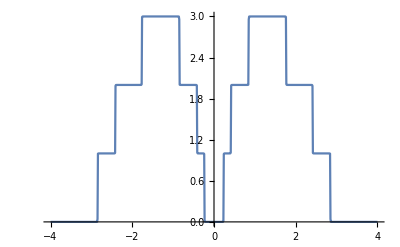
{1.72741,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

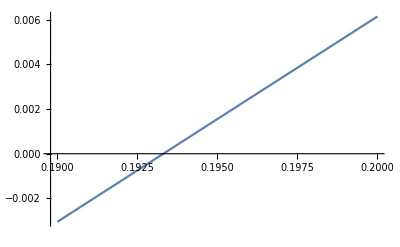
```mathematica
(*Energy[k_,ϵ1_]:=Energy[k,ϵ1]= g[k,ϵ1,4]+g[k,ϵ1,4]+g[k,ϵ1,4]+g[k,ϵ1,3]+g[k,ϵ1,3]+g[k,ϵ1,3]+g[k,ϵ1,2]+g[k,ϵ1,2]+g[k,ϵ1,2]+g[k,ϵ1,1]+g[k,ϵ1,1]+g[k,ϵ1,1]
Timing[g[0,0.3,4]]
{0.102359,0.1397806626369212}
2g[0,0.7857,2]+g[0,0.3,4]-Energy[0,1]/6
-2.719671641226995*^-7
ListLinePlot[Table[{x,(2g[0,x,2]+g[0,0.2,4]-Energy[0,0.3]/6)},{x,Range[0.19,0.2,0.0001]}]]
-Graphics-
Last[%106]
-Graphics-
Minimize[2g[0,x,2]+g[0,y,4]-Energy[0,1]/6,{x,y}]
{-8.694154306887423,{x->-1.0987308184914782*^17,y->-7.096396768732734*^16}}*)
```

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280823},{0.01,0.0000280879},{0.02,0.0000282571},{0.03,0.0000285944},{0.04,0.0000291098},{0.05,0.0000298192},{0.06,0.0000307455},{0.07,0.0000319209},{0.08,0.0000333893},{0.09,0.0000352109},{0.1,0.000037468},{0.11,0.0000402758},{0.12,0.0000437975},{0.13,0.0000482711},{0.14,0.0000540539},{0.15,0.0000617043},{0.16,0.0000721368},{0.17,0.0000869427},{0.18,0.000109113},{0.19,0.000144888},{0.2,0.000209332},{0.21,0.000348026},{0.22,0.000767552},{0.23,0.00425598},{0.24,0.598199},{0.25,0.817763},{0.26,0.880288},{0.27,0.909237},{0.28,0.925762},{0.29,0.936371},{0.3,0.943715},{0.31,0.949073},{0.32,0.953135},{0.33,0.956306},{0.34,0.958839},{0.35,0.960894},{0.36,0.962575},{0.37,0.963938},{0.38,0.964975},{0.39,0.965535},{0.4,0.964838},{0.41,0.95665},{0.42,1.81141},{0.43,1.9153},{0.44,1.9376},{0.45,1.94706},{0.46,1.95229},{0.47,1.95565},{0.48,1.95805},{0.49,1.95988},{0.5,1.96136},{0.51,1.9626},{0.52,1.96369},{0.53,1.96467},{0.54,1.96556},{0.55,1.96638},{0.56,1.96716},{0.57,1.96789},{0.58,1.9686},{0.59,1.96927},{0.6,1.96992},{0.61,1.97054},{0.62,1.97115},{0.63,1.97173},{0.64,1.9723},{0.65,1.97285},{0.66,1.97339},{0.67,1.97391},{0.68,1.97442},{0.69,1.97491},{0.7,1.97538},{0.71,1.97583},{0.72,1.97626},{0.73,1.97666},{0.74,1.97701},{0.75,1.97729},{0.76,1.97746},{0.77,1.97745},{0.78,1.97715},{0.79,1.97632},{0.8,1.97449},{0.81,1.97059},{0.82,1.96188},{0.83,1.93938},{0.84,1.85599},{0.85,1.34707},{0.86,1.97351},{0.87,2.25164},{0.88,2.40459},{0.89,2.50204},{0.9,2.57021},{0.91,2.62115},{0.92,2.66118},{0.93,2.69396},{0.94,2.72173},{0.95,2.74596},{0.96,2.76765},{0.97,2.78747},{0.98,2.80582},{0.99,2.82276},{1.,2.83779},{1.01,2.84903},{1.02,2.85104},{1.03,2.82776},{1.04,2.73017},{1.05,2.43548},{1.06,1.98218},{1.07,1.96758},{1.08,2.19927},{1.09,2.37542},{1.1,2.48665},{1.11,2.559},{1.12,2.60884},{1.13,2.64506},{1.14,2.67254},{1.15,2.69415},{1.16,2.71164},{1.17,2.72611},{1.18,2.73833},{1.19,2.7488},{1.2,2.75789},{1.21,2.76586},{1.22,2.77292},{1.23,2.77922},{1.24,2.78488},{1.25,2.78998},{1.26,2.79459},{1.27,2.79878},{1.28,2.80259},{1.29,2.80607},{1.3,2.80923},{1.31,2.81212},{1.32,2.81474},{1.33,2.81712},{1.34,2.81928},{1.35,2.82122},{1.36,2.82297},{1.37,2.82453},{1.38,2.8259},{1.39,2.82711},{1.4,2.82816},{1.41,2.82906},{1.42,2.8298},{1.43,2.83041},{1.44,2.83087},{1.45,2.8312},{1.46,2.83139},{1.47,2.83144},{1.48,2.83134},{1.49,2.83107},{1.5,2.83061},{1.51,2.82994},{1.52,2.82903},{1.53,2.82783},{1.54,2.82628},{1.55,2.82433},{1.56,2.82191},{1.57,2.81892},{1.58,2.81528},{1.59,2.81088},{1.6,2.80562},{1.61,2.79937},{1.62,2.79201},{1.63,2.78341},{1.64,2.77342},{1.65,2.76189},{1.66,2.74861},{1.67,2.7333},{1.68,2.7155},{1.69,2.69448},{1.7,2.66895},{1.71,2.63659},{1.72,2.59315},{1.73,2.53047},{1.74,2.43189},{1.75,2.25933},{1.76,1.90255},{1.77,1.54314},{1.78,0.817906},{1.79,1.4318},{1.8,1.85345},{1.81,1.91329},{1.82,1.93082},{1.83,1.93831},{1.84,1.94233},{1.85,1.94483},{1.86,1.94654},{1.87,1.94781},{1.88,1.94879},{1.89,1.94958},{1.9,1.95023},{1.91,1.95077},{1.92,1.95122},{1.93,1.95159},{1.94,1.95189},{1.95,1.95213},{1.96,1.95231},{1.97,1.95242},{1.98,1.95248},{1.99,1.95247},{2.,1.95241},{2.01,1.95229},{2.02,1.95211},{2.03,1.95187},{2.04,1.95157},{2.05,1.95122},{2.06,1.95081},{2.07,1.95036},{2.08,1.94985},{2.09,1.94929},{2.1,1.94869},{2.11,1.94803},{2.12,1.94732},{2.13,1.94656},{2.14,1.94573},{2.15,1.94482},{2.16,1.94383},{2.17,1.94273},{2.18,1.9415},{2.19,1.94011},{2.2,1.93854},{2.21,1.93674},{2.22,1.93468},{2.23,1.93231},{2.24,1.92959},{2.25,1.92647},{2.26,1.92291},{2.27,1.91886},{2.28,1.91429},{2.29,1.90913},{2.3,1.90334},{2.31,1.89683},{2.32,1.88947},{2.33,1.88102},{2.34,1.87104},{2.35,1.85868},{2.36,1.84235},{2.37,1.81896},{2.38,1.78203},{2.39,1.71645},{2.4,1.57781},{2.41,1.13433},{2.42,0.25966},{2.43,0.950245},{2.44,0.982172},{2.45,0.986274},{2.46,0.986441},{2.47,0.985568},{2.48,0.984286},{2.49,0.98278},{2.5,0.981109},{2.51,0.979294},{2.52,0.977334},{2.53,0.975222},{2.54,0.972943},{2.55,0.970478},{2.56,0.967803},{2.57,0.964889},{2.58,0.961702},{2.59,0.958204},{2.6,0.954352},{2.61,0.950098},{2.62,0.945389},{2.63,0.940168},{2.64,0.934375},{2.65,0.927944},{2.66,0.920807},{2.67,0.912894},{2.68,0.904131},{2.69,0.89444},{2.7,0.883736},{2.71,0.871923},{2.72,0.858885},{2.73,0.844473},{2.74,0.828479},{2.75,0.810601},{2.76,0.790383},{2.77,0.767124},{2.78,0.739721},{2.79,0.706427},{2.8,0.664429},{2.81,0.609101},{2.82,0.532582},{2.83,0.420731},{2.84,0.245007},{2.85,0.00613498},{2.86,0.000876905},{2.87,0.000432365},{2.88,0.000582149},{2.89,0.00213522},{2.9,0.000159774},{2.91,0.0000772101},{2.92,0.0000508914},{2.93,0.0000373544},{2.94,0.0000289595},{2.95,0.0000232393},{2.96,0.0000191137},{2.97,0.00001602},{2.98,0.0000136322},{2.99,0.0000117469},{3.,0.0000102304},{3.01,8.99157×10^-6},{3.02,7.96598×10^-6},{3.03,7.10706×10^-6},{3.04,6.38039×10^-6},{3.05,5.76004×10^-6},{3.06,5.22616×10^-6},{3.07,4.76335×10^-6},{3.08,4.3595×10^-6},{3.09,4.00497×10^-6},{3.1,3.69202×10^-6},{3.11,3.41438×10^-6},{3.12,3.16691×10^-6},{3.13,2.94538×10^-6},{3.14,2.74628×10^-6},{3.15,2.56668×10^-6},{3.16,2.40409×10^-6},{3.17,2.25642×10^-6},{3.18,2.12191×10^-6},{3.19,1.99903×10^-6},{3.2,1.88646×10^-6},{3.21,1.78309×10^-6},{3.22,1.68793×10^-6},{3.23,1.60013×10^-6},{3.24,1.51895×10^-6},{3.25,1.44375×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.1921×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59431×10^-7},{3.35,9.21006×10^-7},{3.36,8.848×10^-7},{3.37,8.50645×10^-7},{3.38,8.18389×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281077},{0.01,0.0000281057},{0.02,0.0000282511},{0.03,0.0000285476},{0.04,0.0000290027},{0.05,0.0000296284},{0.06,0.0000304415},{0.07,0.0000314654},{0.08,0.0000327314},{0.09,0.0000342808},{0.1,0.0000361694},{0.11,0.0000384723},{0.12,0.0000412927},{0.13,0.0000447761},{0.14,0.0000491336},{0.15,0.0000546849},{0.16,0.0000619401},{0.17,0.0000717722},{0.18,0.0000858197},{0.19,0.000107564},{0.2,0.000145796},{0.21,0.000229146},{0.22,0.000501799},{0.23,0.00319978},{0.24,0.552421},{0.25,0.788415},{0.26,0.860152},{0.27,0.894188},{0.28,0.913896},{0.29,0.926673},{0.3,0.935571},{0.31,0.942064},{0.32,0.946928},{0.33,0.950581},{0.34,0.953217},{0.35,0.954839},{0.36,0.955205},{0.37,0.953622},{0.38,0.948317},{0.39,0.934205},{0.4,0.891969},{0.41,0.670339},{0.42,0.631908},{0.43,1.20019},{0.44,1.41974},{0.45,1.53632},{0.46,1.60883},{0.47,1.65842},{0.48,1.69457},{0.49,1.72218},{0.5,1.74403},{0.51,1.76181},{0.52,1.77663},{0.53,1.78922},{0.54,1.8001},{0.55,1.80963},{0.56,1.8181},{0.57,1.8257},{0.58,1.83259},{0.59,1.8389},{0.6,1.84473},{0.61,1.85015},{0.62,1.85522},{0.63,1.86},{0.64,1.86453},{0.65,1.86884},{0.66,1.87298},{0.67,1.87696},{0.68,1.88081},{0.69,1.88454},{0.7,1.88819},{0.71,1.89175},{0.72,1.89525},{0.73,1.8987},{0.74,1.9021},{0.75,1.90545},{0.76,1.90875},{0.77,1.91196},{0.78,1.91501},{0.79,1.91775},{0.8,1.91982},{0.81,1.9203},{0.82,1.91652},{0.83,1.89848},{0.84,1.80051},{0.85,1.20382},{0.86,2.29377},{0.87,2.53197},{0.88,2.6377},{0.89,2.69882},{0.9,2.73961},{0.91,2.76949},{0.92,2.79292},{0.93,2.81224},{0.94,2.82884},{0.95,2.84355},{0.96,2.85686},{0.97,2.86901},{0.98,2.87993},{0.99,2.8891},{1.,2.8951},{1.01,2.89449},{1.02,2.87884},{1.03,2.82668},{1.04,2.68389},{1.05,2.35689},{1.06,1.9595},{1.07,1.94891},{1.08,2.16792},{1.09,2.35374},{1.1,2.47786},{1.11,2.56061},{1.12,2.61816},{1.13,2.66008},{1.14,2.6919},{1.15,2.71691},{1.16,2.73714},{1.17,2.75392},{1.18,2.76813},{1.19,2.78036},{1.2,2.79106},{1.21,2.80052},{1.22,2.80899},{1.23,2.81665},{1.24,2.82362},{1.25,2.83002},{1.26,2.83593},{1.27,2.84143},{1.28,2.84656},{1.29,2.85139},{1.3,2.85594},{1.31,2.86025},{1.32,2.86435},{1.33,2.86826},{1.34,2.872},{1.35,2.87558},{1.36,2.87901},{1.37,2.88231},{1.38,2.88546},{1.39,2.88848},{1.4,2.89135},{1.41,2.89409},{1.42,2.89667},{1.43,2.8991},{1.44,2.90136},{1.45,2.90345},{1.46,2.90536},{1.47,2.90708},{1.48,2.90862},{1.49,2.90997},{1.5,2.91113},{1.51,2.9121},{1.52,2.91287},{1.53,2.91344},{1.54,2.9138},{1.55,2.91391},{1.56,2.91375},{1.57,2.91326},{1.58,2.91234},{1.59,2.91089},{1.6,2.90875},{1.61,2.90576},{1.62,2.90167},{1.63,2.89626},{1.64,2.88925},{1.65,2.88035},{1.66,2.86927},{1.67,2.85574},{1.68,2.83944},{1.69,2.81999},{1.7,2.79671},{1.71,2.76827},{1.72,2.73171},{1.73,2.68047},{1.74,2.59953},{1.75,2.45201},{1.76,2.12765},{1.77,1.75404},{1.78,1.49126},{1.79,1.34016},{1.8,1.90712},{1.81,1.96991},{1.82,1.98194},{1.83,1.98499},{1.84,1.9857},{1.85,1.98565},{1.86,1.98534},{1.87,1.98493},{1.88,1.98449},{1.89,1.98402},{1.9,1.98355},{1.91,1.98306},{1.92,1.98255},{1.93,1.98202},{1.94,1.98146},{1.95,1.98086},{1.96,1.98023},{1.97,1.97955},{1.98,1.97882},{1.99,1.97804},{2.,1.9772},{2.01,1.9763},{2.02,1.97533},{2.03,1.9743},{2.04,1.97318},{2.05,1.97198},{2.06,1.9707},{2.07,1.96931},{2.08,1.96782},{2.09,1.96621},{2.1,1.96447},{2.11,1.96257},{2.12,1.96051},{2.13,1.95826},{2.14,1.95579},{2.15,1.95308},{2.16,1.95008},{2.17,1.94675},{2.18,1.94305},{2.19,1.93894},{2.2,1.93435},{2.21,1.92922},{2.22,1.92349},{2.23,1.91709},{2.24,1.90994},{2.25,1.90198},{2.26,1.89311},{2.27,1.88325},{2.28,1.87229},{2.29,1.86011},{2.3,1.84654},{2.31,1.83136},{2.32,1.81422},{2.33,1.79459},{2.34,1.77165},{2.35,1.74403},{2.36,1.7095},{2.37,1.66423},{2.38,1.60151},{2.39,1.50879},{2.4,1.3601},{2.41,1.08893},{2.42,0.904076},{2.43,0.80872},{2.44,0.101805},{2.45,0.648533},{2.46,0.870891},{2.47,0.924704},{2.48,0.945659},{2.49,0.956152},{2.5,0.962209},{2.51,0.966012},{2.52,0.968514},{2.53,0.97019},{2.54,0.971296},{2.55,0.971982},{2.56,0.972338},{2.57,0.972418},{2.58,0.972257},{2.59,0.971877},{2.6,0.971287},{2.61,0.970496},{2.62,0.969504},{2.63,0.968311},{2.64,0.966914},{2.65,0.965311},{2.66,0.963496},{2.67,0.961466},{2.68,0.959212},{2.69,0.956724},{2.7,0.953987},{2.71,0.950973},{2.72,0.947638},{2.73,0.943909},{2.74,0.939665},{2.75,0.934712},{2.76,0.928737},{2.77,0.921229},{2.78,0.911357},{2.79,0.897729},{2.8,0.87793},{2.81,0.8475},{2.82,0.797352},{2.83,0.705644},{2.84,0.501011},{2.85,0.0236596},{2.86,0.0104617},{2.87,0.000795657},{2.88,0.000283268},{2.89,0.000149018},{2.9,0.000093071},{2.91,0.0000640092},{2.92,0.000046845},{2.93,0.0000358155},{2.94,0.0000282903},{2.95,0.0000229199},{2.96,0.0000189501},{2.97,0.0000159316},{2.98,0.0000135822},{2.99,0.0000117175},{3.,0.0000102127},{3.01,8.98053×10^-6},{3.02,7.95895×10^-6},{3.03,7.10249×10^-6},{3.04,6.37737×10^-6},{3.05,5.75801×10^-6},{3.06,5.22477×10^-6},{3.07,4.76239×10^-6},{3.08,4.35883×10^-6},{3.09,4.00449×10^-6},{3.1,3.69168×10^-6},{3.11,3.41413×10^-6},{3.12,3.16673×10^-6},{3.13,2.94525×10^-6},{3.14,2.74618×10^-6},{3.15,2.5666×10^-6},{3.16,2.40403×10^-6},{3.17,2.25638×10^-6},{3.18,2.12188×10^-6},{3.19,1.999×10^-6},{3.2,1.88644×10^-6},{3.21,1.78307×10^-6},{3.22,1.68792×10^-6},{3.23,1.60012×10^-6},{3.24,1.51895×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.5943×10^-7},{3.35,9.21005×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18389×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280034},{0.01,0.0000280732},{0.02,0.000028305},{0.03,0.0000287055},{0.04,0.0000292869},{0.05,0.0000300674},{0.06,0.0000310731},{0.07,0.0000323396},{0.08,0.0000339154},{0.09,0.0000358667},{0.1,0.0000382847},{0.11,0.0000412966},{0.12,0.0000450839},{0.13,0.0000499123},{0.14,0.0000561836},{0.15,0.0000645294},{0.16,0.0000759928},{0.17,0.0000924038},{0.18,0.000117235},{0.19,0.000157795},{0.2,0.000231891},{0.21,0.000393704},{0.22,0.000887925},{0.23,0.00486017},{0.24,0.557156},{0.25,0.790098},{0.26,0.858828},{0.27,0.890186},{0.28,0.907721},{0.29,0.918808},{0.3,0.926444},{0.31,0.932055},{0.32,0.936392},{0.33,0.939883},{0.34,0.942777},{0.35,0.945227},{0.36,0.947313},{0.37,0.949063},{0.38,0.950433},{0.39,0.951222},{0.4,0.950699},{0.41,0.944783},{0.42,1.43035},{0.43,1.68169},{0.44,1.76849},{0.45,1.81204},{0.46,1.83816},{0.47,1.85555},{0.48,1.86796},{0.49,1.87724},{0.5,1.88445},{0.51,1.89021},{0.52,1.89491},{0.53,1.89883},{0.54,1.90214},{0.55,1.90499},{0.56,1.90747},{0.57,1.90965},{0.58,1.91159},{0.59,1.91335},{0.6,1.91494},{0.61,1.91641},{0.62,1.91778},{0.63,1.91905},{0.64,1.92026},{0.65,1.92142},{0.66,1.92252},{0.67,1.92358},{0.68,1.92462},{0.69,1.92562},{0.7,1.9266},{0.71,1.92756},{0.72,1.9285},{0.73,1.92942},{0.74,1.9303},{0.75,1.93114},{0.76,1.93192},{0.77,1.9326},{0.78,1.93308},{0.79,1.93322},{0.8,1.93266},{0.81,1.93058},{0.82,1.92474},{0.83,1.90701},{0.84,1.82645},{0.85,1.4737},{0.86,2.43707},{0.87,2.63281},{0.88,2.71649},{0.89,2.76341},{0.9,2.7938},{0.91,2.81543},{0.92,2.83189},{0.93,2.84509},{0.94,2.85614},{0.95,2.8657},{0.96,2.8742},{0.97,2.88183},{0.98,2.88863},{0.99,2.89433},{1.,2.89806},{1.01,2.89769},{1.02,2.88772},{1.03,2.85321},{1.04,2.75084},{1.05,2.47029},{1.06,2.01384},{1.07,1.98961},{1.08,2.24937},{1.09,2.43799},{1.1,2.55016},{1.11,2.61925},{1.12,2.66456},{1.13,2.69598},{1.14,2.71878},{1.15,2.73591},{1.16,2.74917},{1.17,2.75964},{1.18,2.76806},{1.19,2.77493},{1.2,2.78058},{1.21,2.78527},{1.22,2.78917},{1.23,2.79243},{1.24,2.79514},{1.25,2.79738},{1.26,2.79922},{1.27,2.8007},{1.28,2.80187},{1.29,2.80275},{1.3,2.80336},{1.31,2.80372},{1.32,2.80385},{1.33,2.80375},{1.34,2.80345},{1.35,2.80293},{1.36,2.8022},{1.37,2.80127},{1.38,2.80013},{1.39,2.79879},{1.4,2.79723},{1.41,2.79545},{1.42,2.79345},{1.43,2.79121},{1.44,2.78874},{1.45,2.78601},{1.46,2.78303},{1.47,2.77977},{1.48,2.77624},{1.49,2.77241},{1.5,2.76828},{1.51,2.76384},{1.52,2.75907},{1.53,2.75394},{1.54,2.74843},{1.55,2.7425},{1.56,2.73609},{1.57,2.72914},{1.58,2.72153},{1.59,2.71314},{1.6,2.70379},{1.61,2.69328},{1.62,2.68134},{1.63,2.66769},{1.64,2.65201},{1.65,2.63393},{1.66,2.61313},{1.67,2.58925},{1.68,2.562},{1.69,2.53106},{1.7,2.496},{1.71,2.45595},{1.72,2.40894},{1.73,2.35029},{1.74,2.26893},{1.75,2.13818},{1.76,1.88723},{1.77,1.80658},{1.78,1.79823},{1.79,1.48891},{1.8,1.19406},{1.81,1.63291},{1.82,1.78741},{1.83,1.84547},{1.84,1.87335},{1.85,1.88904},{1.86,1.89881},{1.87,1.90531},{1.88,1.90983},{1.89,1.91306},{1.9,1.9154},{1.91,1.9171},{1.92,1.91832},{1.93,1.91916},{1.94,1.9197},{1.95,1.91998},{1.96,1.92003},{1.97,1.91989},{1.98,1.91956},{1.99,1.91906},{2.,1.91839},{2.01,1.91755},{2.02,1.91655},{2.03,1.91539},{2.04,1.91406},{2.05,1.91257},{2.06,1.91092},{2.07,1.9091},{2.08,1.90712},{2.09,1.90498},{2.1,1.90267},{2.11,1.90021},{2.12,1.89757},{2.13,1.89477},{2.14,1.89179},{2.15,1.88861},{2.16,1.88522},{2.17,1.88159},{2.18,1.87767},{2.19,1.87342},{2.2,1.86876},{2.21,1.86362},{2.22,1.85791},{2.23,1.85151},{2.24,1.84431},{2.25,1.83617},{2.26,1.82696},{2.27,1.81652},{2.28,1.80472},{2.29,1.79142},{2.3,1.77648},{2.31,1.75974},{2.32,1.74104},{2.33,1.7201},{2.34,1.69644},{2.35,1.6692},{2.36,1.63671},{2.37,1.59582},{2.38,1.54046},{2.39,1.45867},{2.4,1.32528},{2.41,1.07857},{2.42,0.939949},{2.43,0.92573},{2.44,0.679116},{2.45,0.706866},{2.46,0.933992},{2.47,0.965121},{2.48,0.97462},{2.49,0.978669},{2.5,0.980685},{2.51,0.981751},{2.52,0.982305},{2.53,0.982553},{2.54,0.982602},{2.55,0.982511},{2.56,0.982314},{2.57,0.982028},{2.58,0.981659},{2.59,0.981204},{2.6,0.980654},{2.61,0.979992},{2.62,0.979197},{2.63,0.978246},{2.64,0.977108},{2.65,0.975753},{2.66,0.974147},{2.67,0.97226},{2.68,0.970062},{2.69,0.967528},{2.7,0.964639},{2.71,0.961381},{2.72,0.957745},{2.73,0.953723},{2.74,0.949291},{2.75,0.944394},{2.76,0.938896},{2.77,0.932511},{2.78,0.924662},{2.79,0.914222},{2.8,0.899008},{2.81,0.874666},{2.82,0.831885},{2.83,0.747667},{2.84,0.545048},{2.85,0.0280215},{2.86,0.00566172},{2.87,0.000660236},{2.88,0.000260676},{2.89,0.000142733},{2.9,0.0000908185},{2.91,0.0000630667},{2.92,0.0000464065},{2.93,0.000035595},{2.94,0.0000281726},{2.95,0.0000228539},{2.96,0.0000189117},{2.97,0.0000159084},{2.98,0.0000135679},{2.99,0.0000117084},{3.,0.0000102068},{3.01,8.97663×10^-6},{3.02,7.95632×10^-6},{3.03,7.1007×10^-6},{3.04,6.37613×10^-6},{3.05,5.75714×10^-6},{3.06,5.22416×10^-6},{3.07,4.76195×10^-6},{3.08,4.35851×10^-6},{3.09,4.00426×10^-6},{3.1,3.6915×10^-6},{3.11,3.414×10^-6},{3.12,3.16663×10^-6},{3.13,2.94518×10^-6},{3.14,2.74613×10^-6},{3.15,2.56656×10^-6},{3.16,2.404×10^-6},{3.17,2.25636×10^-6},{3.18,2.12186×10^-6},{3.19,1.99899×10^-6},{3.2,1.88643×10^-6},{3.21,1.78306×10^-6},{3.22,1.68791×10^-6},{3.23,1.60012×10^-6},{3.24,1.51894×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59429×10^-7},{3.35,9.21004×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280025},{0.01,0.0000280671},{0.02,0.0000282845},{0.03,0.0000286608},{0.04,0.0000292063},{0.05,0.0000299367},{0.06,0.0000308737},{0.07,0.0000320465},{0.08,0.0000334946},{0.09,0.0000352705},{0.1,0.0000374446},{0.11,0.0000401128},{0.12,0.0000434079},{0.13,0.0000475174},{0.14,0.0000527143},{0.15,0.0000594111},{0.16,0.0000682603},{0.17,0.00008036},{0.18,0.0000977165},{0.19,0.000124435},{0.2,0.000170408},{0.21,0.000266194},{0.22,0.000557076},{0.23,0.00308573},{0.24,0.412643},{0.25,0.665805},{0.26,0.759248},{0.27,0.806216},{0.28,0.833981},{0.29,0.852165},{0.3,0.864963},{0.31,0.874457},{0.32,0.88177},{0.33,0.88753},{0.34,0.892074},{0.35,0.895526},{0.36,0.897799},{0.37,0.898474},{0.38,0.896388},{0.39,0.888116},{0.4,0.860031},{0.41,0.685628},{0.42,1.3474},{0.43,1.6823},{0.44,1.76968},{0.45,1.81058},{0.46,1.83469},{0.47,1.85083},{0.48,1.86252},{0.49,1.87148},{0.5,1.87863},{0.51,1.88451},{0.52,1.88947},{0.53,1.89375},{0.54,1.89749},{0.55,1.90082},{0.56,1.90382},{0.57,1.90655},{0.58,1.90907},{0.59,1.91142},{0.6,1.91362},{0.61,1.9157},{0.62,1.91769},{0.63,1.91959},{0.64,1.92143},{0.65,1.92321},{0.66,1.92495},{0.67,1.92664},{0.68,1.9283},{0.69,1.92993},{0.7,1.93154},{0.71,1.93312},{0.72,1.93467},{0.73,1.9362},{0.74,1.9377},{0.75,1.93915},{0.76,1.94055},{0.77,1.94184},{0.78,1.94297},{0.79,1.94381},{0.8,1.94406},{0.81,1.94308},{0.82,1.93912},{0.83,1.92615},{0.84,1.86929},{0.85,1.57629},{0.86,2.30933},{0.87,2.52317},{0.88,2.62323},{0.89,2.68156},{0.9,2.72004},{0.91,2.74758},{0.92,2.76847},{0.93,2.78501},{0.94,2.79855},{0.95,2.8099},{0.96,2.81953},{0.97,2.82764},{0.98,2.83417},{0.99,2.83869},{1.,2.84005},{1.01,2.83557},{1.02,2.81893},{1.03,2.77404},{1.04,2.65785},{1.05,2.37096},{1.06,1.93339},{1.07,1.92307},{1.08,2.20608},{1.09,2.41151},{1.1,2.53213},{1.11,2.60543},{1.12,2.65299},{1.13,2.68574},{1.14,2.70941},{1.15,2.72718},{1.16,2.74095},{1.17,2.75188},{1.18,2.76071},{1.19,2.76797},{1.2,2.774},{1.21,2.77905},{1.22,2.7833},{1.23,2.78689},{1.24,2.78991},{1.25,2.79245},{1.26,2.79456},{1.27,2.79629},{1.28,2.79768},{1.29,2.79874},{1.3,2.79951},{1.31,2.79999},{1.32,2.80022},{1.33,2.80019},{1.34,2.79992},{1.35,2.79942},{1.36,2.79869},{1.37,2.79773},{1.38,2.79656},{1.39,2.79515},{1.4,2.79352},{1.41,2.79164},{1.42,2.78952},{1.43,2.78712},{1.44,2.78444},{1.45,2.78144},{1.46,2.77811},{1.47,2.7744},{1.48,2.77029},{1.49,2.76575},{1.5,2.76075},{1.51,2.75525},{1.52,2.74924},{1.53,2.74268},{1.54,2.73554},{1.55,2.7278},{1.56,2.7194},{1.57,2.7103},{1.58,2.7004},{1.59,2.68957},{1.6,2.67765},{1.61,2.6644},{1.62,2.64952},{1.63,2.63263},{1.64,2.61329},{1.65,2.59103},{1.66,2.56533},{1.67,2.53573},{1.68,2.50187},{1.69,2.46351},{1.7,2.42059},{1.71,2.37303},{1.72,2.3202},{1.73,2.25965},{1.74,2.18384},{1.75,2.07191},{1.76,1.86579},{1.77,1.86755},{1.78,1.91097},{1.79,1.86523},{1.8,1.67473},{1.81,1.21273},{1.82,1.24803},{1.83,1.56685},{1.84,1.72674},{1.85,1.8044},{1.86,1.84713},{1.87,1.87327},{1.88,1.89057},{1.89,1.90271},{1.9,1.91162},{1.91,1.91837},{1.92,1.92362},{1.93,1.9278},{1.94,1.93117},{1.95,1.93392},{1.96,1.93619},{1.97,1.93808},{1.98,1.93964},{1.99,1.94095},{2.,1.94205},{2.01,1.94295},{2.02,1.94371},{2.03,1.94432},{2.04,1.94481},{2.05,1.9452},{2.06,1.94549},{2.07,1.9457},{2.08,1.94582},{2.09,1.94586},{2.1,1.94582},{2.11,1.9457},{2.12,1.9455},{2.13,1.94521},{2.14,1.94482},{2.15,1.94432},{2.16,1.94371},{2.17,1.94296},{2.18,1.94208},{2.19,1.94103},{2.2,1.93981},{2.21,1.93841},{2.22,1.9368},{2.23,1.93499},{2.24,1.93295},{2.25,1.93068},{2.26,1.92819},{2.27,1.92545},{2.28,1.92247},{2.29,1.91922},{2.3,1.91568},{2.31,1.91176},{2.32,1.90734},{2.33,1.90215},{2.34,1.89575},{2.35,1.88736},{2.36,1.87554},{2.37,1.85768},{2.38,1.82858},{2.39,1.77664},{2.4,1.66926},{2.41,1.35363},{2.42,0.0763565},{2.43,0.970452},{2.44,0.973795},{2.45,0.972333},{2.46,0.970729},{2.47,0.969212},{2.48,0.967757},{2.49,0.966331},{2.5,0.964912},{2.51,0.963487},{2.52,0.962046},{2.53,0.960584},{2.54,0.959092},{2.55,0.957564},{2.56,0.955991},{2.57,0.954357},{2.58,0.952644},{2.59,0.950829},{2.6,0.94888},{2.61,0.946759},{2.62,0.94442},{2.63,0.941812},{2.64,0.938874},{2.65,0.93554},{2.66,0.931741},{2.67,0.927403},{2.68,0.922456},{2.69,0.916829},{2.7,0.910458},{2.71,0.903285},{2.72,0.895258},{2.73,0.886323},{2.74,0.87641},{2.75,0.865405},{2.76,0.85309},{2.77,0.839048},{2.78,0.822481},{2.79,0.801891},{2.8,0.774474},{2.81,0.734918},{2.82,0.672773},{2.83,0.56576},{2.84,0.358321},{2.85,0.00846408},{2.86,0.00289757},{2.87,0.00319453},{2.88,0.000346214},{2.89,0.000155842},{2.9,0.0000940627},{2.91,0.0000641014},{2.92,0.0000467943},{2.93,0.0000357578},{2.94,0.0000282469},{2.95,0.0000228902},{2.96,0.0000189303},{2.97,0.0000159185},{2.98,0.0000135735},{2.99,0.0000117117},{3.,0.0000102087},{3.01,8.97779×10^-6},{3.02,7.95704×10^-6},{3.03,7.10115×10^-6},{3.04,6.37642×10^-6},{3.05,5.75733×10^-6},{3.06,5.22428×10^-6},{3.07,4.76204×10^-6},{3.08,4.35856×10^-6},{3.09,4.0043×10^-6},{3.1,3.69153×10^-6},{3.11,3.41402×10^-6},{3.12,3.16665×10^-6},{3.13,2.94519×10^-6},{3.14,2.74614×10^-6},{3.15,2.56657×10^-6},{3.16,2.404×10^-6},{3.17,2.25636×10^-6},{3.18,2.12186×10^-6},{3.19,1.99899×10^-6},{3.2,1.88643×10^-6},{3.21,1.78306×10^-6},{3.22,1.68791×10^-6},{3.23,1.60012×10^-6},{3.24,1.51894×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59429×10^-7},{3.35,9.21004×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000275543},{0.01,0.0000276896},{0.02,0.0000279736},{0.03,0.0000284156},{0.04,0.0000290292},{0.05,0.0000298337},{0.06,0.0000308555},{0.07,0.0000321299},{0.08,0.000033704},{0.09,0.0000356418},{0.1,0.00003803},{0.11,0.0000409888},{0.12,0.0000446881},{0.13,0.0000493737},{0.14,0.0000554136},{0.15,0.0000633796},{0.16,0.0000742049},{0.17,0.0000895083},{0.18,0.000112331},{0.19,0.000149035},{0.2,0.000215144},{0.21,0.000358664},{0.22,0.000807032},{0.23,0.00496568},{0.24,0.7152},{0.25,0.89092},{0.26,0.933419},{0.27,0.95182},{0.28,0.961869},{0.29,0.968088},{0.3,0.972247},{0.31,0.975167},{0.32,0.977276},{0.33,0.978807},{0.34,0.97988},{0.35,0.980527},{0.36,0.980685},{0.37,0.980121},{0.38,0.978199},{0.39,0.97299},{0.4,0.956616},{0.41,0.856581},{0.42,1.323},{0.43,1.67549},{0.44,1.77982},{0.45,1.82995},{0.46,1.85952},{0.47,1.87908},{0.48,1.89302},{0.49,1.90349},{0.5,1.91165},{0.51,1.91822},{0.52,1.92363},{0.53,1.92817},{0.54,1.93206},{0.55,1.93542},{0.56,1.93838},{0.57,1.94099},{0.58,1.94333},{0.59,1.94544},{0.6,1.94736},{0.61,1.94911},{0.62,1.95073},{0.63,1.95222},{0.64,1.95362},{0.65,1.95492},{0.66,1.95614},{0.67,1.9573},{0.68,1.95839},{0.69,1.95943},{0.7,1.96043},{0.71,1.96139},{0.72,1.9623},{0.73,1.96319},{0.74,1.96404},{0.75,1.96485},{0.76,1.96562},{0.77,1.96634},{0.78,1.96699},{0.79,1.96751},{0.8,1.96783},{0.81,1.9677},{0.82,1.96656},{0.83,1.96239},{0.84,1.94309},{0.85,2.21347},{0.86,2.75012},{0.87,2.84806},{0.88,2.88901},{0.89,2.91192},{0.9,2.92687},{0.91,2.93763},{0.92,2.94589},{0.93,2.95252},{0.94,2.95801},{0.95,2.96261},{0.96,2.96644},{0.97,2.96952},{0.98,2.97177},{0.99,2.97303},{1.,2.97297},{1.01,2.9711},{1.02,2.96662},{1.03,2.95831},{1.04,2.94423},{1.05,2.92133},{1.06,2.88478},{1.07,2.82706},{1.08,2.73704},{1.09,2.60078},{1.1,2.40874},{1.11,2.17616},{1.12,1.96567},{1.13,1.85907},{1.14,1.87871},{1.15,1.97711},{1.16,2.09865},{1.17,2.21278},{1.18,2.30953},{1.19,2.3884},{1.2,2.45199},{1.21,2.50329},{1.22,2.54497},{1.23,2.57912},{1.24,2.60736},{1.25,2.63092},{1.26,2.65074},{1.27,2.66754},{1.28,2.68189},{1.29,2.69421},{1.3,2.70484},{1.31,2.71405},{1.32,2.72206},{1.33,2.72904},{1.34,2.73512},{1.35,2.7404},{1.36,2.74498},{1.37,2.74892},{1.38,2.75228},{1.39,2.75508},{1.4,2.75736},{1.41,2.75914},{1.42,2.76044},{1.43,2.76126},{1.44,2.76163},{1.45,2.76155},{1.46,2.76104},{1.47,2.7601},{1.48,2.75877},{1.49,2.75705},{1.5,2.75498},{1.51,2.75257},{1.52,2.74984},{1.53,2.74681},{1.54,2.74348},{1.55,2.73982},{1.56,2.73581},{1.57,2.73137},{1.58,2.7264},{1.59,2.72076},{1.6,2.71426},{1.61,2.70666},{1.62,2.69772},{1.63,2.68713},{1.64,2.67461},{1.65,2.65986},{1.66,2.64266},{1.67,2.62283},{1.68,2.60025},{1.69,2.57485},{1.7,2.54641},{1.71,2.51425},{1.72,2.47644},{1.73,2.42808},{1.74,2.35754},{1.75,2.23692},{1.76,1.99163},{1.77,1.82046},{1.78,1.74656},{1.79,1.18605},{1.8,1.73638},{1.81,1.93317},{1.82,1.96553},{1.83,1.97426},{1.84,1.97707},{1.85,1.97785},{1.86,1.97779},{1.87,1.97733},{1.88,1.97666},{1.89,1.97586},{1.9,1.97498},{1.91,1.97403},{1.92,1.97303},{1.93,1.97197},{1.94,1.97087},{1.95,1.96972},{1.96,1.96852},{1.97,1.96726},{1.98,1.96596},{1.99,1.9646},{2.,1.96318},{2.01,1.96171},{2.02,1.96018},{2.03,1.9586},{2.04,1.95697},{2.05,1.95528},{2.06,1.95353},{2.07,1.95173},{2.08,1.94988},{2.09,1.94797},{2.1,1.946},{2.11,1.94396},{2.12,1.94185},{2.13,1.93964},{2.14,1.93732},{2.15,1.93488},{2.16,1.93228},{2.17,1.92949},{2.18,1.92647},{2.19,1.92319},{2.2,1.91958},{2.21,1.9156},{2.22,1.9112},{2.23,1.9063},{2.24,1.90085},{2.25,1.89478},{2.26,1.88803},{2.27,1.88053},{2.28,1.87223},{2.29,1.86304},{2.3,1.85287},{2.31,1.84158},{2.32,1.82896},{2.33,1.81463},{2.34,1.79792},{2.35,1.77767},{2.36,1.75179},{2.37,1.71642},{2.38,1.66411},{2.39,1.57928},{2.4,1.42375},{2.41,1.06755},{2.42,0.537649},{2.43,0.143786},{2.44,0.809321},{2.45,0.891631},{2.46,0.916866},{2.47,0.928307},{2.48,0.934558},{2.49,0.938317},{2.5,0.940678},{2.51,0.942159},{2.52,0.943038},{2.53,0.94347},{2.54,0.943546},{2.55,0.94332},{2.56,0.942822},{2.57,0.942067},{2.58,0.941057},{2.59,0.939787},{2.6,0.938248},{2.61,0.936424},{2.62,0.934298},{2.63,0.93185},{2.64,0.929062},{2.65,0.925912},{2.66,0.922379},{2.67,0.918445},{2.68,0.91409},{2.69,0.909289},{2.7,0.904018},{2.71,0.898236},{2.72,0.891887},{2.73,0.884877},{2.74,0.877056},{2.75,0.868179},{2.76,0.857845},{2.77,0.845406},{2.78,0.829803},{2.79,0.809282},{2.8,0.780871},{2.81,0.739307},{2.82,0.674613},{2.83,0.565599},{2.84,0.357634},{2.85,0.00862855},{2.86,0.00845157},{2.87,0.00210798},{2.88,0.000356377},{2.89,0.000161312},{2.9,0.000096225},{2.91,0.0000650302},{2.92,0.0000472286},{2.93,0.0000359755},{2.94,0.0000283624},{2.95,0.0000229543},{2.96,0.0000189674},{2.97,0.0000159405},{2.98,0.000013587},{2.99,0.0000117201},{3.,0.0000102141},{3.01,8.98135×10^-6},{3.02,7.95941×10^-6},{3.03,7.10275×10^-6},{3.04,6.37751×10^-6},{3.05,5.75809×10^-6},{3.06,5.22482×10^-6},{3.07,4.76241×10^-6},{3.08,4.35883×10^-6},{3.09,4.00449×10^-6},{3.1,3.69167×10^-6},{3.11,3.41412×10^-6},{3.12,3.16672×10^-6},{3.13,2.94524×10^-6},{3.14,2.74618×10^-6},{3.15,2.5666×10^-6},{3.16,2.40403×10^-6},{3.17,2.25638×10^-6},{3.18,2.12188×10^-6},{3.19,1.999×10^-6},{3.2,1.88644×10^-6},{3.21,1.78307×10^-6},{3.22,1.68791×10^-6},{3.23,1.60012×10^-6},{3.24,1.51895×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.5943×10^-7},{3.35,9.21005×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280823},{0.01,0.0000280879},{0.02,0.0000282571},{0.03,0.0000285944},{0.04,0.0000291098},{0.05,0.0000298192},{0.06,0.0000307455},{0.07,0.0000319209},{0.08,0.0000333893},{0.09,0.0000352109},{0.1,0.000037468},{0.11,0.0000402758},{0.12,0.0000437975},{0.13,0.0000482711},{0.14,0.0000540539},{0.15,0.0000617043},{0.16,0.0000721368},{0.17,0.0000869427},{0.18,0.000109113},{0.19,0.000144888},{0.2,0.000209332},{0.21,0.000348026},{0.22,0.000767552},{0.23,0.00425598},{0.24,0.598199},{0.25,0.817763},{0.26,0.880288},{0.27,0.909237},{0.28,0.925762},{0.29,0.936371},{0.3,0.943715},{0.31,0.949073},{0.32,0.953135},{0.33,0.956306},{0.34,0.958839},{0.35,0.960894},{0.36,0.962575},{0.37,0.963938},{0.38,0.964975},{0.39,0.965535},{0.4,0.964838},{0.41,0.95665},{0.42,1.81141},{0.43,1.9153},{0.44,1.9376},{0.45,1.94706},{0.46,1.95229},{0.47,1.95565},{0.48,1.95805},{0.49,1.95988},{0.5,1.96136},{0.51,1.9626},{0.52,1.96369},{0.53,1.96467},{0.54,1.96556},{0.55,1.96638},{0.56,1.96716},{0.57,1.96789},{0.58,1.9686},{0.59,1.96927},{0.6,1.96992},{0.61,1.97054},{0.62,1.97115},{0.63,1.97173},{0.64,1.9723},{0.65,1.97285},{0.66,1.97339},{0.67,1.97391},{0.68,1.97442},{0.69,1.97491},{0.7,1.97538},{0.71,1.97583},{0.72,1.97626},{0.73,1.97666},{0.74,1.97701},{0.75,1.97729},{0.76,1.97746},{0.77,1.97745},{0.78,1.97715},{0.79,1.97632},{0.8,1.97449},{0.81,1.97059},{0.82,1.96188},{0.83,1.93938},{0.84,1.85599},{0.85,1.34707},{0.86,1.97351},{0.87,2.25164},{0.88,2.40459},{0.89,2.50204},{0.9,2.57021},{0.91,2.62115},{0.92,2.66118},{0.93,2.69396},{0.94,2.72173},{0.95,2.74596},{0.96,2.76765},{0.97,2.78747},{0.98,2.80582},{0.99,2.82276},{1.,2.83779},{1.01,2.84903},{1.02,2.85104},{1.03,2.82776},{1.04,2.73017},{1.05,2.43548},{1.06,1.98218},{1.07,1.96758},{1.08,2.19927},{1.09,2.37542},{1.1,2.48665},{1.11,2.559},{1.12,2.60884},{1.13,2.64506},{1.14,2.67254},{1.15,2.69415},{1.16,2.71164},{1.17,2.72611},{1.18,2.73833},{1.19,2.7488},{1.2,2.75789},{1.21,2.76586},{1.22,2.77292},{1.23,2.77922},{1.24,2.78488},{1.25,2.78998},{1.26,2.79459},{1.27,2.79878},{1.28,2.80259},{1.29,2.80607},{1.3,2.80923},{1.31,2.81212},{1.32,2.81474},{1.33,2.81712},{1.34,2.81928},{1.35,2.82122},{1.36,2.82297},{1.37,2.82453},{1.38,2.8259},{1.39,2.82711},{1.4,2.82816},{1.41,2.82906},{1.42,2.8298},{1.43,2.83041},{1.44,2.83087},{1.45,2.8312},{1.46,2.83139},{1.47,2.83144},{1.48,2.83134},{1.49,2.83107},{1.5,2.83061},{1.51,2.82994},{1.52,2.82903},{1.53,2.82783},{1.54,2.82628},{1.55,2.82433},{1.56,2.82191},{1.57,2.81892},{1.58,2.81528},{1.59,2.81088},{1.6,2.80562},{1.61,2.79937},{1.62,2.79201},{1.63,2.78341},{1.64,2.77342},{1.65,2.76189},{1.66,2.74861},{1.67,2.7333},{1.68,2.7155},{1.69,2.69448},{1.7,2.66895},{1.71,2.63659},{1.72,2.59315},{1.73,2.53047},{1.74,2.43189},{1.75,2.25933},{1.76,1.90255},{1.77,1.54314},{1.78,0.817906},{1.79,1.4318},{1.8,1.85345},{1.81,1.91329},{1.82,1.93082},{1.83,1.93831},{1.84,1.94233},{1.85,1.94483},{1.86,1.94654},{1.87,1.94781},{1.88,1.94879},{1.89,1.94958},{1.9,1.95023},{1.91,1.95077},{1.92,1.95122},{1.93,1.95159},{1.94,1.95189},{1.95,1.95213},{1.96,1.95231},{1.97,1.95242},{1.98,1.95248},{1.99,1.95247},{2.,1.95241},{2.01,1.95229},{2.02,1.95211},{2.03,1.95187},{2.04,1.95157},{2.05,1.95122},{2.06,1.95081},{2.07,1.95036},{2.08,1.94985},{2.09,1.94929},{2.1,1.94869},{2.11,1.94803},{2.12,1.94732},{2.13,1.94656},{2.14,1.94573},{2.15,1.94482},{2.16,1.94383},{2.17,1.94273},{2.18,1.9415},{2.19,1.94011},{2.2,1.93854},{2.21,1.93674},{2.22,1.93468},{2.23,1.93231},{2.24,1.92959},{2.25,1.92647},{2.26,1.92291},{2.27,1.91886},{2.28,1.91429},{2.29,1.90913},{2.3,1.90334},{2.31,1.89683},{2.32,1.88947},{2.33,1.88102},{2.34,1.87104},{2.35,1.85868},{2.36,1.84235},{2.37,1.81896},{2.38,1.78203},{2.39,1.71645},{2.4,1.57781},{2.41,1.13433},{2.42,0.25966},{2.43,0.950245},{2.44,0.982172},{2.45,0.986274},{2.46,0.986441},{2.47,0.985568},{2.48,0.984286},{2.49,0.98278},{2.5,0.981109},{2.51,0.979294},{2.52,0.977334},{2.53,0.975222},{2.54,0.972943},{2.55,0.970478},{2.56,0.967803},{2.57,0.964889},{2.58,0.961702},{2.59,0.958204},{2.6,0.954352},{2.61,0.950098},{2.62,0.945389},{2.63,0.940168},{2.64,0.934375},{2.65,0.927944},{2.66,0.920807},{2.67,0.912894},{2.68,0.904131},{2.69,0.89444},{2.7,0.883736},{2.71,0.871923},{2.72,0.858885},{2.73,0.844473},{2.74,0.828479},{2.75,0.810601},{2.76,0.790383},{2.77,0.767124},{2.78,0.739721},{2.79,0.706427},{2.8,0.664429},{2.81,0.609101},{2.82,0.532582},{2.83,0.420731},{2.84,0.245007},{2.85,0.00613498},{2.86,0.000876905},{2.87,0.000432365},{2.88,0.000582149},{2.89,0.00213522},{2.9,0.000159774},{2.91,0.0000772101},{2.92,0.0000508914},{2.93,0.0000373544},{2.94,0.0000289595},{2.95,0.0000232393},{2.96,0.0000191137},{2.97,0.00001602},{2.98,0.0000136322},{2.99,0.0000117469},{3.,0.0000102304},{3.01,8.99157×10^-6},{3.02,7.96598×10^-6},{3.03,7.10706×10^-6},{3.04,6.38039×10^-6},{3.05,5.76004×10^-6},{3.06,5.22616×10^-6},{3.07,4.76335×10^-6},{3.08,4.3595×10^-6},{3.09,4.00497×10^-6},{3.1,3.69202×10^-6},{3.11,3.41438×10^-6},{3.12,3.16691×10^-6},{3.13,2.94538×10^-6},{3.14,2.74628×10^-6},{3.15,2.56668×10^-6},{3.16,2.40409×10^-6},{3.17,2.25642×10^-6},{3.18,2.12191×10^-6},{3.19,1.99903×10^-6},{3.2,1.88646×10^-6},{3.21,1.78309×10^-6},{3.22,1.68793×10^-6},{3.23,1.60013×10^-6},{3.24,1.51895×10^-6},{3.25,1.44375×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.1921×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59431×10^-7},{3.35,9.21006×10^-7},{3.36,8.848×10^-7},{3.37,8.50645×10^-7},{3.38,8.18389×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279838},{0.01,0.0000280679},{0.02,0.0000282919},{0.03,0.0000286624},{0.04,0.0000291894},{0.05,0.0000298868},{0.06,0.0000307732},{0.07,0.000031873},{0.08,0.0000332182},{0.09,0.0000348498},{0.1,0.0000368217},{0.11,0.0000392038},{0.12,0.0000420889},{0.13,0.000045601},{0.14,0.0000499096},{0.15,0.000055252},{0.16,0.0000619728},{0.17,0.0000706008},{0.18,0.0000820197},{0.19,0.0000979296},{0.2,0.000122431},{0.21,0.000169496},{0.22,0.000320292},{0.23,0.00212567},{0.24,0.454359},{0.25,0.720401},{0.26,0.814766},{0.27,0.861744},{0.28,0.88938},{0.29,0.907322},{0.3,0.919731},{0.31,0.928665},{0.32,0.935228},{0.33,0.940022},{0.34,0.943333},{0.35,0.945184},{0.36,0.945277},{0.37,0.942731},{0.38,0.935286},{0.39,0.916444},{0.4,0.861068},{0.41,0.558413},{0.42,0.584735},{0.43,1.24054},{0.44,1.46199},{0.45,1.57457},{0.46,1.64324},{0.47,1.68971},{0.48,1.72335},{0.49,1.74888},{0.5,1.76894},{0.51,1.78514},{0.52,1.79851},{0.53,1.80972},{0.54,1.81927},{0.55,1.82749},{0.56,1.83465},{0.57,1.84093},{0.58,1.84649},{0.59,1.85144},{0.6,1.85587},{0.61,1.85987},{0.62,1.86348},{0.63,1.86676},{0.64,1.86975},{0.65,1.87249},{0.66,1.87501},{0.67,1.87733},{0.68,1.87947},{0.69,1.88145},{0.7,1.88329},{0.71,1.885},{0.72,1.88659},{0.73,1.88808},{0.74,1.88946},{0.75,1.89075},{0.76,1.89195},{0.77,1.89305},{0.78,1.89407},{0.79,1.89499},{0.8,1.89578},{0.81,1.8964},{0.82,1.89666},{0.83,1.89598},{0.84,1.89068},{0.85,2.66048},{0.86,2.86838},{0.87,2.88573},{0.88,2.8915},{0.89,2.89428},{0.9,2.89589},{0.91,2.89693},{0.92,2.89764},{0.93,2.89814},{0.94,2.89847},{0.95,2.89867},{0.96,2.89873},{0.97,2.89863},{0.98,2.89836},{0.99,2.89784},{1.,2.89701},{1.01,2.89574},{1.02,2.89383},{1.03,2.89099},{1.04,2.8867},{1.05,2.88015},{1.06,2.86991},{1.07,2.85333},{1.08,2.82536},{1.09,2.77571},{1.1,2.68264},{1.11,2.50318},{1.12,2.19273},{1.13,1.90009},{1.14,1.96705},{1.15,2.22261},{1.16,2.42364},{1.17,2.54979},{1.18,2.62832},{1.19,2.67914},{1.2,2.71348},{1.21,2.73756},{1.22,2.75497},{1.23,2.76785},{1.24,2.77755},{1.25,2.78493},{1.26,2.79059},{1.27,2.79493},{1.28,2.79824},{1.29,2.80073},{1.3,2.80255},{1.31,2.80383},{1.32,2.80464},{1.33,2.80504},{1.34,2.8051},{1.35,2.80482},{1.36,2.80425},{1.37,2.80338},{1.38,2.80223},{1.39,2.80079},{1.4,2.79905},{1.41,2.79702},{1.42,2.79469},{1.43,2.79203},{1.44,2.78906},{1.45,2.78576},{1.46,2.78213},{1.47,2.77817},{1.48,2.7739},{1.49,2.76931},{1.5,2.76442},{1.51,2.75924},{1.52,2.75378},{1.53,2.74802},{1.54,2.74196},{1.55,2.73556},{1.56,2.72876},{1.57,2.72147},{1.58,2.71357},{1.59,2.70488},{1.6,2.6952},{1.61,2.68428},{1.62,2.67186},{1.63,2.65765},{1.64,2.64138},{1.65,2.62279},{1.66,2.60174},{1.67,2.57818},{1.68,2.55217},{1.69,2.52392},{1.7,2.49365},{1.71,2.46134},{1.72,2.42617},{1.73,2.38524},{1.74,2.33089},{1.75,2.2441},{1.76,2.07293},{1.77,1.92879},{1.78,1.94202},{1.79,1.93119},{1.8,1.87973},{1.81,1.59641},{1.82,1.42076},{1.83,1.82522},{1.84,1.90792},{1.85,1.93405},{1.86,1.94539},{1.87,1.95126},{1.88,1.95463},{1.89,1.95667},{1.9,1.95793},{1.91,1.95869},{1.92,1.95911},{1.93,1.95927},{1.94,1.95924},{1.95,1.95905},{1.96,1.95874},{1.97,1.9583},{1.98,1.95777},{1.99,1.95715},{2.,1.95644},{2.01,1.95565},{2.02,1.9548},{2.03,1.95388},{2.04,1.95289},{2.05,1.95185},{2.06,1.95076},{2.07,1.94962},{2.08,1.94843},{2.09,1.94718},{2.1,1.94589},{2.11,1.94453},{2.12,1.94311},{2.13,1.94161},{2.14,1.94002},{2.15,1.93831},{2.16,1.93646},{2.17,1.93443},{2.18,1.93218},{2.19,1.92968},{2.2,1.92688},{2.21,1.92373},{2.22,1.92016},{2.23,1.91613},{2.24,1.91157},{2.25,1.90644},{2.26,1.90068},{2.27,1.89425},{2.28,1.88709},{2.29,1.87915},{2.3,1.87038},{2.31,1.86065},{2.32,1.84979},{2.33,1.83747},{2.34,1.82308},{2.35,1.80553},{2.36,1.78286},{2.37,1.75149},{2.38,1.70468},{2.39,1.62892},{2.4,1.49385},{2.41,1.21448},{2.42,0.978618},{2.43,0.643038},{2.44,0.993519},{2.45,0.997958},{2.46,0.997988},{2.47,0.997768},{2.48,0.997552},{2.49,0.997362},{2.5,0.997194},{2.51,0.997044},{2.52,0.996905},{2.53,0.996773},{2.54,0.996643},{2.55,0.996512},{2.56,0.996375},{2.57,0.996225},{2.58,0.996058},{2.59,0.995868},{2.6,0.995648},{2.61,0.995392},{2.62,0.995093},{2.63,0.994745},{2.64,0.994343},{2.65,0.993883},{2.66,0.993364},{2.67,0.992784},{2.68,0.992147},{2.69,0.991458},{2.7,0.990723},{2.71,0.989952},{2.72,0.989155},{2.73,0.988335},{2.74,0.987489},{2.75,0.986589},{2.76,0.985573},{2.77,0.984306},{2.78,0.982535},{2.79,0.979784},{2.8,0.975164},{2.81,0.96693},{2.82,0.951309},{2.83,0.91832},{2.84,0.826229},{2.85,0.333312},{2.86,0.00215748},{2.87,0.000543285},{2.88,0.000244526},{2.89,0.000139035},{2.9,0.0000897075},{2.91,0.00006267},{2.92,0.0000462468},{2.93,0.0000355246},{2.94,0.0000281393},{2.95,0.0000228373},{2.96,0.000018903},{2.97,0.0000159037},{2.98,0.0000135652},{2.99,0.0000117069},{3.,0.0000102058},{3.01,8.97607×10^-6},{3.02,7.95598×10^-6},{3.03,7.10048×10^-6},{3.04,6.37599×10^-6},{3.05,5.75705×10^-6},{3.06,5.2241×10^-6},{3.07,4.76191×10^-6},{3.08,4.35848×10^-6},{3.09,4.00424×10^-6},{3.1,3.69149×10^-6},{3.11,3.41399×10^-6},{3.12,3.16663×10^-6},{3.13,2.94517×10^-6},{3.14,2.74613×10^-6},{3.15,2.56656×10^-6},{3.16,2.404×10^-6},{3.17,2.25636×10^-6},{3.18,2.12186×10^-6},{3.19,1.99899×10^-6},{3.2,1.88643×10^-6},{3.21,1.78306×10^-6},{3.22,1.68791×10^-6},{3.23,1.60012×10^-6},{3.24,1.51894×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59429×10^-7},{3.35,9.21004×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280039},{0.01,0.0000280792},{0.02,0.0000283185},{0.03,0.0000287289},{0.04,0.0000293231},{0.05,0.0000301204},{0.06,0.0000311479},{0.07,0.0000324428},{0.08,0.0000340561},{0.09,0.0000360575},{0.1,0.0000385431},{0.11,0.0000416477},{0.12,0.0000455644},{0.13,0.0000505769},{0.14,0.0000571168},{0.15,0.0000658667},{0.16,0.0000779612},{0.17,0.0000954084},{0.18,0.000122059},{0.19,0.000166143},{0.2,0.000248148},{0.21,0.000432692},{0.22,0.00103176},{0.23,0.00685747},{0.24,0.826648},{0.25,0.944381},{0.26,0.966625},{0.27,0.974966},{0.28,0.97906},{0.29,0.981416},{0.3,0.982936},{0.31,0.984007},{0.32,0.984812},{0.33,0.985441},{0.34,0.98593},{0.35,0.986278},{0.36,0.98645},{0.37,0.986346},{0.38,0.985729},{0.39,0.983955},{0.4,0.978719},{0.41,0.953785},{0.42,1.39957},{0.43,1.67971},{0.44,1.77715},{0.45,1.82603},{0.46,1.85526},{0.47,1.87461},{0.48,1.88833},{0.49,1.89852},{0.5,1.90638},{0.51,1.9126},{0.52,1.91763},{0.53,1.92179},{0.54,1.92528},{0.55,1.92825},{0.56,1.93082},{0.57,1.93305},{0.58,1.93502},{0.59,1.93678},{0.6,1.93837},{0.61,1.93981},{0.62,1.94114},{0.63,1.94237},{0.64,1.94351},{0.65,1.94459},{0.66,1.94561},{0.67,1.94659},{0.68,1.94752},{0.69,1.94842},{0.7,1.94929},{0.71,1.95013},{0.72,1.95096},{0.73,1.95175},{0.74,1.95253},{0.75,1.95328},{0.76,1.95398},{0.77,1.95463},{0.78,1.95516},{0.79,1.9555},{0.8,1.95542},{0.81,1.95447},{0.82,1.95136},{0.83,1.94168},{0.84,1.90065},{0.85,1.79264},{0.86,2.39402},{0.87,2.57809},{0.88,2.66705},{0.89,2.72015},{0.9,2.75593},{0.91,2.78214},{0.92,2.80254},{0.93,2.81926},{0.94,2.83355},{0.95,2.84623},{0.96,2.85785},{0.97,2.86879},{0.98,2.87926},{0.99,2.88926},{1.,2.89838},{1.01,2.90513},{1.02,2.90517},{1.03,2.88513},{1.04,2.80153},{1.05,2.52636},{1.06,2.03562},{1.07,2.01243},{1.08,2.26016},{1.09,2.4347},{1.1,2.53916},{1.11,2.60458},{1.12,2.64829},{1.13,2.67919},{1.14,2.70202},{1.15,2.71951},{1.16,2.73329},{1.17,2.7444},{1.18,2.7535},{1.19,2.76108},{1.2,2.76745},{1.21,2.77285},{1.22,2.77745},{1.23,2.78139},{1.24,2.78476},{1.25,2.78763},{1.26,2.79009},{1.27,2.79216},{1.28,2.79389},{1.29,2.79531},{1.3,2.79646},{1.31,2.79735},{1.32,2.79801},{1.33,2.79845},{1.34,2.79869},{1.35,2.79874},{1.36,2.79861},{1.37,2.79832},{1.38,2.79786},{1.39,2.79725},{1.4,2.79646},{1.41,2.79552},{1.42,2.7944},{1.43,2.79309},{1.44,2.79159},{1.45,2.78987},{1.46,2.78792},{1.47,2.78572},{1.48,2.78325},{1.49,2.7805},{1.5,2.77744},{1.51,2.77407},{1.52,2.77037},{1.53,2.76633},{1.54,2.76196},{1.55,2.75722},{1.56,2.75211},{1.57,2.74659},{1.58,2.7406},{1.59,2.73406},{1.6,2.72685},{1.61,2.71878},{1.62,2.70963},{1.63,2.6991},{1.64,2.68682},{1.65,2.67236},{1.66,2.65525},{1.67,2.63496},{1.68,2.61088},{1.69,2.58231},{1.7,2.54828},{1.71,2.50705},{1.72,2.45509},{1.73,2.38429},{1.74,2.27464},{1.75,2.07028},{1.76,1.56068},{1.77,0.571984},{1.78,1.28642},{1.79,1.75551},{1.8,1.85523},{1.81,1.89402},{1.82,1.91455},{1.83,1.92739},{1.84,1.9363},{1.85,1.94291},{1.86,1.94808},{1.87,1.95226},{1.88,1.95573},{1.89,1.95868},{1.9,1.96123},{1.91,1.96346},{1.92,1.96543},{1.93,1.96719},{1.94,1.96875},{1.95,1.97014},{1.96,1.97138},{1.97,1.97247},{1.98,1.97342},{1.99,1.97423},{2.,1.97491},{2.01,1.97545},{2.02,1.97585},{2.03,1.97611},{2.04,1.97622},{2.05,1.97618},{2.06,1.976},{2.07,1.97566},{2.08,1.97516},{2.09,1.97451},{2.1,1.9737},{2.11,1.97273},{2.12,1.9716},{2.13,1.9703},{2.14,1.96882},{2.15,1.96715},{2.16,1.96528},{2.17,1.96317},{2.18,1.96079},{2.19,1.95808},{2.2,1.955},{2.21,1.95146},{2.22,1.94737},{2.23,1.94263},{2.24,1.93711},{2.25,1.9307},{2.26,1.92323},{2.27,1.91458},{2.28,1.90457},{2.29,1.89306},{2.3,1.8799},{2.31,1.86491},{2.32,1.84787},{2.33,1.82848},{2.34,1.80618},{2.35,1.77997},{2.36,1.74796},{2.37,1.70647},{2.38,1.64825},{2.39,1.55823},{2.4,1.40184},{2.41,1.07816},{2.42,0.810864},{2.43,0.473418},{2.44,0.309839},{2.45,0.783154},{2.46,0.888572},{2.47,0.923392},{2.48,0.938841},{2.49,0.946852},{2.5,0.951332},{2.51,0.953872},{2.52,0.955222},{2.53,0.955774},{2.54,0.955745},{2.55,0.955259},{2.56,0.954387},{2.57,0.953168},{2.58,0.951616},{2.59,0.949728},{2.6,0.94749},{2.61,0.944878},{2.62,0.941858},{2.63,0.938391},{2.64,0.93443},{2.65,0.929925},{2.66,0.924821},{2.67,0.919063},{2.68,0.912592},{2.69,0.905346},{2.7,0.897263},{2.71,0.888272},{2.72,0.878289},{2.73,0.867206},{2.74,0.854866},{2.75,0.841025},{2.76,0.825296},{2.77,0.807044},{2.78,0.785216},{2.79,0.75805},{2.8,0.722554},{2.81,0.673528},{2.82,0.601555},{2.83,0.488341},{2.84,0.293524},{2.85,0.006863},{2.86,0.00115774},{2.87,0.00218544},{2.88,0.00114172},{2.89,0.000204598},{2.9,0.000103765},{2.91,0.000067019},{2.92,0.0000478873},{2.93,0.0000362283},{2.94,0.0000284702},{2.95,0.000023004},{2.96,0.0000189918},{2.97,0.0000159531},{2.98,0.0000135938},{2.99,0.0000117239},{3.,0.0000102163},{3.01,8.98263×10^-6},{3.02,7.96019×10^-6},{3.03,7.10323×10^-6},{3.04,6.37781×10^-6},{3.05,5.75828×10^-6},{3.06,5.22494×10^-6},{3.07,4.7625×10^-6},{3.08,4.35889×10^-6},{3.09,4.00453×10^-6},{3.1,3.6917×10^-6},{3.11,3.41414×10^-6},{3.12,3.16673×10^-6},{3.13,2.94525×10^-6},{3.14,2.74619×10^-6},{3.15,2.5666×10^-6},{3.16,2.40403×10^-6},{3.17,2.25638×10^-6},{3.18,2.12188×10^-6},{3.19,1.999×10^-6},{3.2,1.88644×10^-6},{3.21,1.78307×10^-6},{3.22,1.68791×10^-6},{3.23,1.60012×10^-6},{3.24,1.51895×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.5943×10^-7},{3.35,9.21005×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280172},{0.01,0.0000280731},{0.02,0.0000282864},{0.03,0.0000286632},{0.04,0.0000292147},{0.05,0.0000299577},{0.06,0.0000309164},{0.07,0.0000321235},{0.08,0.0000336239},{0.09,0.0000354786},{0.1,0.0000377716},{0.11,0.00004062},{0.12,0.0000441908},{0.13,0.000048729},{0.14,0.0000546065},{0.15,0.0000624115},{0.16,0.0000731261},{0.17,0.0000885015},{0.18,0.000111942},{0.19,0.000150875},{0.2,0.000224385},{0.21,0.000395515},{0.22,0.000992237},{0.23,0.00803557},{0.24,0.935722},{0.25,0.983373},{0.26,0.991191},{0.27,0.994153},{0.28,0.995646},{0.29,0.996511},{0.3,0.99705},{0.31,0.997392},{0.32,0.997597},{0.33,0.99769},{0.34,0.997672},{0.35,0.997522},{0.36,0.997176},{0.37,0.996498},{0.38,0.995154},{0.39,0.992212},{0.4,0.984092},{0.41,0.94144},{0.42,1.54098},{0.43,1.80227},{0.44,1.87616},{0.45,1.91039},{0.46,1.93},{0.47,1.94269},{0.48,1.95158},{0.49,1.95818},{0.5,1.9633},{0.51,1.9674},{0.52,1.97079},{0.53,1.97365},{0.54,1.9761},{0.55,1.97825},{0.56,1.98016},{0.57,1.98187},{0.58,1.98341},{0.59,1.98482},{0.6,1.98612},{0.61,1.98731},{0.62,1.98841},{0.63,1.98943},{0.64,1.99038},{0.65,1.99127},{0.66,1.99209},{0.67,1.99285},{0.68,1.99356},{0.69,1.99422},{0.7,1.99482},{0.71,1.99536},{0.72,1.99585},{0.73,1.99629},{0.74,1.99666},{0.75,1.99696},{0.76,1.99718},{0.77,1.9973},{0.78,1.99728},{0.79,1.99706},{0.8,1.99649},{0.81,1.99531},{0.82,1.99278},{0.83,1.98663},{0.84,1.965},{0.85,2.02591},{0.86,2.53839},{0.87,2.7149},{0.88,2.80272},{0.89,2.85541},{0.9,2.89075},{0.91,2.91629},{0.92,2.93575},{0.93,2.95114},{0.94,2.96365},{0.95,2.97397},{0.96,2.9825},{0.97,2.98945},{0.98,2.99485},{0.99,2.9985},{1.,2.99999},{1.01,2.99844},{1.02,2.99213},{1.03,2.97622},{1.04,2.92178},{1.05,2.54837},{1.06,2.02736},{1.07,2.02255},{1.08,2.13186},{1.09,2.33765},{1.1,2.52427},{1.11,2.65459},{1.12,2.74049},{1.13,2.79781},{1.14,2.83726},{1.15,2.86527},{1.16,2.88572},{1.17,2.90095},{1.18,2.91246},{1.19,2.92124},{1.2,2.92794},{1.21,2.93303},{1.22,2.93684},{1.23,2.93961},{1.24,2.94152},{1.25,2.94271},{1.26,2.94329},{1.27,2.94335},{1.28,2.94294},{1.29,2.94214},{1.3,2.94099},{1.31,2.93952},{1.32,2.93777},{1.33,2.93576},{1.34,2.93353},{1.35,2.93109},{1.36,2.92845},{1.37,2.92564},{1.38,2.92266},{1.39,2.91953},{1.4,2.91626},{1.41,2.91284},{1.42,2.9093},{1.43,2.90563},{1.44,2.90185},{1.45,2.89795},{1.46,2.89395},{1.47,2.88984},{1.48,2.88563},{1.49,2.88133},{1.5,2.87694},{1.51,2.87246},{1.52,2.86791},{1.53,2.86327},{1.54,2.85856},{1.55,2.85378},{1.56,2.84892},{1.57,2.84397},{1.58,2.83892},{1.59,2.83377},{1.6,2.82848},{1.61,2.82303},{1.62,2.81738},{1.63,2.81151},{1.64,2.80536},{1.65,2.79889},{1.66,2.79202},{1.67,2.78467},{1.68,2.7767},{1.69,2.7679},{1.7,2.75783},{1.71,2.74569},{1.72,2.72981},{1.73,2.70658},{1.74,2.66725},{1.75,2.58541},{1.76,2.32089},{1.77,1.65967},{1.78,1.869},{1.79,1.87065},{1.8,1.86851},{1.81,1.86589},{1.82,1.86319},{1.83,1.86049},{1.84,1.85781},{1.85,1.85517},{1.86,1.85257},{1.87,1.85003},{1.88,1.84753},{1.89,1.84509},{1.9,1.84271},{1.91,1.84038},{1.92,1.83812},{1.93,1.83591},{1.94,1.83377},{1.95,1.83169},{1.96,1.82967},{1.97,1.82772},{1.98,1.82583},{1.99,1.824},{2.,1.82225},{2.01,1.82056},{2.02,1.81895},{2.03,1.81741},{2.04,1.81595},{2.05,1.81458},{2.06,1.81331},{2.07,1.81213},{2.08,1.81106},{2.09,1.8101},{2.1,1.80926},{2.11,1.80856},{2.12,1.80799},{2.13,1.80758},{2.14,1.80733},{2.15,1.80724},{2.16,1.80732},{2.17,1.80758},{2.18,1.80801},{2.19,1.80863},{2.2,1.80942},{2.21,1.81038},{2.22,1.8115},{2.23,1.81277},{2.24,1.81416},{2.25,1.81567},{2.26,1.81726},{2.27,1.8189},{2.28,1.82054},{2.29,1.82214},{2.3,1.82362},{2.31,1.82487},{2.32,1.82571},{2.33,1.82585},{2.34,1.82479},{2.35,1.82166},{2.36,1.81486},{2.37,1.80132},{2.38,1.77483},{2.39,1.72124},{2.4,1.60158},{2.41,1.25367},{2.42,0.418831},{2.43,0.86407},{2.44,0.919282},{2.45,0.923013},{2.46,0.924564},{2.47,0.926201},{2.48,0.928106},{2.49,0.930258},{2.5,0.932622},{2.51,0.935175},{2.52,0.937901},{2.53,0.940793},{2.54,0.943844},{2.55,0.94705},{2.56,0.950406},{2.57,0.953906},{2.58,0.957538},{2.59,0.961288},{2.6,0.965137},{2.61,0.969058},{2.62,0.973018},{2.63,0.976975},{2.64,0.980878},{2.65,0.984666},{2.66,0.988266},{2.67,0.991593},{2.68,0.994545},{2.69,0.997005},{2.7,0.998831},{2.71,0.999855},{2.72,0.999864},{2.73,0.998591},{2.74,0.995676},{2.75,0.990627},{2.76,0.982736},{2.77,0.970953},{2.78,0.95367},{2.79,0.928349},{2.8,0.89085},{2.81,0.834174},{2.82,0.745895},{2.83,0.602381},{2.84,0.35358},{2.85,0.00668521},{2.86,0.00114573},{2.87,0.00164168},{2.88,0.0045759},{2.89,0.000310301},{2.9,0.000125576},{2.91,0.0000743126},{2.92,0.0000509465},{2.93,0.0000376957},{2.94,0.0000292404},{2.95,0.0000234357},{2.96,0.0000192461},{2.97,0.0000161091},{2.98,0.0000136926},{2.99,0.0000117883},{3.,0.0000102592},{3.01,9.01182×10^-6},{3.02,7.9804×10^-6},{3.03,7.11745×10^-6},{3.04,6.38796×10^-6},{3.05,5.76561×10^-6},{3.06,5.2303×10^-6},{3.07,4.76645×10^-6},{3.08,4.36184×10^-6},{3.09,4.00674×10^-6},{3.1,3.69338×10^-6},{3.11,3.41543×10^-6},{3.12,3.16772×10^-6},{3.13,2.94602×10^-6},{3.14,2.74678×10^-6},{3.15,2.56707×10^-6},{3.16,2.4044×10^-6},{3.17,2.25667×10^-6},{3.18,2.12211×10^-6},{3.19,1.99919×10^-6},{3.2,1.88659×10^-6},{3.21,1.78319×10^-6},{3.22,1.68801×10^-6},{3.23,1.6002×10^-6},{3.24,1.51901×10^-6},{3.25,1.44379×10^-6},{3.26,1.37397×10^-6},{3.27,1.30904×10^-6},{3.28,1.24856×10^-6},{3.29,1.19212×10^-6},{3.3,1.13937×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.5944×10^-7},{3.35,9.21013×10^-7},{3.36,8.84806×10^-7},{3.37,8.5065×10^-7},{3.38,8.18394×10^-7},{3.39,7.87897×10^-7},{3.4,7.59036×10^-7},{3.41,7.31694×10^-7},{3.42,7.05767×10^-7},{3.43,6.81158×10^-7},{3.44,6.57781×10^-7},{3.45,6.35553×10^-7},{3.46,6.14402×10^-7},{3.47,5.94258×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22569×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280588},{0.01,0.00002808},{0.02,0.0000282538},{0.03,0.0000285848},{0.04,0.000029082},{0.05,0.0000297596},{0.06,0.0000306377},{0.07,0.0000317439},{0.08,0.0000331156},{0.09,0.0000348034},{0.1,0.0000368757},{0.11,0.0000394269},{0.12,0.0000425893},{0.13,0.0000465533},{0.14,0.000051602},{0.15,0.0000581741},{0.16,0.000066985},{0.17,0.0000792812},{0.18,0.0000974285},{0.19,0.000126462},{0.2,0.000178963},{0.21,0.000295046},{0.22,0.000671149},{0.23,0.00431969},{0.24,0.670755},{0.25,0.864751},{0.26,0.914885},{0.27,0.937301},{0.28,0.949857},{0.29,0.957814},{0.3,0.963259},{0.31,0.967171},{0.32,0.970063},{0.33,0.972207},{0.34,0.973737},{0.35,0.974668},{0.36,0.97488},{0.37,0.973996},{0.38,0.971026},{0.39,0.963056},{0.4,0.938521},{0.41,0.796978},{0.42,1.14436},{0.43,1.58457},{0.44,1.72257},{0.45,1.78989},{0.46,1.82987},{0.47,1.85647},{0.48,1.87552},{0.49,1.88992},{0.5,1.90124},{0.51,1.91042},{0.52,1.91807},{0.53,1.92456},{0.54,1.93016},{0.55,1.93508},{0.56,1.93943},{0.57,1.94334},{0.58,1.94687},{0.59,1.95008},{0.6,1.95302},{0.61,1.95573},{0.62,1.95823},{0.63,1.96054},{0.64,1.9627},{0.65,1.96471},{0.66,1.96658},{0.67,1.96833},{0.68,1.96997},{0.69,1.9715},{0.7,1.97293},{0.71,1.97426},{0.72,1.97551},{0.73,1.97666},{0.74,1.97771},{0.75,1.97868},{0.76,1.97954},{0.77,1.98029},{0.78,1.98089},{0.79,1.98129},{0.8,1.98137},{0.81,1.98085},{0.82,1.97901},{0.83,1.97334},{0.84,1.94891},{0.85,2.11553},{0.86,2.6934},{0.87,2.81074},{0.88,2.86151},{0.89,2.89072},{0.9,2.91042},{0.91,2.92521},{0.92,2.93723},{0.93,2.94763},{0.94,2.95708},{0.95,2.96597},{0.96,2.97454},{0.97,2.98282},{0.98,2.99055},{0.99,2.99695},{1.,2.99996},{1.01,2.9945},{1.02,2.96725},{1.03,2.88155},{1.04,2.63807},{1.05,2.06735},{1.06,1.30354},{1.07,1.17199},{1.08,1.83264},{1.09,2.19998},{1.1,2.38678},{1.11,2.49599},{1.12,2.56654},{1.13,2.61531},{1.14,2.65071},{1.15,2.67733},{1.16,2.69791},{1.17,2.71416},{1.18,2.72719},{1.19,2.73777},{1.2,2.74645},{1.21,2.75361},{1.22,2.75955},{1.23,2.76449},{1.24,2.76861},{1.25,2.77203},{1.26,2.77488},{1.27,2.77724},{1.28,2.77918},{1.29,2.78077},{1.3,2.78207},{1.31,2.78311},{1.32,2.78393},{1.33,2.78456},{1.34,2.78503},{1.35,2.78535},{1.36,2.78553},{1.37,2.7856},{1.38,2.78554},{1.39,2.78538},{1.4,2.78509},{1.41,2.78469},{1.42,2.78416},{1.43,2.78351},{1.44,2.78272},{1.45,2.7818},{1.46,2.78074},{1.47,2.77956},{1.48,2.77825},{1.49,2.77683},{1.5,2.7753},{1.51,2.7737},{1.52,2.77202},{1.53,2.7703},{1.54,2.76852},{1.55,2.76671},{1.56,2.76484},{1.57,2.76287},{1.58,2.76074},{1.59,2.75837},{1.6,2.75563},{1.61,2.75233},{1.62,2.74829},{1.63,2.74325},{1.64,2.73696},{1.65,2.72912},{1.66,2.71944},{1.67,2.70766},{1.68,2.69347},{1.69,2.67653},{1.7,2.65626},{1.71,2.63146},{1.72,2.5994},{1.73,2.55372},{1.74,2.47927},{1.75,2.33744},{1.76,2.01006},{1.77,1.71001},{1.78,1.07532},{1.79,1.65976},{1.8,1.85373},{1.81,1.88983},{1.82,1.90352},{1.83,1.91068},{1.84,1.91515},{1.85,1.91825},{1.86,1.92057},{1.87,1.92239},{1.88,1.92387},{1.89,1.92512},{1.9,1.92618},{1.91,1.9271},{1.92,1.9279},{1.93,1.92861},{1.94,1.92923},{1.95,1.92977},{1.96,1.93023},{1.97,1.93063},{1.98,1.93095},{1.99,1.93121},{2.,1.93141},{2.01,1.93154},{2.02,1.93161},{2.03,1.93162},{2.04,1.93157},{2.05,1.93146},{2.06,1.93129},{2.07,1.93107},{2.08,1.9308},{2.09,1.93047},{2.1,1.93009},{2.11,1.92966},{2.12,1.92917},{2.13,1.92861},{2.14,1.92798},{2.15,1.92727},{2.16,1.92645},{2.17,1.9255},{2.18,1.9244},{2.19,1.9231},{2.2,1.92156},{2.21,1.91974},{2.22,1.91757},{2.23,1.91499},{2.24,1.91192},{2.25,1.90828},{2.26,1.90398},{2.27,1.8989},{2.28,1.89293},{2.29,1.88592},{2.3,1.8777},{2.31,1.86801},{2.32,1.85651},{2.33,1.84268},{2.34,1.8257},{2.35,1.80421},{2.36,1.77594},{2.37,1.73684},{2.38,1.67936},{2.39,1.5881},{2.4,1.4266},{2.41,1.07836},{2.42,0.527435},{2.43,0.213828},{2.44,0.747373},{2.45,0.871974},{2.46,0.908909},{2.47,0.925549},{2.48,0.934855},{2.49,0.940766},{2.5,0.944839},{2.51,0.947802},{2.52,0.950037},{2.53,0.951764},{2.54,0.953117},{2.55,0.954181},{2.56,0.955013},{2.57,0.95565},{2.58,0.956117},{2.59,0.95643},{2.6,0.956594},{2.61,0.956614},{2.62,0.956484},{2.63,0.956195},{2.64,0.955733},{2.65,0.955075},{2.66,0.954194},{2.67,0.953052},{2.68,0.951601},{2.69,0.949778},{2.7,0.947502},{2.71,0.944666},{2.72,0.94113},{2.73,0.936702},{2.74,0.931124},{2.75,0.924031},{2.76,0.914904},{2.77,0.902983},{2.78,0.887121},{2.79,0.865521},{2.8,0.835232},{2.81,0.791078},{2.82,0.72313},{2.83,0.609579},{2.84,0.390661},{2.85,0.0106214},{2.86,0.0454692},{2.87,0.00219296},{2.88,0.000422585},{2.89,0.000182329},{2.9,0.000104428},{2.91,0.0000687221},{2.92,0.0000490641},{2.93,0.0000369573},{2.94,0.0000289181},{2.95,0.0000232833},{2.96,0.0000191694},{2.97,0.0000160685},{2.98,0.0000136702},{2.99,0.0000117755},{3.,0.0000102516},{3.01,9.00726×10^-6},{3.02,7.97757×10^-6},{3.03,7.11566×10^-6},{3.04,6.38681×10^-6},{3.05,5.76485×10^-6},{3.06,5.2298×10^-6},{3.07,4.76611×10^-6},{3.08,4.36161×10^-6},{3.09,4.00659×10^-6},{3.1,3.69327×10^-6},{3.11,3.41535×10^-6},{3.12,3.16767×10^-6},{3.13,2.94598×10^-6},{3.14,2.74675×10^-6},{3.15,2.56705×10^-6},{3.16,2.40438×10^-6},{3.17,2.25666×10^-6},{3.18,2.1221×10^-6},{3.19,1.99918×10^-6},{3.2,1.88658×10^-6},{3.21,1.78319×10^-6},{3.22,1.68801×10^-6},{3.23,1.6002×10^-6},{3.24,1.51901×10^-6},{3.25,1.44379×10^-6},{3.26,1.37397×10^-6},{3.27,1.30904×10^-6},{3.28,1.24856×10^-6},{3.29,1.19212×10^-6},{3.3,1.13937×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.5944×10^-7},{3.35,9.21013×10^-7},{3.36,8.84806×10^-7},{3.37,8.5065×10^-7},{3.38,8.18393×10^-7},{3.39,7.87897×10^-7},{3.4,7.59036×10^-7},{3.41,7.31694×10^-7},{3.42,7.05767×10^-7},{3.43,6.81158×10^-7},{3.44,6.57781×10^-7},{3.45,6.35553×10^-7},{3.46,6.14402×10^-7},{3.47,5.94258×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22569×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279831},{0.01,0.0000280734},{0.02,0.0000283115},{0.03,0.0000287041},{0.04,0.0000292622},{0.05,0.0000300017},{0.06,0.0000309442},{0.07,0.0000321187},{0.08,0.0000335637},{0.09,0.0000353303},{0.1,0.000037487},{0.11,0.0000401259},{0.12,0.000043374},{0.13,0.0000474096},{0.14,0.00005249},{0.15,0.0000590007},{0.16,0.0000675465},{0.17,0.0000791382},{0.18,0.0000956177},{0.19,0.000120787},{0.2,0.000164091},{0.21,0.000256926},{0.22,0.000573196},{0.23,0.0046876},{0.24,0.841912},{0.25,0.956787},{0.26,0.978251},{0.27,0.986114},{0.28,0.989754},{0.29,0.991614},{0.3,0.99258},{0.31,0.993028},{0.32,0.99313},{0.33,0.992958},{0.34,0.99252},{0.35,0.991767},{0.36,0.99057},{0.37,0.988654},{0.38,0.985398},{0.39,0.979176},{0.4,0.964289},{0.41,0.900313},{0.42,1.27038},{0.43,1.61339},{0.44,1.73611},{0.45,1.79839},{0.46,1.83584},{0.47,1.86069},{0.48,1.87831},{0.49,1.89138},{0.5,1.90142},{0.51,1.90934},{0.52,1.91572},{0.53,1.92095},{0.54,1.92531},{0.55,1.92898},{0.56,1.93212},{0.57,1.93482},{0.58,1.93717},{0.59,1.93924},{0.6,1.94107},{0.61,1.9427},{0.62,1.94418},{0.63,1.94551},{0.64,1.94673},{0.65,1.94786},{0.66,1.9489},{0.67,1.94987},{0.68,1.95077},{0.69,1.95163},{0.7,1.95244},{0.71,1.95321},{0.72,1.95394},{0.73,1.95465},{0.74,1.95532},{0.75,1.95595},{0.76,1.95655},{0.77,1.95709},{0.78,1.95753},{0.79,1.95779},{0.8,1.9577},{0.81,1.95684},{0.82,1.95406},{0.83,1.94543},{0.84,1.90862},{0.85,1.83899},{0.86,2.42114},{0.87,2.59653},{0.88,2.68064},{0.89,2.73054},{0.9,2.76402},{0.91,2.78845},{0.92,2.80744},{0.93,2.82299},{0.94,2.83631},{0.95,2.84818},{0.96,2.85913},{0.97,2.86953},{0.98,2.8796},{0.99,2.88935},{1.,2.89838},{1.01,2.90527},{1.02,2.90573},{1.03,2.88649},{1.04,2.80399},{1.05,2.52958},{1.06,2.03831},{1.07,2.00862},{1.08,2.25097},{1.09,2.42388},{1.1,2.52804},{1.11,2.59354},{1.12,2.63744},{1.13,2.66856},{1.14,2.69163},{1.15,2.70939},{1.16,2.72346},{1.17,2.73489},{1.18,2.74437},{1.19,2.75236},{1.2,2.7592},{1.21,2.76513},{1.22,2.77033},{1.23,2.77493},{1.24,2.77904},{1.25,2.78274},{1.26,2.7861},{1.27,2.78916},{1.28,2.79199},{1.29,2.79461},{1.3,2.79707},{1.31,2.79939},{1.32,2.8016},{1.33,2.80373},{1.34,2.8058},{1.35,2.80784},{1.36,2.80986},{1.37,2.81189},{1.38,2.81395},{1.39,2.81604},{1.4,2.81818},{1.41,2.82038},{1.42,2.82264},{1.43,2.82496},{1.44,2.82736},{1.45,2.82981},{1.46,2.83232},{1.47,2.83488},{1.48,2.8375},{1.49,2.84016},{1.5,2.84287},{1.51,2.84563},{1.52,2.84847},{1.53,2.8514},{1.54,2.85445},{1.55,2.85765},{1.56,2.86104},{1.57,2.86466},{1.58,2.86854},{1.59,2.87267},{1.6,2.87706},{1.61,2.88165},{1.62,2.88634},{1.63,2.89098},{1.64,2.89536},{1.65,2.89919},{1.66,2.90216},{1.67,2.90388},{1.68,2.90398},{1.69,2.90202},{1.7,2.89745},{1.71,2.88929},{1.72,2.87525},{1.73,2.84924},{1.74,2.79391},{1.75,2.65273},{1.76,2.14861},{1.77,0.369145},{1.78,1.70563},{1.79,1.83965},{1.8,1.86796},{1.81,1.87744},{1.82,1.88059},{1.83,1.88083},{1.84,1.87949},{1.85,1.87716},{1.86,1.87418},{1.87,1.87073},{1.88,1.86696},{1.89,1.86293},{1.9,1.85871},{1.91,1.85434},{1.92,1.84986},{1.93,1.84529},{1.94,1.84066},{1.95,1.83597},{1.96,1.83124},{1.97,1.82648},{1.98,1.8217},{1.99,1.81691},{2.,1.81212},{2.01,1.80733},{2.02,1.80254},{2.03,1.79777},{2.04,1.79303},{2.05,1.78831},{2.06,1.78364},{2.07,1.77902},{2.08,1.77448},{2.09,1.77002},{2.1,1.76566},{2.11,1.76142},{2.12,1.75733},{2.13,1.7534},{2.14,1.74965},{2.15,1.74611},{2.16,1.74279},{2.17,1.7397},{2.18,1.73686},{2.19,1.73427},{2.2,1.73191},{2.21,1.72978},{2.22,1.72784},{2.23,1.72607},{2.24,1.72439},{2.25,1.72276},{2.26,1.72107},{2.27,1.71924},{2.28,1.71716},{2.29,1.71469},{2.3,1.71169},{2.31,1.70797},{2.32,1.70329},{2.33,1.69729},{2.34,1.68937},{2.35,1.67846},{2.36,1.66258},{2.37,1.63779},{2.38,1.59599},{2.39,1.5194},{2.4,1.36429},{2.41,0.998662},{2.42,0.810696},{2.43,0.768622},{2.44,0.865386},{2.45,0.896356},{2.46,0.901089},{2.47,0.904172},{2.48,0.906774},{2.49,0.909154},{2.5,0.911427},{2.51,0.913664},{2.52,0.915914},{2.53,0.918216},{2.54,0.920602},{2.55,0.923099},{2.56,0.925728},{2.57,0.92851},{2.58,0.931457},{2.59,0.934583},{2.6,0.937891},{2.61,0.941385},{2.62,0.945058},{2.63,0.948898},{2.64,0.952885},{2.65,0.956991},{2.66,0.961174},{2.67,0.965385},{2.68,0.969558},{2.69,0.97361},{2.7,0.977441},{2.71,0.980921},{2.72,0.983887},{2.73,0.986122},{2.74,0.987336},{2.75,0.987118},{2.76,0.984867},{2.77,0.979673},{2.78,0.970106},{2.79,0.953829},{2.8,0.926882},{2.81,0.88223},{2.82,0.806558},{2.83,0.672265},{2.84,0.413199},{2.85,0.00791472},{2.86,0.00299385},{2.87,0.0229683},{2.88,0.000624979},{2.89,0.000205872},{2.9,0.000109494},{2.91,0.0000701989},{2.92,0.0000495826},{2.93,0.0000371642},{2.94,0.0000290087},{2.95,0.000023326},{2.96,0.0000191907},{2.97,0.0000160796},{2.98,0.0000136762},{2.99,0.0000117789},{3.,0.0000102536},{3.01,9.00843×10^-6},{3.02,7.97829×10^-6},{3.03,7.11611×10^-6},{3.04,6.38709×10^-6},{3.05,5.76503×10^-6},{3.06,5.22991×10^-6},{3.07,4.76619×10^-6},{3.08,4.36166×10^-6},{3.09,4.00662×10^-6},{3.1,3.69329×10^-6},{3.11,3.41536×10^-6},{3.12,3.16768×10^-6},{3.13,2.94599×10^-6},{3.14,2.74676×10^-6},{3.15,2.56705×10^-6},{3.16,2.40439×10^-6},{3.17,2.25666×10^-6},{3.18,2.1221×10^-6},{3.19,1.99918×10^-6},{3.2,1.88659×10^-6},{3.21,1.78319×10^-6},{3.22,1.68801×10^-6},{3.23,1.6002×10^-6},{3.24,1.51901×10^-6},{3.25,1.44379×10^-6},{3.26,1.37397×10^-6},{3.27,1.30904×10^-6},{3.28,1.24856×10^-6},{3.29,1.19212×10^-6},{3.3,1.13937×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.5944×10^-7},{3.35,9.21013×10^-7},{3.36,8.84806×10^-7},{3.37,8.5065×10^-7},{3.38,8.18393×10^-7},{3.39,7.87897×10^-7},{3.4,7.59036×10^-7},{3.41,7.31694×10^-7},{3.42,7.05767×10^-7},{3.43,6.81158×10^-7},{3.44,6.57781×10^-7},{3.45,6.35553×10^-7},{3.46,6.14402×10^-7},{3.47,5.94258×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22569×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280588},{0.01,0.00002808},{0.02,0.0000282538},{0.03,0.0000285848},{0.04,0.000029082},{0.05,0.0000297596},{0.06,0.0000306377},{0.07,0.0000317439},{0.08,0.0000331156},{0.09,0.0000348034},{0.1,0.0000368757},{0.11,0.0000394269},{0.12,0.0000425893},{0.13,0.0000465533},{0.14,0.000051602},{0.15,0.0000581741},{0.16,0.000066985},{0.17,0.0000792812},{0.18,0.0000974285},{0.19,0.000126462},{0.2,0.000178963},{0.21,0.000295046},{0.22,0.000671149},{0.23,0.00431969},{0.24,0.670755},{0.25,0.864751},{0.26,0.914885},{0.27,0.937301},{0.28,0.949857},{0.29,0.957814},{0.3,0.963259},{0.31,0.967171},{0.32,0.970063},{0.33,0.972207},{0.34,0.973737},{0.35,0.974668},{0.36,0.97488},{0.37,0.973996},{0.38,0.971026},{0.39,0.963056},{0.4,0.938521},{0.41,0.796978},{0.42,1.14436},{0.43,1.58457},{0.44,1.72257},{0.45,1.78989},{0.46,1.82987},{0.47,1.85647},{0.48,1.87552},{0.49,1.88992},{0.5,1.90124},{0.51,1.91042},{0.52,1.91807},{0.53,1.92456},{0.54,1.93016},{0.55,1.93508},{0.56,1.93943},{0.57,1.94334},{0.58,1.94687},{0.59,1.95008},{0.6,1.95302},{0.61,1.95573},{0.62,1.95823},{0.63,1.96054},{0.64,1.9627},{0.65,1.96471},{0.66,1.96658},{0.67,1.96833},{0.68,1.96997},{0.69,1.9715},{0.7,1.97293},{0.71,1.97426},{0.72,1.97551},{0.73,1.97666},{0.74,1.97771},{0.75,1.97868},{0.76,1.97954},{0.77,1.98029},{0.78,1.98089},{0.79,1.98129},{0.8,1.98137},{0.81,1.98085},{0.82,1.97901},{0.83,1.97334},{0.84,1.94891},{0.85,2.11553},{0.86,2.6934},{0.87,2.81074},{0.88,2.86151},{0.89,2.89072},{0.9,2.91042},{0.91,2.92521},{0.92,2.93723},{0.93,2.94763},{0.94,2.95708},{0.95,2.96597},{0.96,2.97454},{0.97,2.98282},{0.98,2.99055},{0.99,2.99695},{1.,2.99996},{1.01,2.9945},{1.02,2.96725},{1.03,2.88155},{1.04,2.63807},{1.05,2.06735},{1.06,1.30354},{1.07,1.17199},{1.08,1.83264},{1.09,2.19998},{1.1,2.38678},{1.11,2.49599},{1.12,2.56654},{1.13,2.61531},{1.14,2.65071},{1.15,2.67733},{1.16,2.69791},{1.17,2.71416},{1.18,2.72719},{1.19,2.73777},{1.2,2.74645},{1.21,2.75361},{1.22,2.75955},{1.23,2.76449},{1.24,2.76861},{1.25,2.77203},{1.26,2.77488},{1.27,2.77724},{1.28,2.77918},{1.29,2.78077},{1.3,2.78207},{1.31,2.78311},{1.32,2.78393},{1.33,2.78456},{1.34,2.78503},{1.35,2.78535},{1.36,2.78553},{1.37,2.7856},{1.38,2.78554},{1.39,2.78538},{1.4,2.78509},{1.41,2.78469},{1.42,2.78416},{1.43,2.78351},{1.44,2.78272},{1.45,2.7818},{1.46,2.78074},{1.47,2.77956},{1.48,2.77825},{1.49,2.77683},{1.5,2.7753},{1.51,2.7737},{1.52,2.77202},{1.53,2.7703},{1.54,2.76852},{1.55,2.76671},{1.56,2.76484},{1.57,2.76287},{1.58,2.76074},{1.59,2.75837},{1.6,2.75563},{1.61,2.75233},{1.62,2.74829},{1.63,2.74325},{1.64,2.73696},{1.65,2.72912},{1.66,2.71944},{1.67,2.70766},{1.68,2.69347},{1.69,2.67653},{1.7,2.65626},{1.71,2.63146},{1.72,2.5994},{1.73,2.55372},{1.74,2.47927},{1.75,2.33744},{1.76,2.01006},{1.77,1.71001},{1.78,1.07532},{1.79,1.65976},{1.8,1.85373},{1.81,1.88983},{1.82,1.90352},{1.83,1.91068},{1.84,1.91515},{1.85,1.91825},{1.86,1.92057},{1.87,1.92239},{1.88,1.92387},{1.89,1.92512},{1.9,1.92618},{1.91,1.9271},{1.92,1.9279},{1.93,1.92861},{1.94,1.92923},{1.95,1.92977},{1.96,1.93023},{1.97,1.93063},{1.98,1.93095},{1.99,1.93121},{2.,1.93141},{2.01,1.93154},{2.02,1.93161},{2.03,1.93162},{2.04,1.93157},{2.05,1.93146},{2.06,1.93129},{2.07,1.93107},{2.08,1.9308},{2.09,1.93047},{2.1,1.93009},{2.11,1.92966},{2.12,1.92917},{2.13,1.92861},{2.14,1.92798},{2.15,1.92727},{2.16,1.92645},{2.17,1.9255},{2.18,1.9244},{2.19,1.9231},{2.2,1.92156},{2.21,1.91974},{2.22,1.91757},{2.23,1.91499},{2.24,1.91192},{2.25,1.90828},{2.26,1.90398},{2.27,1.8989},{2.28,1.89293},{2.29,1.88592},{2.3,1.8777},{2.31,1.86801},{2.32,1.85651},{2.33,1.84268},{2.34,1.8257},{2.35,1.80421},{2.36,1.77594},{2.37,1.73684},{2.38,1.67936},{2.39,1.5881},{2.4,1.4266},{2.41,1.07836},{2.42,0.527435},{2.43,0.213828},{2.44,0.747373},{2.45,0.871974},{2.46,0.908909},{2.47,0.925549},{2.48,0.934855},{2.49,0.940766},{2.5,0.944839},{2.51,0.947802},{2.52,0.950037},{2.53,0.951764},{2.54,0.953117},{2.55,0.954181},{2.56,0.955013},{2.57,0.95565},{2.58,0.956117},{2.59,0.95643},{2.6,0.956594},{2.61,0.956614},{2.62,0.956484},{2.63,0.956195},{2.64,0.955733},{2.65,0.955075},{2.66,0.954194},{2.67,0.953052},{2.68,0.951601},{2.69,0.949778},{2.7,0.947502},{2.71,0.944666},{2.72,0.94113},{2.73,0.936702},{2.74,0.931124},{2.75,0.924031},{2.76,0.914904},{2.77,0.902983},{2.78,0.887121},{2.79,0.865521},{2.8,0.835232},{2.81,0.791078},{2.82,0.72313},{2.83,0.609579},{2.84,0.390661},{2.85,0.0106214},{2.86,0.0454692},{2.87,0.00219296},{2.88,0.000422585},{2.89,0.000182329},{2.9,0.000104428},{2.91,0.0000687221},{2.92,0.0000490641},{2.93,0.0000369573},{2.94,0.0000289181},{2.95,0.0000232833},{2.96,0.0000191694},{2.97,0.0000160685},{2.98,0.0000136702},{2.99,0.0000117755},{3.,0.0000102516},{3.01,9.00726×10^-6},{3.02,7.97757×10^-6},{3.03,7.11566×10^-6},{3.04,6.38681×10^-6},{3.05,5.76485×10^-6},{3.06,5.2298×10^-6},{3.07,4.76611×10^-6},{3.08,4.36161×10^-6},{3.09,4.00659×10^-6},{3.1,3.69327×10^-6},{3.11,3.41535×10^-6},{3.12,3.16767×10^-6},{3.13,2.94598×10^-6},{3.14,2.74675×10^-6},{3.15,2.56705×10^-6},{3.16,2.40438×10^-6},{3.17,2.25666×10^-6},{3.18,2.1221×10^-6},{3.19,1.99918×10^-6},{3.2,1.88658×10^-6},{3.21,1.78319×10^-6},{3.22,1.68801×10^-6},{3.23,1.6002×10^-6},{3.24,1.51901×10^-6},{3.25,1.44379×10^-6},{3.26,1.37397×10^-6},{3.27,1.30904×10^-6},{3.28,1.24856×10^-6},{3.29,1.19212×10^-6},{3.3,1.13937×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.5944×10^-7},{3.35,9.21013×10^-7},{3.36,8.84806×10^-7},{3.37,8.5065×10^-7},{3.38,8.18393×10^-7},{3.39,7.87897×10^-7},{3.4,7.59036×10^-7},{3.41,7.31694×10^-7},{3.42,7.05767×10^-7},{3.43,6.81158×10^-7},{3.44,6.57781×10^-7},{3.45,6.35553×10^-7},{3.46,6.14402×10^-7},{3.47,5.94258×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22569×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028012},{0.01,0.000028076},{0.02,0.0000283002},{0.03,0.0000286911},{0.04,0.0000292603},{0.05,0.0000300253},{0.06,0.0000310111},{0.07,0.0000322522},{0.08,0.0000337952},{0.09,0.0000357038},{0.1,0.0000380656},{0.11,0.0000410024},{0.12,0.000044688},{0.13,0.000049376},{0.14,0.000055449},{0.15,0.0000635075},{0.16,0.0000745406},{0.17,0.0000902812},{0.18,0.000114013},{0.19,0.00015265},{0.2,0.000223069},{0.21,0.000376956},{0.22,0.000851623},{0.23,0.00487171},{0.24,0.627005},{0.25,0.838804},{0.26,0.895911},{0.27,0.921307},{0.28,0.935301},{0.29,0.944004},{0.3,0.949861},{0.31,0.954029},{0.32,0.957123},{0.33,0.959499},{0.34,0.961369},{0.35,0.962867},{0.36,0.964072},{0.37,0.965017},{0.38,0.965666},{0.39,0.965811},{0.4,0.964467},{0.41,0.953258},{0.42,1.80395},{0.43,1.9123},{0.44,1.93554},{0.45,1.94529},{0.46,1.9506},{0.47,1.95393},{0.48,1.95624},{0.49,1.95794},{0.5,1.95926},{0.51,1.96032},{0.52,1.9612},{0.53,1.96196},{0.54,1.96261},{0.55,1.96319},{0.56,1.9637},{0.57,1.96416},{0.58,1.96458},{0.59,1.96496},{0.6,1.9653},{0.61,1.96562},{0.62,1.96591},{0.63,1.96617},{0.64,1.96641},{0.65,1.96663},{0.66,1.96682},{0.67,1.96699},{0.68,1.96714},{0.69,1.96726},{0.7,1.96734},{0.71,1.96738},{0.72,1.96738},{0.73,1.9673},{0.74,1.96714},{0.75,1.96685},{0.76,1.96638},{0.77,1.96564},{0.78,1.96448},{0.79,1.96266},{0.8,1.95967},{0.81,1.95455},{0.82,1.94494},{0.83,1.92397},{0.84,1.86006},{0.85,1.60957},{0.86,2.12486},{0.87,2.36811},{0.88,2.50438},{0.89,2.59097},{0.9,2.6506},{0.91,2.69404},{0.92,2.72701},{0.93,2.75286},{0.94,2.77365},{0.95,2.7907},{0.96,2.80489},{0.97,2.81677},{0.98,2.82664},{0.99,2.83448},{1.,2.83978},{1.01,2.84102},{1.02,2.83421},{1.03,2.80859},{1.04,2.73251},{1.05,2.51665},{1.06,2.10444},{1.07,2.05327},{1.08,2.3127},{1.09,2.4908},{1.1,2.59004},{1.11,2.64828},{1.12,2.68508},{1.13,2.7098},{1.14,2.72718},{1.15,2.73984},{1.16,2.74928},{1.17,2.75643},{1.18,2.76191},{1.19,2.76612},{1.2,2.76934},{1.21,2.77178},{1.22,2.77358},{1.23,2.77485},{1.24,2.77569},{1.25,2.77616},{1.26,2.77631},{1.27,2.77619},{1.28,2.77584},{1.29,2.77527},{1.3,2.77453},{1.31,2.77362},{1.32,2.77257},{1.33,2.7714},{1.34,2.77011},{1.35,2.76872},{1.36,2.76724},{1.37,2.76569},{1.38,2.76406},{1.39,2.76237},{1.4,2.76062},{1.41,2.75881},{1.42,2.75695},{1.43,2.75503},{1.44,2.75305},{1.45,2.75101},{1.46,2.74889},{1.47,2.74669},{1.48,2.74438},{1.49,2.74196},{1.5,2.73939},{1.51,2.73664},{1.52,2.7337},{1.53,2.73051},{1.54,2.72705},{1.55,2.72325},{1.56,2.71909},{1.57,2.71449},{1.58,2.70941},{1.59,2.7038},{1.6,2.69757},{1.61,2.69068},{1.62,2.68306},{1.63,2.67462},{1.64,2.66528},{1.65,2.65492},{1.66,2.64339},{1.67,2.63042},{1.68,2.61564},{1.69,2.59838},{1.7,2.57753},{1.71,2.55115},{1.72,2.51581},{1.73,2.46524},{1.74,2.38721},{1.75,2.25549},{1.76,2.0025},{1.77,1.76157},{1.78,1.44296},{1.79,1.19242},{1.8,1.77359},{1.81,1.83859},{1.82,1.85833},{1.83,1.86728},{1.84,1.87223},{1.85,1.87531},{1.86,1.87736},{1.87,1.87879},{1.88,1.87981},{1.89,1.88056},{1.9,1.8811},{1.91,1.8815},{1.92,1.88177},{1.93,1.88195},{1.94,1.88205},{1.95,1.88209},{1.96,1.88206},{1.97,1.88198},{1.98,1.88184},{1.99,1.88167},{2.,1.88144},{2.01,1.88118},{2.02,1.88088},{2.03,1.88054},{2.04,1.88018},{2.05,1.87978},{2.06,1.87936},{2.07,1.87892},{2.08,1.87846},{2.09,1.87798},{2.1,1.8775},{2.11,1.87701},{2.12,1.8765},{2.13,1.87598},{2.14,1.87545},{2.15,1.87489},{2.16,1.87429},{2.17,1.87365},{2.18,1.87293},{2.19,1.87212},{2.2,1.87119},{2.21,1.8701},{2.22,1.86881},{2.23,1.86729},{2.24,1.8655},{2.25,1.86338},{2.26,1.8609},{2.27,1.858},{2.28,1.85464},{2.29,1.85078},{2.3,1.84635},{2.31,1.84128},{2.32,1.83542},{2.33,1.82854},{2.34,1.82022},{2.35,1.80965},{2.36,1.79531},{2.37,1.77422},{2.38,1.74018},{2.39,1.67877},{2.4,1.54769},{2.41,1.12728},{2.42,0.173895},{2.43,0.873323},{2.44,0.928264},{2.45,0.944143},{2.46,0.952417},{2.47,0.958077},{2.48,0.962536},{2.49,0.966338},{2.5,0.969735},{2.51,0.97286},{2.52,0.975789},{2.53,0.978564},{2.54,0.981212},{2.55,0.983744},{2.56,0.986163},{2.57,0.988463},{2.58,0.99063},{2.59,0.992644},{2.6,0.994476},{2.61,0.996089},{2.62,0.997438},{2.63,0.99847},{2.64,0.999121},{2.65,0.999316},{2.66,0.998972},{2.67,0.99799},{2.68,0.996259},{2.69,0.993651},{2.7,0.990017},{2.71,0.985182},{2.72,0.97893},{2.73,0.970994},{2.74,0.961021},{2.75,0.948534},{2.76,0.932859},{2.77,0.913016},{2.78,0.887532},{2.79,0.85413},{2.8,0.809192},{2.81,0.746772},{2.82,0.656665},{2.83,0.52022},{2.84,0.299643},{2.85,0.00617201},{2.86,0.000941398},{2.87,0.00066961},{2.88,0.00821926},{2.89,0.000512742},{2.9,0.000140227},{2.91,0.0000766695},{2.92,0.0000514162},{2.93,0.0000377702},{2.94,0.0000292253},{2.95,0.0000234047},{2.96,0.0000192174},{2.97,0.0000160863},{2.98,0.0000136754},{2.99,0.0000117756},{3.,0.0000102498},{3.01,9.0049×10^-6},{3.02,7.97527×10^-6},{3.03,7.11362×10^-6},{3.04,6.38508×10^-6},{3.05,5.76344×10^-6},{3.06,5.22865×10^-6},{3.07,4.76519×10^-6},{3.08,4.36086×10^-6},{3.09,4.00599×10^-6},{3.1,3.69279×10^-6},{3.11,3.41497×10^-6},{3.12,3.16736×10^-6},{3.13,2.94573×10^-6},{3.14,2.74655×10^-6},{3.15,2.56689×10^-6},{3.16,2.40425×10^-6},{3.17,2.25656×10^-6},{3.18,2.12202×10^-6},{3.19,1.99911×10^-6},{3.2,1.88653×10^-6},{3.21,1.78314×10^-6},{3.22,1.68797×10^-6},{3.23,1.60016×10^-6},{3.24,1.51898×10^-6},{3.25,1.44377×10^-6},{3.26,1.37395×10^-6},{3.27,1.30903×10^-6},{3.28,1.24854×10^-6},{3.29,1.19211×10^-6},{3.3,1.13936×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.59435×10^-7},{3.35,9.21009×10^-7},{3.36,8.84802×10^-7},{3.37,8.50647×10^-7},{3.38,8.18391×10^-7},{3.39,7.87895×10^-7},{3.4,7.59034×10^-7},{3.41,7.31692×10^-7},{3.42,7.05765×10^-7},{3.43,6.81157×10^-7},{3.44,6.5778×10^-7},{3.45,6.35552×10^-7},{3.46,6.14401×10^-7},{3.47,5.94257×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281118},{0.01,0.000028091},{0.02,0.0000282167},{0.03,0.0000284922},{0.04,0.0000289249},{0.05,0.0000295266},{0.06,0.0000303147},{0.07,0.0000313132},{0.08,0.0000325547},{0.09,0.0000340834},{0.1,0.0000359597},{0.11,0.0000382668},{0.12,0.000041122},{0.13,0.0000446952},{0.14,0.0000492409},{0.15,0.0000551572},{0.16,0.0000631007},{0.17,0.0000742294},{0.18,0.00009077},{0.19,0.000117518},{0.2,0.000166571},{0.21,0.000276662},{0.22,0.000636898},{0.23,0.00410942},{0.24,0.653162},{0.25,0.852896},{0.26,0.905915},{0.27,0.929985},{0.28,0.94364},{0.29,0.952401},{0.3,0.958475},{0.31,0.962908},{0.32,0.966253},{0.33,0.968822},{0.34,0.970788},{0.35,0.972231},{0.36,0.973137},{0.37,0.97336},{0.38,0.972467},{0.39,0.969168},{0.4,0.958525},{0.41,0.900469},{0.42,1.46468},{0.43,1.74344},{0.44,1.82325},{0.45,1.86064},{0.46,1.88228},{0.47,1.89639},{0.48,1.90635},{0.49,1.91378},{0.5,1.91955},{0.51,1.9242},{0.52,1.92803},{0.53,1.93127},{0.54,1.93406},{0.55,1.9365},{0.56,1.93866},{0.57,1.94061},{0.58,1.94238},{0.59,1.944},{0.6,1.94551},{0.61,1.94691},{0.62,1.94823},{0.63,1.94947},{0.64,1.95066},{0.65,1.95179},{0.66,1.95288},{0.67,1.95393},{0.68,1.95495},{0.69,1.95594},{0.7,1.95692},{0.71,1.95787},{0.72,1.95881},{0.73,1.95974},{0.74,1.96065},{0.75,1.96155},{0.76,1.96243},{0.77,1.96327},{0.78,1.96405},{0.79,1.96469},{0.8,1.96505},{0.81,1.96478},{0.82,1.96292},{0.83,1.95598},{0.84,1.92237},{0.85,1.95741},{0.86,2.62343},{0.87,2.76604},{0.88,2.82839},{0.89,2.86456},{0.9,2.8892},{0.91,2.90788},{0.92,2.9232},{0.93,2.93651},{0.94,2.94858},{0.95,2.95983},{0.96,2.97047},{0.97,2.98048},{0.98,2.98951},{0.99,2.99667},{1.,2.99995},{1.01,2.99483},{1.02,2.97096},{1.03,2.90292},{1.04,2.7229},{1.05,2.22228},{1.06,1.21373},{1.07,1.29454},{1.08,1.69512},{1.09,2.01174},{1.1,2.22654},{1.11,2.36989},{1.12,2.46842},{1.13,2.53883},{1.14,2.59103},{1.15,2.631},{1.16,2.66243},{1.17,2.68774},{1.18,2.70851},{1.19,2.72584},{1.2,2.74051},{1.21,2.75309},{1.22,2.76398},{1.23,2.77351},{1.24,2.78193},{1.25,2.78941},{1.26,2.79612},{1.27,2.80217},{1.28,2.80767},{1.29,2.81269},{1.3,2.81731},{1.31,2.82157},{1.32,2.82554},{1.33,2.82924},{1.34,2.83271},{1.35,2.83597},{1.36,2.83905},{1.37,2.84195},{1.38,2.8447},{1.39,2.8473},{1.4,2.84974},{1.41,2.85204},{1.42,2.85419},{1.43,2.85617},{1.44,2.85798},{1.45,2.85962},{1.46,2.86106},{1.47,2.86228},{1.48,2.86328},{1.49,2.86404},{1.5,2.86453},{1.51,2.86473},{1.52,2.86463},{1.53,2.86421},{1.54,2.86343},{1.55,2.86227},{1.56,2.8607},{1.57,2.85867},{1.58,2.85613},{1.59,2.85302},{1.6,2.84925},{1.61,2.84471},{1.62,2.83925},{1.63,2.83267},{1.64,2.82472},{1.65,2.81506},{1.66,2.80323},{1.67,2.7886},{1.68,2.77029},{1.69,2.74703},{1.7,2.71688},{1.71,2.67681},{1.72,2.62174},{1.73,2.54252},{1.74,2.42106},{1.75,2.21578},{1.76,1.80174},{1.77,1.38367},{1.78,0.377375},{1.79,1.24535},{1.8,1.6538},{1.81,1.75849},{1.82,1.80106},{1.83,1.82331},{1.84,1.83672},{1.85,1.84557},{1.86,1.85177},{1.87,1.85632},{1.88,1.85975},{1.89,1.86243},{1.9,1.86456},{1.91,1.86628},{1.92,1.86771},{1.93,1.86891},{1.94,1.86993},{1.95,1.87082},{1.96,1.87161},{1.97,1.87232},{1.98,1.87297},{1.99,1.87358},{2.,1.87415},{2.01,1.8747},{2.02,1.87524},{2.03,1.87578},{2.04,1.87633},{2.05,1.8769},{2.06,1.8775},{2.07,1.87813},{2.08,1.8788},{2.09,1.87954},{2.1,1.88033},{2.11,1.88121},{2.12,1.88216},{2.13,1.88321},{2.14,1.88436},{2.15,1.88561},{2.16,1.88697},{2.17,1.88843},{2.18,1.88999},{2.19,1.89165},{2.2,1.89339},{2.21,1.89518},{2.22,1.89702},{2.23,1.89886},{2.24,1.90066},{2.25,1.90237},{2.26,1.90394},{2.27,1.9053},{2.28,1.90635},{2.29,1.90699},{2.3,1.90707},{2.31,1.90639},{2.32,1.90466},{2.33,1.90143},{2.34,1.89599},{2.35,1.88714},{2.36,1.87279},{2.37,1.84914},{2.38,1.8087},{2.39,1.73525},{2.4,1.58693},{2.41,1.21238},{2.42,0.738906},{2.43,0.795071},{2.44,0.941296},{2.45,0.952062},{2.46,0.955375},{2.47,0.957049},{2.48,0.958119},{2.49,0.958897},{2.5,0.959511},{2.51,0.960023},{2.52,0.960468},{2.53,0.960865},{2.54,0.961223},{2.55,0.961544},{2.56,0.961824},{2.57,0.962055},{2.58,0.962222},{2.59,0.962304},{2.6,0.962277},{2.61,0.962111},{2.62,0.96177},{2.63,0.961216},{2.64,0.960406},{2.65,0.959295},{2.66,0.957835},{2.67,0.95598},{2.68,0.953681},{2.69,0.950894},{2.7,0.947573},{2.71,0.94367},{2.72,0.939132},{2.73,0.933886},{2.74,0.927821},{2.75,0.920752},{2.76,0.912366},{2.77,0.902113},{2.78,0.889035},{2.79,0.871443},{2.8,0.846321},{2.81,0.808081},{2.82,0.745713},{2.83,0.63502},{2.84,0.411064},{2.85,0.0100205},{2.86,0.0205495},{2.87,0.0014167},{2.88,0.000323043},{2.89,0.000155645},{2.9,0.0000947453},{2.91,0.0000645521},{2.92,0.0000470546},{2.93,0.0000359079},{2.94,0.0000283356},{2.95,0.000022944},{2.96,0.0000189639},{2.97,0.0000159399},{2.98,0.0000135875},{2.99,0.000011721},{3.,0.000010215},{3.01,8.98219×10^-6},{3.02,7.96013×10^-6},{3.03,7.10335×10^-6},{3.04,6.378×10^-6},{3.05,5.75848×10^-6},{3.06,5.22513×10^-6},{3.07,4.76266×10^-6},{3.08,4.35903×10^-6},{3.09,4.00465×10^-6},{3.1,3.6918×10^-6},{3.11,3.41423×10^-6},{3.12,3.1668×10^-6},{3.13,2.94531×10^-6},{3.14,2.74623×10^-6},{3.15,2.56664×10^-6},{3.16,2.40406×10^-6},{3.17,2.25641×10^-6},{3.18,2.1219×10^-6},{3.19,1.99902×10^-6},{3.2,1.88646×10^-6},{3.21,1.78308×10^-6},{3.22,1.68792×10^-6},{3.23,1.60013×10^-6},{3.24,1.51895×10^-6},{3.25,1.44375×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.1921×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59431×10^-7},{3.35,9.21006×10^-7},{3.36,8.848×10^-7},{3.37,8.50645×10^-7},{3.38,8.18389×10^-7},{3.39,7.87894×10^-7},{3.4,7.59033×10^-7},{3.41,7.31691×10^-7},{3.42,7.05765×10^-7},{3.43,6.81157×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94257×10^-7},{3.48,5.75057×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279998},{0.01,0.000028063},{0.02,0.0000282852},{0.03,0.0000286727},{0.04,0.0000292367},{0.05,0.0000299946},{0.06,0.0000309709},{0.07,0.0000321991},{0.08,0.000033725},{0.09,0.0000356105},{0.1,0.0000379407},{0.11,0.0000408341},{0.12,0.0000444584},{0.13,0.0000490581},{0.14,0.0000549998},{0.15,0.0000628558},{0.16,0.0000735624},{0.17,0.0000887439},{0.18,0.000111441},{0.19,0.000147949},{0.2,0.000213267},{0.21,0.000351662},{0.22,0.000753616},{0.23,0.00361463},{0.24,0.361112},{0.25,0.614585},{0.26,0.719026},{0.27,0.775011},{0.28,0.809775},{0.29,0.833556},{0.3,0.851012},{0.31,0.864545},{0.32,0.875506},{0.33,0.884707},{0.34,0.892659},{0.35,0.899698},{0.36,0.906053},{0.37,0.911888},{0.38,0.917337},{0.39,0.922562},{0.4,0.928089},{0.41,0.944857},{0.42,1.92826},{0.43,1.93858},{0.44,1.94305},{0.45,1.94691},{0.46,1.95051},{0.47,1.95392},{0.48,1.95717},{0.49,1.96028},{0.5,1.96325},{0.51,1.96609},{0.52,1.96881},{0.53,1.97141},{0.54,1.97388},{0.55,1.97624},{0.56,1.97849},{0.57,1.98062},{0.58,1.98263},{0.59,1.98453},{0.6,1.98632},{0.61,1.98798},{0.62,1.98952},{0.63,1.99093},{0.64,1.99221},{0.65,1.99335},{0.66,1.99435},{0.67,1.99519},{0.68,1.99586},{0.69,1.99636},{0.7,1.99667},{0.71,1.99676},{0.72,1.99663},{0.73,1.99622},{0.74,1.99551},{0.75,1.99442},{0.76,1.99288},{0.77,1.99073},{0.78,1.98777},{0.79,1.98361},{0.8,1.97758},{0.81,1.96833},{0.82,1.95278},{0.83,1.92221},{0.84,1.83894},{0.85,1.5248},{0.86,1.95888},{0.87,2.20911},{0.88,2.36911},{0.89,2.48064},{0.9,2.56289},{0.91,2.62598},{0.92,2.67577},{0.93,2.71591},{0.94,2.74876},{0.95,2.77597},{0.96,2.79867},{0.97,2.81771},{0.98,2.83369},{0.99,2.8471},{1.,2.85829},{1.01,2.86756},{1.02,2.87513},{1.03,2.88119},{1.04,2.8859},{1.05,2.88938},{1.06,2.89174},{1.07,2.89308},{1.08,2.89347},{1.09,2.893},{1.1,2.89172},{1.11,2.8897},{1.12,2.88699},{1.13,2.88363},{1.14,2.87967},{1.15,2.87515},{1.16,2.87011},{1.17,2.86458},{1.18,2.85859},{1.19,2.85218},{1.2,2.84537},{1.21,2.83818},{1.22,2.83065},{1.23,2.82279},{1.24,2.81462},{1.25,2.80617},{1.26,2.79746},{1.27,2.78851},{1.28,2.77934},{1.29,2.76997},{1.3,2.76043},{1.31,2.75074},{1.32,2.74092},{1.33,2.73099},{1.34,2.72099},{1.35,2.71093},{1.36,2.70084},{1.37,2.69074},{1.38,2.68064},{1.39,2.67056},{1.4,2.66052},{1.41,2.65051},{1.42,2.64055},{1.43,2.63061},{1.44,2.6207},{1.45,2.61078},{1.46,2.60083},{1.47,2.59083},{1.48,2.58073},{1.49,2.57049},{1.5,2.56006},{1.51,2.5494},{1.52,2.53846},{1.53,2.52719},{1.54,2.51554},{1.55,2.50348},{1.56,2.49093},{1.57,2.47786},{1.58,2.46419},{1.59,2.44983},{1.6,2.43465},{1.61,2.4185},{1.62,2.40112},{1.63,2.3822},{1.64,2.36129},{1.65,2.33784},{1.66,2.31108},{1.67,2.28009},{1.68,2.24366},{1.69,2.20029},{1.7,2.14804},{1.71,2.08424},{1.72,2.00494},{1.73,1.90355},{1.74,1.76793},{1.75,1.57393},{1.76,1.28381},{1.77,1.71004},{1.78,1.81782},{1.79,1.81225},{1.8,1.68713},{1.81,1.83108},{1.82,1.96793},{1.83,1.95115},{1.84,1.94143},{1.85,1.93533},{1.86,1.93101},{1.87,1.92767},{1.88,1.92491},{1.89,1.92252},{1.9,1.92037},{1.91,1.9184},{1.92,1.91655},{1.93,1.9148},{1.94,1.91313},{1.95,1.91151},{1.96,1.90995},{1.97,1.90843},{1.98,1.90694},{1.99,1.90549},{2.,1.90407},{2.01,1.90268},{2.02,1.90131},{2.03,1.89998},{2.04,1.89866},{2.05,1.89737},{2.06,1.89611},{2.07,1.89488},{2.08,1.89367},{2.09,1.8925},{2.1,1.89136},{2.11,1.89025},{2.12,1.88918},{2.13,1.88815},{2.14,1.88717},{2.15,1.88623},{2.16,1.88535},{2.17,1.88453},{2.18,1.88377},{2.19,1.88308},{2.2,1.88246},{2.21,1.88192},{2.22,1.88146},{2.23,1.88109},{2.24,1.88081},{2.25,1.88064},{2.26,1.88056},{2.27,1.88059},{2.28,1.88072},{2.29,1.88097},{2.3,1.88134},{2.31,1.88182},{2.32,1.88241},{2.33,1.88313},{2.34,1.88395},{2.35,1.8849},{2.36,1.88595},{2.37,1.8871},{2.38,1.88832},{2.39,1.88953},{2.4,1.89025},{2.41,1.87958},{2.42,0.902167},{2.43,0.897748},{2.44,0.899103},{2.45,0.90101},{2.46,0.903135},{2.47,0.905414},{2.48,0.90783},{2.49,0.910382},{2.5,0.913073},{2.51,0.915909},{2.52,0.9189},{2.53,0.922054},{2.54,0.925381},{2.55,0.92889},{2.56,0.93259},{2.57,0.936486},{2.58,0.940582},{2.59,0.944875},{2.6,0.94936},{2.61,0.95402},{2.62,0.958833},{2.63,0.963763},{2.64,0.968764},{2.65,0.973773},{2.66,0.978712},{2.67,0.983482},{2.68,0.987965},{2.69,0.992017},{2.7,0.995465},{2.71,0.998105},{2.72,0.999686},{2.73,0.999898},{2.74,0.998348},{2.75,0.994513},{2.76,0.987665},{2.77,0.976749},{2.78,0.960155},{2.79,0.935337},{2.8,0.898113},{2.81,0.841353},{2.82,0.752375},{2.83,0.607282},{2.84,0.356656},{2.85,0.00698597},{2.86,0.000967674},{2.87,0.000604467},{2.88,0.00404387},{2.89,0.0005516},{2.9,0.0001397},{2.91,0.0000761325},{2.92,0.00005116},{2.93,0.0000376475},{2.94,0.0000291636},{2.95,0.0000233722},{2.96,0.0000191996},{2.97,0.0000160761},{2.98,0.0000136694},{2.99,0.0000117719},{3.,0.0000102476},{3.01,9.00347×10^-6},{3.02,7.97434×10^-6},{3.03,7.11302×10^-6},{3.04,6.38468×10^-6},{3.05,5.76316×10^-6},{3.06,5.22846×10^-6},{3.07,4.76506×10^-6},{3.08,4.36077×10^-6},{3.09,4.00593×10^-6},{3.1,3.69275×10^-6},{3.11,3.41493×10^-6},{3.12,3.16734×10^-6},{3.13,2.94571×10^-6},{3.14,2.74654×10^-6},{3.15,2.56688×10^-6},{3.16,2.40425×10^-6},{3.17,2.25655×10^-6},{3.18,2.12201×10^-6},{3.19,1.99911×10^-6},{3.2,1.88652×10^-6},{3.21,1.78314×10^-6},{3.22,1.68797×10^-6},{3.23,1.60016×10^-6},{3.24,1.51898×10^-6},{3.25,1.44377×10^-6},{3.26,1.37395×10^-6},{3.27,1.30903×10^-6},{3.28,1.24854×10^-6},{3.29,1.19211×10^-6},{3.3,1.13936×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.59435×10^-7},{3.35,9.21009×10^-7},{3.36,8.84802×10^-7},{3.37,8.50647×10^-7},{3.38,8.18391×10^-7},{3.39,7.87895×10^-7},{3.4,7.59034×10^-7},{3.41,7.31692×10^-7},{3.42,7.05765×10^-7},{3.43,6.81157×10^-7},{3.44,6.5778×10^-7},{3.45,6.35552×10^-7},{3.46,6.14401×10^-7},{3.47,5.94257×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281103},{0.01,0.0000280897},{0.02,0.0000282102},{0.03,0.0000284746},{0.04,0.0000288895},{0.05,0.0000294654},{0.06,0.0000302174},{0.07,0.0000311665},{0.08,0.0000323407},{0.09,0.0000337779},{0.1,0.0000355286},{0.11,0.0000376618},{0.12,0.0000402731},{0.13,0.0000434984},{0.14,0.0000475378},{0.15,0.0000526987},{0.16,0.00005948},{0.17,0.0000687497},{0.18,0.0000821574},{0.19,0.000103224},{0.2,0.000140751},{0.21,0.000222468},{0.22,0.000478233},{0.23,0.00258923},{0.24,0.357075},{0.25,0.656914},{0.26,0.792477},{0.27,0.866668},{0.28,0.911743},{0.29,0.940848},{0.3,0.960304},{0.31,0.973503},{0.32,0.982414},{0.33,0.988243},{0.34,0.991744},{0.35,0.993375},{0.36,0.993353},{0.37,0.991613},{0.38,0.987561},{0.39,0.979096},{0.4,0.957351},{0.41,0.837777},{0.42,1.53498},{0.43,1.80328},{0.44,1.86938},{0.45,1.89765},{0.46,1.91231},{0.47,1.92052},{0.48,1.9252},{0.49,1.92773},{0.5,1.9289},{0.51,1.92915},{0.52,1.92878},{0.53,1.92799},{0.54,1.92692},{0.55,1.92567},{0.56,1.92431},{0.57,1.92291},{0.58,1.92151},{0.59,1.92015},{0.6,1.91886},{0.61,1.91765},{0.62,1.91656},{0.63,1.91559},{0.64,1.91476},{0.65,1.91408},{0.66,1.91356},{0.67,1.9132},{0.68,1.91302},{0.69,1.913},{0.7,1.91317},{0.71,1.91351},{0.72,1.91404},{0.73,1.91474},{0.74,1.91562},{0.75,1.91667},{0.76,1.91787},{0.77,1.9192},{0.78,1.92061},{0.79,1.92199},{0.8,1.92314},{0.81,1.92356},{0.82,1.92189},{0.83,1.91342},{0.84,1.87056},{0.85,1.69072},{0.86,2.35957},{0.87,2.55189},{0.88,2.64134},{0.89,2.69343},{0.9,2.7279},{0.91,2.75276},{0.92,2.77181},{0.93,2.7871},{0.94,2.79981},{0.95,2.81062},{0.96,2.81992},{0.97,2.82784},{0.98,2.83428},{0.99,2.83874},{1.,2.84005},{1.01,2.83555},{1.02,2.81901},{1.03,2.7748},{1.04,2.66116},{1.05,2.37962},{1.06,1.9351},{1.07,1.91405},{1.08,2.20717},{1.09,2.41902},{1.1,2.54167},{1.11,2.61513},{1.12,2.66204},{1.13,2.69371},{1.14,2.716},{1.15,2.73213},{1.16,2.74399},{1.17,2.75275},{1.18,2.75915},{1.19,2.7637},{1.2,2.76672},{1.21,2.76848},{1.22,2.76914},{1.23,2.76885},{1.24,2.7677},{1.25,2.76579},{1.26,2.76319},{1.27,2.75995},{1.28,2.75613},{1.29,2.75178},{1.3,2.74696},{1.31,2.74171},{1.32,2.73608},{1.33,2.73013},{1.34,2.72389},{1.35,2.71743},{1.36,2.71078},{1.37,2.70399},{1.38,2.69711},{1.39,2.69018},{1.4,2.68323},{1.41,2.6763},{1.42,2.66941},{1.43,2.66258},{1.44,2.65584},{1.45,2.64918},{1.46,2.64262},{1.47,2.63616},{1.48,2.62981},{1.49,2.62357},{1.5,2.61746},{1.51,2.61148},{1.52,2.60566},{1.53,2.60005},{1.54,2.59468},{1.55,2.58964},{1.56,2.58498},{1.57,2.58082},{1.58,2.57724},{1.59,2.57437},{1.6,2.57229},{1.61,2.57109},{1.62,2.57083},{1.63,2.57153},{1.64,2.57311},{1.65,2.57545},{1.66,2.57829},{1.67,2.58124},{1.68,2.58372},{1.69,2.58495},{1.7,2.58375},{1.71,2.57827},{1.72,2.56505},{1.73,2.53645},{1.74,2.47191},{1.75,2.30291},{1.76,1.70742},{1.77,1.57384},{1.78,1.68821},{1.79,1.21033},{1.8,1.30152},{1.81,1.7311},{1.82,1.83974},{1.83,1.88088},{1.84,1.90144},{1.85,1.91353},{1.86,1.9214},{1.87,1.92688},{1.88,1.93088},{1.89,1.93389},{1.9,1.9362},{1.91,1.93801},{1.92,1.93943},{1.93,1.94055},{1.94,1.94142},{1.95,1.94209},{1.96,1.94258},{1.97,1.94293},{1.98,1.94313},{1.99,1.94322},{2.,1.9432},{2.01,1.94307},{2.02,1.94283},{2.03,1.94251},{2.04,1.94209},{2.05,1.94157},{2.06,1.94097},{2.07,1.94028},{2.08,1.93951},{2.09,1.93865},{2.1,1.9377},{2.11,1.93667},{2.12,1.93556},{2.13,1.93436},{2.14,1.93309},{2.15,1.93175},{2.16,1.93032},{2.17,1.92883},{2.18,1.92726},{2.19,1.92561},{2.2,1.9239},{2.21,1.9221},{2.22,1.92023},{2.23,1.91826},{2.24,1.91619},{2.25,1.91399},{2.26,1.91163},{2.27,1.90907},{2.28,1.90625},{2.29,1.90307},{2.3,1.89941},{2.31,1.8951},{2.32,1.88988},{2.33,1.88339},{2.34,1.87507},{2.35,1.86407},{2.36,1.849},{2.37,1.82744},{2.38,1.79468},{2.39,1.74017},{2.4,1.63328},{2.41,1.32017},{2.42,1.10322},{2.43,0.903048},{2.44,0.932844},{2.45,0.938714},{2.46,0.940748},{2.47,0.941622},{2.48,0.942022},{2.49,0.942193},{2.5,0.942247},{2.51,0.942243},{2.52,0.942218},{2.53,0.942195},{2.54,0.942191},{2.55,0.942215},{2.56,0.942274},{2.57,0.942366},{2.58,0.942485},{2.59,0.942617},{2.6,0.942743},{2.61,0.942833},{2.62,0.94285},{2.63,0.942748},{2.64,0.942473},{2.65,0.941962},{2.66,0.941146},{2.67,0.939951},{2.68,0.938297},{2.69,0.936107},{2.7,0.933302},{2.71,0.929807},{2.72,0.925548},{2.73,0.920447},{2.74,0.914405},{2.75,0.907276},{2.76,0.898807},{2.77,0.888537},{2.78,0.875606},{2.79,0.858411},{2.8,0.833944},{2.81,0.796453},{2.82,0.73446},{2.83,0.623037},{2.84,0.398459},{2.85,0.00910039},{2.86,0.0044679},{2.87,0.00228137},{2.88,0.000340854},{2.89,0.000156866},{2.9,0.000094753},{2.91,0.000064474},{2.92,0.0000469981},{2.93,0.0000358736},{2.94,0.0000283154},{2.95,0.0000229321},{2.96,0.0000189568},{2.97,0.0000159356},{2.98,0.0000135848},{2.99,0.0000117193},{3.,0.0000102139},{3.01,8.98146×10^-6},{3.02,7.95964×10^-6},{3.03,7.10302×10^-6},{3.04,6.37777×10^-6},{3.05,5.75832×10^-6},{3.06,5.22502×10^-6},{3.07,4.76259×10^-6},{3.08,4.35898×10^-6},{3.09,4.00461×10^-6},{3.1,3.69177×10^-6},{3.11,3.41421×10^-6},{3.12,3.16679×10^-6},{3.13,2.9453×10^-6},{3.14,2.74623×10^-6},{3.15,2.56664×10^-6},{3.16,2.40406×10^-6},{3.17,2.25641×10^-6},{3.18,2.1219×10^-6},{3.19,1.99902×10^-6},{3.2,1.88645×10^-6},{3.21,1.78308×10^-6},{3.22,1.68792×10^-6},{3.23,1.60013×10^-6},{3.24,1.51895×10^-6},{3.25,1.44375×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.1921×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59431×10^-7},{3.35,9.21006×10^-7},{3.36,8.848×10^-7},{3.37,8.50645×10^-7},{3.38,8.18389×10^-7},{3.39,7.87894×10^-7},{3.4,7.59033×10^-7},{3.41,7.31691×10^-7},{3.42,7.05765×10^-7},{3.43,6.81157×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94257×10^-7},{3.48,5.75057×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281701},{0.01,0.0000281035},{0.02,0.0000281981},{0.03,0.0000284565},{0.04,0.0000288863},{0.05,0.0000295007},{0.06,0.0000303193},{0.07,0.0000313702},{0.08,0.0000326919},{0.09,0.0000343372},{0.1,0.0000363787},{0.11,0.0000389173},{0.12,0.0000420957},{0.13,0.0000461207},{0.14,0.0000513008},{0.15,0.0000581137},{0.16,0.0000673331},{0.17,0.0000802855},{0.18,0.0000994177},{0.19,0.000129702},{0.2,0.000182718},{0.21,0.000291618},{0.22,0.000593362},{0.23,0.00256835},{0.24,0.282669},{0.25,0.585551},{0.26,0.750969},{0.27,0.849149},{0.28,0.910094},{0.29,0.94861},{0.3,0.972813},{0.31,0.987504},{0.32,0.995698},{0.33,0.999375},{0.34,0.999881},{0.35,0.998161},{0.36,0.994896},{0.37,0.99059},{0.38,0.985634},{0.39,0.980391},{0.4,0.975539},{0.41,0.98214},{0.42,1.95568},{0.43,1.95652},{0.44,1.95194},{0.45,1.94724},{0.46,1.94279},{0.47,1.93869},{0.48,1.935},{0.49,1.93174},{0.5,1.92893},{0.51,1.92658},{0.52,1.9247},{0.53,1.92328},{0.54,1.92234},{0.55,1.92186},{0.56,1.92183},{0.57,1.92224},{0.58,1.92309},{0.59,1.92435},{0.6,1.926},{0.61,1.92803},{0.62,1.9304},{0.63,1.93309},{0.64,1.93606},{0.65,1.93928},{0.66,1.94272},{0.67,1.94632},{0.68,1.95004},{0.69,1.95382},{0.7,1.95762},{0.71,1.96135},{0.72,1.96495},{0.73,1.96832},{0.74,1.97135},{0.75,1.97391},{0.76,1.97582},{0.77,1.97681},{0.78,1.97652},{0.79,1.97431},{0.8,1.96912},{0.81,1.9588},{0.82,1.93855},{0.83,1.89472},{0.84,1.76799},{0.85,1.22343},{0.86,1.74233},{0.87,2.04008},{0.88,2.23208},{0.89,2.36826},{0.9,2.47085},{0.91,2.5513},{0.92,2.61613},{0.93,2.66934},{0.94,2.7135},{0.95,2.75036},{0.96,2.78112},{0.97,2.80668},{0.98,2.8277},{0.99,2.84468},{1.,2.85805},{1.01,2.86815},{1.02,2.87529},{1.03,2.87975},{1.04,2.88178},{1.05,2.88161},{1.06,2.87949},{1.07,2.87562},{1.08,2.87022},{1.09,2.86349},{1.1,2.85564},{1.11,2.84685},{1.12,2.83729},{1.13,2.82714},{1.14,2.81655},{1.15,2.80567},{1.16,2.79462},{1.17,2.78353},{1.18,2.77251},{1.19,2.76166},{1.2,2.75105},{1.21,2.74078},{1.22,2.7309},{1.23,2.72148},{1.24,2.71256},{1.25,2.7042},{1.26,2.69642},{1.27,2.68926},{1.28,2.68275},{1.29,2.67691},{1.3,2.67176},{1.31,2.66731},{1.32,2.66357},{1.33,2.66056},{1.34,2.65825},{1.35,2.65666},{1.36,2.65576},{1.37,2.65553},{1.38,2.65594},{1.39,2.65692},{1.4,2.65843},{1.41,2.66037},{1.42,2.66265},{1.43,2.66516},{1.44,2.66774},{1.45,2.67025},{1.46,2.67252},{1.47,2.67437},{1.48,2.67561},{1.49,2.67608},{1.5,2.6756},{1.51,2.67404},{1.52,2.67128},{1.53,2.66727},{1.54,2.66199},{1.55,2.65546},{1.56,2.64776},{1.57,2.63901},{1.58,2.62935},{1.59,2.61893},{1.6,2.60791},{1.61,2.59644},{1.62,2.58461},{1.63,2.57247},{1.64,2.56005},{1.65,2.54726},{1.66,2.53401},{1.67,2.52011},{1.68,2.50538},{1.69,2.48963},{1.7,2.47271},{1.71,2.45462},{1.72,2.43564},{1.73,2.41657},{1.74,2.39955},{1.75,2.39099},{1.76,2.43023},{1.77,1.54087},{1.78,1.29518},{1.79,0.681023},{1.8,0.98008},{1.81,1.40556},{1.82,1.5958},{1.83,1.68852},{1.84,1.74095},{1.85,1.77421},{1.86,1.79719},{1.87,1.81414},{1.88,1.82731},{1.89,1.83798},{1.9,1.84695},{1.91,1.85471},{1.92,1.86162},{1.93,1.86789},{1.94,1.8737},{1.95,1.87917},{1.96,1.88439},{1.97,1.88943},{1.98,1.89433},{1.99,1.89913},{2.,1.90386},{2.01,1.90855},{2.02,1.9132},{2.03,1.91782},{2.04,1.92243},{2.05,1.92701},{2.06,1.93158},{2.07,1.93613},{2.08,1.94064},{2.09,1.94512},{2.1,1.94955},{2.11,1.95391},{2.12,1.95821},{2.13,1.96241},{2.14,1.9665},{2.15,1.97047},{2.16,1.97429},{2.17,1.97794},{2.18,1.9814},{2.19,1.98465},{2.2,1.98766},{2.21,1.9904},{2.22,1.99286},{2.23,1.99499},{2.24,1.99679},{2.25,1.99821},{2.26,1.99923},{2.27,1.99983},{2.28,1.99998},{2.29,1.99965},{2.3,1.99883},{2.31,1.99749},{2.32,1.99562},{2.33,1.99319},{2.34,1.99019},{2.35,1.98662},{2.36,1.98246},{2.37,1.9777},{2.38,1.97233},{2.39,1.96627},{2.4,1.95906},{2.41,1.93983},{2.42,0.953226},{2.43,0.93904},{2.44,0.930084},{2.45,0.921174},{2.46,0.912022},{2.47,0.902611},{2.48,0.892976},{2.49,0.883169},{2.5,0.87325},{2.51,0.863282},{2.52,0.853332},{2.53,0.843469},{2.54,0.833761},{2.55,0.824278},{2.56,0.81509},{2.57,0.806265},{2.58,0.797869},{2.59,0.789969},{2.6,0.782627},{2.61,0.775905},{2.62,0.769864},{2.63,0.764563},{2.64,0.760063},{2.65,0.756426},{2.66,0.753718},{2.67,0.752016},{2.68,0.751405},{2.69,0.75199},{2.7,0.7539},{2.71,0.757298},{2.72,0.762391},{2.73,0.769448},{2.74,0.778813},{2.75,0.790929},{2.76,0.806353},{2.77,0.825768},{2.78,0.849956},{2.79,0.879673},{2.8,0.915196},{2.81,0.954902},{2.82,0.99043},{2.83,0.987898},{2.84,0.793501},{2.85,0.0125509},{2.86,0.00161587},{2.87,0.00292916},{2.88,0.00474841},{2.89,0.000393319},{2.9,0.000150613},{2.91,0.0000846854},{2.92,0.0000560188},{2.93,0.0000404437},{2.94,0.0000308381},{2.95,0.0000244143},{2.96,0.0000198703},{2.97,0.0000165205},{2.98,0.0000139711},{2.99,0.0000119812},{3.,0.0000103954},{3.01,9.10971×10^-6},{3.02,8.05179×10^-6},{3.03,7.17021×10^-6},{3.04,6.42742×10^-6},{3.05,5.79544×10^-6},{3.06,5.25307×10^-6},{3.07,4.78399×10^-6},{3.08,4.37546×10^-6},{3.09,4.01741×10^-6},{3.1,3.70178×10^-6},{3.11,3.42209×10^-6},{3.12,3.17304×10^-6},{3.13,2.95029×10^-6},{3.14,2.75023×10^-6},{3.15,2.56986×10^-6},{3.16,2.40667×10^-6},{3.17,2.25854×10^-6},{3.18,2.12364×10^-6},{3.19,2.00045×10^-6},{3.2,1.88763×10^-6},{3.21,1.78406×10^-6},{3.22,1.68874×10^-6},{3.23,1.60081×10^-6},{3.24,1.51952×10^-6},{3.25,1.44422×10^-6},{3.26,1.37433×10^-6},{3.27,1.30935×10^-6},{3.28,1.24882×10^-6},{3.29,1.19234×10^-6},{3.3,1.13956×10^-6},{3.31,1.09016×10^-6},{3.32,1.04385×10^-6},{3.33,1.00039×10^-6},{3.34,9.59542×10^-7},{3.35,9.21101×10^-7},{3.36,8.84882×10^-7},{3.37,8.50716×10^-7},{3.38,8.18451×10^-7},{3.39,7.87947×10^-7},{3.4,7.59079×10^-7},{3.41,7.31732×10^-7},{3.42,7.058×10^-7},{3.43,6.81187×10^-7},{3.44,6.57806×10^-7},{3.45,6.35575×10^-7},{3.46,6.14421×10^-7},{3.47,5.94275×10^-7},{3.48,5.75073×10^-7},{3.49,5.56759×10^-7},{3.5,5.39277×10^-7},{3.51,5.22579×10^-7},{3.52,5.06618×10^-7},{3.53,4.91352×10^-7},{3.54,4.76741×10^-7},{3.55,4.62749×10^-7},{3.56,4.4934×10^-7},{3.57,4.36484×10^-7},{3.58,4.24149×10^-7},{3.59,4.12309×10^-7},{3.6,4.00938×10^-7},{3.61,3.90011×10^-7},{3.62,3.79506×10^-7},{3.63,3.69401×10^-7},{3.64,3.59676×10^-7},{3.65,3.50313×10^-7},{3.66,3.41294×10^-7},{3.67,3.32603×10^-7},{3.68,3.24223×10^-7},{3.69,3.16141×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93545×10^-7},{3.73,2.86522×10^-7},{3.74,2.79735×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60688×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38027×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22813×10^-7},{3.85,2.18045×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280064},{0.01,0.0000280636},{0.02,0.0000282576},{0.03,0.0000285936},{0.04,0.0000290798},{0.05,0.0000297288},{0.06,0.0000305575},{0.07,0.0000315887},{0.08,0.0000328527},{0.09,0.0000343893},{0.1,0.0000362514},{0.11,0.0000385102},{0.12,0.0000412632},{0.13,0.0000446474},{0.14,0.0000488618},{0.15,0.0000542078},{0.16,0.0000611694},{0.17,0.000070583},{0.18,0.0000840444},{0.19,0.000105029},{0.2,0.00014262},{0.21,0.000227811},{0.22,0.000526358},{0.23,0.00382335},{0.24,0.622952},{0.25,0.838469},{0.26,0.89597},{0.27,0.92121},{0.28,0.935067},{0.29,0.943766},{0.3,0.949755},{0.31,0.954164},{0.32,0.957572},{0.33,0.96029},{0.34,0.962485},{0.35,0.964235},{0.36,0.965539},{0.37,0.966308},{0.38,0.966274},{0.39,0.964684},{0.4,0.958788},{0.41,0.927808},{0.42,1.77118},{0.43,1.90231},{0.44,1.933},{0.45,1.94682},{0.46,1.95477},{0.47,1.95999},{0.48,1.9637},{0.49,1.96646},{0.5,1.96859},{0.51,1.97027},{0.52,1.97161},{0.53,1.97268},{0.54,1.97355},{0.55,1.97425},{0.56,1.97481},{0.57,1.97524},{0.58,1.97558},{0.59,1.97583},{0.6,1.976},{0.61,1.9761},{0.62,1.97615},{0.63,1.97615},{0.64,1.9761},{0.65,1.976},{0.66,1.97587},{0.67,1.97571},{0.68,1.97552},{0.69,1.9753},{0.7,1.97507},{0.71,1.97481},{0.72,1.97453},{0.73,1.97424},{0.74,1.97393},{0.75,1.9736},{0.76,1.97324},{0.77,1.97284},{0.78,1.97236},{0.79,1.97173},{0.8,1.9708},{0.81,1.96923},{0.82,1.96614},{0.83,1.95865},{0.84,1.93184},{0.85,1.85979},{0.86,2.28873},{0.87,2.48598},{0.88,2.5955},{0.89,2.66428},{0.9,2.71091},{0.91,2.74421},{0.92,2.7689},{0.93,2.78772},{0.94,2.80239},{0.95,2.81398},{0.96,2.8232},{0.97,2.83047},{0.98,2.83593},{0.99,2.83939},{1.,2.84006},{1.01,2.83588},{1.02,2.82176},{1.03,2.78412},{1.04,2.68382},{1.05,2.41259},{1.06,1.916},{1.07,1.88247},{1.08,2.2046},{1.09,2.41757},{1.1,2.53428},{1.11,2.60206},{1.12,2.64462},{1.13,2.67315},{1.14,2.6933},{1.15,2.70815},{1.16,2.71948},{1.17,2.72837},{1.18,2.73552},{1.19,2.74141},{1.2,2.74635},{1.21,2.75057},{1.22,2.75424},{1.23,2.75747},{1.24,2.76036},{1.25,2.76297},{1.26,2.76536},{1.27,2.76756},{1.28,2.76962},{1.29,2.77156},{1.3,2.77339},{1.31,2.77514},{1.32,2.77682},{1.33,2.77845},{1.34,2.78003},{1.35,2.78158},{1.36,2.78309},{1.37,2.78457},{1.38,2.786},{1.39,2.7874},{1.4,2.78873},{1.41,2.78998},{1.42,2.79112},{1.43,2.79213},{1.44,2.79296},{1.45,2.79357},{1.46,2.79392},{1.47,2.79397},{1.48,2.79368},{1.49,2.793},{1.5,2.7919},{1.51,2.79037},{1.52,2.78838},{1.53,2.78594},{1.54,2.78305},{1.55,2.77973},{1.56,2.77598},{1.57,2.7718},{1.58,2.76718},{1.59,2.76205},{1.6,2.75632},{1.61,2.7498},{1.62,2.74223},{1.63,2.73326},{1.64,2.72243},{1.65,2.70919},{1.66,2.6929},{1.67,2.67291},{1.68,2.64854},{1.69,2.61915},{1.7,2.5841},{1.71,2.54247},{1.72,2.49232},{1.73,2.42866},{1.74,2.33804},{1.75,2.18343},{1.76,1.85378},{1.77,1.65484},{1.78,1.17559},{1.79,1.19891},{1.8,1.60818},{1.81,1.73864},{1.82,1.7952},{1.83,1.82633},{1.84,1.8462},{1.85,1.86021},{1.86,1.87082},{1.87,1.87927},{1.88,1.88629},{1.89,1.8923},{1.9,1.89757},{1.91,1.90228},{1.92,1.90655},{1.93,1.91048},{1.94,1.91411},{1.95,1.91749},{1.96,1.92066},{1.97,1.92362},{1.98,1.9264},{1.99,1.92901},{2.,1.93143},{2.01,1.93369},{2.02,1.93578},{2.03,1.93768},{2.04,1.93941},{2.05,1.94095},{2.06,1.94229},{2.07,1.94343},{2.08,1.94436},{2.09,1.94507},{2.1,1.94556},{2.11,1.9458},{2.12,1.94581},{2.13,1.94555},{2.14,1.94504},{2.15,1.94425},{2.16,1.94317},{2.17,1.94181},{2.18,1.94014},{2.19,1.93815},{2.2,1.93584},{2.21,1.93319},{2.22,1.93017},{2.23,1.92677},{2.24,1.92295},{2.25,1.91869},{2.26,1.91394},{2.27,1.90865},{2.28,1.90274},{2.29,1.8961},{2.3,1.88862},{2.31,1.8801},{2.32,1.8703},{2.33,1.85885},{2.34,1.84521},{2.35,1.82853},{2.36,1.80746},{2.37,1.77955},{2.38,1.74004},{2.39,1.67789},{2.4,1.55958},{2.41,1.19397},{2.42,0.794405},{2.43,0.756566},{2.44,0.827956},{2.45,0.842249},{2.46,0.844974},{2.47,0.84379},{2.48,0.840927},{2.49,0.837266},{2.5,0.833232},{2.51,0.829065},{2.52,0.824922},{2.53,0.820916},{2.54,0.817137},{2.55,0.813659},{2.56,0.810549},{2.57,0.807869},{2.58,0.805674},{2.59,0.804019},{2.6,0.802954},{2.61,0.802528},{2.62,0.802787},{2.63,0.803775},{2.64,0.805536},{2.65,0.808115},{2.66,0.811557},{2.67,0.815911},{2.68,0.821231},{2.69,0.827581},{2.7,0.835036},{2.71,0.843691},{2.72,0.85366},{2.73,0.865078},{2.74,0.878106},{2.75,0.892909},{2.76,0.909628},{2.77,0.928292},{2.78,0.948629},{2.79,0.969644},{2.8,0.988638},{2.81,0.998886},{2.82,0.983616},{2.83,0.898767},{2.84,0.615678},{2.85,0.0099172},{2.86,0.00149518},{2.87,0.00335365},{2.88,0.00241679},{2.89,0.000302308},{2.9,0.000129705},{2.91,0.000076995},{2.92,0.0000524978},{2.93,0.000038612},{2.94,0.0000298009},{2.95,0.0000237902},{2.96,0.000019477},{2.97,0.0000162634},{2.98,0.000013798},{2.99,0.0000118617},{3.,0.0000103112},{3.01,9.0492×10^-6},{3.02,8.00765×10^-6},{3.03,7.13755×10^-6},{3.04,6.40295×10^-6},{3.05,5.77691×10^-6},{3.06,5.23889×10^-6},{3.07,4.77304×10^-6},{3.08,4.36693×10^-6},{3.09,4.01071×10^-6},{3.1,3.69649×10^-6},{3.11,3.41788×10^-6},{3.12,3.16967×10^-6},{3.13,2.94757×10^-6},{3.14,2.74803×10^-6},{3.15,2.56807×10^-6},{3.16,2.40521×10^-6},{3.17,2.25733×10^-6},{3.18,2.12265×10^-6},{3.19,1.99963×10^-6},{3.2,1.88695×10^-6},{3.21,1.78349×10^-6},{3.22,1.68826×10^-6},{3.23,1.60041×10^-6},{3.24,1.51918×10^-6},{3.25,1.44394×10^-6},{3.26,1.37409×10^-6},{3.27,1.30915×10^-6},{3.28,1.24864×10^-6},{3.29,1.19219×10^-6},{3.3,1.13943×10^-6},{3.31,1.09005×10^-6},{3.32,1.04376×10^-6},{3.33,1.00031×10^-6},{3.34,9.59472×10^-7},{3.35,9.21041×10^-7},{3.36,8.8483×10^-7},{3.37,8.50671×10^-7},{3.38,8.18411×10^-7},{3.39,7.87913×10^-7},{3.4,7.59049×10^-7},{3.41,7.31705×10^-7},{3.42,7.05777×10^-7},{3.43,6.81167×10^-7},{3.44,6.57788×10^-7},{3.45,6.3556×10^-7},{3.46,6.14407×10^-7},{3.47,5.94263×10^-7},{3.48,5.75063×10^-7},{3.49,5.56749×10^-7},{3.5,5.39269×10^-7},{3.51,5.22572×10^-7},{3.52,5.06612×10^-7},{3.53,4.91346×10^-7},{3.54,4.76736×10^-7},{3.55,4.62744×10^-7},{3.56,4.49336×10^-7},{3.57,4.3648×10^-7},{3.58,4.24146×10^-7},{3.59,4.12307×10^-7},{3.6,4.00936×10^-7},{3.61,3.90009×10^-7},{3.62,3.79504×10^-7},{3.63,3.69399×10^-7},{3.64,3.59675×10^-7},{3.65,3.50312×10^-7},{3.66,3.41293×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00814×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66827×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028017},{0.01,0.000027982},{0.02,0.0000279261},{0.03,0.0000278446},{0.04,0.0000277238},{0.05,0.0000275384},{0.06,0.0000272483},{0.07,0.0000267934},{0.08,0.0000260837},{0.09,0.0000249861},{0.1,0.0000233007},{0.11,0.0000207243},{0.12,0.0000167885},{0.13,0.0000107546},{0.14,1.42729×10^-6},{0.15,0.0000131879},{0.16,0.0000365456},{0.17,0.0000749132},{0.18,0.000140345},{0.19,0.000257871},{0.2,0.000485204},{0.21,0.000977476},{0.22,0.00226933},{0.23,0.00712857},{0.24,0.511987},{0.25,0.770199},{0.26,0.850288},{0.27,0.888204},{0.28,0.910017},{0.29,0.924023},{0.3,0.933613},{0.31,0.940383},{0.32,0.945127},{0.33,0.948219},{0.34,0.94975},{0.35,0.949559},{0.36,0.947154},{0.37,0.941448},{0.38,0.930044},{0.39,0.9069},{0.4,0.852043},{0.41,0.636754},{0.42,0.768783},{0.43,1.30644},{0.44,1.52648},{0.45,1.64716},{0.46,1.724},{0.47,1.77751},{0.48,1.81706},{0.49,1.84753},{0.5,1.87173},{0.51,1.89137},{0.52,1.90758},{0.53,1.9211},{0.54,1.93247},{0.55,1.94208},{0.56,1.95019},{0.57,1.95704},{0.58,1.96279},{0.59,1.96757},{0.6,1.9715},{0.61,1.97465},{0.62,1.97711},{0.63,1.97894},{0.64,1.98019},{0.65,1.98091},{0.66,1.98116},{0.67,1.98096},{0.68,1.98037},{0.69,1.9794},{0.7,1.97811},{0.71,1.97652},{0.72,1.97466},{0.73,1.97257},{0.74,1.97027},{0.75,1.96779},{0.76,1.96515},{0.77,1.96238},{0.78,1.95948},{0.79,1.95643},{0.8,1.95318},{0.81,1.94952},{0.82,1.94486},{0.83,1.93694},{0.84,1.91157},{0.85,2.1431},{0.86,2.70275},{0.87,2.80148},{0.88,2.83867},{0.89,2.85662},{0.9,2.86635},{0.91,2.872},{0.92,2.87548},{0.93,2.87783},{0.94,2.87969},{0.95,2.88146},{0.96,2.88345},{0.97,2.88591},{0.98,2.889},{0.99,2.89279},{1.,2.89706},{1.01,2.9008},{1.02,2.9006},{1.03,2.88504},{1.04,2.81315},{1.05,2.54717},{1.06,2.02179},{1.07,1.99319},{1.08,2.23615},{1.09,2.40032},{1.1,2.49688},{1.11,2.5569},{1.12,2.59694},{1.13,2.62533},{1.14,2.64655},{1.15,2.66312},{1.16,2.67657},{1.17,2.68786},{1.18,2.69764},{1.19,2.70632},{1.2,2.71422},{1.21,2.72154},{1.22,2.72843},{1.23,2.73501},{1.24,2.74135},{1.25,2.74751},{1.26,2.75351},{1.27,2.75939},{1.28,2.76515},{1.29,2.77078},{1.3,2.77628},{1.31,2.78164},{1.32,2.78682},{1.33,2.7918},{1.34,2.79655},{1.35,2.80102},{1.36,2.80518},{1.37,2.80896},{1.38,2.81234},{1.39,2.81524},{1.4,2.81761},{1.41,2.81939},{1.42,2.82053},{1.43,2.82096},{1.44,2.82061},{1.45,2.81945},{1.46,2.8174},{1.47,2.81442},{1.48,2.81048},{1.49,2.80553},{1.5,2.79956},{1.51,2.79256},{1.52,2.78453},{1.53,2.77547},{1.54,2.76542},{1.55,2.7544},{1.56,2.74245},{1.57,2.7296},{1.58,2.71588},{1.59,2.70128},{1.6,2.68578},{1.61,2.66929},{1.62,2.65168},{1.63,2.63272},{1.64,2.61207},{1.65,2.58924},{1.66,2.56357},{1.67,2.53412},{1.68,2.49962},{1.69,2.45826},{1.7,2.40742},{1.71,2.34305},{1.72,2.25848},{1.73,2.1418},{1.74,1.96969},{1.75,1.69144},{1.76,1.19371},{1.77,1.35063},{1.78,1.10534},{1.79,0.419327},{1.8,1.53678},{1.81,1.83199},{1.82,1.90754},{1.83,1.9357},{1.84,1.94872},{1.85,1.95541},{1.86,1.95889},{1.87,1.96047},{1.88,1.96078},{1.89,1.96018},{1.9,1.95884},{1.91,1.95689},{1.92,1.9544},{1.93,1.95143},{1.94,1.94801},{1.95,1.94416},{1.96,1.93991},{1.97,1.93528},{1.98,1.93028},{1.99,1.92494},{2.,1.91926},{2.01,1.91328},{2.02,1.907},{2.03,1.90046},{2.04,1.89368},{2.05,1.88668},{2.06,1.8795},{2.07,1.87217},{2.08,1.86474},{2.09,1.85724},{2.1,1.84972},{2.11,1.84222},{2.12,1.83479},{2.13,1.82748},{2.14,1.82033},{2.15,1.8134},{2.16,1.80673},{2.17,1.80036},{2.18,1.79432},{2.19,1.78864},{2.2,1.78334},{2.21,1.77843},{2.22,1.77392},{2.23,1.76978},{2.24,1.766},{2.25,1.76254},{2.26,1.75935},{2.27,1.75637},{2.28,1.75353},{2.29,1.75075},{2.3,1.74793},{2.31,1.74493},{2.32,1.74157},{2.33,1.73755},{2.34,1.73231},{2.35,1.72479},{2.36,1.71285},{2.37,1.69206},{2.38,1.65281},{2.39,1.57298},{2.4,1.39611},{2.41,0.954248},{2.42,0.825553},{2.43,0.764982},{2.44,0.66635},{2.45,0.925452},{2.46,0.94632},{2.47,0.952861},{2.48,0.955942},{2.49,0.957658},{2.5,0.958699},{2.51,0.959368},{2.52,0.959826},{2.53,0.960168},{2.54,0.960457},{2.55,0.960736},{2.56,0.961036},{2.57,0.961379},{2.58,0.961779},{2.59,0.962245},{2.6,0.962779},{2.61,0.963379},{2.62,0.96404},{2.63,0.964748},{2.64,0.96549},{2.65,0.966247},{2.66,0.967},{2.67,0.967727},{2.68,0.96841},{2.69,0.969032},{2.7,0.969581},{2.71,0.970049},{2.72,0.970431},{2.73,0.970725},{2.74,0.970916},{2.75,0.970956},{2.76,0.970729},{2.77,0.969972},{2.78,0.968138},{2.79,0.964132},{2.8,0.955771},{2.81,0.938602},{2.82,0.902861},{2.83,0.823793},{2.84,0.615669},{2.85,0.0376751},{2.86,0.00541928},{2.87,0.000688911},{2.88,0.000269689},{2.89,0.000146209},{2.9,0.0000923821},{2.91,0.0000638493},{2.92,0.0000468298},{2.93,0.0000358379},{2.94,0.0000283186},{2.95,0.0000229451},{2.96,0.0000189704},{2.97,0.0000159473},{2.98,0.0000135942},{2.99,0.0000117266},{3.,0.0000102195},{3.01,8.98574×10^-6},{3.02,7.96292×10^-6},{3.03,7.10553×10^-6},{3.04,6.37971×10^-6},{3.05,5.75982×10^-6},{3.06,5.22618×10^-6},{3.07,4.7635×10^-6},{3.08,4.35969×10^-6},{3.09,4.00517×10^-6},{3.1,3.69222×10^-6},{3.11,3.41456×10^-6},{3.12,3.16708×10^-6},{3.13,2.94553×10^-6},{3.14,2.74641×10^-6},{3.15,2.56679×10^-6},{3.16,2.40418×10^-6},{3.17,2.25651×10^-6},{3.18,2.12198×10^-6},{3.19,1.99908×10^-6},{3.2,1.88651×10^-6},{3.21,1.78313×10^-6},{3.22,1.68796×10^-6},{3.23,1.60016×10^-6},{3.24,1.51898×10^-6},{3.25,1.44377×10^-6},{3.26,1.37395×10^-6},{3.27,1.30903×10^-6},{3.28,1.24855×10^-6},{3.29,1.19211×10^-6},{3.3,1.13936×10^-6},{3.31,1.08999×10^-6},{3.32,1.04371×10^-6},{3.33,1.00027×10^-6},{3.34,9.59436×10^-7},{3.35,9.2101×10^-7},{3.36,8.84804×10^-7},{3.37,8.50648×10^-7},{3.38,8.18392×10^-7},{3.39,7.87896×10^-7},{3.4,7.59035×10^-7},{3.41,7.31693×10^-7},{3.42,7.05766×10^-7},{3.43,6.81158×10^-7},{3.44,6.5778×10^-7},{3.45,6.35553×10^-7},{3.46,6.14401×10^-7},{3.47,5.94257×10^-7},{3.48,5.75058×10^-7},{3.49,5.56745×10^-7},{3.5,5.39265×10^-7},{3.51,5.22568×10^-7},{3.52,5.06609×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24145×10^-7},{3.59,4.12305×10^-7},{3.6,4.00935×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282682},{0.01,0.0000281624},{0.02,0.0000282168},{0.03,0.0000284325},{0.04,0.0000288153},{0.05,0.0000293766},{0.06,0.0000301335},{0.07,0.0000311108},{0.08,0.0000323426},{0.09,0.0000338759},{0.1,0.0000357747},{0.11,0.0000381277},{0.12,0.0000410599},{0.13,0.0000447509},{0.14,0.0000494671},{0.15,0.0000556182},{0.16,0.0000638643},{0.17,0.0000753324},{0.18,0.0000920984},{0.19,0.000118393},{0.2,0.000164157},{0.21,0.000258452},{0.22,0.000526454},{0.23,0.00247785},{0.24,0.349153},{0.25,0.614648},{0.26,0.728102},{0.27,0.791141},{0.28,0.8316},{0.29,0.860045},{0.3,0.881336},{0.31,0.898014},{0.32,0.911522},{0.33,0.922733},{0.34,0.932188},{0.35,0.940213},{0.36,0.946957},{0.37,0.952355},{0.38,0.955917},{0.39,0.955849},{0.4,0.944078},{0.41,0.835431},{0.42,1.4822},{0.43,1.77086},{0.44,1.8477},{0.45,1.88427},{0.46,1.90616},{0.47,1.92097},{0.48,1.93176},{0.49,1.93999},{0.5,1.94648},{0.51,1.95168},{0.52,1.95589},{0.53,1.9593},{0.54,1.96206},{0.55,1.96425},{0.56,1.96595},{0.57,1.96722},{0.58,1.9681},{0.59,1.96863},{0.6,1.96885},{0.61,1.96878},{0.62,1.96845},{0.63,1.96789},{0.64,1.96711},{0.65,1.96615},{0.66,1.96502},{0.67,1.96375},{0.68,1.96236},{0.69,1.96086},{0.7,1.95927},{0.71,1.95761},{0.72,1.95589},{0.73,1.95411},{0.74,1.95227},{0.75,1.95034},{0.76,1.94828},{0.77,1.94597},{0.78,1.94323},{0.79,1.93966},{0.8,1.93446},{0.81,1.92583},{0.82,1.90909},{0.83,1.86888},{0.84,1.72213},{0.85,0.854855},{0.86,1.91689},{0.87,2.24911},{0.88,2.4113},{0.89,2.50899},{0.9,2.57536},{0.91,2.62423},{0.92,2.66245},{0.93,2.69381},{0.94,2.72058},{0.95,2.74423},{0.96,2.76573},{0.97,2.78569},{0.98,2.80443},{0.99,2.82188},{1.,2.83718},{1.01,2.84779},{1.02,2.84665},{1.03,2.8141},{1.04,2.69537},{1.05,2.38078},{1.06,1.97359},{1.07,1.96899},{1.08,2.18183},{1.09,2.35729},{1.1,2.47547},{1.11,2.55636},{1.12,2.61469},{1.13,2.65904},{1.14,2.69429},{1.15,2.72337},{1.16,2.74806},{1.17,2.7695},{1.18,2.78843},{1.19,2.80535},{1.2,2.82059},{1.21,2.83436},{1.22,2.8468},{1.23,2.858},{1.24,2.86799},{1.25,2.87678},{1.26,2.88437},{1.27,2.89073},{1.28,2.89582},{1.29,2.89959},{1.3,2.90201},{1.31,2.90301},{1.32,2.90256},{1.33,2.90062},{1.34,2.89717},{1.35,2.89217},{1.36,2.88563},{1.37,2.87755},{1.38,2.86795},{1.39,2.85688},{1.4,2.84438},{1.41,2.83053},{1.42,2.8154},{1.43,2.7991},{1.44,2.78172},{1.45,2.7634},{1.46,2.74425},{1.47,2.72441},{1.48,2.70402},{1.49,2.6832},{1.5,2.6621},{1.51,2.64084},{1.52,2.61956},{1.53,2.59835},{1.54,2.57733},{1.55,2.55657},{1.56,2.53613},{1.57,2.51606},{1.58,2.49636},{1.59,2.477},{1.6,2.45792},{1.61,2.43902},{1.62,2.42012},{1.63,2.40101},{1.64,2.38138},{1.65,2.36085},{1.66,2.33892},{1.67,2.31491},{1.68,2.28795},{1.69,2.25677},{1.7,2.2195},{1.71,2.1731},{1.72,2.11213},{1.73,2.02562},{1.74,1.88761},{1.75,1.62018},{1.76,0.85101},{1.77,1.36217},{1.78,1.67827},{1.79,1.00964},{1.8,1.36111},{1.81,1.78609},{1.82,1.86149},{1.83,1.88945},{1.84,1.904},{1.85,1.91311},{1.86,1.91948},{1.87,1.92428},{1.88,1.92808},{1.89,1.9312},{1.9,1.93382},{1.91,1.93606},{1.92,1.93801},{1.93,1.93971},{1.94,1.9412},{1.95,1.94251},{1.96,1.94366},{1.97,1.94467},{1.98,1.94554},{1.99,1.9463},{2.,1.94693},{2.01,1.94746},{2.02,1.94789},{2.03,1.94822},{2.04,1.94846},{2.05,1.94862},{2.06,1.94869},{2.07,1.94869},{2.08,1.94863},{2.09,1.94849},{2.1,1.94829},{2.11,1.94802},{2.12,1.94769},{2.13,1.9473},{2.14,1.94682},{2.15,1.94626},{2.16,1.94561},{2.17,1.94483},{2.18,1.94392},{2.19,1.94284},{2.2,1.94158},{2.21,1.94008},{2.22,1.93833},{2.23,1.93629},{2.24,1.93391},{2.25,1.93119},{2.26,1.92808},{2.27,1.92457},{2.28,1.92067},{2.29,1.91635},{2.3,1.91163},{2.31,1.9065},{2.32,1.9009},{2.33,1.89472},{2.34,1.88765},{2.35,1.87909},{2.36,1.86778},{2.37,1.85123},{2.38,1.82418},{2.39,1.77464},{2.4,1.66867},{2.41,1.34876},{2.42,0.0078363},{2.43,0.929102},{2.44,0.938028},{2.45,0.938509},{2.46,0.937662},{2.47,0.936403},{2.48,0.934974},{2.49,0.93347},{2.5,0.931939},{2.51,0.930409},{2.52,0.928902},{2.53,0.927433},{2.54,0.926015},{2.55,0.924658},{2.56,0.923371},{2.57,0.922161},{2.58,0.921034},{2.59,0.919992},{2.6,0.919037},{2.61,0.918167},{2.62,0.917377},{2.63,0.916659},{2.64,0.916},{2.65,0.915381},{2.66,0.914778},{2.67,0.914157},{2.68,0.913473},{2.69,0.912669},{2.7,0.911668},{2.71,0.910366},{2.72,0.908627},{2.73,0.90626},{2.74,0.903007},{2.75,0.898496},{2.76,0.892195},{2.77,0.883311},{2.78,0.870637},{2.79,0.852258},{2.8,0.825},{2.81,0.783281},{2.82,0.71644},{2.83,0.601515},{2.84,0.378701},{2.85,0.00955887},{2.86,0.0155214},{2.87,0.00624781},{2.88,0.000693674},{2.89,0.000246407},{2.9,0.000127352},{2.91,0.0000788391},{2.92,0.0000541413},{2.93,0.0000397385},{2.94,0.0000305423},{2.95,0.0000242795},{2.96,0.0000198048},{2.97,0.0000164869},{2.98,0.0000139531},{2.99,0.0000119712},{3.,0.0000103897},{3.01,9.10634×10^-6},{3.02,8.04975×10^-6},{3.03,7.16895×10^-6},{3.04,6.42663×10^-6},{3.05,5.79493×10^-6},{3.06,5.25274×10^-6},{3.07,4.78378×10^-6},{3.08,4.37532×10^-6},{3.09,4.01731×10^-6},{3.1,3.70171×10^-6},{3.11,3.42204×10^-6},{3.12,3.17301×10^-6},{3.13,2.95026×10^-6},{3.14,2.75021×10^-6},{3.15,2.56985×10^-6},{3.16,2.40667×10^-6},{3.17,2.25853×10^-6},{3.18,2.12364×10^-6},{3.19,2.00044×10^-6},{3.2,1.88763×10^-6},{3.21,1.78406×10^-6},{3.22,1.68873×10^-6},{3.23,1.6008×10^-6},{3.24,1.51952×10^-6},{3.25,1.44422×10^-6},{3.26,1.37433×10^-6},{3.27,1.30935×10^-6},{3.28,1.24882×10^-6},{3.29,1.19234×10^-6},{3.3,1.13956×10^-6},{3.31,1.09016×10^-6},{3.32,1.04385×10^-6},{3.33,1.00039×10^-6},{3.34,9.59542×10^-7},{3.35,9.21101×10^-7},{3.36,8.84882×10^-7},{3.37,8.50716×10^-7},{3.38,8.18451×10^-7},{3.39,7.87947×10^-7},{3.4,7.59079×10^-7},{3.41,7.31732×10^-7},{3.42,7.058×10^-7},{3.43,6.81187×10^-7},{3.44,6.57806×10^-7},{3.45,6.35575×10^-7},{3.46,6.14421×10^-7},{3.47,5.94275×10^-7},{3.48,5.75073×10^-7},{3.49,5.56759×10^-7},{3.5,5.39277×10^-7},{3.51,5.22579×10^-7},{3.52,5.06618×10^-7},{3.53,4.91352×10^-7},{3.54,4.76741×10^-7},{3.55,4.62749×10^-7},{3.56,4.4934×10^-7},{3.57,4.36484×10^-7},{3.58,4.24149×10^-7},{3.59,4.12309×10^-7},{3.6,4.00938×10^-7},{3.61,3.90011×10^-7},{3.62,3.79506×10^-7},{3.63,3.69401×10^-7},{3.64,3.59676×10^-7},{3.65,3.50313×10^-7},{3.66,3.41294×10^-7},{3.67,3.32603×10^-7},{3.68,3.24223×10^-7},{3.69,3.16141×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93545×10^-7},{3.73,2.86522×10^-7},{3.74,2.79735×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60688×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38027×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22813×10^-7},{3.85,2.18045×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280828},{0.01,0.0000280432},{0.02,0.0000280857},{0.03,0.0000282108},{0.04,0.0000284195},{0.05,0.0000287129},{0.06,0.000029092},{0.07,0.0000295581},{0.08,0.0000301119},{0.09,0.0000307536},{0.1,0.0000314821},{0.11,0.0000322944},{0.12,0.000033185},{0.13,0.0000341459},{0.14,0.0000351679},{0.15,0.0000362477},{0.16,0.0000374112},{0.17,0.0000387865},{0.18,0.0000408339},{0.19,0.0000451322},{0.2,0.0000574661},{0.21,0.000103199},{0.22,0.000346466},{0.23,0.00418929},{0.24,0.796498},{0.25,0.928505},{0.26,0.957428},{0.27,0.969772},{0.28,0.976542},{0.29,0.980771},{0.3,0.983615},{0.31,0.985601},{0.32,0.98699},{0.33,0.987907},{0.34,0.988397},{0.35,0.988424},{0.36,0.987858},{0.37,0.986384},{0.38,0.983275},{0.39,0.976605},{0.4,0.959638},{0.41,0.885102},{0.42,1.19594},{0.43,1.55226},{0.44,1.68395},{0.45,1.75205},{0.46,1.79369},{0.47,1.82183},{0.48,1.84218},{0.49,1.85762},{0.5,1.86978},{0.51,1.87965},{0.52,1.88784},{0.53,1.89478},{0.54,1.90076},{0.55,1.90599},{0.56,1.91061},{0.57,1.91474},{0.58,1.91847},{0.59,1.92187},{0.6,1.92498},{0.61,1.92786},{0.62,1.93052},{0.63,1.93301},{0.64,1.93534},{0.65,1.93753},{0.66,1.9396},{0.67,1.94155},{0.68,1.94339},{0.69,1.94514},{0.7,1.94679},{0.71,1.94834},{0.72,1.9498},{0.73,1.95115},{0.74,1.95239},{0.75,1.95348},{0.76,1.95438},{0.77,1.95502},{0.78,1.95526},{0.79,1.95487},{0.8,1.95336},{0.81,1.94966},{0.82,1.94108},{0.83,1.91889},{0.84,1.83715},{0.85,1.43914},{0.86,2.20296},{0.87,2.47101},{0.88,2.60611},{0.89,2.68816},{0.9,2.74363},{0.91,2.78379},{0.92,2.81422},{0.93,2.83799},{0.94,2.85688},{0.95,2.87192},{0.96,2.8837},{0.97,2.89242},{0.98,2.8979},{0.99,2.89951},{1.,2.89571},{1.01,2.88337},{1.02,2.85564},{1.03,2.79673},{1.04,2.66769},{1.05,2.38233},{1.06,1.94464},{1.07,1.962},{1.08,2.33799},{1.09,2.58462},{1.1,2.71393},{1.11,2.78504},{1.12,2.82715},{1.13,2.85361},{1.14,2.87088},{1.15,2.88236},{1.16,2.88996},{1.17,2.89481},{1.18,2.89763},{1.19,2.89889},{1.2,2.89891},{1.21,2.89791},{1.22,2.89607},{1.23,2.89351},{1.24,2.89033},{1.25,2.8866},{1.26,2.8824},{1.27,2.87778},{1.28,2.87279},{1.29,2.86746},{1.3,2.86183},{1.31,2.85594},{1.32,2.84982},{1.33,2.8435},{1.34,2.83699},{1.35,2.83034},{1.36,2.82355},{1.37,2.81665},{1.38,2.80966},{1.39,2.8026},{1.4,2.79548},{1.41,2.78834},{1.42,2.78118},{1.43,2.77402},{1.44,2.76689},{1.45,2.75979},{1.46,2.75276},{1.47,2.7458},{1.48,2.73895},{1.49,2.73223},{1.5,2.72566},{1.51,2.71926},{1.52,2.71308},{1.53,2.70714},{1.54,2.70146},{1.55,2.69609},{1.56,2.69105},{1.57,2.68637},{1.58,2.68209},{1.59,2.67822},{1.6,2.67478},{1.61,2.6718},{1.62,2.66927},{1.63,2.6672},{1.64,2.66558},{1.65,2.66438},{1.66,2.66357},{1.67,2.66308},{1.68,2.66282},{1.69,2.66259},{1.7,2.66206},{1.71,2.6605},{1.72,2.65638},{1.73,2.64604},{1.74,2.61978},{1.75,2.54523},{1.76,2.23815},{1.77,3},{1.78,1.57887},{1.79,1.82846},{1.8,1.88017},{1.81,1.90081},{1.82,1.91228},{1.83,1.92},{1.84,1.92578},{1.85,1.93035},{1.86,1.93405},{1.87,1.93705},{1.88,1.93944},{1.89,1.94125},{1.9,1.94251},{1.91,1.94322},{1.92,1.94339},{1.93,1.94301},{1.94,1.94206},{1.95,1.94056},{1.96,1.93848},{1.97,1.93583},{1.98,1.93261},{1.99,1.92881},{2.,1.92445},{2.01,1.91952},{2.02,1.91405},{2.03,1.90806},{2.04,1.90155},{2.05,1.89456},{2.06,1.88712},{2.07,1.87925},{2.08,1.871},{2.09,1.8624},{2.1,1.85349},{2.11,1.84431},{2.12,1.83491},{2.13,1.82532},{2.14,1.81559},{2.15,1.80576},{2.16,1.79587},{2.17,1.78594},{2.18,1.77602},{2.19,1.76612},{2.2,1.75626},{2.21,1.74645},{2.22,1.73671},{2.23,1.72702},{2.24,1.71737},{2.25,1.70774},{2.26,1.69809},{2.27,1.68835},{2.28,1.67845},{2.29,1.66828},{2.3,1.65767},{2.31,1.64638},{2.32,1.63409},{2.33,1.62028},{2.34,1.60412},{2.35,1.58431},{2.36,1.55862},{2.37,1.52311},{2.38,1.47039},{2.39,1.3854},{2.4,1.23406},{2.41,0.929479},{2.42,0.843084},{2.43,0.812869},{2.44,0.715221},{2.45,0.867196},{2.46,0.878199},{2.47,0.880382},{2.48,0.880313},{2.49,0.879379},{2.5,0.878074},{2.51,0.876633},{2.52,0.875194},{2.53,0.873846},{2.54,0.872657},{2.55,0.87168},{2.56,0.870959},{2.57,0.870531},{2.58,0.870431},{2.59,0.870687},{2.6,0.871324},{2.61,0.872368},{2.62,0.873838},{2.63,0.875757},{2.64,0.878142},{2.65,0.881015},{2.66,0.884398},{2.67,0.888315},{2.68,0.892796},{2.69,0.897876},{2.7,0.903595},{2.71,0.91},{2.72,0.917137},{2.73,0.925046},{2.74,0.933742},{2.75,0.943179},{2.76,0.953183},{2.77,0.963331},{2.78,0.97271},{2.79,0.979462},{2.8,0.979849},{2.81,0.96624},{2.82,0.922392},{2.83,0.81086},{2.84,0.532485},{2.85,0.0101235},{2.86,0.00452624},{2.87,0.0079111},{2.88,0.000542827},{2.89,0.000200138},{2.9,0.000109615},{2.91,0.0000708718},{2.92,0.0000501509},{2.93,0.0000375757},{2.94,0.0000292973},{2.95,0.000023528},{2.96,0.0000193333},{2.97,0.0000161814},{2.98,0.0000137498},{2.99,0.0000118327},{3.,0.0000102934},{3.01,9.03815×10^-6},{3.02,8.00072×10^-6},{3.03,7.1332×10^-6},{3.04,6.40022×10^-6},{3.05,5.7752×10^-6},{3.06,5.23785×10^-6},{3.07,4.77243×10^-6},{3.08,4.36659×10^-6},{3.09,4.01054×10^-6},{3.1,3.69643×10^-6},{3.11,3.41789×10^-6},{3.12,3.16972×10^-6},{3.13,2.94764×10^-6},{3.14,2.74811×10^-6},{3.15,2.56816×10^-6},{3.16,2.4053×10^-6},{3.17,2.25742×10^-6},{3.18,2.12273×10^-6},{3.19,1.9997×10^-6},{3.2,1.88702×10^-6},{3.21,1.78355×10^-6},{3.22,1.68831×10^-6},{3.23,1.60045×10^-6},{3.24,1.51923×10^-6},{3.25,1.44398×10^-6},{3.26,1.37413×10^-6},{3.27,1.30918×10^-6},{3.28,1.24867×10^-6},{3.29,1.19221×10^-6},{3.3,1.13945×10^-6},{3.31,1.09007×10^-6},{3.32,1.04377×10^-6},{3.33,1.00032×10^-6},{3.34,9.59485×10^-7},{3.35,9.21052×10^-7},{3.36,8.8484×10^-7},{3.37,8.5068×10^-7},{3.38,8.18419×10^-7},{3.39,7.8792×10^-7},{3.4,7.59055×10^-7},{3.41,7.31711×10^-7},{3.42,7.05782×10^-7},{3.43,6.81172×10^-7},{3.44,6.57792×10^-7},{3.45,6.35564×10^-7},{3.46,6.14411×10^-7},{3.47,5.94266×10^-7},{3.48,5.75065×10^-7},{3.49,5.56751×10^-7},{3.5,5.39271×10^-7},{3.51,5.22573×10^-7},{3.52,5.06613×10^-7},{3.53,4.91348×10^-7},{3.54,4.76738×10^-7},{3.55,4.62745×10^-7},{3.56,4.49337×10^-7},{3.57,4.36481×10^-7},{3.58,4.24147×10^-7},{3.59,4.12307×10^-7},{3.6,4.00936×10^-7},{3.61,3.9001×10^-7},{3.62,3.79505×10^-7},{3.63,3.694×10^-7},{3.64,3.59675×10^-7},{3.65,3.50312×10^-7},{3.66,3.41293×10^-7},{3.67,3.32602×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281943},{0.01,0.0000281222},{0.02,0.0000282103},{0.03,0.0000284611},{0.04,0.0000288819},{0.05,0.0000294856},{0.06,0.0000302919},{0.07,0.0000313282},{0.08,0.0000326326},{0.09,0.0000342575},{0.1,0.0000362748},{0.11,0.000038785},{0.12,0.0000419306},{0.13,0.0000459191},{0.14,0.0000510621},{0.15,0.0000578459},{0.16,0.000067067},{0.17,0.0000801116},{0.18,0.0000995883},{0.19,0.000130949},{0.2,0.000187404},{0.21,0.000309143},{0.22,0.000680018},{0.23,0.00383055},{0.24,0.582808},{0.25,0.809141},{0.26,0.87555},{0.27,0.906916},{0.28,0.925167},{0.29,0.937122},{0.3,0.945576},{0.31,0.95188},{0.32,0.956766},{0.33,0.960664},{0.34,0.963838},{0.35,0.966456},{0.36,0.968622},{0.37,0.970383},{0.38,0.971713},{0.39,0.972399},{0.4,0.971438},{0.41,0.960499},{0.42,1.81119},{0.43,1.92035},{0.44,1.94421},{0.45,1.95444},{0.46,1.96012},{0.47,1.96375},{0.48,1.96629},{0.49,1.96817},{0.5,1.96962},{0.51,1.97077},{0.52,1.9717},{0.53,1.97247},{0.54,1.9731},{0.55,1.97361},{0.56,1.97404},{0.57,1.97438},{0.58,1.97464},{0.59,1.97485},{0.6,1.97499},{0.61,1.97508},{0.62,1.97512},{0.63,1.97511},{0.64,1.97506},{0.65,1.97497},{0.66,1.97484},{0.67,1.97467},{0.68,1.97446},{0.69,1.97421},{0.7,1.97393},{0.71,1.97359},{0.72,1.97321},{0.73,1.97276},{0.74,1.97223},{0.75,1.97159},{0.76,1.97078},{0.77,1.96974},{0.78,1.96832},{0.79,1.96629},{0.8,1.9632},{0.81,1.95812},{0.82,1.94884},{0.83,1.9288},{0.84,1.86786},{0.85,1.64175},{0.86,2.15213},{0.87,2.39004},{0.88,2.52243},{0.89,2.60592},{0.9,2.66294},{0.91,2.70409},{0.92,2.73503},{0.93,2.75904},{0.94,2.77817},{0.95,2.79374},{0.96,2.80664},{0.97,2.81744},{0.98,2.82646},{0.99,2.83375},{1.,2.83886},{1.01,2.84041},{1.02,2.83456},{1.03,2.81066},{1.04,2.73668},{1.05,2.51924},{1.06,2.09048},{1.07,2.02255},{1.08,2.27837},{1.09,2.45756},{1.1,2.55861},{1.11,2.61853},{1.12,2.65677},{1.13,2.68278},{1.14,2.70139},{1.15,2.71525},{1.16,2.72591},{1.17,2.73436},{1.18,2.7412},{1.19,2.74687},{1.2,2.75167},{1.21,2.75579},{1.22,2.7594},{1.23,2.76261},{1.24,2.76551},{1.25,2.76817},{1.26,2.77064},{1.27,2.77295},{1.28,2.77513},{1.29,2.77722},{1.3,2.77921},{1.31,2.78113},{1.32,2.78298},{1.33,2.78475},{1.34,2.78646},{1.35,2.78808},{1.36,2.78961},{1.37,2.79105},{1.38,2.79237},{1.39,2.79356},{1.4,2.79461},{1.41,2.79548},{1.42,2.79617},{1.43,2.79665},{1.44,2.7969},{1.45,2.79689},{1.46,2.79659},{1.47,2.79599},{1.48,2.79506},{1.49,2.79377},{1.5,2.79209},{1.51,2.79},{1.52,2.78746},{1.53,2.78444},{1.54,2.7809},{1.55,2.77678},{1.56,2.77204},{1.57,2.76659},{1.58,2.76035},{1.59,2.7532},{1.6,2.74498},{1.61,2.73552},{1.62,2.72458},{1.63,2.71184},{1.64,2.6969},{1.65,2.67926},{1.66,2.65822},{1.67,2.63287},{1.68,2.60195},{1.69,2.56366},{1.7,2.51535},{1.71,2.45291},{1.72,2.36967},{1.73,2.25388},{1.74,2.08303},{1.75,1.80761},{1.76,1.29103},{1.77,0.752802},{1.78,0.754954},{1.79,0.340801},{1.8,1.42757},{1.81,1.68193},{1.82,1.77242},{1.83,1.81581},{1.84,1.84097},{1.85,1.85757},{1.86,1.86955},{1.87,1.87881},{1.88,1.88632},{1.89,1.89265},{1.9,1.89815},{1.91,1.90304},{1.92,1.90744},{1.93,1.91146},{1.94,1.91517},{1.95,1.91862},{1.96,1.92182},{1.97,1.92481},{1.98,1.9276},{1.99,1.9302},{2.,1.93261},{2.01,1.93483},{2.02,1.93688},{2.03,1.93874},{2.04,1.94042},{2.05,1.94191},{2.06,1.94321},{2.07,1.94432},{2.08,1.94523},{2.09,1.94594},{2.1,1.94645},{2.11,1.94674},{2.12,1.94681},{2.13,1.94664},{2.14,1.94623},{2.15,1.94556},{2.16,1.94461},{2.17,1.94336},{2.18,1.94177},{2.19,1.93983},{2.2,1.9375},{2.21,1.93474},{2.22,1.93151},{2.23,1.92777},{2.24,1.92348},{2.25,1.9186},{2.26,1.9131},{2.27,1.90694},{2.28,1.9001},{2.29,1.89254},{2.3,1.88423},{2.31,1.87513},{2.32,1.86513},{2.33,1.85403},{2.34,1.84147},{2.35,1.82669},{2.36,1.80827},{2.37,1.78338},{2.38,1.74606},{2.39,1.68239},{2.4,1.55107},{2.41,1.13213},{2.42,0.224206},{2.43,0.80178},{2.44,0.840763},{2.45,0.847181},{2.46,0.84701},{2.47,0.844532},{2.48,0.841038},{2.49,0.837069},{2.5,0.832904},{2.51,0.828715},{2.52,0.824619},{2.53,0.820703},{2.54,0.81704},{2.55,0.813691},{2.56,0.81071},{2.57,0.808147},{2.58,0.806049},{2.59,0.804459},{2.6,0.80342},{2.61,0.802974},{2.62,0.803162},{2.63,0.804028},{2.64,0.805616},{2.65,0.807974},{2.66,0.811157},{2.67,0.815226},{2.68,0.820251},{2.69,0.826315},{2.7,0.833516},{2.71,0.841971},{2.72,0.851814},{2.73,0.863198},{2.74,0.876285},{2.75,0.891231},{2.76,0.908133},{2.77,0.926942},{2.78,0.94725},{2.79,0.967854},{2.8,0.985765},{2.81,0.993895},{2.82,0.975141},{2.83,0.885616},{2.84,0.599606},{2.85,0.00923429},{2.86,0.00165162},{2.87,0.0046077},{2.88,0.00337942},{2.89,0.000380966},{2.9,0.000150561},{2.91,0.0000849937},{2.92,0.0000562029},{2.93,0.0000405414},{2.94,0.0000308901},{2.95,0.0000244428},{2.96,0.0000198864},{2.97,0.0000165298},{2.98,0.0000139767},{2.99,0.0000119846},{3.,0.0000103976},{3.01,9.11107×10^-6},{3.02,8.05267×10^-6},{3.03,7.17079×10^-6},{3.04,6.4278×10^-6},{3.05,5.7957×10^-6},{3.06,5.25325×10^-6},{3.07,4.78412×10^-6},{3.08,4.37555×10^-6},{3.09,4.01747×10^-6},{3.1,3.70183×10^-6},{3.11,3.42212×10^-6},{3.12,3.17306×10^-6},{3.13,2.9503×10^-6},{3.14,2.75024×10^-6},{3.15,2.56987×10^-6},{3.16,2.40668×10^-6},{3.17,2.25854×10^-6},{3.18,2.12364×10^-6},{3.19,2.00045×10^-6},{3.2,1.88764×10^-6},{3.21,1.78406×10^-6},{3.22,1.68874×10^-6},{3.23,1.60081×10^-6},{3.24,1.51952×10^-6},{3.25,1.44422×10^-6},{3.26,1.37434×10^-6},{3.27,1.30935×10^-6},{3.28,1.24882×10^-6},{3.29,1.19234×10^-6},{3.3,1.13956×10^-6},{3.31,1.09016×10^-6},{3.32,1.04385×10^-6},{3.33,1.00039×10^-6},{3.34,9.59542×10^-7},{3.35,9.21101×10^-7},{3.36,8.84882×10^-7},{3.37,8.50716×10^-7},{3.38,8.18451×10^-7},{3.39,7.87947×10^-7},{3.4,7.59079×10^-7},{3.41,7.31732×10^-7},{3.42,7.058×10^-7},{3.43,6.81187×10^-7},{3.44,6.57806×10^-7},{3.45,6.35575×10^-7},{3.46,6.14421×10^-7},{3.47,5.94275×10^-7},{3.48,5.75073×10^-7},{3.49,5.56759×10^-7},{3.5,5.39277×10^-7},{3.51,5.22579×10^-7},{3.52,5.06618×10^-7},{3.53,4.91352×10^-7},{3.54,4.76741×10^-7},{3.55,4.62749×10^-7},{3.56,4.4934×10^-7},{3.57,4.36484×10^-7},{3.58,4.24149×10^-7},{3.59,4.12309×10^-7},{3.6,4.00938×10^-7},{3.61,3.90011×10^-7},{3.62,3.79506×10^-7},{3.63,3.69401×10^-7},{3.64,3.59676×10^-7},{3.65,3.50313×10^-7},{3.66,3.41294×10^-7},{3.67,3.32603×10^-7},{3.68,3.24223×10^-7},{3.69,3.16141×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93545×10^-7},{3.73,2.86522×10^-7},{3.74,2.79735×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60688×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38027×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22813×10^-7},{3.85,2.18045×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280076},{0.01,0.0000280771},{0.02,0.00002829},{0.03,0.0000286523},{0.04,0.0000291737},{0.05,0.0000298689},{0.06,0.0000307579},{0.07,0.0000318679},{0.08,0.0000332355},{0.09,0.0000349094},{0.1,0.0000369558},{0.11,0.0000394652},{0.12,0.0000425648},{0.13,0.0000464373},{0.14,0.0000513549},{0.15,0.0000577411},{0.16,0.0000662921},{0.17,0.0000782361},{0.18,0.0000959516},{0.19,0.000124659},{0.2,0.000178036},{0.21,0.000303039},{0.22,0.000760051},{0.23,0.00688834},{0.24,0.93432},{0.25,0.983079},{0.26,0.990881},{0.27,0.99373},{0.28,0.995105},{0.29,0.995866},{0.3,0.996318},{0.31,0.996594},{0.32,0.996763},{0.33,0.996858},{0.34,0.996899},{0.35,0.996897},{0.36,0.996856},{0.37,0.996772},{0.38,0.996643},{0.39,0.996469},{0.4,0.996366},{0.41,0.999636},{0.42,1.69362},{0.43,1.88335},{0.44,1.93364},{0.45,1.9556},{0.46,1.96739},{0.47,1.97444},{0.48,1.97894},{0.49,1.98193},{0.5,1.98397},{0.51,1.98537},{0.52,1.98632},{0.53,1.98696},{0.54,1.98738},{0.55,1.98763},{0.56,1.98776},{0.57,1.98779},{0.58,1.98776},{0.59,1.98767},{0.6,1.98755},{0.61,1.98741},{0.62,1.98725},{0.63,1.98707},{0.64,1.9869},{0.65,1.98672},{0.66,1.98655},{0.67,1.98639},{0.68,1.98624},{0.69,1.9861},{0.7,1.98597},{0.71,1.98586},{0.72,1.98576},{0.73,1.98567},{0.74,1.98559},{0.75,1.98551},{0.76,1.98543},{0.77,1.98533},{0.78,1.98519},{0.79,1.98497},{0.8,1.98459},{0.81,1.9839},{0.82,1.98254},{0.83,1.97946},{0.84,1.96984},{0.85,2.11435},{0.86,2.58554},{0.87,2.7525},{0.88,2.83346},{0.89,2.87983},{0.9,2.90926},{0.91,2.92938},{0.92,2.94401},{0.93,2.9553},{0.94,2.96451},{0.95,2.97245},{0.96,2.97963},{0.97,2.9863},{0.98,2.99244},{0.99,2.99753},{1.,2.99995},{1.01,2.99537},{1.02,2.97179},{1.03,2.89437},{1.04,2.66522},{1.05,2.15057},{1.06,1.61087},{1.07,1.20963},{1.08,1.78317},{1.09,2.22335},{1.1,2.42537},{1.11,2.53449},{1.12,2.60183},{1.13,2.64721},{1.14,2.67975},{1.15,2.70415},{1.16,2.72312},{1.17,2.73829},{1.18,2.75073},{1.19,2.76113},{1.2,2.77},{1.21,2.77768},{1.22,2.78443},{1.23,2.79045},{1.24,2.79588},{1.25,2.80083},{1.26,2.8054},{1.27,2.80965},{1.28,2.81364},{1.29,2.8174},{1.3,2.82098},{1.31,2.8244},{1.32,2.82768},{1.33,2.83083},{1.34,2.83386},{1.35,2.83678},{1.36,2.83959},{1.37,2.8423},{1.38,2.84489},{1.39,2.84736},{1.4,2.84971},{1.41,2.85192},{1.42,2.85398},{1.43,2.85589},{1.44,2.85762},{1.45,2.85916},{1.46,2.8605},{1.47,2.86163},{1.48,2.86252},{1.49,2.86315},{1.5,2.86352},{1.51,2.86359},{1.52,2.86335},{1.53,2.86277},{1.54,2.86182},{1.55,2.86047},{1.56,2.85867},{1.57,2.85638},{1.58,2.85353},{1.59,2.85004},{1.6,2.84583},{1.61,2.84078},{1.62,2.83476},{1.63,2.82762},{1.64,2.81915},{1.65,2.80913},{1.66,2.79724},{1.67,2.78308},{1.68,2.7661},{1.69,2.74544},{1.7,2.71974},{1.71,2.68668},{1.72,2.64185},{1.73,2.57626},{1.74,2.46864},{1.75,2.25453},{1.76,1.57905},{1.77,0.00908351},{1.78,1.86138},{1.79,1.93578},{1.8,1.95219},{1.81,1.95843},{1.82,1.96141},{1.83,1.96291},{1.84,1.96353},{1.85,1.96352},{1.86,1.96301},{1.87,1.96207},{1.88,1.96073},{1.89,1.95901},{1.9,1.95694},{1.91,1.95453},{1.92,1.95178},{1.93,1.9487},{1.94,1.94531},{1.95,1.94161},{1.96,1.9376},{1.97,1.93331},{1.98,1.92873},{1.99,1.92389},{2.,1.91879},{2.01,1.91345},{2.02,1.90789},{2.03,1.90212},{2.04,1.89616},{2.05,1.89004},{2.06,1.88377},{2.07,1.87737},{2.08,1.87087},{2.09,1.86429},{2.1,1.85766},{2.11,1.851},{2.12,1.84432},{2.13,1.83766},{2.14,1.83103},{2.15,1.82445},{2.16,1.81794},{2.17,1.8115},{2.18,1.80516},{2.19,1.79891},{2.2,1.79276},{2.21,1.78671},{2.22,1.78075},{2.23,1.77488},{2.24,1.76906},{2.25,1.7633},{2.26,1.75756},{2.27,1.7518},{2.28,1.74599},{2.29,1.74007},{2.3,1.73396},{2.31,1.72753},{2.32,1.7206},{2.33,1.71286},{2.34,1.70377},{2.35,1.69242},{2.36,1.67713},{2.37,1.65479},{2.38,1.61904},{2.39,1.55577},{2.4,1.42748},{2.41,1.09614},{2.42,0.839311},{2.43,0.83989},{2.44,0.842957},{2.45,0.845139},{2.46,0.845916},{2.47,0.846037},{2.48,0.845871},{2.49,0.845621},{2.5,0.845412},{2.51,0.845332},{2.52,0.845447},{2.53,0.845811},{2.54,0.846469},{2.55,0.84746},{2.56,0.848822},{2.57,0.850586},{2.58,0.852782},{2.59,0.855438},{2.6,0.858577},{2.61,0.86222},{2.62,0.866386},{2.63,0.871091},{2.64,0.876349},{2.65,0.88217},{2.66,0.888563},{2.67,0.895533},{2.68,0.903083},{2.69,0.911215},{2.7,0.919923},{2.71,0.929191},{2.72,0.938989},{2.73,0.949253},{2.74,0.959864},{2.75,0.970599},{2.76,0.98105},{2.77,0.990479},{2.78,0.997547},{2.79,0.99981},{2.8,0.992731},{2.81,0.967652},{2.82,0.907311},{2.83,0.774912},{2.84,0.483583},{2.85,0.00806525},{2.86,0.00158922},{2.87,0.00602224},{2.88,0.00188506},{2.89,0.000296547},{2.9,0.000130124},{2.91,0.0000773659},{2.92,0.0000526928},{2.93,0.0000387117},{2.94,0.0000298533},{2.95,0.0000238187},{2.96,0.0000194931},{2.97,0.0000162727},{2.98,0.0000138036},{2.99,0.0000118651},{3.,0.0000103133},{3.01,9.05056×10^-6},{3.02,8.00853×10^-6},{3.03,7.13814×10^-6},{3.04,6.40334×10^-6},{3.05,5.77717×10^-6},{3.06,5.23907×10^-6},{3.07,4.77317×10^-6},{3.08,4.36702×10^-6},{3.09,4.01077×10^-6},{3.1,3.69653×10^-6},{3.11,3.41791×10^-6},{3.12,3.16969×10^-6},{3.13,2.94759×10^-6},{3.14,2.74804×10^-6},{3.15,2.56808×10^-6},{3.16,2.40522×10^-6},{3.17,2.25734×10^-6},{3.18,2.12265×10^-6},{3.19,1.99963×10^-6},{3.2,1.88696×10^-6},{3.21,1.78349×10^-6},{3.22,1.68826×10^-6},{3.23,1.60041×10^-6},{3.24,1.51918×10^-6},{3.25,1.44394×10^-6},{3.26,1.37409×10^-6},{3.27,1.30915×10^-6},{3.28,1.24864×10^-6},{3.29,1.19219×10^-6},{3.3,1.13943×10^-6},{3.31,1.09005×10^-6},{3.32,1.04376×10^-6},{3.33,1.00031×10^-6},{3.34,9.59472×10^-7},{3.35,9.21041×10^-7},{3.36,8.8483×10^-7},{3.37,8.50671×10^-7},{3.38,8.18411×10^-7},{3.39,7.87913×10^-7},{3.4,7.59049×10^-7},{3.41,7.31705×10^-7},{3.42,7.05777×10^-7},{3.43,6.81167×10^-7},{3.44,6.57788×10^-7},{3.45,6.3556×10^-7},{3.46,6.14407×10^-7},{3.47,5.94263×10^-7},{3.48,5.75063×10^-7},{3.49,5.56749×10^-7},{3.5,5.39269×10^-7},{3.51,5.22572×10^-7},{3.52,5.06612×10^-7},{3.53,4.91346×10^-7},{3.54,4.76736×10^-7},{3.55,4.62744×10^-7},{3.56,4.49336×10^-7},{3.57,4.3648×10^-7},{3.58,4.24146×10^-7},{3.59,4.12307×10^-7},{3.6,4.00936×10^-7},{3.61,3.90009×10^-7},{3.62,3.79504×10^-7},{3.63,3.69399×10^-7},{3.64,3.59675×10^-7},{3.65,3.50312×10^-7},{3.66,3.41293×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00814×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66827×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280185},{0.01,0.0000280986},{0.02,0.0000282067},{0.03,0.0000283451},{0.04,0.0000285119},{0.05,0.000028701},{0.06,0.0000289},{0.07,0.0000290891},{0.08,0.0000292372},{0.09,0.0000292965},{0.1,0.0000291942},{0.11,0.0000288182},{0.12,0.0000279947},{0.13,0.0000264496},{0.14,0.0000237419},{0.15,0.0000191429},{0.16,0.000011411},{0.17,1.657×10^-6},{0.18,0.0000241715},{0.19,0.0000643086},{0.2,0.000139734},{0.21,0.000292699},{0.22,0.000629136},{0.23,0.000409618},{0.24,0.681076},{0.25,0.900222},{0.26,0.954675},{0.27,0.976597},{0.28,0.987001},{0.29,0.992127},{0.3,0.994447},{0.31,0.995125},{0.32,0.994768},{0.33,0.993713},{0.34,0.992148},{0.35,0.99016},{0.36,0.987753},{0.37,0.984823},{0.38,0.981065},{0.39,0.975663},{0.4,0.965927},{0.41,0.9356},{0.42,1.22319},{0.43,1.52041},{0.44,1.65398},{0.45,1.72837},{0.46,1.77504},{0.47,1.80656},{0.48,1.82893},{0.49,1.84537},{0.5,1.85775},{0.51,1.86726},{0.52,1.87466},{0.53,1.88048},{0.54,1.8851},{0.55,1.88878},{0.56,1.89173},{0.57,1.89411},{0.58,1.89602},{0.59,1.89756},{0.6,1.8988},{0.61,1.89981},{0.62,1.90062},{0.63,1.90127},{0.64,1.9018},{0.65,1.90223},{0.66,1.90257},{0.67,1.90285},{0.68,1.90308},{0.69,1.90326},{0.7,1.9034},{0.71,1.9035},{0.72,1.90357},{0.73,1.90361},{0.74,1.90359},{0.75,1.9035},{0.76,1.90331},{0.77,1.90297},{0.78,1.90236},{0.79,1.9013},{0.8,1.89939},{0.81,1.89577},{0.82,1.88822},{0.83,1.86944},{0.84,1.79942},{0.85,1.53576},{0.86,2.30888},{0.87,2.52203},{0.88,2.61963},{0.89,2.67531},{0.9,2.71113},{0.91,2.73595},{0.92,2.75406},{0.93,2.76775},{0.94,2.77838},{0.95,2.78681},{0.96,2.79359},{0.97,2.79911},{0.98,2.80364},{0.99,2.80737},{1.,2.81046},{1.01,2.81303},{1.02,2.81516},{1.03,2.81692},{1.04,2.81838},{1.05,2.81958},{1.06,2.82056},{1.07,2.82137},{1.08,2.82202},{1.09,2.82255},{1.1,2.82297},{1.11,2.82332},{1.12,2.82359},{1.13,2.82382},{1.14,2.82401},{1.15,2.82417},{1.16,2.82431},{1.17,2.82443},{1.18,2.82454},{1.19,2.82463},{1.2,2.82471},{1.21,2.82477},{1.22,2.82481},{1.23,2.82481},{1.24,2.82478},{1.25,2.82468},{1.26,2.82452},{1.27,2.82428},{1.28,2.82394},{1.29,2.82347},{1.3,2.82288},{1.31,2.82212},{1.32,2.82118},{1.33,2.82004},{1.34,2.81867},{1.35,2.81705},{1.36,2.81514},{1.37,2.81293},{1.38,2.81038},{1.39,2.80746},{1.4,2.80414},{1.41,2.80039},{1.42,2.79617},{1.43,2.79146},{1.44,2.78621},{1.45,2.78042},{1.46,2.77405},{1.47,2.76709},{1.48,2.75953},{1.49,2.75139},{1.5,2.74266},{1.51,2.73339},{1.52,2.72361},{1.53,2.71339},{1.54,2.70279},{1.55,2.6919},{1.56,2.68082},{1.57,2.66965},{1.58,2.65847},{1.59,2.64739},{1.6,2.63649},{1.61,2.62582},{1.62,2.61542},{1.63,2.60528},{1.64,2.59538},{1.65,2.58563},{1.66,2.57594},{1.67,2.56617},{1.68,2.55619},{1.69,2.54584},{1.7,2.53494},{1.71,2.5232},{1.72,2.5098},{1.73,2.49224},{1.74,2.46173},{1.75,2.38267},{1.76,2.03406},{1.77,0.303666},{1.78,1.38004},{1.79,1.78977},{1.8,1.85668},{1.81,1.88082},{1.82,1.89305},{1.83,1.90034},{1.84,1.90501},{1.85,1.908},{1.86,1.90977},{1.87,1.91056},{1.88,1.91049},{1.89,1.90964},{1.9,1.90807},{1.91,1.9058},{1.92,1.90286},{1.93,1.89925},{1.94,1.89498},{1.95,1.89008},{1.96,1.88454},{1.97,1.87838},{1.98,1.87162},{1.99,1.86428},{2.,1.85637},{2.01,1.84793},{2.02,1.83899},{2.03,1.82959},{2.04,1.81978},{2.05,1.8096},{2.06,1.79911},{2.07,1.78837},{2.08,1.77745},{2.09,1.76641},{2.1,1.75533},{2.11,1.74429},{2.12,1.73336},{2.13,1.72263},{2.14,1.71217},{2.15,1.70207},{2.16,1.6924},{2.17,1.68324},{2.18,1.67467},{2.19,1.66675},{2.2,1.65955},{2.21,1.65314},{2.22,1.64758},{2.23,1.64292},{2.24,1.63922},{2.25,1.63654},{2.26,1.63497},{2.27,1.63459},{2.28,1.63552},{2.29,1.63792},{2.3,1.64203},{2.31,1.64816},{2.32,1.65677},{2.33,1.66854},{2.34,1.68442},{2.35,1.70577},{2.36,1.73456},{2.37,1.77359},{2.38,1.8265},{2.39,1.89624},{2.4,1.96982},{2.41,1.79226},{2.42,0.792621},{2.43,0.498809},{2.44,0.216925},{2.45,0.524603},{2.46,0.761616},{2.47,0.835447},{2.48,0.866274},{2.49,0.881384},{2.5,0.889369},{2.51,0.893646},{2.52,0.895814},{2.53,0.896719},{2.54,0.896854},{2.55,0.896529},{2.56,0.895956},{2.57,0.895285},{2.58,0.894633},{2.59,0.894088},{2.6,0.893727},{2.61,0.893611},{2.62,0.893798},{2.63,0.894335},{2.64,0.89527},{2.65,0.896646},{2.66,0.898508},{2.67,0.900903},{2.68,0.90388},{2.69,0.907497},{2.7,0.911819},{2.71,0.916921},{2.72,0.922889},{2.73,0.929816},{2.74,0.937793},{2.75,0.946891},{2.76,0.957112},{2.77,0.968309},{2.78,0.98},{2.79,0.991007},{2.8,0.998668},{2.81,0.997028},{2.82,0.972186},{2.83,0.88828},{2.84,0.63175},{2.85,0.0174028},{2.86,0.143458},{2.87,0.00141017},{2.88,0.000373987},{2.89,0.00017571},{2.9,0.000103649},{2.91,0.0000689615},{2.92,0.0000494265},{2.93,0.0000372668},{2.94,0.0000291536},{2.95,0.0000234565},{2.96,0.0000192958},{2.97,0.0000161608},{2.98,0.0000137381},{2.99,0.0000118258},{3.,0.0000102892},{3.01,9.03559×10^-6},{3.02,7.9991×10^-6},{3.03,7.13216×10^-6},{3.04,6.39954×10^-6},{3.05,5.77475×10^-6},{3.06,5.23754×10^-6},{3.07,4.77222×10^-6},{3.08,4.36644×10^-6},{3.09,4.01044×10^-6},{3.1,3.69636×10^-6},{3.11,3.41784×10^-6},{3.12,3.16968×10^-6},{3.13,2.94762×10^-6},{3.14,2.74809×10^-6},{3.15,2.56815×10^-6},{3.16,2.40529×10^-6},{3.17,2.25741×10^-6},{3.18,2.12272×10^-6},{3.19,1.9997×10^-6},{3.2,1.88701×10^-6},{3.21,1.78355×10^-6},{3.22,1.68831×10^-6},{3.23,1.60045×10^-6},{3.24,1.51922×10^-6},{3.25,1.44397×10^-6},{3.26,1.37413×10^-6},{3.27,1.30918×10^-6},{3.28,1.24867×10^-6},{3.29,1.19221×10^-6},{3.3,1.13945×10^-6},{3.31,1.09007×10^-6},{3.32,1.04377×10^-6},{3.33,1.00032×10^-6},{3.34,9.59485×10^-7},{3.35,9.21052×10^-7},{3.36,8.8484×10^-7},{3.37,8.5068×10^-7},{3.38,8.18419×10^-7},{3.39,7.8792×10^-7},{3.4,7.59055×10^-7},{3.41,7.31711×10^-7},{3.42,7.05782×10^-7},{3.43,6.81172×10^-7},{3.44,6.57792×10^-7},{3.45,6.35564×10^-7},{3.46,6.14411×10^-7},{3.47,5.94266×10^-7},{3.48,5.75065×10^-7},{3.49,5.56751×10^-7},{3.5,5.39271×10^-7},{3.51,5.22573×10^-7},{3.52,5.06613×10^-7},{3.53,4.91348×10^-7},{3.54,4.76738×10^-7},{3.55,4.62745×10^-7},{3.56,4.49337×10^-7},{3.57,4.36481×10^-7},{3.58,4.24147×10^-7},{3.59,4.12307×10^-7},{3.6,4.00936×10^-7},{3.61,3.9001×10^-7},{3.62,3.79505×10^-7},{3.63,3.694×10^-7},{3.64,3.59675×10^-7},{3.65,3.50312×10^-7},{3.66,3.41293×10^-7},{3.67,3.32602×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08342×10^-7},{3.71,3.00814×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73173×10^-7},{3.76,2.66827×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48994×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.08931×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028035},{0.01,0.0000280505},{0.02,0.0000281728},{0.03,0.0000284051},{0.04,0.0000287528},{0.05,0.0000292237},{0.06,0.0000298289},{0.07,0.0000305829},{0.08,0.0000315053},{0.09,0.0000326226},{0.1,0.0000339703},{0.11,0.0000355982},{0.12,0.0000375771},{0.13,0.0000400121},{0.14,0.0000430662},{0.15,0.0000470072},{0.16,0.0000523046},{0.17,0.0000598521},{0.18,0.0000715263},{0.19,0.000091799},{0.2,0.000133311},{0.21,0.000242237},{0.22,0.000684915},{0.23,0.00693485},{0.24,0.932539},{0.25,0.982719},{0.26,0.991153},{0.27,0.994398},{0.28,0.996051},{0.29,0.997014},{0.3,0.99761},{0.31,0.997978},{0.32,0.998185},{0.33,0.99826},{0.34,0.998209},{0.35,0.998014},{0.36,0.997625},{0.37,0.996935},{0.38,0.995693},{0.39,0.993231},{0.4,0.987152},{0.41,0.960054},{0.42,1.60663},{0.43,1.84784},{0.44,1.915},{0.45,1.94545},{0.46,1.96242},{0.47,1.97302},{0.48,1.9801},{0.49,1.98505},{0.5,1.9886},{0.51,1.99119},{0.52,1.99308},{0.53,1.99445},{0.54,1.99542},{0.55,1.99607},{0.56,1.99647},{0.57,1.99667},{0.58,1.99669},{0.59,1.99658},{0.6,1.99636},{0.61,1.99604},{0.62,1.99564},{0.63,1.99518},{0.64,1.99467},{0.65,1.99413},{0.66,1.99355},{0.67,1.99297},{0.68,1.99237},{0.69,1.99178},{0.7,1.99119},{0.71,1.99061},{0.72,1.99006},{0.73,1.98952},{0.74,1.98902},{0.75,1.98854},{0.76,1.98808},{0.77,1.98764},{0.78,1.98721},{0.79,1.98676},{0.8,1.98623},{0.81,1.98552},{0.82,1.9844},{0.83,1.98215},{0.84,1.97574},{0.85,2.15234},{0.86,2.61015},{0.87,2.76854},{0.88,2.84453},{0.89,2.88769},{0.9,2.9149},{0.91,2.93341},{0.92,2.94685},{0.93,2.95723},{0.94,2.96576},{0.95,2.9732},{0.96,2.98003},{0.97,2.98647},{0.98,2.99249},{0.99,2.99753},{1.,2.99995},{1.01,2.99535},{1.02,2.97165},{1.03,2.89407},{1.04,2.66544},{1.05,2.15024},{1.06,1.58438},{1.07,1.16767},{1.08,1.77406},{1.09,2.21554},{1.1,2.41973},{1.11,2.53108},{1.12,2.60033},{1.13,2.64737},{1.14,2.68134},{1.15,2.70703},{1.16,2.72716},{1.17,2.74339},{1.18,2.75679},{1.19,2.76808},{1.2,2.77773},{1.21,2.78611},{1.22,2.79347},{1.23,2.79999},{1.24,2.80582},{1.25,2.81106},{1.26,2.81579},{1.27,2.82009},{1.28,2.82399},{1.29,2.82753},{1.3,2.83075},{1.31,2.83367},{1.32,2.83631},{1.33,2.83869},{1.34,2.8408},{1.35,2.84267},{1.36,2.84431},{1.37,2.84571},{1.38,2.84688},{1.39,2.84784},{1.4,2.84858},{1.41,2.84912},{1.42,2.84946},{1.43,2.84962},{1.44,2.84959},{1.45,2.84941},{1.46,2.84907},{1.47,2.84861},{1.48,2.84804},{1.49,2.84739},{1.5,2.84668},{1.51,2.84595},{1.52,2.84522},{1.53,2.84454},{1.54,2.84393},{1.55,2.84343},{1.56,2.84308},{1.57,2.84291},{1.58,2.84296},{1.59,2.84326},{1.6,2.84384},{1.61,2.84473},{1.62,2.84595},{1.63,2.84754},{1.64,2.84954},{1.65,2.85199},{1.66,2.85495},{1.67,2.85849},{1.68,2.86271},{1.69,2.86765},{1.7,2.87328},{1.71,2.87926},{1.72,2.88449},{1.73,2.88579},{1.74,2.87359},{1.75,2.81293},{1.76,2.46098},{1.77,1.03986},{1.78,1.82233},{1.79,1.87606},{1.8,1.88815},{1.81,1.89093},{1.82,1.89048},{1.83,1.88863},{1.84,1.88612},{1.85,1.8833},{1.86,1.88036},{1.87,1.87741},{1.88,1.87455},{1.89,1.87181},{1.9,1.86925},{1.91,1.86691},{1.92,1.86479},{1.93,1.86294},{1.94,1.86136},{1.95,1.86007},{1.96,1.85907},{1.97,1.85837},{1.98,1.85798},{1.99,1.85789},{2.,1.85809},{2.01,1.85858},{2.02,1.85935},{2.03,1.86038},{2.04,1.86164},{2.05,1.86311},{2.06,1.86476},{2.07,1.86656},{2.08,1.86845},{2.09,1.87039},{2.1,1.87232},{2.11,1.87418},{2.12,1.8759},{2.13,1.87739},{2.14,1.87857},{2.15,1.87935},{2.16,1.87962},{2.17,1.87929},{2.18,1.87824},{2.19,1.87635},{2.2,1.87353},{2.21,1.86966},{2.22,1.86463},{2.23,1.85834},{2.24,1.8507},{2.25,1.84163},{2.26,1.83105},{2.27,1.81889},{2.28,1.80506},{2.29,1.78949},{2.3,1.77204},{2.31,1.75251},{2.32,1.73059},{2.33,1.70573},{2.34,1.67697},{2.35,1.6427},{2.36,1.59999},{2.37,1.54346},{2.38,1.46251},{2.39,1.33431},{2.4,1.10175},{2.41,0.582322},{2.42,0.590521},{2.43,0.380943},{2.44,0.814444},{2.45,0.94892},{2.46,0.981293},{2.47,0.99082},{2.48,0.9922},{2.49,0.989581},{2.5,0.984462},{2.51,0.977495},{2.52,0.969015},{2.53,0.959228},{2.54,0.948288},{2.55,0.93633},{2.56,0.923486},{2.57,0.909889},{2.58,0.895678},{2.59,0.880995},{2.6,0.865988},{2.61,0.85081},{2.62,0.835614},{2.63,0.820554},{2.64,0.80579},{2.65,0.79148},{2.66,0.777787},{2.67,0.764881},{2.68,0.752942},{2.69,0.742167},{2.7,0.732776},{2.71,0.725021},{2.72,0.719202},{2.73,0.715686},{2.74,0.714924},{2.75,0.717493},{2.76,0.724134},{2.77,0.735817},{2.78,0.753821},{2.79,0.779831},{2.8,0.815989},{2.81,0.864635},{2.82,0.926356},{2.83,0.988217},{2.84,0.930366},{2.85,0.0180476},{2.86,0.00413356},{2.87,0.163479},{2.88,0.00133429},{2.89,0.000338252},{2.9,0.000156093},{2.91,0.0000914539},{2.92,0.0000607594},{2.93,0.0000436015},{2.94,0.0000329611},{2.95,0.0000258715},{2.96,0.0000208925},{2.97,0.0000172521},{2.98,0.0000145045},{2.99,0.0000123764},{3.,0.0000106926},{3.01,9.33597×10^-6},{3.02,8.2261×10^-6},{3.03,7.30591×10^-6},{3.04,6.53407×10^-6},{3.05,5.87998×10^-6},{3.06,5.32062×10^-6},{3.07,4.83836×10^-6},{3.08,4.41951×10^-6},{3.09,4.05332×10^-6},{3.1,3.73123×10^-6},{3.11,3.44637×10^-6},{3.12,3.19315×10^-6},{3.13,2.96703×10^-6},{3.14,2.76422×10^-6},{3.15,2.58161×10^-6},{3.16,2.41658×10^-6},{3.17,2.26691×10^-6},{3.18,2.13075×10^-6},{3.19,2.00651×10^-6},{3.2,1.89281×10^-6},{3.21,1.7885×10^-6},{3.22,1.69255×10^-6},{3.23,1.60409×10^-6},{3.24,1.52236×10^-6},{3.25,1.44668×10^-6},{3.26,1.37647×10^-6},{3.27,1.31121×10^-6},{3.28,1.25044×10^-6},{3.29,1.19376×10^-6},{3.3,1.1408×10^-6},{3.31,1.09125×10^-6},{3.32,1.04481×10^-6},{3.33,1.00123×10^-6},{3.34,9.60287×10^-7},{3.35,9.2176×10^-7},{3.36,8.85465×10^-7},{3.37,8.51233×10^-7},{3.38,8.1891×10^-7},{3.39,7.88356×10^-7},{3.4,7.59443×10^-7},{3.41,7.32056×10^-7},{3.42,7.0609×10^-7},{3.43,6.81447×10^-7},{3.44,6.58038×10^-7},{3.45,6.35784×10^-7},{3.46,6.14608×10^-7},{3.47,5.94443×10^-7},{3.48,5.75225×10^-7},{3.49,5.56895×10^-7},{3.5,5.394×10^-7},{3.51,5.2269×10^-7},{3.52,5.06719×10^-7},{3.53,4.91443×10^-7},{3.54,4.76824×10^-7},{3.55,4.62823×10^-7},{3.56,4.49408×10^-7},{3.57,4.36545×10^-7},{3.58,4.24205×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59708×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86536×10^-7},{3.74,2.79748×10^-7},{3.75,2.73185×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27734×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280158},{0.01,0.0000279594},{0.02,0.0000275233},{0.03,0.000026689},{0.04,0.0000254074},{0.05,0.0000235934},{0.06,0.0000211174},{0.07,0.0000177912},{0.08,0.0000133456},{0.09,7.397×10^-6},{0.1,6.0543×10^-7},{0.11,0.0000114625},{0.12,0.0000263591},{0.13,0.0000470862},{0.14,0.0000764244},{0.15,0.00011883},{0.16,0.000181728},{0.17,0.000278102},{0.18,0.000432105},{0.19,0.000692456},{0.2,0.00116919},{0.21,0.00215643},{0.22,0.00469892},{0.23,0.0153718},{0.24,0.761755},{0.25,0.911431},{0.26,0.943918},{0.27,0.957385},{0.28,0.964436},{0.29,0.968547},{0.3,0.971039},{0.31,0.972502},{0.32,0.973222},{0.33,0.973322},{0.34,0.972824},{0.35,0.971657},{0.36,0.969625},{0.37,0.966326},{0.38,0.960914},{0.39,0.951374},{0.4,0.931497},{0.41,0.865324},{0.42,1.2185},{0.43,1.57791},{0.44,1.71736},{0.45,1.78893},{0.46,1.83128},{0.47,1.85852},{0.48,1.87702},{0.49,1.89005},{0.5,1.89947},{0.51,1.90643},{0.52,1.91164},{0.53,1.9156},{0.54,1.91864},{0.55,1.92101},{0.56,1.92288},{0.57,1.92438},{0.58,1.92562},{0.59,1.92666},{0.6,1.92757},{0.61,1.92839},{0.62,1.92916},{0.63,1.92989},{0.64,1.93062},{0.65,1.93135},{0.66,1.9321},{0.67,1.93286},{0.68,1.93365},{0.69,1.93445},{0.7,1.93526},{0.71,1.93608},{0.72,1.93688},{0.73,1.93763},{0.74,1.93831},{0.75,1.93886},{0.76,1.93919},{0.77,1.9392},{0.78,1.93868},{0.79,1.93729},{0.8,1.9344},{0.81,1.92874},{0.82,1.91722},{0.83,1.89062},{0.84,1.80446},{0.85,1.5512},{0.86,2.28608},{0.87,2.54587},{0.88,2.67678},{0.89,2.75447},{0.9,2.80477},{0.91,2.83901},{0.92,2.86294},{0.93,2.87981},{0.94,2.89157},{0.95,2.89945},{0.96,2.90421},{0.97,2.90631},{0.98,2.90589},{0.99,2.90274},{1.,2.89611},{1.01,2.88418},{1.02,2.8627},{1.03,2.82118},{1.04,2.73134},{1.05,2.51807},{1.06,2.13647},{1.07,2.13657},{1.08,2.43873},{1.09,2.61537},{1.1,2.7012},{1.11,2.74567},{1.12,2.77043},{1.13,2.78488},{1.14,2.7935},{1.15,2.79861},{1.16,2.80151},{1.17,2.80298},{1.18,2.80351},{1.19,2.80342},{1.2,2.80295},{1.21,2.80224},{1.22,2.80141},{1.23,2.80054},{1.24,2.79971},{1.25,2.79895},{1.26,2.79832},{1.27,2.79783},{1.28,2.79751},{1.29,2.79738},{1.3,2.79745},{1.31,2.79772},{1.32,2.79821},{1.33,2.79891},{1.34,2.79981},{1.35,2.80092},{1.36,2.80221},{1.37,2.80368},{1.38,2.8053},{1.39,2.80706},{1.4,2.80892},{1.41,2.81086},{1.42,2.81285},{1.43,2.81485},{1.44,2.81682},{1.45,2.8187},{1.46,2.82045},{1.47,2.82202},{1.48,2.82335},{1.49,2.82438},{1.5,2.82502},{1.51,2.82523},{1.52,2.82491},{1.53,2.82399},{1.54,2.82237},{1.55,2.81996},{1.56,2.81666},{1.57,2.81235},{1.58,2.80691},{1.59,2.80019},{1.6,2.79203},{1.61,2.78227},{1.62,2.77068},{1.63,2.75702},{1.64,2.74101},{1.65,2.72228},{1.66,2.70036},{1.67,2.67466},{1.68,2.64432},{1.69,2.60813},{1.7,2.56418},{1.71,2.50939},{1.72,2.43837},{1.73,2.34082},{1.74,2.19463},{1.75,1.94202},{1.76,1.35453},{1.77,2.43566},{1.78,1.119},{1.79,1.73451},{1.8,1.84807},{1.81,1.88808},{1.82,1.9074},{1.83,1.91851},{1.84,1.92556},{1.85,1.93024},{1.86,1.93333},{1.87,1.93523},{1.88,1.93616},{1.89,1.93624},{1.9,1.93555},{1.91,1.93414},{1.92,1.93202},{1.93,1.92923},{1.94,1.92577},{1.95,1.92165},{1.96,1.9169},{1.97,1.91151},{1.98,1.90552},{1.99,1.89894},{2.,1.8918},{2.01,1.88412},{2.02,1.87595},{2.03,1.86731},{2.04,1.85827},{2.05,1.84886},{2.06,1.83913},{2.07,1.82915},{2.08,1.81898},{2.09,1.80866},{2.1,1.79828},{2.11,1.78789},{2.12,1.77757},{2.13,1.76737},{2.14,1.75737},{2.15,1.74762},{2.16,1.7382},{2.17,1.72917},{2.18,1.72059},{2.19,1.71252},{2.2,1.70502},{2.21,1.69816},{2.22,1.69199},{2.23,1.68659},{2.24,1.68203},{2.25,1.67839},{2.26,1.67576},{2.27,1.67427},{2.28,1.67405},{2.29,1.67527},{2.3,1.67815},{2.31,1.68297},{2.32,1.69008},{2.33,1.69989},{2.34,1.71294},{2.35,1.72977},{2.36,1.75088},{2.37,1.77619},{2.38,1.80348},{2.39,1.82259},{2.4,1.78875},{2.41,1.43196},{2.42,0.494154},{2.43,1.41214},{2.44,0.496896},{2.45,0.841986},{2.46,0.906369},{2.47,0.924586},{2.48,0.929382},{2.49,0.928831},{2.5,0.92567},{2.51,0.921044},{2.52,0.915516},{2.53,0.909401},{2.54,0.9029},{2.55,0.896157},{2.56,0.889282},{2.57,0.882368},{2.58,0.875497},{2.59,0.868744},{2.6,0.86218},{2.61,0.855875},{2.62,0.849898},{2.63,0.84432},{2.64,0.839215},{2.65,0.834662},{2.66,0.830751},{2.67,0.827581},{2.68,0.825268},{2.69,0.823948},{2.7,0.823784},{2.71,0.824969},{2.72,0.827737},{2.73,0.832368},{2.74,0.839189},{2.75,0.848576},{2.76,0.860939},{2.77,0.876671},{2.78,0.896024},{2.79,0.918802},{2.8,0.943607},{2.81,0.965857},{2.82,0.972187},{2.83,0.92227},{2.84,0.676693},{2.85,0.01312},{2.86,0.00784066},{2.87,0.0051516},{2.88,0.000544613},{2.89,0.000209578},{2.9,0.000114927},{2.91,0.0000738666},{2.92,0.0000519282},{2.93,0.0000386823},{2.94,0.0000300144},{2.95,0.0000240084},{2.96,0.0000196641},{2.97,0.0000164147},{2.98,0.0000139176},{2.99,0.0000119555},{3.,0.0000103846},{3.01,9.10687×10^-6},{3.02,8.0531×10^-6},{3.03,7.17355×10^-6},{3.04,6.43161×10^-6},{3.05,5.79984×10^-6},{3.06,5.25735×10^-6},{3.07,4.78797×10^-6},{3.08,4.37906×10^-6},{3.09,4.02062×10^-6},{3.1,3.70462×10^-6},{3.11,3.42457×10^-6},{3.12,3.17521×10^-6},{3.13,2.95217×10^-6},{3.14,2.75187×10^-6},{3.15,2.57129×10^-6},{3.16,2.40791×10^-6},{3.17,2.25961×10^-6},{3.18,2.12457×10^-6},{3.19,2.00126×10^-6},{3.2,1.88834×10^-6},{3.21,1.78467×10^-6},{3.22,1.68927×10^-6},{3.23,1.60127×10^-6},{3.24,1.51993×10^-6},{3.25,1.44458×10^-6},{3.26,1.37465×10^-6},{3.27,1.30962×10^-6},{3.28,1.24906×10^-6},{3.29,1.19255×10^-6},{3.3,1.13974×10^-6},{3.31,1.09032×10^-6},{3.32,1.044×10^-6},{3.33,1.00052×10^-6},{3.34,9.59656×10^-7},{3.35,9.21202×10^-7},{3.36,8.84972×10^-7},{3.37,8.50796×10^-7},{3.38,8.18522×10^-7},{3.39,7.8801×10^-7},{3.4,7.59135×10^-7},{3.41,7.31782×10^-7},{3.42,7.05845×10^-7},{3.43,6.81228×10^-7},{3.44,6.57842×10^-7},{3.45,6.35608×10^-7},{3.46,6.1445×10^-7},{3.47,5.94301×10^-7},{3.48,5.75097×10^-7},{3.49,5.5678×10^-7},{3.5,5.39296×10^-7},{3.51,5.22596×10^-7},{3.52,5.06634×10^-7},{3.53,4.91366×10^-7},{3.54,4.76754×10^-7},{3.55,4.6276×10^-7},{3.56,4.49351×10^-7},{3.57,4.36493×10^-7},{3.58,4.24158×10^-7},{3.59,4.12317×10^-7},{3.6,4.00945×10^-7},{3.61,3.90018×10^-7},{3.62,3.79512×10^-7},{3.63,3.69406×10^-7},{3.64,3.59681×10^-7},{3.65,3.50318×10^-7},{3.66,3.41298×10^-7},{3.67,3.32606×10^-7},{3.68,3.24227×10^-7},{3.69,3.16144×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79737×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54748×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280259},{0.01,0.0000280492},{0.02,0.0000281884},{0.03,0.0000284472},{0.04,0.0000288323},{0.05,0.0000293533},{0.06,0.0000300241},{0.07,0.0000308634},{0.08,0.0000318966},{0.09,0.0000331581},{0.1,0.0000346951},{0.11,0.0000365736},{0.12,0.0000388882},{0.13,0.000041779},{0.14,0.0000454617},{0.15,0.0000502842},{0.16,0.0000568414},{0.17,0.0000662235},{0.18,0.0000806109},{0.19,0.000104886},{0.2,0.000151809},{0.21,0.00026343},{0.22,0.000647989},{0.23,0.00434046},{0.24,0.613966},{0.25,0.852199},{0.26,0.91706},{0.27,0.944035},{0.28,0.957299},{0.29,0.964313},{0.3,0.968084},{0.31,0.970037},{0.32,0.970926},{0.33,0.971174},{0.34,0.971033},{0.35,0.970652},{0.36,0.970111},{0.37,0.969429},{0.38,0.968535},{0.39,0.96715},{0.4,0.96416},{0.41,0.952083},{0.42,1.80343},{0.43,1.90882},{0.44,1.93204},{0.45,1.94208},{0.46,1.94774},{0.47,1.95148},{0.48,1.95424},{0.49,1.95644},{0.5,1.95832},{0.51,1.96},{0.52,1.96156},{0.53,1.96303},{0.54,1.96444},{0.55,1.9658},{0.56,1.96713},{0.57,1.96843},{0.58,1.96968},{0.59,1.97089},{0.6,1.97205},{0.61,1.97315},{0.62,1.97418},{0.63,1.97514},{0.64,1.97601},{0.65,1.97679},{0.66,1.97747},{0.67,1.97805},{0.68,1.97852},{0.69,1.97887},{0.7,1.9791},{0.71,1.97921},{0.72,1.9792},{0.73,1.97907},{0.74,1.9788},{0.75,1.97841},{0.76,1.97787},{0.77,1.97716},{0.78,1.97623},{0.79,1.97499},{0.8,1.97323},{0.81,1.9705},{0.82,1.96564},{0.83,1.95495},{0.84,1.91971},{0.85,1.80876},{0.86,2.26676},{0.87,2.47726},{0.88,2.59373},{0.89,2.66635},{0.9,2.71505},{0.91,2.74928},{0.92,2.77415},{0.93,2.79265},{0.94,2.80667},{0.95,2.81741},{0.96,2.82571},{0.97,2.83208},{0.98,2.83675},{0.99,2.83963},{1.,2.84005},{1.01,2.83611},{1.02,2.82286},{1.03,2.78695},{1.04,2.68904},{1.05,2.41804},{1.06,1.912},{1.07,1.86705},{1.08,2.18387},{1.09,2.39655},{1.1,2.51473},{1.11,2.58446},{1.12,2.62911},{1.13,2.65983},{1.14,2.68225},{1.15,2.69946},{1.16,2.71323},{1.17,2.72466},{1.18,2.73443},{1.19,2.74299},{1.2,2.75065},{1.21,2.75762},{1.22,2.76403},{1.23,2.76998},{1.24,2.77555},{1.25,2.78076},{1.26,2.78566},{1.27,2.79025},{1.28,2.79455},{1.29,2.79857},{1.3,2.80229},{1.31,2.80574},{1.32,2.80891},{1.33,2.81179},{1.34,2.8144},{1.35,2.81672},{1.36,2.81876},{1.37,2.82052},{1.38,2.82198},{1.39,2.82314},{1.4,2.82397},{1.41,2.82445},{1.42,2.82454},{1.43,2.82421},{1.44,2.82338},{1.45,2.82201},{1.46,2.82},{1.47,2.81728},{1.48,2.81375},{1.49,2.80931},{1.5,2.80387},{1.51,2.79732},{1.52,2.78957},{1.53,2.78054},{1.54,2.77016},{1.55,2.75837},{1.56,2.74514},{1.57,2.73042},{1.58,2.71421},{1.59,2.69648},{1.6,2.67722},{1.61,2.65639},{1.62,2.63393},{1.63,2.60975},{1.64,2.58374},{1.65,2.55575},{1.66,2.52563},{1.67,2.49321},{1.68,2.45829},{1.69,2.42061},{1.7,2.37972},{1.71,2.33456},{1.72,2.28249},{1.73,2.21651},{1.74,2.11671},{1.75,1.91718},{1.76,1.32031},{1.77,1.37756},{1.78,1.15403},{1.79,1.62165},{1.8,1.83564},{1.81,1.89018},{1.82,1.91431},{1.83,1.92813},{1.84,1.93719},{1.85,1.94359},{1.86,1.9483},{1.87,1.9518},{1.88,1.95439},{1.89,1.95623},{1.9,1.95744},{1.91,1.95808},{1.92,1.95821},{1.93,1.95786},{1.94,1.95707},{1.95,1.95587},{1.96,1.95426},{1.97,1.95227},{1.98,1.94993},{1.99,1.94725},{2.,1.94426},{2.01,1.94097},{2.02,1.9374},{2.03,1.93359},{2.04,1.92955},{2.05,1.92531},{2.06,1.92089},{2.07,1.91632},{2.08,1.91163},{2.09,1.90684},{2.1,1.90198},{2.11,1.89707},{2.12,1.89214},{2.13,1.88722},{2.14,1.88232},{2.15,1.87747},{2.16,1.87269},{2.17,1.868},{2.18,1.86339},{2.19,1.8589},{2.2,1.85452},{2.21,1.85025},{2.22,1.84609},{2.23,1.84202},{2.24,1.83802},{2.25,1.83405},{2.26,1.83007},{2.27,1.826},{2.28,1.82176},{2.29,1.8172},{2.3,1.81217},{2.31,1.80641},{2.32,1.79958},{2.33,1.79122},{2.34,1.78059},{2.35,1.76658},{2.36,1.74739},{2.37,1.71976},{2.38,1.6773},{2.39,1.60506},{2.4,1.45694},{2.41,0.959286},{2.42,3},{2.43,0.648033},{2.44,0.87381},{2.45,0.933786},{2.46,0.960565},{2.47,0.975961},{2.48,0.985923},{2.49,0.992514},{2.5,0.99653},{2.51,0.998277},{2.52,0.997849},{2.53,0.995256},{2.54,0.990478},{2.55,0.9835},{2.56,0.974333},{2.57,0.963023},{2.58,0.949662},{2.59,0.934384},{2.6,0.917372},{2.61,0.898846},{2.62,0.879062},{2.63,0.858301},{2.64,0.83686},{2.65,0.815049},{2.66,0.793179},{2.67,0.771558},{2.68,0.750491},{2.69,0.73028},{2.7,0.711229},{2.71,0.693649},{2.72,0.677873},{2.73,0.664277},{2.74,0.6533},{2.75,0.645485},{2.76,0.641532},{2.77,0.642379},{2.78,0.64933},{2.79,0.664261},{2.8,0.689969},{2.81,0.730775},{2.82,0.793461},{2.83,0.887404},{2.84,0.996762},{2.85,0.0290792},{2.86,0.00346461},{2.87,0.0628532},{2.88,0.00151819},{2.89,0.00034431},{2.9,0.000156155},{2.91,0.0000912354},{2.92,0.0000606171},{2.93,0.0000435222},{2.94,0.0000329174},{2.95,0.000025847},{2.96,0.0000208784},{2.97,0.0000172438},{2.98,0.0000144995},{2.99,0.0000123733},{3.,0.0000106906},{3.01,9.33472×10^-6},{3.02,8.22528×10^-6},{3.03,7.30537×10^-6},{3.04,6.5337×10^-6},{3.05,5.87974×10^-6},{3.06,5.32045×10^-6},{3.07,4.83824×10^-6},{3.08,4.41943×10^-6},{3.09,4.05326×10^-6},{3.1,3.73119×10^-6},{3.11,3.44633×10^-6},{3.12,3.19313×10^-6},{3.13,2.96701×10^-6},{3.14,2.76421×10^-6},{3.15,2.5816×10^-6},{3.16,2.41657×10^-6},{3.17,2.26691×10^-6},{3.18,2.13075×10^-6},{3.19,2.0065×10^-6},{3.2,1.89281×10^-6},{3.21,1.78849×10^-6},{3.22,1.69255×10^-6},{3.23,1.60409×10^-6},{3.24,1.52236×10^-6},{3.25,1.44668×10^-6},{3.26,1.37647×10^-6},{3.27,1.31121×10^-6},{3.28,1.25044×10^-6},{3.29,1.19376×10^-6},{3.3,1.1408×10^-6},{3.31,1.09125×10^-6},{3.32,1.04481×10^-6},{3.33,1.00123×10^-6},{3.34,9.60287×10^-7},{3.35,9.2176×10^-7},{3.36,8.85465×10^-7},{3.37,8.51233×10^-7},{3.38,8.1891×10^-7},{3.39,7.88356×10^-7},{3.4,7.59443×10^-7},{3.41,7.32056×10^-7},{3.42,7.0609×10^-7},{3.43,6.81447×10^-7},{3.44,6.58038×10^-7},{3.45,6.35784×10^-7},{3.46,6.14608×10^-7},{3.47,5.94443×10^-7},{3.48,5.75225×10^-7},{3.49,5.56895×10^-7},{3.5,5.394×10^-7},{3.51,5.2269×10^-7},{3.52,5.06719×10^-7},{3.53,4.91443×10^-7},{3.54,4.76824×10^-7},{3.55,4.62823×10^-7},{3.56,4.49408×10^-7},{3.57,4.36545×10^-7},{3.58,4.24205×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59708×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86536×10^-7},{3.74,2.79748×10^-7},{3.75,2.73185×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27734×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280165},{0.01,0.0000280825},{0.02,0.0000282317},{0.03,0.0000284678},{0.04,0.0000287942},{0.05,0.0000292151},{0.06,0.0000297343},{0.07,0.000030356},{0.08,0.0000310834},{0.09,0.0000319185},{0.1,0.0000328602},{0.11,0.0000339014},{0.12,0.0000350246},{0.13,0.0000361928},{0.14,0.000037335},{0.15,0.0000383184},{0.16,0.0000388968},{0.17,0.0000386132},{0.18,0.0000366123},{0.19,0.0000313031},{0.2,0.000019991},{0.21,1.30485×10^-6},{0.22,0.0000270699},{0.23,0.00261441},{0.24,0.830383},{0.25,0.956904},{0.26,0.980445},{0.27,0.988502},{0.28,0.991726},{0.29,0.992949},{0.3,0.993218},{0.31,0.992994},{0.32,0.992503},{0.33,0.991863},{0.34,0.991127},{0.35,0.990307},{0.36,0.989374},{0.37,0.988228},{0.38,0.98663},{0.39,0.983919},{0.4,0.977748},{0.41,0.951746},{0.42,1.38798},{0.43,1.67658},{0.44,1.77848},{0.45,1.82928},{0.46,1.8592},{0.47,1.87861},{0.48,1.89204},{0.49,1.90175},{0.5,1.90902},{0.51,1.91461},{0.52,1.919},{0.53,1.92252},{0.54,1.9254},{0.55,1.92779},{0.56,1.92981},{0.57,1.93156},{0.58,1.93308},{0.59,1.93445},{0.6,1.93569},{0.61,1.93684},{0.62,1.93792},{0.63,1.93895},{0.64,1.93995},{0.65,1.94093},{0.66,1.9419},{0.67,1.94286},{0.68,1.94382},{0.69,1.94478},{0.7,1.94574},{0.71,1.94669},{0.72,1.94764},{0.73,1.94857},{0.74,1.94947},{0.75,1.95031},{0.76,1.95105},{0.77,1.95162},{0.78,1.9519},{0.79,1.95168},{0.8,1.95052},{0.81,1.94748},{0.82,1.94023},{0.83,1.92115},{0.84,1.85057},{0.85,1.53646},{0.86,2.23976},{0.87,2.48599},{0.88,2.61155},{0.89,2.68898},{0.9,2.7422},{0.91,2.78142},{0.92,2.81168},{0.93,2.83575},{0.94,2.85522},{0.95,2.87101},{0.96,2.88362},{0.97,2.89321},{0.98,2.89959},{0.99,2.90212},{1.,2.89942},{1.01,2.8886},{1.02,2.86352},{1.03,2.81012},{1.04,2.69397},{1.05,2.43837},{1.06,2.04239},{1.07,2.06107},{1.08,2.41194},{1.09,2.63604},{1.1,2.74977},{1.11,2.80985},{1.12,2.84346},{1.13,2.8628},{1.14,2.87372},{1.15,2.87928},{1.16,2.88119},{1.17,2.88049},{1.18,2.87785},{1.19,2.87372},{1.2,2.86844},{1.21,2.86225},{1.22,2.85535},{1.23,2.8479},{1.24,2.84006},{1.25,2.83194},{1.26,2.82366},{1.27,2.81533},{1.28,2.80705},{1.29,2.7989},{1.3,2.79098},{1.31,2.78338},{1.32,2.77617},{1.33,2.76943},{1.34,2.76324},{1.35,2.75766},{1.36,2.75277},{1.37,2.74862},{1.38,2.74529},{1.39,2.74281},{1.4,2.74126},{1.41,2.74066},{1.42,2.74107},{1.43,2.74251},{1.44,2.745},{1.45,2.74858},{1.46,2.75323},{1.47,2.75894},{1.48,2.7657},{1.49,2.77346},{1.5,2.78214},{1.51,2.79165},{1.52,2.80185},{1.53,2.81256},{1.54,2.82357},{1.55,2.83458},{1.56,2.84524},{1.57,2.85514},{1.58,2.86376},{1.59,2.87053},{1.6,2.87479},{1.61,2.87583},{1.62,2.8729},{1.63,2.86524},{1.64,2.85211},{1.65,2.83283},{1.66,2.80679},{1.67,2.77343},{1.68,2.73219},{1.69,2.68237},{1.7,2.62277},{1.71,2.55098},{1.72,2.46191},{1.73,2.34405},{1.74,2.16932},{1.75,1.85716},{1.76,1.08118},{1.77,2.30146},{1.78,1.61334},{1.79,1.84779},{1.8,1.88032},{1.81,1.88811},{1.82,1.88908},{1.83,1.88731},{1.84,1.88416},{1.85,1.88025},{1.86,1.8759},{1.87,1.87131},{1.88,1.86663},{1.89,1.86194},{1.9,1.85734},{1.91,1.8529},{1.92,1.84868},{1.93,1.84472},{1.94,1.84108},{1.95,1.83779},{1.96,1.83488},{1.97,1.83238},{1.98,1.83031},{1.99,1.82869},{2.,1.82752},{2.01,1.82681},{2.02,1.82655},{2.03,1.82674},{2.04,1.82735},{2.05,1.82837},{2.06,1.82976},{2.07,1.83147},{2.08,1.83345},{2.09,1.83563},{2.1,1.83794},{2.11,1.84027},{2.12,1.84251},{2.13,1.84455},{2.14,1.84624},{2.15,1.84742},{2.16,1.84793},{2.17,1.84758},{2.18,1.84618},{2.19,1.84356},{2.2,1.83951},{2.21,1.83388},{2.22,1.82652},{2.23,1.8173},{2.24,1.80614},{2.25,1.79301},{2.26,1.77792},{2.27,1.76091},{2.28,1.74208},{2.29,1.72157},{2.3,1.69952},{2.31,1.67607},{2.32,1.65128},{2.33,1.62513},{2.34,1.5973},{2.35,1.56697},{2.36,1.53228},{2.37,1.48924},{2.38,1.42886},{2.39,1.32932},{2.4,1.12945},{2.41,0.623923},{2.42,0.612486},{2.43,0.0359783},{2.44,0.0467061},{2.45,0.766109},{2.46,0.911006},{2.47,0.957811},{2.48,0.978243},{2.49,0.98844},{2.5,0.993478},{2.51,0.995328},{2.52,0.994865},{2.53,0.992518},{2.54,0.98852},{2.55,0.983011},{2.56,0.976093},{2.57,0.967856},{2.58,0.958389},{2.59,0.947794},{2.6,0.936185},{2.61,0.923693},{2.62,0.910463},{2.63,0.896659},{2.64,0.882456},{2.65,0.868045},{2.66,0.853627},{2.67,0.839419},{2.68,0.82565},{2.69,0.812564},{2.7,0.800427},{2.71,0.789533},{2.72,0.780212},{2.73,0.772845},{2.74,0.767882},{2.75,0.765866},{2.76,0.767467},{2.77,0.773512},{2.78,0.785029},{2.79,0.803245},{2.8,0.829433},{2.81,0.86417},{2.82,0.904104},{2.83,0.92666},{2.84,0.795421},{2.85,0.0170144},{2.86,0.0203414},{2.87,0.00688092},{2.88,0.000802924},{2.89,0.000284611},{2.9,0.000144971},{2.91,0.0000882263},{2.92,0.0000596151},{2.93,0.0000431373},{2.94,0.0000327534},{2.95,0.0000257713},{2.96,0.0000208412},{2.97,0.0000172247},{2.98,0.0000144891},{2.99,0.0000123675},{3.,0.0000106873},{3.01,9.33274×10^-6},{3.02,8.22408×10^-6},{3.03,7.30463×10^-6},{3.04,6.53323×10^-6},{3.05,5.87943×10^-6},{3.06,5.32026×10^-6},{3.07,4.83811×10^-6},{3.08,4.41934×10^-6},{3.09,4.0532×10^-6},{3.1,3.73115×10^-6},{3.11,3.44631×10^-6},{3.12,3.19311×10^-6},{3.13,2.967×10^-6},{3.14,2.7642×10^-6},{3.15,2.5816×10^-6},{3.16,2.41657×10^-6},{3.17,2.2669×10^-6},{3.18,2.13075×10^-6},{3.19,2.0065×10^-6},{3.2,1.89281×10^-6},{3.21,1.78849×10^-6},{3.22,1.69255×10^-6},{3.23,1.60409×10^-6},{3.24,1.52236×10^-6},{3.25,1.44668×10^-6},{3.26,1.37647×10^-6},{3.27,1.31121×10^-6},{3.28,1.25044×10^-6},{3.29,1.19376×10^-6},{3.3,1.1408×10^-6},{3.31,1.09125×10^-6},{3.32,1.04481×10^-6},{3.33,1.00123×10^-6},{3.34,9.60286×10^-7},{3.35,9.21759×10^-7},{3.36,8.85465×10^-7},{3.37,8.51233×10^-7},{3.38,8.1891×10^-7},{3.39,7.88355×10^-7},{3.4,7.59443×10^-7},{3.41,7.32056×10^-7},{3.42,7.0609×10^-7},{3.43,6.81447×10^-7},{3.44,6.58038×10^-7},{3.45,6.35784×10^-7},{3.46,6.14608×10^-7},{3.47,5.94443×10^-7},{3.48,5.75225×10^-7},{3.49,5.56895×10^-7},{3.5,5.394×10^-7},{3.51,5.2269×10^-7},{3.52,5.06719×10^-7},{3.53,4.91443×10^-7},{3.54,4.76824×10^-7},{3.55,4.62823×10^-7},{3.56,4.49408×10^-7},{3.57,4.36545×10^-7},{3.58,4.24205×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59708×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86536×10^-7},{3.74,2.79748×10^-7},{3.75,2.73185×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27734×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282922},{0.01,0.0000280511},{0.02,0.0000276904},{0.03,0.0000272031},{0.04,0.0000265719},{0.05,0.0000257675},{0.06,0.0000247466},{0.07,0.0000234477},{0.08,0.0000217859},{0.09,0.0000196441},{0.1,0.0000168603},{0.11,0.0000132091},{0.12,8.37213×10^-6},{0.13,1.89337×10^-6},{0.14,6.89309×10^-6},{0.15,0.0000189818},{0.16,0.0000358981},{0.17,0.0000600556},{0.18,0.0000954145},{0.19,0.000148735},{0.2,0.000231936},{0.21,0.000365016},{0.22,0.000550173},{0.23,0.000814322},{0.24,0.648186},{0.25,0.853465},{0.26,0.908513},{0.27,0.933678},{0.28,0.948003},{0.29,0.957172},{0.3,0.963449},{0.31,0.967899},{0.32,0.97107},{0.33,0.973246},{0.34,0.974549},{0.35,0.974965},{0.36,0.974319},{0.37,0.972154},{0.38,0.967374},{0.39,0.957031},{0.4,0.930552},{0.41,0.808624},{0.42,1.29755},{0.43,1.69124},{0.44,1.81181},{0.45,1.86909},{0.46,1.90203},{0.47,1.92304},{0.48,1.93732},{0.49,1.94741},{0.5,1.9547},{0.51,1.96003},{0.52,1.96392},{0.53,1.96673},{0.54,1.96869},{0.55,1.97},{0.56,1.97078},{0.57,1.97113},{0.58,1.97114},{0.59,1.97087},{0.6,1.97038},{0.61,1.96973},{0.62,1.96894},{0.63,1.96805},{0.64,1.9671},{0.65,1.96612},{0.66,1.96512},{0.67,1.96414},{0.68,1.96319},{0.69,1.96229},{0.7,1.96147},{0.71,1.96072},{0.72,1.96006},{0.73,1.9595},{0.74,1.95905},{0.75,1.95869},{0.76,1.95841},{0.77,1.95818},{0.78,1.95795},{0.79,1.95758},{0.8,1.95682},{0.81,1.95509},{0.82,1.95085},{0.83,1.93886},{0.84,1.88827},{0.85,1.83274},{0.86,2.58984},{0.87,2.75574},{0.88,2.82849},{0.89,2.87034},{0.9,2.8983},{0.91,2.91887},{0.92,2.93506},{0.93,2.94843},{0.94,2.95987},{0.95,2.96987},{0.96,2.97869},{0.97,2.98643},{0.98,2.99296},{0.99,2.99782},{1.,2.99996},{1.01,2.99691},{1.02,2.98247},{1.03,2.93848},{1.04,2.7969},{1.05,2.29501},{1.06,1.68257},{1.07,1.71919},{1.08,1.96743},{1.09,2.25044},{1.1,2.44935},{1.11,2.57379},{1.12,2.65245},{1.13,2.70406},{1.14,2.73912},{1.15,2.76355},{1.16,2.78086},{1.17,2.79316},{1.18,2.80185},{1.19,2.80785},{1.2,2.81181},{1.21,2.81418},{1.22,2.81533},{1.23,2.81551},{1.24,2.81493},{1.25,2.81378},{1.26,2.81219},{1.27,2.81028},{1.28,2.80816},{1.29,2.8059},{1.3,2.80359},{1.31,2.8013},{1.32,2.79908},{1.33,2.79698},{1.34,2.79505},{1.35,2.79333},{1.36,2.79184},{1.37,2.79062},{1.38,2.78967},{1.39,2.78901},{1.4,2.78865},{1.41,2.78858},{1.42,2.7888},{1.43,2.78927},{1.44,2.78999},{1.45,2.79091},{1.46,2.79199},{1.47,2.79318},{1.48,2.7944},{1.49,2.79559},{1.5,2.79666},{1.51,2.79751},{1.52,2.79803},{1.53,2.7981},{1.54,2.79759},{1.55,2.79637},{1.56,2.79428},{1.57,2.79117},{1.58,2.78687},{1.59,2.78122},{1.6,2.77404},{1.61,2.76515},{1.62,2.75436},{1.63,2.74145},{1.64,2.7262},{1.65,2.70832},{1.66,2.68743},{1.67,2.66304},{1.68,2.63441},{1.69,2.60042},{1.7,2.55927},{1.71,2.50795},{1.72,2.44113},{1.73,2.34877},{1.74,2.21016},{1.75,1.97677},{1.76,1.51054},{1.77,0.806057},{1.78,2.22149},{1.79,0.529783},{1.8,1.55915},{1.81,1.76871},{1.82,1.84195},{1.83,1.87676},{1.84,1.89687},{1.85,1.91017},{1.86,1.91986},{1.87,1.92744},{1.88,1.93367},{1.89,1.93896},{1.9,1.94354},{1.91,1.94756},{1.92,1.95109},{1.93,1.95416},{1.94,1.9568},{1.95,1.95899},{1.96,1.96073},{1.97,1.96199},{1.98,1.96276},{1.99,1.96299},{2.,1.96267},{2.01,1.96176},{2.02,1.96024},{2.03,1.95808},{2.04,1.95527},{2.05,1.9518},{2.06,1.94765},{2.07,1.94283},{2.08,1.93734},{2.09,1.9312},{2.1,1.92444},{2.11,1.91709},{2.12,1.90919},{2.13,1.90079},{2.14,1.89195},{2.15,1.88273},{2.16,1.8732},{2.17,1.86344},{2.18,1.85354},{2.19,1.84358},{2.2,1.83366},{2.21,1.82387},{2.22,1.81432},{2.23,1.80511},{2.24,1.79639},{2.25,1.78827},{2.26,1.78092},{2.27,1.7745},{2.28,1.76924},{2.29,1.76536},{2.3,1.76317},{2.31,1.76303},{2.32,1.76537},{2.33,1.77072},{2.34,1.77971},{2.35,1.79299},{2.36,1.81112},{2.37,1.83404},{2.38,1.85932},{2.39,1.87571},{2.4,1.83319},{2.41,1.4177},{2.42,0.249722},{2.43,0.769463},{2.44,0.931728},{2.45,0.953184},{2.46,0.95978},{2.47,0.962273},{2.48,0.963012},{2.49,0.962771},{2.5,0.961879},{2.51,0.960499},{2.52,0.958721},{2.53,0.956604},{2.54,0.954186},{2.55,0.951496},{2.56,0.948556},{2.57,0.945385},{2.58,0.941999},{2.59,0.938414},{2.6,0.934646},{2.61,0.930711},{2.62,0.926627},{2.63,0.922414},{2.64,0.918098},{2.65,0.913709},{2.66,0.909286},{2.67,0.904875},{2.68,0.900536},{2.69,0.89634},{2.7,0.892374},{2.71,0.888738},{2.72,0.885545},{2.73,0.882915},{2.74,0.880958},{2.75,0.879753},{2.76,0.879291},{2.77,0.879388},{2.78,0.8795},{2.79,0.878386},{2.8,0.873392},{2.81,0.858897},{2.82,0.822504},{2.83,0.734084},{2.84,0.504905},{2.85,0.0126508},{2.86,0.0761661},{2.87,0.00127408},{2.88,0.000330295},{2.89,0.000161071},{2.9,0.0000977705},{2.91,0.0000662937},{2.92,0.0000481087},{2.93,0.000036575},{2.94,0.0000287739},{2.95,0.0000232411},{2.96,0.0000191707},{2.97,0.0000160871},{2.98,0.0000136943},{2.99,0.0000117998},{3.,0.000010274},{3.01,9.02695×10^-6},{3.02,7.9945×10^-6},{3.03,7.13002×10^-6},{3.04,6.39889×10^-6},{3.05,5.77499×10^-6},{3.06,5.23828×10^-6},{3.07,4.77322×10^-6},{3.08,4.36757×10^-6},{3.09,4.01159×10^-6},{3.1,3.69748×10^-6},{3.11,3.41889×10^-6},{3.12,3.17066×10^-6},{3.13,2.94852×10^-6},{3.14,2.74891×10^-6},{3.15,2.56888×10^-6},{3.16,2.40595×10^-6},{3.17,2.258×10^-6},{3.18,2.12325×10^-6},{3.19,2.00017×10^-6},{3.2,1.88744×10^-6},{3.21,1.78392×10^-6},{3.22,1.68864×10^-6},{3.23,1.60075×10^-6},{3.24,1.51949×10^-6},{3.25,1.44421×10^-6},{3.26,1.37434×10^-6},{3.27,1.30936×10^-6},{3.28,1.24884×10^-6},{3.29,1.19236×10^-6},{3.3,1.13958×10^-6},{3.31,1.09018×10^-6},{3.32,1.04388×10^-6},{3.33,1.00042×10^-6},{3.34,9.59571×10^-7},{3.35,9.21129×10^-7},{3.36,8.84909×10^-7},{3.37,8.50742×10^-7},{3.38,8.18475×10^-7},{3.39,7.8797×10^-7},{3.4,7.59101×10^-7},{3.41,7.31752×10^-7},{3.42,7.05819×10^-7},{3.43,6.81205×10^-7},{3.44,6.57823×10^-7},{3.45,6.35591×10^-7},{3.46,6.14436×10^-7},{3.47,5.94288×10^-7},{3.48,5.75086×10^-7},{3.49,5.5677×10^-7},{3.5,5.39288×10^-7},{3.51,5.22589×10^-7},{3.52,5.06627×10^-7},{3.53,4.91361×10^-7},{3.54,4.76749×10^-7},{3.55,4.62756×10^-7},{3.56,4.49347×10^-7},{3.57,4.3649×10^-7},{3.58,4.24155×10^-7},{3.59,4.12315×10^-7},{3.6,4.00943×10^-7},{3.61,3.90016×10^-7},{3.62,3.7951×10^-7},{3.63,3.69405×10^-7},{3.64,3.5968×10^-7},{3.65,3.50317×10^-7},{3.66,3.41297×10^-7},{3.67,3.32606×10^-7},{3.68,3.24226×10^-7},{3.69,3.16143×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79736×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54747×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028035},{0.01,0.0000280505},{0.02,0.0000281728},{0.03,0.0000284051},{0.04,0.0000287528},{0.05,0.0000292237},{0.06,0.0000298289},{0.07,0.0000305829},{0.08,0.0000315053},{0.09,0.0000326226},{0.1,0.0000339703},{0.11,0.0000355982},{0.12,0.0000375771},{0.13,0.0000400121},{0.14,0.0000430662},{0.15,0.0000470072},{0.16,0.0000523046},{0.17,0.0000598521},{0.18,0.0000715263},{0.19,0.000091799},{0.2,0.000133311},{0.21,0.000242237},{0.22,0.000684915},{0.23,0.00693485},{0.24,0.932539},{0.25,0.982719},{0.26,0.991153},{0.27,0.994398},{0.28,0.996051},{0.29,0.997014},{0.3,0.99761},{0.31,0.997978},{0.32,0.998185},{0.33,0.99826},{0.34,0.998209},{0.35,0.998014},{0.36,0.997625},{0.37,0.996935},{0.38,0.995693},{0.39,0.993231},{0.4,0.987152},{0.41,0.960054},{0.42,1.60663},{0.43,1.84784},{0.44,1.915},{0.45,1.94545},{0.46,1.96242},{0.47,1.97302},{0.48,1.9801},{0.49,1.98505},{0.5,1.9886},{0.51,1.99119},{0.52,1.99308},{0.53,1.99445},{0.54,1.99542},{0.55,1.99607},{0.56,1.99647},{0.57,1.99667},{0.58,1.99669},{0.59,1.99658},{0.6,1.99636},{0.61,1.99604},{0.62,1.99564},{0.63,1.99518},{0.64,1.99467},{0.65,1.99413},{0.66,1.99355},{0.67,1.99297},{0.68,1.99237},{0.69,1.99178},{0.7,1.99119},{0.71,1.99061},{0.72,1.99006},{0.73,1.98952},{0.74,1.98902},{0.75,1.98854},{0.76,1.98808},{0.77,1.98764},{0.78,1.98721},{0.79,1.98676},{0.8,1.98623},{0.81,1.98552},{0.82,1.9844},{0.83,1.98215},{0.84,1.97574},{0.85,2.15234},{0.86,2.61015},{0.87,2.76854},{0.88,2.84453},{0.89,2.88769},{0.9,2.9149},{0.91,2.93341},{0.92,2.94685},{0.93,2.95723},{0.94,2.96576},{0.95,2.9732},{0.96,2.98003},{0.97,2.98647},{0.98,2.99249},{0.99,2.99753},{1.,2.99995},{1.01,2.99535},{1.02,2.97165},{1.03,2.89407},{1.04,2.66544},{1.05,2.15024},{1.06,1.58438},{1.07,1.16767},{1.08,1.77406},{1.09,2.21554},{1.1,2.41973},{1.11,2.53108},{1.12,2.60033},{1.13,2.64737},{1.14,2.68134},{1.15,2.70703},{1.16,2.72716},{1.17,2.74339},{1.18,2.75679},{1.19,2.76808},{1.2,2.77773},{1.21,2.78611},{1.22,2.79347},{1.23,2.79999},{1.24,2.80582},{1.25,2.81106},{1.26,2.81579},{1.27,2.82009},{1.28,2.82399},{1.29,2.82753},{1.3,2.83075},{1.31,2.83367},{1.32,2.83631},{1.33,2.83869},{1.34,2.8408},{1.35,2.84267},{1.36,2.84431},{1.37,2.84571},{1.38,2.84688},{1.39,2.84784},{1.4,2.84858},{1.41,2.84912},{1.42,2.84946},{1.43,2.84962},{1.44,2.84959},{1.45,2.84941},{1.46,2.84907},{1.47,2.84861},{1.48,2.84804},{1.49,2.84739},{1.5,2.84668},{1.51,2.84595},{1.52,2.84522},{1.53,2.84454},{1.54,2.84393},{1.55,2.84343},{1.56,2.84308},{1.57,2.84291},{1.58,2.84296},{1.59,2.84326},{1.6,2.84384},{1.61,2.84473},{1.62,2.84595},{1.63,2.84754},{1.64,2.84954},{1.65,2.85199},{1.66,2.85495},{1.67,2.85849},{1.68,2.86271},{1.69,2.86765},{1.7,2.87328},{1.71,2.87926},{1.72,2.88449},{1.73,2.88579},{1.74,2.87359},{1.75,2.81293},{1.76,2.46098},{1.77,1.03986},{1.78,1.82233},{1.79,1.87606},{1.8,1.88815},{1.81,1.89093},{1.82,1.89048},{1.83,1.88863},{1.84,1.88612},{1.85,1.8833},{1.86,1.88036},{1.87,1.87741},{1.88,1.87455},{1.89,1.87181},{1.9,1.86925},{1.91,1.86691},{1.92,1.86479},{1.93,1.86294},{1.94,1.86136},{1.95,1.86007},{1.96,1.85907},{1.97,1.85837},{1.98,1.85798},{1.99,1.85789},{2.,1.85809},{2.01,1.85858},{2.02,1.85935},{2.03,1.86038},{2.04,1.86164},{2.05,1.86311},{2.06,1.86476},{2.07,1.86656},{2.08,1.86845},{2.09,1.87039},{2.1,1.87232},{2.11,1.87418},{2.12,1.8759},{2.13,1.87739},{2.14,1.87857},{2.15,1.87935},{2.16,1.87962},{2.17,1.87929},{2.18,1.87824},{2.19,1.87635},{2.2,1.87353},{2.21,1.86966},{2.22,1.86463},{2.23,1.85834},{2.24,1.8507},{2.25,1.84163},{2.26,1.83105},{2.27,1.81889},{2.28,1.80506},{2.29,1.78949},{2.3,1.77204},{2.31,1.75251},{2.32,1.73059},{2.33,1.70573},{2.34,1.67697},{2.35,1.6427},{2.36,1.59999},{2.37,1.54346},{2.38,1.46251},{2.39,1.33431},{2.4,1.10175},{2.41,0.582322},{2.42,0.590521},{2.43,0.380943},{2.44,0.814444},{2.45,0.94892},{2.46,0.981293},{2.47,0.99082},{2.48,0.9922},{2.49,0.989581},{2.5,0.984462},{2.51,0.977495},{2.52,0.969015},{2.53,0.959228},{2.54,0.948288},{2.55,0.93633},{2.56,0.923486},{2.57,0.909889},{2.58,0.895678},{2.59,0.880995},{2.6,0.865988},{2.61,0.85081},{2.62,0.835614},{2.63,0.820554},{2.64,0.80579},{2.65,0.79148},{2.66,0.777787},{2.67,0.764881},{2.68,0.752942},{2.69,0.742167},{2.7,0.732776},{2.71,0.725021},{2.72,0.719202},{2.73,0.715686},{2.74,0.714924},{2.75,0.717493},{2.76,0.724134},{2.77,0.735817},{2.78,0.753821},{2.79,0.779831},{2.8,0.815989},{2.81,0.864635},{2.82,0.926356},{2.83,0.988217},{2.84,0.930366},{2.85,0.0180476},{2.86,0.00413356},{2.87,0.163479},{2.88,0.00133429},{2.89,0.000338252},{2.9,0.000156093},{2.91,0.0000914539},{2.92,0.0000607594},{2.93,0.0000436015},{2.94,0.0000329611},{2.95,0.0000258715},{2.96,0.0000208925},{2.97,0.0000172521},{2.98,0.0000145045},{2.99,0.0000123764},{3.,0.0000106926},{3.01,9.33597×10^-6},{3.02,8.2261×10^-6},{3.03,7.30591×10^-6},{3.04,6.53407×10^-6},{3.05,5.87998×10^-6},{3.06,5.32062×10^-6},{3.07,4.83836×10^-6},{3.08,4.41951×10^-6},{3.09,4.05332×10^-6},{3.1,3.73123×10^-6},{3.11,3.44637×10^-6},{3.12,3.19315×10^-6},{3.13,2.96703×10^-6},{3.14,2.76422×10^-6},{3.15,2.58161×10^-6},{3.16,2.41658×10^-6},{3.17,2.26691×10^-6},{3.18,2.13075×10^-6},{3.19,2.00651×10^-6},{3.2,1.89281×10^-6},{3.21,1.7885×10^-6},{3.22,1.69255×10^-6},{3.23,1.60409×10^-6},{3.24,1.52236×10^-6},{3.25,1.44668×10^-6},{3.26,1.37647×10^-6},{3.27,1.31121×10^-6},{3.28,1.25044×10^-6},{3.29,1.19376×10^-6},{3.3,1.1408×10^-6},{3.31,1.09125×10^-6},{3.32,1.04481×10^-6},{3.33,1.00123×10^-6},{3.34,9.60287×10^-7},{3.35,9.2176×10^-7},{3.36,8.85465×10^-7},{3.37,8.51233×10^-7},{3.38,8.1891×10^-7},{3.39,7.88356×10^-7},{3.4,7.59443×10^-7},{3.41,7.32056×10^-7},{3.42,7.0609×10^-7},{3.43,6.81447×10^-7},{3.44,6.58038×10^-7},{3.45,6.35784×10^-7},{3.46,6.14608×10^-7},{3.47,5.94443×10^-7},{3.48,5.75225×10^-7},{3.49,5.56895×10^-7},{3.5,5.394×10^-7},{3.51,5.2269×10^-7},{3.52,5.06719×10^-7},{3.53,4.91443×10^-7},{3.54,4.76824×10^-7},{3.55,4.62823×10^-7},{3.56,4.49408×10^-7},{3.57,4.36545×10^-7},{3.58,4.24205×10^-7},{3.59,4.1236×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59708×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86536×10^-7},{3.74,2.79748×10^-7},{3.75,2.73185×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27734×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280356},{0.01,0.0000278451},{0.02,0.0000273361},{0.03,0.0000264889},{0.04,0.0000252584},{0.05,0.0000235693},{0.06,0.0000213095},{0.07,0.000018318},{0.08,0.0000143673},{0.09,9.13668×10^-6},{0.1,2.17095×10^-6},{0.11,7.18381×10^-6},{0.12,0.0000198819},{0.13,0.0000373446},{0.14,0.0000617405},{0.15,0.0000964772},{0.16,0.000147104},{0.17,0.000223065},{0.18,0.000341359},{0.19,0.000534894},{0.2,0.000874106},{0.21,0.0015334},{0.22,0.00305653},{0.23,0.00757906},{0.24,0.633387},{0.25,0.853818},{0.26,0.912028},{0.27,0.93794},{0.28,0.95231},{0.29,0.961272},{0.3,0.967226},{0.31,0.971268},{0.32,0.973932},{0.33,0.975465},{0.34,0.975925},{0.35,0.975209},{0.36,0.973003},{0.37,0.968625},{0.38,0.960594},{0.39,0.945269},{0.4,0.911031},{0.41,0.787429},{0.42,0.816914},{0.43,1.2028},{0.44,1.39055},{0.45,1.50192},{0.46,1.57633},{0.47,1.63001},{0.48,1.67088},{0.49,1.70325},{0.5,1.7297},{0.51,1.75185},{0.52,1.77077},{0.53,1.78721},{0.54,1.80169},{0.55,1.8146},{0.56,1.82623},{0.57,1.8368},{0.58,1.84648},{0.59,1.8554},{0.6,1.86366},{0.61,1.87135},{0.62,1.87852},{0.63,1.88524},{0.64,1.89154},{0.65,1.89746},{0.66,1.90302},{0.67,1.90823},{0.68,1.91311},{0.69,1.91766},{0.7,1.92189},{0.71,1.9258},{0.72,1.92937},{0.73,1.9326},{0.74,1.93545},{0.75,1.93789},{0.76,1.93987},{0.77,1.9413},{0.78,1.94203},{0.79,1.94179},{0.8,1.94009},{0.81,1.93588},{0.82,1.9265},{0.83,1.90356},{0.84,1.82271},{0.85,1.48214},{0.86,2.20899},{0.87,2.42097},{0.88,2.52276},{0.89,2.58321},{0.9,2.6235},{0.91,2.65239},{0.92,2.67418},{0.93,2.69122},{0.94,2.70492},{0.95,2.71617},{0.96,2.72558},{0.97,2.73355},{0.98,2.74038},{0.99,2.74628},{1.,2.75142},{1.01,2.75593},{1.02,2.75991},{1.03,2.76344},{1.04,2.76658},{1.05,2.7694},{1.06,2.77195},{1.07,2.77426},{1.08,2.77638},{1.09,2.77835},{1.1,2.78019},{1.11,2.78195},{1.12,2.78364},{1.13,2.7853},{1.14,2.78695},{1.15,2.78862},{1.16,2.79034},{1.17,2.79212},{1.18,2.79398},{1.19,2.79596},{1.2,2.79806},{1.21,2.8003},{1.22,2.80271},{1.23,2.80529},{1.24,2.80806},{1.25,2.81103},{1.26,2.81421},{1.27,2.8176},{1.28,2.82122},{1.29,2.82505},{1.3,2.82911},{1.31,2.83337},{1.32,2.83783},{1.33,2.84246},{1.34,2.84725},{1.35,2.85214},{1.36,2.85709},{1.37,2.86204},{1.38,2.86692},{1.39,2.87162},{1.4,2.87605},{1.41,2.88006},{1.42,2.8835},{1.43,2.88622},{1.44,2.88802},{1.45,2.88869},{1.46,2.88804},{1.47,2.88584},{1.48,2.88189},{1.49,2.87599},{1.5,2.86797},{1.51,2.8577},{1.52,2.84511},{1.53,2.83016},{1.54,2.81289},{1.55,2.7934},{1.56,2.77185},{1.57,2.74846},{1.58,2.72347},{1.59,2.69715},{1.6,2.66978},{1.61,2.64161},{1.62,2.61285},{1.63,2.58367},{1.64,2.55417},{1.65,2.52436},{1.66,2.49421},{1.67,2.46357},{1.68,2.4322},{1.69,2.39975},{1.7,2.36566},{1.71,2.32902},{1.72,2.28805},{1.73,2.23886},{1.74,2.17138},{1.75,2.05234},{1.76,1.70565},{1.77,0.572401},{1.78,1.33489},{1.79,1.68299},{1.8,1.74742},{1.81,1.77643},{1.82,1.79485},{1.83,1.80885},{1.84,1.82069},{1.85,1.83138},{1.86,1.84141},{1.87,1.85106},{1.88,1.86049},{1.89,1.86978},{1.9,1.87895},{1.91,1.88801},{1.92,1.89693},{1.93,1.90563},{1.94,1.91405},{1.95,1.92208},{1.96,1.92961},{1.97,1.93651},{1.98,1.94262},{1.99,1.94778},{2.,1.95182},{2.01,1.95458},{2.02,1.95586},{2.03,1.95552},{2.04,1.9534},{2.05,1.94937},{2.06,1.94332},{2.07,1.9352},{2.08,1.92498},{2.09,1.91268},{2.1,1.89836},{2.11,1.88214},{2.12,1.86417},{2.13,1.84466},{2.14,1.82384},{2.15,1.80195},{2.16,1.77925},{2.17,1.75603},{2.18,1.73253},{2.19,1.70902},{2.2,1.68572},{2.21,1.66285},{2.22,1.64057},{2.23,1.61905},{2.24,1.5984},{2.25,1.57873},{2.26,1.56012},{2.27,1.54264},{2.28,1.52634},{2.29,1.51128},{2.3,1.49754},{2.31,1.48521},{2.32,1.47443},{2.33,1.46538},{2.34,1.45832},{2.35,1.45358},{2.36,1.45155},{2.37,1.45251},{2.38,1.456},{2.39,1.45784},{2.4,1.43236},{2.41,1.09211},{2.42,0.525329},{2.43,0.424073},{2.44,0.149838},{2.45,0.866446},{2.46,0.949744},{2.47,0.970374},{2.48,0.976705},{2.49,0.977874},{2.5,0.976567},{2.51,0.973808},{2.52,0.970066},{2.53,0.965588},{2.54,0.960529},{2.55,0.954998},{2.56,0.949081},{2.57,0.942856},{2.58,0.936396},{2.59,0.929774},{2.6,0.923062},{2.61,0.916335},{2.62,0.909671},{2.63,0.903153},{2.64,0.896867},{2.65,0.890907},{2.66,0.885376},{2.67,0.880386},{2.68,0.876066},{2.69,0.872565},{2.7,0.870054},{2.71,0.868736},{2.72,0.868854},{2.73,0.870694},{2.74,0.8746},{2.75,0.880969},{2.76,0.890255},{2.77,0.902934},{2.78,0.919417},{2.79,0.939825},{2.8,0.963378},{2.81,0.986753},{2.82,0.999164},{2.83,0.965156},{2.84,0.746147},{2.85,0.0222574},{2.86,0.0856718},{2.87,0.00147573},{2.88,0.000402293},{2.89,0.000187587},{2.9,0.000109428},{2.91,0.000072087},{2.92,0.0000512498},{2.93,0.0000383922},{2.94,0.0000298794},{2.95,0.0000239412},{2.96,0.0000196289},{2.97,0.0000163953},{2.98,0.0000139066},{2.99,0.000011949},{3.,0.0000103807},{3.01,9.10446×10^-6},{3.02,8.05158×10^-6},{3.03,7.17258×10^-6},{3.04,6.43097×10^-6},{3.05,5.79942×10^-6},{3.06,5.25706×10^-6},{3.07,4.78777×10^-6},{3.08,4.37893×10^-6},{3.09,4.02052×10^-6},{3.1,3.70455×10^-6},{3.11,3.42453×10^-6},{3.12,3.17518×10^-6},{3.13,2.95215×10^-6},{3.14,2.75185×10^-6},{3.15,2.57127×10^-6},{3.16,2.4079×10^-6},{3.17,2.2596×10^-6},{3.18,2.12457×10^-6},{3.19,2.00125×10^-6},{3.2,1.88834×10^-6},{3.21,1.78467×10^-6},{3.22,1.68927×10^-6},{3.23,1.60127×10^-6},{3.24,1.51993×10^-6},{3.25,1.44458×10^-6},{3.26,1.37465×10^-6},{3.27,1.30962×10^-6},{3.28,1.24906×10^-6},{3.29,1.19255×10^-6},{3.3,1.13974×10^-6},{3.31,1.09032×10^-6},{3.32,1.044×10^-6},{3.33,1.00052×10^-6},{3.34,9.59656×10^-7},{3.35,9.21202×10^-7},{3.36,8.84972×10^-7},{3.37,8.50796×10^-7},{3.38,8.18522×10^-7},{3.39,7.8801×10^-7},{3.4,7.59135×10^-7},{3.41,7.31782×10^-7},{3.42,7.05845×10^-7},{3.43,6.81228×10^-7},{3.44,6.57842×10^-7},{3.45,6.35608×10^-7},{3.46,6.1445×10^-7},{3.47,5.94301×10^-7},{3.48,5.75097×10^-7},{3.49,5.5678×10^-7},{3.5,5.39296×10^-7},{3.51,5.22596×10^-7},{3.52,5.06634×10^-7},{3.53,4.91366×10^-7},{3.54,4.76754×10^-7},{3.55,4.6276×10^-7},{3.56,4.49351×10^-7},{3.57,4.36493×10^-7},{3.58,4.24158×10^-7},{3.59,4.12317×10^-7},{3.6,4.00945×10^-7},{3.61,3.90018×10^-7},{3.62,3.79512×10^-7},{3.63,3.69406×10^-7},{3.64,3.59681×10^-7},{3.65,3.50318×10^-7},{3.66,3.41298×10^-7},{3.67,3.32606×10^-7},{3.68,3.24227×10^-7},{3.69,3.16144×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79737×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54748×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028281},{0.01,0.0000280522},{0.02,0.0000277211},{0.03,0.0000272814},{0.04,0.0000267176},{0.05,0.000026004},{0.06,0.0000251021},{0.07,0.000023958},{0.08,0.0000224972},{0.09,0.0000206175},{0.1,0.0000181783},{0.11,0.0000149845},{0.12,0.000010763},{0.13,5.12548×10^-6},{0.14,2.49004×10^-6},{0.15,0.000012913},{0.16,0.0000273972},{0.17,0.00004789},{0.18,0.0000775077},{0.19,0.000121385},{0.2,0.000188074},{0.21,0.000290331},{0.22,0.000421762},{0.23,0.000347157},{0.24,0.335579},{0.25,0.671593},{0.26,0.833232},{0.27,0.917215},{0.28,0.9616},{0.29,0.984016},{0.3,0.993611},{0.31,0.995521},{0.32,0.992788},{0.33,0.987283},{0.34,0.980169},{0.35,0.972146},{0.36,0.963564},{0.37,0.95441},{0.38,0.944081},{0.39,0.930399},{0.4,0.904425},{0.41,0.785062},{0.42,1.50164},{0.43,1.74558},{0.44,1.80494},{0.45,1.83102},{0.46,1.84572},{0.47,1.85549},{0.48,1.86287},{0.49,1.86907},{0.5,1.8747},{0.51,1.8801},{0.52,1.88549},{0.53,1.89094},{0.54,1.89653},{0.55,1.90227},{0.56,1.90813},{0.57,1.91411},{0.58,1.92014},{0.59,1.9262},{0.6,1.93221},{0.61,1.93811},{0.62,1.94385},{0.63,1.94935},{0.64,1.95454},{0.65,1.95937},{0.66,1.96377},{0.67,1.96769},{0.68,1.97108},{0.69,1.97391},{0.7,1.97614},{0.71,1.97776},{0.72,1.97875},{0.73,1.97911},{0.74,1.97884},{0.75,1.97793},{0.76,1.97636},{0.77,1.97409},{0.78,1.97098},{0.79,1.96675},{0.8,1.96072},{0.81,1.95129},{0.82,1.93411},{0.83,1.89427},{0.84,1.74787},{0.85,0.77692},{0.86,1.89154},{0.87,2.23707},{0.88,2.40377},{0.89,2.50328},{0.9,2.57047},{0.91,2.61984},{0.92,2.65851},{0.93,2.69044},{0.94,2.71798},{0.95,2.74263},{0.96,2.76538},{0.97,2.78681},{0.98,2.8072},{0.99,2.82633},{1.,2.84318},{1.01,2.85485},{1.02,2.85384},{1.03,2.82028},{1.04,2.7022},{1.05,2.40489},{1.06,2.03198},{1.07,2.02753},{1.08,2.23914},{1.09,2.42079},{1.1,2.54634},{1.11,2.63394},{1.12,2.69801},{1.13,2.74698},{1.14,2.78563},{1.15,2.8167},{1.16,2.84179},{1.17,2.86185},{1.18,2.87742},{1.19,2.88887},{1.2,2.89641},{1.21,2.90022},{1.22,2.90047},{1.23,2.89735},{1.24,2.89108},{1.25,2.88194},{1.26,2.87025},{1.27,2.85636},{1.28,2.84065},{1.29,2.82353},{1.3,2.80539},{1.31,2.78664},{1.32,2.76766},{1.33,2.7488},{1.34,2.73037},{1.35,2.71268},{1.36,2.69597},{1.37,2.68047},{1.38,2.66637},{1.39,2.65384},{1.4,2.64303},{1.41,2.63407},{1.42,2.62707},{1.43,2.62214},{1.44,2.61938},{1.45,2.61889},{1.46,2.62074},{1.47,2.62502},{1.48,2.63179},{1.49,2.64108},{1.5,2.65286},{1.51,2.66705},{1.52,2.68342},{1.53,2.70159},{1.54,2.72092},{1.55,2.74046},{1.56,2.7589},{1.57,2.77452},{1.58,2.78527},{1.59,2.78897},{1.6,2.78357},{1.61,2.76759},{1.62,2.74044},{1.63,2.70261},{1.64,2.65556},{1.65,2.60132},{1.66,2.54205},{1.67,2.47956},{1.68,2.41495},{1.69,2.34841},{1.7,2.27895},{1.71,2.20393},{1.72,2.11792},{1.73,2.00956},{1.74,1.85168},{1.75,1.56001},{1.76,0.648669},{1.77,3},{1.78,0.487314},{1.79,0.606432},{1.8,1.06143},{1.81,1.67184},{1.82,1.81702},{1.83,1.87155},{1.84,1.89833},{1.85,1.91376},{1.86,1.92362},{1.87,1.93037},{1.88,1.9352},{1.89,1.93878},{1.9,1.94147},{1.91,1.94352},{1.92,1.94507},{1.93,1.94623},{1.94,1.94707},{1.95,1.94764},{1.96,1.94798},{1.97,1.94813},{1.98,1.9481},{1.99,1.94791},{2.,1.94757},{2.01,1.94711},{2.02,1.94652},{2.03,1.94582},{2.04,1.94502},{2.05,1.94412},{2.06,1.94314},{2.07,1.94207},{2.08,1.94093},{2.09,1.93971},{2.1,1.93844},{2.11,1.9371},{2.12,1.93571},{2.13,1.93426},{2.14,1.93277},{2.15,1.93124},{2.16,1.92966},{2.17,1.92803},{2.18,1.92636},{2.19,1.92464},{2.2,1.92287},{2.21,1.92102},{2.22,1.9191},{2.23,1.91707},{2.24,1.91492},{2.25,1.91261},{2.26,1.9101},{2.27,1.90733},{2.28,1.90424},{2.29,1.90071},{2.3,1.89664},{2.31,1.89185},{2.32,1.88609},{2.33,1.87904},{2.34,1.8702},{2.35,1.8588},{2.36,1.84358},{2.37,1.82233},{2.38,1.79065},{2.39,1.73844},{2.4,1.63545},{2.41,1.32319},{2.42,3},{2.43,0.891571},{2.44,0.952781},{2.45,0.964482},{2.46,0.968316},{2.47,0.969758},{2.48,0.970137},{2.49,0.969881},{2.5,0.969148},{2.51,0.968001},{2.52,0.966462},{2.53,0.964537},{2.54,0.962224},{2.55,0.959518},{2.56,0.956414},{2.57,0.952908},{2.58,0.948996},{2.59,0.944675},{2.6,0.939947},{2.61,0.934816},{2.62,0.929286},{2.63,0.923371},{2.64,0.917087},{2.65,0.910459},{2.66,0.903521},{2.67,0.896322},{2.68,0.888924},{2.69,0.881411},{2.7,0.87389},{2.71,0.866492},{2.72,0.859381},{2.73,0.852748},{2.74,0.846806},{2.75,0.841772},{2.76,0.837833},{2.77,0.83506},{2.78,0.833246},{2.79,0.831574},{2.8,0.827891},{2.81,0.817084},{2.82,0.787033},{2.83,0.707093},{2.84,0.487236},{2.85,0.011081},{2.86,0.00769122},{2.87,0.00188214},{2.88,0.000347882},{2.89,0.00016256},{2.9,0.0000978732},{2.91,0.0000662507},{2.92,0.0000480666},{2.93,0.0000365472},{2.94,0.0000287569},{2.95,0.0000232308},{2.96,0.0000191644},{2.97,0.0000160832},{2.98,0.0000136918},{2.99,0.0000117982},{3.,0.000010273},{3.01,9.02628×10^-6},{3.02,7.99405×10^-6},{3.03,7.12971×10^-6},{3.04,6.39868×10^-6},{3.05,5.77484×10^-6},{3.06,5.23818×10^-6},{3.07,4.77315×10^-6},{3.08,4.36752×10^-6},{3.09,4.01155×10^-6},{3.1,3.69745×10^-6},{3.11,3.41888×10^-6},{3.12,3.17065×10^-6},{3.13,2.94851×10^-6},{3.14,2.7489×10^-6},{3.15,2.56888×10^-6},{3.16,2.40594×10^-6},{3.17,2.258×10^-6},{3.18,2.12325×10^-6},{3.19,2.00016×10^-6},{3.2,1.88743×10^-6},{3.21,1.78392×10^-6},{3.22,1.68864×10^-6},{3.23,1.60075×10^-6},{3.24,1.51949×10^-6},{3.25,1.44421×10^-6},{3.26,1.37434×10^-6},{3.27,1.30936×10^-6},{3.28,1.24884×10^-6},{3.29,1.19236×10^-6},{3.3,1.13958×10^-6},{3.31,1.09018×10^-6},{3.32,1.04388×10^-6},{3.33,1.00042×10^-6},{3.34,9.5957×10^-7},{3.35,9.21129×10^-7},{3.36,8.84909×10^-7},{3.37,8.50742×10^-7},{3.38,8.18475×10^-7},{3.39,7.8797×10^-7},{3.4,7.59101×10^-7},{3.41,7.31752×10^-7},{3.42,7.05819×10^-7},{3.43,6.81205×10^-7},{3.44,6.57823×10^-7},{3.45,6.35591×10^-7},{3.46,6.14436×10^-7},{3.47,5.94288×10^-7},{3.48,5.75086×10^-7},{3.49,5.5677×10^-7},{3.5,5.39288×10^-7},{3.51,5.22589×10^-7},{3.52,5.06627×10^-7},{3.53,4.91361×10^-7},{3.54,4.76749×10^-7},{3.55,4.62756×10^-7},{3.56,4.49347×10^-7},{3.57,4.3649×10^-7},{3.58,4.24155×10^-7},{3.59,4.12315×10^-7},{3.6,4.00943×10^-7},{3.61,3.90016×10^-7},{3.62,3.7951×10^-7},{3.63,3.69405×10^-7},{3.64,3.5968×10^-7},{3.65,3.50317×10^-7},{3.66,3.41297×10^-7},{3.67,3.32606×10^-7},{3.68,3.24226×10^-7},{3.69,3.16143×10^-7},{3.7,3.08345×10^-7},{3.71,3.00817×10^-7},{3.72,2.93547×10^-7},{3.73,2.86524×10^-7},{3.74,2.79736×10^-7},{3.75,2.73175×10^-7},{3.76,2.66829×10^-7},{3.77,2.60689×10^-7},{3.78,2.54747×10^-7},{3.79,2.48995×10^-7},{3.8,2.43424×10^-7},{3.81,2.38028×10^-7},{3.82,2.32798×10^-7},{3.83,2.27729×10^-7},{3.84,2.22813×10^-7},{3.85,2.18046×10^-7},{3.86,2.1342×10^-7},{3.87,2.08931×10^-7},{3.88,2.04574×10^-7},{3.89,2.00342×10^-7},{3.9,1.96233×10^-7},{3.91,1.9224×10^-7},{3.92,1.8836×10^-7},{3.93,1.84588×10^-7},{3.94,1.80922×10^-7},{3.95,1.77356×10^-7},{3.96,1.73887×10^-7},{3.97,1.70512×10^-7},{3.98,1.67228×10^-7},{3.99,1.64031×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280259},{0.01,0.0000279694},{0.02,0.0000277242},{0.03,0.0000272813},{0.04,0.0000266179},{0.05,0.000025695},{0.06,0.0000244543},{0.07,0.000022812},{0.08,0.0000206503},{0.09,0.000017804},{0.1,0.0000140409},{0.11,9.02975×10^-6},{0.12,2.29178×10^-6},{0.13,6.87976×10^-6},{0.14,0.0000195541},{0.15,0.0000373977},{0.16,0.0000631052},{0.17,0.000101233},{0.18,0.000159934},{0.19,0.000254906},{0.2,0.000419435},{0.21,0.000733853},{0.22,0.0014196},{0.23,0.00143459},{0.24,0.917585},{0.25,0.975853},{0.26,0.986007},{0.27,0.989946},{0.28,0.991955},{0.29,0.993126},{0.3,0.993858},{0.31,0.994327},{0.32,0.994618},{0.33,0.994773},{0.34,0.99481},{0.35,0.994727},{0.36,0.994496},{0.37,0.994059},{0.38,0.993275},{0.39,0.991801},{0.4,0.988507},{0.41,0.97683},{0.42,1.61703},{0.43,1.84458},{0.44,1.90843},{0.45,1.93666},{0.46,1.95171},{0.47,1.96054},{0.48,1.96603},{0.49,1.96958},{0.5,1.97192},{0.51,1.9735},{0.52,1.97459},{0.53,1.97537},{0.54,1.97595},{0.55,1.97641},{0.56,1.9768},{0.57,1.97716},{0.58,1.97752},{0.59,1.9779},{0.6,1.9783},{0.61,1.97872},{0.62,1.97918},{0.63,1.97968},{0.64,1.98019},{0.65,1.98074},{0.66,1.98129},{0.67,1.98186},{0.68,1.98243},{0.69,1.98299},{0.7,1.98352},{0.71,1.98403},{0.72,1.98448},{0.73,1.98487},{0.74,1.98517},{0.75,1.98534},{0.76,1.98536},{0.77,1.98516},{0.78,1.98465},{0.79,1.98367},{0.8,1.98194},{0.81,1.97891},{0.82,1.97325},{0.83,1.96107},{0.84,1.92378},{0.85,1.86362},{0.86,2.44753},{0.87,2.68193},{0.88,2.79702},{0.89,2.86109},{0.9,2.89969},{0.91,2.92442},{0.92,2.94121},{0.93,2.95337},{0.94,2.96288},{0.95,2.97092},{0.96,2.97824},{0.97,2.98518},{0.98,2.99172},{0.99,2.99724},{1.,2.99994},{1.01,2.9953},{1.02,2.97198},{1.03,2.90066},{1.04,2.70751},{1.05,2.2532},{1.06,1.43402},{1.07,1.38428},{1.08,1.93072},{1.09,2.21735},{1.1,2.38222},{1.11,2.48728},{1.12,2.55924},{1.13,2.61138},{1.14,2.6509},{1.15,2.68196},{1.16,2.70714},{1.17,2.72807},{1.18,2.74586},{1.19,2.76124},{1.2,2.77475},{1.21,2.78678},{1.22,2.79759},{1.23,2.80741},{1.24,2.81639},{1.25,2.82464},{1.26,2.83228},{1.27,2.83935},{1.28,2.84593},{1.29,2.85205},{1.3,2.85774},{1.31,2.86303},{1.32,2.86793},{1.33,2.87244},{1.34,2.87658},{1.35,2.88034},{1.36,2.88372},{1.37,2.8867},{1.38,2.88928},{1.39,2.89144},{1.4,2.89317},{1.41,2.89444},{1.42,2.89523},{1.43,2.89553},{1.44,2.89532},{1.45,2.89457},{1.46,2.89326},{1.47,2.89138},{1.48,2.88891},{1.49,2.88584},{1.5,2.88215},{1.51,2.87785},{1.52,2.87293},{1.53,2.86739},{1.54,2.86123},{1.55,2.85446},{1.56,2.84709},{1.57,2.83915},{1.58,2.83065},{1.59,2.8216},{1.6,2.81205},{1.61,2.80203},{1.62,2.79157},{1.63,2.78074},{1.64,2.7696},{1.65,2.75826},{1.66,2.74682},{1.67,2.73545},{1.68,2.72436},{1.69,2.71379},{1.7,2.70403},{1.71,2.69532},{1.72,2.68772},{1.73,2.68057},{1.74,2.67068},{1.75,2.64382},{1.76,2.4888},{1.77,1.37289},{1.78,1.83606},{1.79,1.88258},{1.8,1.89925},{1.81,1.90789},{1.82,1.91322},{1.83,1.91677},{1.84,1.91919},{1.85,1.92078},{1.86,1.92171},{1.87,1.92207},{1.88,1.92192},{1.89,1.92129},{1.9,1.92023},{1.91,1.91876},{1.92,1.91692},{1.93,1.91472},{1.94,1.91221},{1.95,1.90943},{1.96,1.9064},{1.97,1.90317},{1.98,1.89978},{1.99,1.89627},{2.,1.89268},{2.01,1.88905},{2.02,1.88544},{2.03,1.88188},{2.04,1.8784},{2.05,1.87505},{2.06,1.87187},{2.07,1.86887},{2.08,1.86608},{2.09,1.86352},{2.1,1.86121},{2.11,1.85914},{2.12,1.85732},{2.13,1.85571},{2.14,1.85431},{2.15,1.85307},{2.16,1.85193},{2.17,1.85084},{2.18,1.84972},{2.19,1.84848},{2.2,1.84701},{2.21,1.84521},{2.22,1.84296},{2.23,1.84013},{2.24,1.83661},{2.25,1.83226},{2.26,1.82698},{2.27,1.82068},{2.28,1.81325},{2.29,1.80463},{2.3,1.79474},{2.31,1.78347},{2.32,1.77065},{2.33,1.75597},{2.34,1.73883},{2.35,1.71803},{2.36,1.69125},{2.37,1.65375},{2.38,1.5953},{2.39,1.49162},{2.4,1.27443},{2.41,0.677973},{2.42,1.60844},{2.43,0.455436},{2.44,0.534258},{2.45,0.754736},{2.46,0.84058},{2.47,0.886606},{2.48,0.916508},{2.49,0.938349},{2.5,0.955399},{2.51,0.969099},{2.52,0.98008},{2.53,0.988569},{2.54,0.994581},{2.55,0.998016},{2.56,0.998725},{2.57,0.99655},{2.58,0.991357},{2.59,0.983066},{2.6,0.971669},{2.61,0.957245},{2.62,0.939966},{2.63,0.9201},{2.64,0.897998},{2.65,0.874085},{2.66,0.848839},{2.67,0.822775},{2.68,0.796424},{2.69,0.77032},{2.7,0.744989},{2.71,0.720948},{2.72,0.698705},{2.73,0.678774},{2.74,0.6617},{2.75,0.648087},{2.76,0.63866},{2.77,0.634341},{2.78,0.636382},{2.79,0.646584},{2.8,0.667679},{2.81,0.704032},{2.82,0.762959},{2.83,0.856409},{2.84,0.983482},{2.85,0.032977},{2.86,0.00681969},{2.87,0.0598011},{2.88,0.00130185},{2.89,0.000363818},{2.9,0.000170903},{2.91,0.000100099},{2.92,0.000066138},{2.93,0.0000471351},{2.94,0.0000353843},{2.95,0.0000275904},{2.96,0.0000221454},{2.97,0.000018186},{2.98,0.0000152136},{2.99,0.0000129234},{3.,0.0000111202},{3.01,9.67431×10^-6},{3.02,8.49656×10^-6},{3.03,7.52412×10^-6},{3.04,6.71157×10^-6},{3.05,6.02545×10^-6},{3.06,5.44065×10^-6},{3.07,4.93801×10^-6},{3.08,4.50271×10^-6},{3.09,4.12315×10^-6},{3.1,3.79012×10^-6},{3.11,3.49626×10^-6},{3.12,3.2356×10^-6},{3.13,3.00329×10^-6},{3.14,2.79531×10^-6},{3.15,2.60836×10^-6},{3.16,2.43966×10^-6},{3.17,2.2869×10^-6},{3.18,2.14811×10^-6},{3.19,2.02162×10^-6},{3.2,1.90601×10^-6},{3.21,1.80005×10^-6},{3.22,1.70269×10^-6},{3.23,1.61301×10^-6},{3.24,1.53022×10^-6},{3.25,1.45362×10^-6},{3.26,1.38262×10^-6},{3.27,1.31666×10^-6},{3.28,1.25528×10^-6},{3.29,1.19807×10^-6},{3.3,1.14464×10^-6},{3.31,1.09468×10^-6},{3.32,1.04788×10^-6},{3.33,1.00399×10^-6},{3.34,9.62757×10^-7},{3.35,9.2398×10^-7},{3.36,8.87463×10^-7},{3.37,8.53034×10^-7},{3.38,8.20535×10^-7},{3.39,7.89824×10^-7},{3.4,7.60771×10^-7},{3.41,7.33259×10^-7},{3.42,7.07181×10^-7},{3.43,6.82437×10^-7},{3.44,6.58939×10^-7},{3.45,6.36603×10^-7},{3.46,6.15354×10^-7},{3.47,5.95123×10^-7},{3.48,5.75845×10^-7},{3.49,5.57462×10^-7},{3.5,5.39919×10^-7},{3.51,5.23165×10^-7},{3.52,5.07153×10^-7},{3.53,4.91842×10^-7},{3.54,4.77189×10^-7},{3.55,4.63159×10^-7},{3.56,4.49717×10^-7},{3.57,4.36829×10^-7},{3.58,4.24467×10^-7},{3.59,4.12601×10^-7},{3.6,4.01207×10^-7},{3.61,3.90258×10^-7},{3.62,3.79734×10^-7},{3.63,3.69611×10^-7},{3.64,3.5987×10^-7},{3.65,3.50492×10^-7},{3.66,3.41459×10^-7},{3.67,3.32756×10^-7},{3.68,3.24365×10^-7},{3.69,3.16272×10^-7},{3.7,3.08464×10^-7},{3.71,3.00927×10^-7},{3.72,2.93649×10^-7},{3.73,2.86619×10^-7},{3.74,2.79825×10^-7},{3.75,2.73257×10^-7},{3.76,2.66905×10^-7},{3.77,2.6076×10^-7},{3.78,2.54813×10^-7},{3.79,2.49057×10^-7},{3.8,2.43482×10^-7},{3.81,2.38081×10^-7},{3.82,2.32848×10^-7},{3.83,2.27775×10^-7},{3.84,2.22857×10^-7},{3.85,2.18086×10^-7},{3.86,2.13458×10^-7},{3.87,2.08967×10^-7},{3.88,2.04607×10^-7},{3.89,2.00373×10^-7},{3.9,1.96262×10^-7},{3.91,1.92267×10^-7},{3.92,1.88385×10^-7},{3.93,1.84612×10^-7},{3.94,1.80944×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67245×10^-7},{3.99,1.64047×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280265},{0.01,0.0000279544},{0.02,0.0000276553},{0.03,0.0000271176},{0.04,0.0000263128},{0.05,0.0000251929},{0.06,0.0000236859},{0.07,0.0000216881},{0.08,0.0000190535},{0.09,0.000015576},{0.1,0.0000109641},{0.11,4.79946×10^-6},{0.12,3.52756×10^-6},{0.13,0.000014925},{0.14,0.0000307803},{0.15,0.0000532808},{0.16,0.0000860084},{0.17,0.000135113},{0.18,0.000211801},{0.19,0.000338155},{0.2,0.00056256},{0.21,0.00100843},{0.22,0.00206883},{0.23,0.0043108},{0.24,0.912156},{0.25,0.973329},{0.26,0.984105},{0.27,0.988261},{0.28,0.990332},{0.29,0.991478},{0.3,0.992119},{0.31,0.992433},{0.32,0.992497},{0.33,0.992336},{0.34,0.99193},{0.35,0.991219},{0.36,0.990068},{0.37,0.988207},{0.38,0.985039},{0.39,0.979027},{0.4,0.964801},{0.41,0.903686},{0.42,1.50308},{0.43,1.81897},{0.44,1.91031},{0.45,1.95068},{0.46,1.9718},{0.47,1.98373},{0.48,1.99062},{0.49,1.99453},{0.5,1.99654},{0.51,1.99732},{0.52,1.99728},{0.53,1.99669},{0.54,1.99573},{0.55,1.99454},{0.56,1.9932},{0.57,1.99178},{0.58,1.99034},{0.59,1.98892},{0.6,1.98754},{0.61,1.98622},{0.62,1.98499},{0.63,1.98386},{0.64,1.98282},{0.65,1.9819},{0.66,1.98108},{0.67,1.98038},{0.68,1.97978},{0.69,1.97928},{0.7,1.97887},{0.71,1.97854},{0.72,1.97827},{0.73,1.97804},{0.74,1.97783},{0.75,1.97757},{0.76,1.97722},{0.77,1.97668},{0.78,1.9758},{0.79,1.97434},{0.8,1.97185},{0.81,1.96745},{0.82,1.95903},{0.83,1.9404},{0.84,1.88231},{0.85,1.72506},{0.86,2.37077},{0.87,2.64809},{0.88,2.79206},{0.89,2.87445},{0.9,2.92382},{0.91,2.95389},{0.92,2.97213},{0.93,2.98296},{0.94,2.98916},{0.95,2.99259},{0.96,2.99454},{0.97,2.99591},{0.98,2.99729},{0.99,2.99887},{1.,2.99996},{1.01,2.99743},{1.02,2.9806},{1.03,2.9139},{1.04,2.69564},{1.05,2.25906},{1.06,1.99799},{1.07,1.97018},{1.08,2.40017},{1.09,2.54074},{1.1,2.59195},{1.11,2.62363},{1.12,2.64583},{1.13,2.66222},{1.14,2.67481},{1.15,2.68483},{1.16,2.69309},{1.17,2.70015},{1.18,2.7064},{1.19,2.71214},{1.2,2.71755},{1.21,2.72282},{1.22,2.72805},{1.23,2.73334},{1.24,2.73877},{1.25,2.7444},{1.26,2.75027},{1.27,2.75642},{1.28,2.76288},{1.29,2.76968},{1.3,2.77683},{1.31,2.78434},{1.32,2.79221},{1.33,2.80045},{1.34,2.80905},{1.35,2.81798},{1.36,2.82723},{1.37,2.83677},{1.38,2.84656},{1.39,2.85655},{1.4,2.86668},{1.41,2.87689},{1.42,2.8871},{1.43,2.8972},{1.44,2.90711},{1.45,2.91669},{1.46,2.92582},{1.47,2.93437},{1.48,2.94217},{1.49,2.94907},{1.5,2.95489},{1.51,2.95948},{1.52,2.96265},{1.53,2.96423},{1.54,2.96407},{1.55,2.96203},{1.56,2.95796},{1.57,2.95177},{1.58,2.94337},{1.59,2.93274},{1.6,2.91986},{1.61,2.90475},{1.62,2.8875},{1.63,2.86821},{1.64,2.84702},{1.65,2.82413},{1.66,2.79974},{1.67,2.7741},{1.68,2.74744},{1.69,2.71999},{1.7,2.69194},{1.71,2.66327},{1.72,2.6336},{1.73,2.60153},{1.74,2.56286},{1.75,2.50299},{1.76,2.33419},{1.77,1.61602},{1.78,1.79793},{1.79,1.81856},{1.8,1.82547},{1.81,1.82846},{1.82,1.83004},{1.83,1.83117},{1.84,1.83228},{1.85,1.83362},{1.86,1.83533},{1.87,1.8375},{1.88,1.84018},{1.89,1.84342},{1.9,1.84725},{1.91,1.85168},{1.92,1.85671},{1.93,1.86236},{1.94,1.86859},{1.95,1.8754},{1.96,1.88275},{1.97,1.8906},{1.98,1.89889},{1.99,1.90755},{2.,1.91649},{2.01,1.92561},{2.02,1.93478},{2.03,1.94386},{2.04,1.95268},{2.05,1.96106},{2.06,1.96878},{2.07,1.97563},{2.08,1.98136},{2.09,1.98571},{2.1,1.98845},{2.11,1.98933},{2.12,1.98811},{2.13,1.9846},{2.14,1.97864},{2.15,1.97012},{2.16,1.95899},{2.17,1.94526},{2.18,1.92902},{2.19,1.91041},{2.2,1.88966},{2.21,1.86702},{2.22,1.84282},{2.23,1.8174},{2.24,1.79112},{2.25,1.76434},{2.26,1.73744},{2.27,1.71076},{2.28,1.68464},{2.29,1.65939},{2.3,1.63532},{2.31,1.61272},{2.32,1.59186},{2.33,1.57302},{2.34,1.55648},{2.35,1.5425},{2.36,1.53126},{2.37,1.52266},{2.38,1.51561},{2.39,1.50522},{2.4,1.46817},{2.41,1.21881},{2.42,0.304101},{2.43,0.681081},{2.44,0.826282},{2.45,0.874795},{2.46,0.902865},{2.47,0.923115},{2.48,0.939413},{2.49,0.953249},{2.5,0.965226},{2.51,0.975542},{2.52,0.984185},{2.53,0.991022},{2.54,0.995852},{2.55,0.998439},{2.56,0.998545},{2.57,0.995948},{2.58,0.99047},{2.59,0.981996},{2.6,0.970492},{2.61,0.956014},{2.62,0.938721},{2.63,0.918863},{2.64,0.896784},{2.65,0.8729},{2.66,0.847685},{2.67,0.821648},{2.68,0.795319},{2.69,0.769232},{2.7,0.743912},{2.71,0.719875},{2.72,0.697631},{2.73,0.677695},{2.74,0.66061},{2.75,0.646983},{2.76,0.637537},{2.77,0.633194},{2.78,0.635207},{2.79,0.645376},{2.8,0.666432},{2.81,0.702746},{2.82,0.761651},{2.83,0.855178},{2.84,0.982967},{2.85,0.0330957},{2.86,0.00685456},{2.87,0.0586688},{2.88,0.00129858},{2.89,0.00036351},{2.9,0.00017084},{2.91,0.000100081},{2.92,0.0000661313},{2.93,0.0000471322},{2.94,0.0000353829},{2.95,0.0000275897},{2.96,0.000022145},{2.97,0.0000181858},{2.98,0.0000152135},{2.99,0.0000129233},{3.,0.0000111202},{3.01,9.67427×10^-6},{3.02,8.49654×10^-6},{3.03,7.5241×10^-6},{3.04,6.71156×10^-6},{3.05,6.02544×10^-6},{3.06,5.44064×10^-6},{3.07,4.938×10^-6},{3.08,4.50271×10^-6},{3.09,4.12315×10^-6},{3.1,3.79012×10^-6},{3.11,3.49626×10^-6},{3.12,3.2356×10^-6},{3.13,3.00329×10^-6},{3.14,2.79531×10^-6},{3.15,2.60836×10^-6},{3.16,2.43966×10^-6},{3.17,2.2869×10^-6},{3.18,2.14811×10^-6},{3.19,2.02162×10^-6},{3.2,1.90601×10^-6},{3.21,1.80005×10^-6},{3.22,1.70269×10^-6},{3.23,1.61301×10^-6},{3.24,1.53022×10^-6},{3.25,1.45362×10^-6},{3.26,1.38262×10^-6},{3.27,1.31666×10^-6},{3.28,1.25528×10^-6},{3.29,1.19807×10^-6},{3.3,1.14464×10^-6},{3.31,1.09468×10^-6},{3.32,1.04788×10^-6},{3.33,1.00399×10^-6},{3.34,9.62757×10^-7},{3.35,9.2398×10^-7},{3.36,8.87463×10^-7},{3.37,8.53034×10^-7},{3.38,8.20535×10^-7},{3.39,7.89824×10^-7},{3.4,7.60771×10^-7},{3.41,7.33259×10^-7},{3.42,7.07181×10^-7},{3.43,6.82437×10^-7},{3.44,6.58939×10^-7},{3.45,6.36603×10^-7},{3.46,6.15354×10^-7},{3.47,5.95123×10^-7},{3.48,5.75845×10^-7},{3.49,5.57462×10^-7},{3.5,5.39919×10^-7},{3.51,5.23165×10^-7},{3.52,5.07153×10^-7},{3.53,4.91842×10^-7},{3.54,4.77189×10^-7},{3.55,4.63159×10^-7},{3.56,4.49717×10^-7},{3.57,4.36829×10^-7},{3.58,4.24467×10^-7},{3.59,4.12601×10^-7},{3.6,4.01207×10^-7},{3.61,3.90258×10^-7},{3.62,3.79734×10^-7},{3.63,3.69611×10^-7},{3.64,3.5987×10^-7},{3.65,3.50492×10^-7},{3.66,3.41459×10^-7},{3.67,3.32756×10^-7},{3.68,3.24365×10^-7},{3.69,3.16272×10^-7},{3.7,3.08464×10^-7},{3.71,3.00927×10^-7},{3.72,2.93649×10^-7},{3.73,2.86619×10^-7},{3.74,2.79825×10^-7},{3.75,2.73257×10^-7},{3.76,2.66905×10^-7},{3.77,2.6076×10^-7},{3.78,2.54813×10^-7},{3.79,2.49057×10^-7},{3.8,2.43482×10^-7},{3.81,2.38081×10^-7},{3.82,2.32848×10^-7},{3.83,2.27775×10^-7},{3.84,2.22857×10^-7},{3.85,2.18086×10^-7},{3.86,2.13458×10^-7},{3.87,2.08967×10^-7},{3.88,2.04607×10^-7},{3.89,2.00373×10^-7},{3.9,1.96262×10^-7},{3.91,1.92267×10^-7},{3.92,1.88385×10^-7},{3.93,1.84612×10^-7},{3.94,1.80944×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67245×10^-7},{3.99,1.64047×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000282111},{0.01,0.0000275848},{0.02,0.0000259941},{0.03,0.0000234097},{0.04,0.0000197552},{0.05,0.0000149024},{0.06,8.66216×10^-6},{0.07,7.69461×10^-7},{0.08,9.13778×10^-6},{0.09,0.0000215509},{0.1,0.0000371375},{0.11,0.0000568121},{0.12,0.0000818433},{0.13,0.000114022},{0.14,0.000155929},{0.15,0.000211389},{0.16,0.000286254},{0.17,0.000389855},{0.18,0.000537862},{0.19,0.000758445},{0.2,0.0011071},{0.21,0.00170815},{0.22,0.00289046},{0.23,0.00464987},{0.24,0.787493},{0.25,0.926999},{0.26,0.957728},{0.27,0.970725},{0.28,0.977669},{0.29,0.981791},{0.3,0.984321},{0.31,0.985813},{0.32,0.986533},{0.33,0.9866},{0.34,0.986033},{0.35,0.984757},{0.36,0.98257},{0.37,0.979044},{0.38,0.97325},{0.39,0.962892},{0.4,0.940578},{0.41,0.860674},{0.42,1.21933},{0.43,1.60242},{0.44,1.75001},{0.45,1.82563},{0.46,1.87016},{0.47,1.89849},{0.48,1.9173},{0.49,1.93006},{0.5,1.93874},{0.51,1.94456},{0.52,1.94832},{0.53,1.95055},{0.54,1.95165},{0.55,1.9519},{0.56,1.95152},{0.57,1.95068},{0.58,1.94951},{0.59,1.94812},{0.6,1.9466},{0.61,1.94502},{0.62,1.94344},{0.63,1.94191},{0.64,1.94047},{0.65,1.93914},{0.66,1.93796},{0.67,1.93694},{0.68,1.93609},{0.69,1.93542},{0.7,1.93493},{0.71,1.93461},{0.72,1.93444},{0.73,1.93439},{0.74,1.93444},{0.75,1.93451},{0.76,1.93453},{0.77,1.93435},{0.78,1.93377},{0.79,1.9324},{0.8,1.92957},{0.81,1.92389},{0.82,1.91199},{0.83,1.88375},{0.84,1.78967},{0.85,1.47487},{0.86,2.24672},{0.87,2.5184},{0.88,2.65629},{0.89,2.73909},{0.9,2.79342},{0.91,2.83088},{0.92,2.85736},{0.93,2.87619},{0.94,2.88939},{0.95,2.89824},{0.96,2.90359},{0.97,2.90594},{0.98,2.90554},{0.99,2.90229},{1.,2.89558},{1.01,2.88382},{1.02,2.86306},{1.03,2.82336},{1.04,2.73707},{1.05,2.52771},{1.06,2.13892},{1.07,2.12873},{1.08,2.42391},{1.09,2.59549},{1.1,2.6788},{1.11,2.72208},{1.12,2.74635},{1.13,2.76078},{1.14,2.76974},{1.15,2.77551},{1.16,2.77938},{1.17,2.78211},{1.18,2.78418},{1.19,2.7859},{1.2,2.78748},{1.21,2.78906},{1.22,2.79073},{1.23,2.79254},{1.24,2.79453},{1.25,2.79672},{1.26,2.7991},{1.27,2.80166},{1.28,2.80437},{1.29,2.80721},{1.3,2.81013},{1.31,2.81309},{1.32,2.81603},{1.33,2.81889},{1.34,2.82162},{1.35,2.82415},{1.36,2.82642},{1.37,2.82837},{1.38,2.82994},{1.39,2.83106},{1.4,2.83169},{1.41,2.83179},{1.42,2.83131},{1.43,2.83023},{1.44,2.82853},{1.45,2.82621},{1.46,2.82327},{1.47,2.81972},{1.48,2.81559},{1.49,2.81092},{1.5,2.80576},{1.51,2.80016},{1.52,2.79417},{1.53,2.78786},{1.54,2.7813},{1.55,2.77454},{1.56,2.76766},{1.57,2.7607},{1.58,2.75372},{1.59,2.74677},{1.6,2.73987},{1.61,2.73307},{1.62,2.72639},{1.63,2.71987},{1.64,2.71354},{1.65,2.70747},{1.66,2.70172},{1.67,2.69642},{1.68,2.6917},{1.69,2.68776},{1.7,2.68472},{1.71,2.68259},{1.72,2.68076},{1.73,2.67674},{1.74,2.66129},{1.75,2.59429},{1.76,2.18108},{1.77,3},{1.78,1.12796},{1.79,1.66786},{1.8,1.78338},{1.81,1.82191},{1.82,1.8362},{1.83,1.84047},{1.84,1.83991},{1.85,1.83678},{1.86,1.83228},{1.87,1.82705},{1.88,1.82152},{1.89,1.81597},{1.9,1.81061},{1.91,1.80561},{1.92,1.80109},{1.93,1.79717},{1.94,1.79394},{1.95,1.7915},{1.96,1.78992},{1.97,1.78928},{1.98,1.78963},{1.99,1.79104},{2.,1.79357},{2.01,1.79727},{2.02,1.80217},{2.03,1.80832},{2.04,1.81574},{2.05,1.82442},{2.06,1.83435},{2.07,1.8455},{2.08,1.85777},{2.09,1.87104},{2.1,1.88511},{2.11,1.89974},{2.12,1.91456},{2.13,1.92914},{2.14,1.94291},{2.15,1.9552},{2.16,1.96524},{2.17,1.97219},{2.18,1.97517},{2.19,1.97332},{2.2,1.9659},{2.21,1.95239},{2.22,1.93253},{2.23,1.90641},{2.24,1.87448},{2.25,1.83749},{2.26,1.79649},{2.27,1.75264},{2.28,1.70715},{2.29,1.66119},{2.3,1.61575},{2.31,1.57163},{2.32,1.52944},{2.33,1.48952},{2.34,1.45198},{2.35,1.41666},{2.36,1.383},{2.37,1.34973},{2.38,1.31402},{2.39,1.26837},{2.4,1.18709},{2.41,0.909939},{2.42,0.772901},{2.43,3},{2.44,0.153991},{2.45,0.655203},{2.46,0.77998},{2.47,0.836871},{2.48,0.871044},{2.49,0.895181},{2.5,0.914079},{2.51,0.929861},{2.52,0.94354},{2.53,0.955582},{2.54,0.96616},{2.55,0.975263},{2.56,0.982768},{2.57,0.988477},{2.58,0.992145},{2.59,0.99351},{2.6,0.992318},{2.61,0.988347},{2.62,0.981435},{2.63,0.9715},{2.64,0.958563},{2.65,0.942755},{2.66,0.924329},{2.67,0.903652},{2.68,0.881197},{2.69,0.857523},{2.7,0.833259},{2.71,0.809085},{2.72,0.785719},{2.73,0.763909},{2.74,0.744441},{2.75,0.728162},{2.76,0.716021},{2.77,0.709143},{2.78,0.708948},{2.79,0.717334},{2.8,0.736963},{2.81,0.771635},{2.82,0.826272},{2.83,0.901961},{2.84,0.928307},{2.85,0.0252569},{2.86,0.0214748},{2.87,0.00311448},{2.88,0.000447478},{2.89,0.000182257},{2.9,0.000103338},{2.91,0.000068175},{2.92,0.0000489467},{2.93,0.0000370809},{2.94,0.0000291587},{2.95,0.00002357},{2.96,0.0000194636},{2.97,0.0000163505},{2.98,0.0000139306},{2.99,0.0000120107},{3.,0.0000104614},{3.01,9.19266×10^-6},{3.02,8.14063×10^-6},{3.03,7.25862×10^-6},{3.04,6.51193×10^-6},{3.05,5.87428×10^-6},{3.06,5.3255×10^-6},{3.07,4.84985×10^-6},{3.08,4.43493×10^-6},{3.09,4.07086×10^-6},{3.1,3.74968×10^-6},{3.11,3.46492×10^-6},{3.12,3.2113×10^-6},{3.13,2.98444×10^-6},{3.14,2.78071×10^-6},{3.15,2.59707×10^-6},{3.16,2.43097×10^-6},{3.17,2.28025×10^-6},{3.18,2.14305×10^-6},{3.19,2.01782×10^-6},{3.2,1.9032×10^-6},{3.21,1.79802×10^-6},{3.22,1.70126×10^-6},{3.23,1.61206×10^-6},{3.24,1.52965×10^-6},{3.25,1.45334×10^-6},{3.26,1.38256×10^-6},{3.27,1.31677×10^-6},{3.28,1.25553×10^-6},{3.29,1.19841×10^-6},{3.3,1.14505×10^-6},{3.31,1.09514×10^-6},{3.32,1.04837×10^-6},{3.33,1.0045×10^-6},{3.34,9.63279×10^-7},{3.35,9.24504×10^-7},{3.36,8.87984×10^-7},{3.37,8.53546×10^-7},{3.38,8.21035×10^-7},{3.39,7.90309×10^-7},{3.4,7.6124×10^-7},{3.41,7.33711×10^-7},{3.42,7.07614×10^-7},{3.43,6.82852×10^-7},{3.44,6.59335×10^-7},{3.45,6.36981×10^-7},{3.46,6.15714×10^-7},{3.47,5.95465×10^-7},{3.48,5.7617×10^-7},{3.49,5.5777×10^-7},{3.5,5.40211×10^-7},{3.51,5.23441×10^-7},{3.52,5.07415×10^-7},{3.53,4.9209×10^-7},{3.54,4.77424×10^-7},{3.55,4.63381×10^-7},{3.56,4.49926×10^-7},{3.57,4.37027×10^-7},{3.58,4.24654×10^-7},{3.59,4.12778×10^-7},{3.6,4.01374×10^-7},{3.61,3.90417×10^-7},{3.62,3.79883×10^-7},{3.63,3.69752×10^-7},{3.64,3.60004×10^-7},{3.65,3.50619×10^-7},{3.66,3.41579×10^-7},{3.67,3.32869×10^-7},{3.68,3.24472×10^-7},{3.69,3.16373×10^-7},{3.7,3.08559×10^-7},{3.71,3.01017×10^-7},{3.72,2.93735×10^-7},{3.73,2.867×10^-7},{3.74,2.79901×10^-7},{3.75,2.73329×10^-7},{3.76,2.66974×10^-7},{3.77,2.60825×10^-7},{3.78,2.54875×10^-7},{3.79,2.49115×10^-7},{3.8,2.43537×10^-7},{3.81,2.38134×10^-7},{3.82,2.32898×10^-7},{3.83,2.27823×10^-7},{3.84,2.22902×10^-7},{3.85,2.18129×10^-7},{3.86,2.13499×10^-7},{3.87,2.09005×10^-7},{3.88,2.04644×10^-7},{3.89,2.00408×10^-7},{3.9,1.96295×10^-7},{3.91,1.92299×10^-7},{3.92,1.88415×10^-7},{3.93,1.84641×10^-7},{3.94,1.80971×10^-7},{3.95,1.77402×10^-7},{3.96,1.73931×10^-7},{3.97,1.70554×10^-7},{3.98,1.67267×10^-7},{3.99,1.64068×10^-7},{4.,1.60954×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280253},{0.01,0.0000275322},{0.02,0.0000256117},{0.03,0.0000222242},{0.04,0.0000172445},{0.05,0.0000104523},{0.06,1.51289×10^-6},{0.07,0.0000100535},{0.08,0.000024919},{0.09,0.00004402},{0.1,0.0000686659},{0.11,0.000100707},{0.12,0.000142799},{0.13,0.000198833},{0.14,0.000274648},{0.15,0.000379284},{0.16,0.000527257},{0.17,0.000742989},{0.18,0.00107006},{0.19,0.00159255},{0.2,0.00249125},{0.21,0.00422349},{0.22,0.00831343},{0.23,0.0239833},{0.24,0.594893},{0.25,0.822711},{0.26,0.883108},{0.27,0.910207},{0.28,0.925271},{0.29,0.934634},{0.3,0.940814},{0.31,0.944984},{0.32,0.947739},{0.33,0.949376},{0.34,0.950003},{0.35,0.949576},{0.36,0.947864},{0.37,0.944322},{0.38,0.937744},{0.39,0.925094},{0.4,0.896322},{0.41,0.783397},{0.42,1.28281},{0.43,1.65433},{0.44,1.76839},{0.45,1.82261},{0.46,1.85386},{0.47,1.87398},{0.48,1.88794},{0.49,1.89818},{0.5,1.90603},{0.51,1.91229},{0.52,1.91746},{0.53,1.92184},{0.54,1.92567},{0.55,1.92908},{0.56,1.93219},{0.57,1.93506},{0.58,1.93775},{0.59,1.9403},{0.6,1.94272},{0.61,1.94504},{0.62,1.94726},{0.63,1.9494},{0.64,1.95145},{0.65,1.9534},{0.66,1.95527},{0.67,1.95705},{0.68,1.95872},{0.69,1.9603},{0.7,1.96176},{0.71,1.96311},{0.72,1.96434},{0.73,1.96544},{0.74,1.96641},{0.75,1.96722},{0.76,1.96788},{0.77,1.96835},{0.78,1.96859},{0.79,1.96853},{0.8,1.96804},{0.81,1.96682},{0.82,1.96418},{0.83,1.95789},{0.84,1.93635},{0.85,2.20512},{0.86,2.75372},{0.87,2.86083},{0.88,2.90265},{0.89,2.92392},{0.9,2.93665},{0.91,2.94538},{0.92,2.95221},{0.93,2.95824},{0.94,2.96412},{0.95,2.97023},{0.96,2.97674},{0.97,2.98365},{0.98,2.99066},{0.99,2.99685},{1.,2.99995},{1.01,2.99442},{1.02,2.96628},{1.03,2.87873},{1.04,2.63775},{1.05,2.07517},{1.06,1.19161},{1.07,1.22702},{1.08,1.84401},{1.09,2.15896},{1.1,2.33653},{1.11,2.44917},{1.12,2.52643},{1.13,2.58258},{1.14,2.62523},{1.15,2.6588},{1.16,2.68598},{1.17,2.70847},{1.18,2.72742},{1.19,2.74359},{1.2,2.75752},{1.21,2.7696},{1.22,2.7801},{1.23,2.78922},{1.24,2.79712},{1.25,2.80391},{1.26,2.80968},{1.27,2.8145},{1.28,2.81844},{1.29,2.82154},{1.3,2.82387},{1.31,2.82545},{1.32,2.82634},{1.33,2.82658},{1.34,2.82623},{1.35,2.82532},{1.36,2.82392},{1.37,2.82206},{1.38,2.81981},{1.39,2.81721},{1.4,2.81432},{1.41,2.81119},{1.42,2.80787},{1.43,2.8044},{1.44,2.80083},{1.45,2.79719},{1.46,2.79352},{1.47,2.78986},{1.48,2.7862},{1.49,2.78258},{1.5,2.77899},{1.51,2.77542},{1.52,2.77187},{1.53,2.7683},{1.54,2.76467},{1.55,2.76095},{1.56,2.75705},{1.57,2.75292},{1.58,2.74847},{1.59,2.74362},{1.6,2.73827},{1.61,2.73232},{1.62,2.72568},{1.63,2.71826},{1.64,2.70996},{1.65,2.70069},{1.66,2.69034},{1.67,2.67879},{1.68,2.66581},{1.69,2.65101},{1.7,2.63364},{1.71,2.61217},{1.72,2.58342},{1.73,2.54027},{1.74,2.46505},{1.75,2.30604},{1.76,1.85829},{1.77,0.751792},{1.78,3},{1.79,0.685367},{1.8,1.55208},{1.81,1.73194},{1.82,1.7953},{1.83,1.82456},{1.84,1.84051},{1.85,1.85033},{1.86,1.85703},{1.87,1.86207},{1.88,1.86623},{1.89,1.86996},{1.9,1.87353},{1.91,1.87712},{1.92,1.88085},{1.93,1.88479},{1.94,1.88899},{1.95,1.89349},{1.96,1.8983},{1.97,1.90341},{1.98,1.9088},{1.99,1.91446},{2.,1.92034},{2.01,1.92639},{2.02,1.93254},{2.03,1.93871},{2.04,1.94481},{2.05,1.95072},{2.06,1.95632},{2.07,1.96146},{2.08,1.966},{2.09,1.96977},{2.1,1.97261},{2.11,1.97432},{2.12,1.97474},{2.13,1.9737},{2.14,1.97104},{2.15,1.96664},{2.16,1.96038},{2.17,1.95221},{2.18,1.94209},{2.19,1.93006},{2.2,1.9162},{2.21,1.90062},{2.22,1.88353},{2.23,1.86513},{2.24,1.84571},{2.25,1.82557},{2.26,1.80504},{2.27,1.7845},{2.28,1.76432},{2.29,1.74491},{2.3,1.72669},{2.31,1.71013},{2.32,1.69573},{2.33,1.68403},{2.34,1.67567},{2.35,1.67131},{2.36,1.67167},{2.37,1.67717},{2.38,1.68685},{2.39,1.69374},{2.4,1.65973},{2.41,1.28868},{2.42,0.195933},{2.43,0.874223},{2.44,0.930557},{2.45,0.943781},{2.46,0.951033},{2.47,0.955953},{2.48,0.959594},{2.49,0.962394},{2.5,0.964558},{2.51,0.966186},{2.52,0.967323},{2.53,0.96798},{2.54,0.968148},{2.55,0.967808},{2.56,0.966932},{2.57,0.965486},{2.58,0.96344},{2.59,0.960761},{2.6,0.957425},{2.61,0.953412},{2.62,0.948712},{2.63,0.94333},{2.64,0.937284},{2.65,0.930612},{2.66,0.923373},{2.67,0.915649},{2.68,0.907552},{2.69,0.899219},{2.7,0.890821},{2.71,0.88256},{2.72,0.87467},{2.73,0.867412},{2.74,0.861067},{2.75,0.85592},{2.76,0.852222},{2.77,0.850122},{2.78,0.849525},{2.79,0.849799},{2.8,0.849128},{2.81,0.84299},{2.82,0.820147},{2.83,0.750365},{2.84,0.535906},{2.85,0.0136919},{2.86,0.0976855},{2.87,0.00126425},{2.88,0.000334501},{2.89,0.000163524},{2.9,0.0000992075},{2.91,0.0000671914},{2.92,0.000048701},{2.93,0.0000369829},{2.94,0.0000290645},{2.95,0.0000234538},{2.96,0.0000193298},{2.97,0.0000162084},{2.98,0.0000137882},{2.99,0.0000118735},{3.,0.0000103325},{3.01,9.07385×10^-6},{3.02,8.03245×10^-6},{3.03,7.16098×10^-6},{3.04,6.42434×10^-6},{3.05,5.79605×10^-6},{3.06,5.25582×10^-6},{3.07,4.7879×10^-6},{3.08,4.37992×10^-6},{3.09,4.02203×10^-6},{3.1,3.70634×10^-6},{3.11,3.42646×10^-6},{3.12,3.17714×10^-6},{3.13,2.95408×10^-6},{3.14,2.75371×10^-6},{3.15,2.57303×10^-6},{3.16,2.40955×10^-6},{3.17,2.26113×10^-6},{3.18,2.12599×10^-6},{3.19,2.00256×10^-6},{3.2,1.88953×10^-6},{3.21,1.78577×10^-6},{3.22,1.69027×10^-6},{3.23,1.60219×10^-6},{3.24,1.52076×10^-6},{3.25,1.44534×10^-6},{3.26,1.37534×10^-6},{3.27,1.31025×10^-6},{3.28,1.24963×10^-6},{3.29,1.19307×10^-6},{3.3,1.14022×10^-6},{3.31,1.09075×10^-6},{3.32,1.04439×10^-6},{3.33,1.00088×10^-6},{3.34,9.59984×10^-7},{3.35,9.21502×10^-7},{3.36,8.85246×10^-7},{3.37,8.51046×10^-7},{3.38,8.18751×10^-7},{3.39,7.8822×10^-7},{3.4,7.59327×10^-7},{3.41,7.31958×10^-7},{3.42,7.06006×10^-7},{3.43,6.81376×10^-7},{3.44,6.57978×10^-7},{3.45,6.35733×10^-7},{3.46,6.14565×10^-7},{3.47,5.94406×10^-7},{3.48,5.75194×10^-7},{3.49,5.56869×10^-7},{3.5,5.39379×10^-7},{3.51,5.22672×10^-7},{3.52,5.06704×10^-7},{3.53,4.91431×10^-7},{3.54,4.76814×10^-7},{3.55,4.62816×10^-7},{3.56,4.49402×10^-7},{3.57,4.3654×10^-7},{3.58,4.24202×10^-7},{3.59,4.12358×10^-7},{3.6,4.00983×10^-7},{3.61,3.90053×10^-7},{3.62,3.79544×10^-7},{3.63,3.69437×10^-7},{3.64,3.59709×10^-7},{3.65,3.50344×10^-7},{3.66,3.41322×10^-7},{3.67,3.32629×10^-7},{3.68,3.24248×10^-7},{3.69,3.16164×10^-7},{3.7,3.08363×10^-7},{3.71,3.00834×10^-7},{3.72,2.93563×10^-7},{3.73,2.86539×10^-7},{3.74,2.7975×10^-7},{3.75,2.73188×10^-7},{3.76,2.66841×10^-7},{3.77,2.60701×10^-7},{3.78,2.54758×10^-7},{3.79,2.49005×10^-7},{3.8,2.43434×10^-7},{3.81,2.38036×10^-7},{3.82,2.32806×10^-7},{3.83,2.27736×10^-7},{3.84,2.22821×10^-7},{3.85,2.18053×10^-7},{3.86,2.13427×10^-7},{3.87,2.08937×10^-7},{3.88,2.04579×10^-7},{3.89,2.00348×10^-7},{3.9,1.96238×10^-7},{3.91,1.92244×10^-7},{3.92,1.88364×10^-7},{3.93,1.84592×10^-7},{3.94,1.80925×10^-7},{3.95,1.77359×10^-7},{3.96,1.7389×10^-7},{3.97,1.70515×10^-7},{3.98,1.67231×10^-7},{3.99,1.64034×10^-7},{4.,1.60921×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280268},{0.01,0.0000274962},{0.02,0.0000254476},{0.03,0.0000218369},{0.04,0.0000165282},{0.05,9.28213×10^-6},{0.06,2.64479×10^-7},{0.07,0.0000126329},{0.08,0.0000285547},{0.09,0.0000490507},{0.1,0.0000755521},{0.11,0.000110087},{0.12,0.000155573},{0.13,0.000216302},{0.14,0.000298732},{0.15,0.000412904},{0.16,0.000575},{0.17,0.000812366},{0.18,0.00117402},{0.19,0.001755},{0.2,0.00276081},{0.21,0.00471472},{0.22,0.00937715},{0.23,0.0277056},{0.24,0.586129},{0.25,0.817985},{0.26,0.879411},{0.27,0.906872},{0.28,0.92202},{0.29,0.931299},{0.3,0.937262},{0.31,0.941082},{0.32,0.943331},{0.33,0.94426},{0.34,0.943899},{0.35,0.942066},{0.36,0.938282},{0.37,0.931523},{0.38,0.919535},{0.39,0.896564},{0.4,0.842964},{0.41,0.620207},{0.42,1.05722},{0.43,1.59906},{0.44,1.77094},{0.45,1.8523},{0.46,1.89795},{0.47,1.92593},{0.48,1.94392},{0.49,1.95573},{0.5,1.9635},{0.51,1.96849},{0.52,1.97152},{0.53,1.97313},{0.54,1.9737},{0.55,1.9735},{0.56,1.97274},{0.57,1.97156},{0.58,1.97009},{0.59,1.96842},{0.6,1.96662},{0.61,1.96475},{0.62,1.96286},{0.63,1.961},{0.64,1.95919},{0.65,1.95747},{0.66,1.95587},{0.67,1.95439},{0.68,1.95306},{0.69,1.9519},{0.7,1.95091},{0.71,1.95011},{0.72,1.94949},{0.73,1.94907},{0.74,1.94883},{0.75,1.94879},{0.76,1.94893},{0.77,1.94925},{0.78,1.94971},{0.79,1.95029},{0.8,1.95092},{0.81,1.95151},{0.82,1.95183},{0.83,1.95127},{0.84,1.94724},{0.85,2.34771},{0.86,2.78392},{0.87,2.85889},{0.88,2.88803},{0.89,2.90413},{0.9,2.91544},{0.91,2.92489},{0.92,2.93375},{0.93,2.9426},{0.94,2.9517},{0.95,2.96113},{0.96,2.97079},{0.97,2.9804},{0.98,2.98939},{0.99,2.99663},{1.,2.99995},{1.01,2.99486},{1.02,2.97163},{1.03,2.90712},{1.04,2.73904},{1.05,2.27766},{1.06,1.63855},{1.07,1.67827},{1.08,1.88654},{1.09,2.13615},{1.1,2.3355},{1.11,2.47708},{1.12,2.57672},{1.13,2.64832},{1.14,2.70108},{1.15,2.74076},{1.16,2.77101},{1.17,2.79421},{1.18,2.81194},{1.19,2.82531},{1.2,2.83511},{1.21,2.84194},{1.22,2.84627},{1.23,2.84846},{1.24,2.84882},{1.25,2.84764},{1.26,2.84514},{1.27,2.84156},{1.28,2.83708},{1.29,2.8319},{1.3,2.82618},{1.31,2.8201},{1.32,2.8138},{1.33,2.80743},{1.34,2.80111},{1.35,2.79498},{1.36,2.78913},{1.37,2.78368},{1.38,2.77871},{1.39,2.7743},{1.4,2.77054},{1.41,2.76748},{1.42,2.76517},{1.43,2.76365},{1.44,2.76296},{1.45,2.7631},{1.46,2.76407},{1.47,2.76587},{1.48,2.76844},{1.49,2.77172},{1.5,2.77563},{1.51,2.78004},{1.52,2.78479},{1.53,2.78967},{1.54,2.79443},{1.55,2.79878},{1.56,2.80238},{1.57,2.80482},{1.58,2.80568},{1.59,2.80451},{1.6,2.80085},{1.61,2.79425},{1.62,2.78429},{1.63,2.77062},{1.64,2.75294},{1.65,2.73101},{1.66,2.70466},{1.67,2.67366},{1.68,2.63773},{1.69,2.59629},{1.7,2.54824},{1.71,2.49147},{1.72,2.42192},{1.73,2.33144},{1.74,2.20262},{1.75,1.99325},{1.76,1.58029},{1.77,0.937592},{1.78,3},{1.79,0.386834},{1.8,1.61735},{1.81,1.81565},{1.82,1.87578},{1.83,1.90006},{1.84,1.91132},{1.85,1.91678},{1.86,1.91928},{1.87,1.92013},{1.88,1.91998},{1.89,1.91921},{1.9,1.91805},{1.91,1.91665},{1.92,1.91511},{1.93,1.91351},{1.94,1.91192},{1.95,1.91038},{1.96,1.90894},{1.97,1.90762},{1.98,1.90646},{1.99,1.90547},{2.,1.90468},{2.01,1.9041},{2.02,1.90373},{2.03,1.90358},{2.04,1.90364},{2.05,1.9039},{2.06,1.90435},{2.07,1.90496},{2.08,1.90569},{2.09,1.9065},{2.1,1.90734},{2.11,1.90815},{2.12,1.90886},{2.13,1.90937},{2.14,1.90962},{2.15,1.90948},{2.16,1.90887},{2.17,1.90767},{2.18,1.90578},{2.19,1.90309},{2.2,1.89951},{2.21,1.89498},{2.22,1.88943},{2.23,1.88283},{2.24,1.87521},{2.25,1.8666},{2.26,1.85711},{2.27,1.84687},{2.28,1.83608},{2.29,1.82497},{2.3,1.81382},{2.31,1.80295},{2.32,1.79269},{2.33,1.78334},{2.34,1.77509},{2.35,1.7679},{2.36,1.76103},{2.37,1.75211},{2.38,1.73431},{2.39,1.68732},{2.4,1.53985},{2.41,0.938531},{2.42,1.18476},{2.43,0.0018571},{2.44,0.798499},{2.45,0.899243},{2.46,0.930556},{2.47,0.944948},{2.48,0.953138},{2.49,0.958416},{2.5,0.962051},{2.51,0.964609},{2.52,0.966361},{2.53,0.967437},{2.54,0.967899},{2.55,0.967767},{2.56,0.96704},{2.57,0.965702},{2.58,0.963732},{2.59,0.961108},{2.6,0.95781},{2.61,0.953823},{2.62,0.94914},{2.63,0.943768},{2.64,0.937727},{2.65,0.931057},{2.66,0.923818},{2.67,0.916093},{2.68,0.907993},{2.69,0.899657},{2.7,0.891256},{2.71,0.882991},{2.72,0.875097},{2.73,0.867834},{2.74,0.861484},{2.75,0.85633},{2.76,0.852622},{2.77,0.850508},{2.78,0.849891},{2.79,0.850136},{2.8,0.849425},{2.81,0.843227},{2.82,0.8203},{2.83,0.7504},{2.84,0.535811},{2.85,0.0136846},{2.86,0.0970659},{2.87,0.00126587},{2.88,0.000334622},{2.89,0.000163547},{2.9,0.000099214},{2.91,0.0000671938},{2.92,0.000048702},{2.93,0.0000369834},{2.94,0.0000290647},{2.95,0.0000234539},{2.96,0.0000193299},{2.97,0.0000162084},{2.98,0.0000137882},{2.99,0.0000118735},{3.,0.0000103325},{3.01,9.07386×10^-6},{3.02,8.03246×10^-6},{3.03,7.16099×10^-6},{3.04,6.42435×10^-6},{3.05,5.79605×10^-6},{3.06,5.25582×10^-6},{3.07,4.7879×10^-6},{3.08,4.37992×10^-6},{3.09,4.02203×10^-6},{3.1,3.70634×10^-6},{3.11,3.42646×10^-6},{3.12,3.17714×10^-6},{3.13,2.95408×10^-6},{3.14,2.75371×10^-6},{3.15,2.57303×10^-6},{3.16,2.40955×10^-6},{3.17,2.26113×10^-6},{3.18,2.12599×10^-6},{3.19,2.00256×10^-6},{3.2,1.88953×10^-6},{3.21,1.78577×10^-6},{3.22,1.69027×10^-6},{3.23,1.60219×10^-6},{3.24,1.52076×10^-6},{3.25,1.44534×10^-6},{3.26,1.37534×10^-6},{3.27,1.31025×10^-6},{3.28,1.24963×10^-6},{3.29,1.19307×10^-6},{3.3,1.14022×10^-6},{3.31,1.09075×10^-6},{3.32,1.04439×10^-6},{3.33,1.00088×10^-6},{3.34,9.59984×10^-7},{3.35,9.21502×10^-7},{3.36,8.85246×10^-7},{3.37,8.51046×10^-7},{3.38,8.18751×10^-7},{3.39,7.8822×10^-7},{3.4,7.59327×10^-7},{3.41,7.31958×10^-7},{3.42,7.06006×10^-7},{3.43,6.81376×10^-7},{3.44,6.57978×10^-7},{3.45,6.35733×10^-7},{3.46,6.14565×10^-7},{3.47,5.94406×10^-7},{3.48,5.75194×10^-7},{3.49,5.56869×10^-7},{3.5,5.39379×10^-7},{3.51,5.22672×10^-7},{3.52,5.06704×10^-7},{3.53,4.91431×10^-7},{3.54,4.76814×10^-7},{3.55,4.62816×10^-7},{3.56,4.49402×10^-7},{3.57,4.3654×10^-7},{3.58,4.24202×10^-7},{3.59,4.12358×10^-7},{3.6,4.00983×10^-7},{3.61,3.90053×10^-7},{3.62,3.79544×10^-7},{3.63,3.69437×10^-7},{3.64,3.59709×10^-7},{3.65,3.50344×10^-7},{3.66,3.41322×10^-7},{3.67,3.32629×10^-7},{3.68,3.24248×10^-7},{3.69,3.16164×10^-7},{3.7,3.08363×10^-7},{3.71,3.00834×10^-7},{3.72,2.93563×10^-7},{3.73,2.86539×10^-7},{3.74,2.7975×10^-7},{3.75,2.73188×10^-7},{3.76,2.66841×10^-7},{3.77,2.60701×10^-7},{3.78,2.54758×10^-7},{3.79,2.49005×10^-7},{3.8,2.43434×10^-7},{3.81,2.38036×10^-7},{3.82,2.32806×10^-7},{3.83,2.27736×10^-7},{3.84,2.22821×10^-7},{3.85,2.18053×10^-7},{3.86,2.13427×10^-7},{3.87,2.08937×10^-7},{3.88,2.04579×10^-7},{3.89,2.00348×10^-7},{3.9,1.96238×10^-7},{3.91,1.92244×10^-7},{3.92,1.88364×10^-7},{3.93,1.84592×10^-7},{3.94,1.80925×10^-7},{3.95,1.77359×10^-7},{3.96,1.7389×10^-7},{3.97,1.70515×10^-7},{3.98,1.67231×10^-7},{3.99,1.64034×10^-7},{4.,1.60921×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280265},{0.01,0.0000279544},{0.02,0.0000276553},{0.03,0.0000271176},{0.04,0.0000263128},{0.05,0.0000251929},{0.06,0.0000236859},{0.07,0.0000216881},{0.08,0.0000190535},{0.09,0.000015576},{0.1,0.0000109641},{0.11,4.79946×10^-6},{0.12,3.52756×10^-6},{0.13,0.000014925},{0.14,0.0000307803},{0.15,0.0000532808},{0.16,0.0000860084},{0.17,0.000135113},{0.18,0.000211801},{0.19,0.000338155},{0.2,0.00056256},{0.21,0.00100843},{0.22,0.00206883},{0.23,0.0043108},{0.24,0.912156},{0.25,0.973329},{0.26,0.984105},{0.27,0.988261},{0.28,0.990332},{0.29,0.991478},{0.3,0.992119},{0.31,0.992433},{0.32,0.992497},{0.33,0.992336},{0.34,0.99193},{0.35,0.991219},{0.36,0.990068},{0.37,0.988207},{0.38,0.985039},{0.39,0.979027},{0.4,0.964801},{0.41,0.903686},{0.42,1.50308},{0.43,1.81897},{0.44,1.91031},{0.45,1.95068},{0.46,1.9718},{0.47,1.98373},{0.48,1.99062},{0.49,1.99453},{0.5,1.99654},{0.51,1.99732},{0.52,1.99728},{0.53,1.99669},{0.54,1.99573},{0.55,1.99454},{0.56,1.9932},{0.57,1.99178},{0.58,1.99034},{0.59,1.98892},{0.6,1.98754},{0.61,1.98622},{0.62,1.98499},{0.63,1.98386},{0.64,1.98282},{0.65,1.9819},{0.66,1.98108},{0.67,1.98038},{0.68,1.97978},{0.69,1.97928},{0.7,1.97887},{0.71,1.97854},{0.72,1.97827},{0.73,1.97804},{0.74,1.97783},{0.75,1.97757},{0.76,1.97722},{0.77,1.97668},{0.78,1.9758},{0.79,1.97434},{0.8,1.97185},{0.81,1.96745},{0.82,1.95903},{0.83,1.9404},{0.84,1.88231},{0.85,1.72506},{0.86,2.37077},{0.87,2.64809},{0.88,2.79206},{0.89,2.87445},{0.9,2.92382},{0.91,2.95389},{0.92,2.97213},{0.93,2.98296},{0.94,2.98916},{0.95,2.99259},{0.96,2.99454},{0.97,2.99591},{0.98,2.99729},{0.99,2.99887},{1.,2.99996},{1.01,2.99743},{1.02,2.9806},{1.03,2.9139},{1.04,2.69564},{1.05,2.25906},{1.06,1.99799},{1.07,1.97018},{1.08,2.40017},{1.09,2.54074},{1.1,2.59195},{1.11,2.62363},{1.12,2.64583},{1.13,2.66222},{1.14,2.67481},{1.15,2.68483},{1.16,2.69309},{1.17,2.70015},{1.18,2.7064},{1.19,2.71214},{1.2,2.71755},{1.21,2.72282},{1.22,2.72805},{1.23,2.73334},{1.24,2.73877},{1.25,2.7444},{1.26,2.75027},{1.27,2.75642},{1.28,2.76288},{1.29,2.76968},{1.3,2.77683},{1.31,2.78434},{1.32,2.79221},{1.33,2.80045},{1.34,2.80905},{1.35,2.81798},{1.36,2.82723},{1.37,2.83677},{1.38,2.84656},{1.39,2.85655},{1.4,2.86668},{1.41,2.87689},{1.42,2.8871},{1.43,2.8972},{1.44,2.90711},{1.45,2.91669},{1.46,2.92582},{1.47,2.93437},{1.48,2.94217},{1.49,2.94907},{1.5,2.95489},{1.51,2.95948},{1.52,2.96265},{1.53,2.96423},{1.54,2.96407},{1.55,2.96203},{1.56,2.95796},{1.57,2.95177},{1.58,2.94337},{1.59,2.93274},{1.6,2.91986},{1.61,2.90475},{1.62,2.8875},{1.63,2.86821},{1.64,2.84702},{1.65,2.82413},{1.66,2.79974},{1.67,2.7741},{1.68,2.74744},{1.69,2.71999},{1.7,2.69194},{1.71,2.66327},{1.72,2.6336},{1.73,2.60153},{1.74,2.56286},{1.75,2.50299},{1.76,2.33419},{1.77,1.61602},{1.78,1.79793},{1.79,1.81856},{1.8,1.82547},{1.81,1.82846},{1.82,1.83004},{1.83,1.83117},{1.84,1.83228},{1.85,1.83362},{1.86,1.83533},{1.87,1.8375},{1.88,1.84018},{1.89,1.84342},{1.9,1.84725},{1.91,1.85168},{1.92,1.85671},{1.93,1.86236},{1.94,1.86859},{1.95,1.8754},{1.96,1.88275},{1.97,1.8906},{1.98,1.89889},{1.99,1.90755},{2.,1.91649},{2.01,1.92561},{2.02,1.93478},{2.03,1.94386},{2.04,1.95268},{2.05,1.96106},{2.06,1.96878},{2.07,1.97563},{2.08,1.98136},{2.09,1.98571},{2.1,1.98845},{2.11,1.98933},{2.12,1.98811},{2.13,1.9846},{2.14,1.97864},{2.15,1.97012},{2.16,1.95899},{2.17,1.94526},{2.18,1.92902},{2.19,1.91041},{2.2,1.88966},{2.21,1.86702},{2.22,1.84282},{2.23,1.8174},{2.24,1.79112},{2.25,1.76434},{2.26,1.73744},{2.27,1.71076},{2.28,1.68464},{2.29,1.65939},{2.3,1.63532},{2.31,1.61272},{2.32,1.59186},{2.33,1.57302},{2.34,1.55648},{2.35,1.5425},{2.36,1.53126},{2.37,1.52266},{2.38,1.51561},{2.39,1.50522},{2.4,1.46817},{2.41,1.21881},{2.42,0.304101},{2.43,0.681081},{2.44,0.826282},{2.45,0.874795},{2.46,0.902865},{2.47,0.923115},{2.48,0.939413},{2.49,0.953249},{2.5,0.965226},{2.51,0.975542},{2.52,0.984185},{2.53,0.991022},{2.54,0.995852},{2.55,0.998439},{2.56,0.998545},{2.57,0.995948},{2.58,0.99047},{2.59,0.981996},{2.6,0.970492},{2.61,0.956014},{2.62,0.938721},{2.63,0.918863},{2.64,0.896784},{2.65,0.8729},{2.66,0.847685},{2.67,0.821648},{2.68,0.795319},{2.69,0.769232},{2.7,0.743912},{2.71,0.719875},{2.72,0.697631},{2.73,0.677695},{2.74,0.66061},{2.75,0.646983},{2.76,0.637537},{2.77,0.633194},{2.78,0.635207},{2.79,0.645376},{2.8,0.666432},{2.81,0.702746},{2.82,0.761651},{2.83,0.855178},{2.84,0.982967},{2.85,0.0330957},{2.86,0.00685456},{2.87,0.0586688},{2.88,0.00129858},{2.89,0.00036351},{2.9,0.00017084},{2.91,0.000100081},{2.92,0.0000661313},{2.93,0.0000471322},{2.94,0.0000353829},{2.95,0.0000275897},{2.96,0.000022145},{2.97,0.0000181858},{2.98,0.0000152135},{2.99,0.0000129233},{3.,0.0000111202},{3.01,9.67427×10^-6},{3.02,8.49654×10^-6},{3.03,7.5241×10^-6},{3.04,6.71156×10^-6},{3.05,6.02544×10^-6},{3.06,5.44064×10^-6},{3.07,4.938×10^-6},{3.08,4.50271×10^-6},{3.09,4.12315×10^-6},{3.1,3.79012×10^-6},{3.11,3.49626×10^-6},{3.12,3.2356×10^-6},{3.13,3.00329×10^-6},{3.14,2.79531×10^-6},{3.15,2.60836×10^-6},{3.16,2.43966×10^-6},{3.17,2.2869×10^-6},{3.18,2.14811×10^-6},{3.19,2.02162×10^-6},{3.2,1.90601×10^-6},{3.21,1.80005×10^-6},{3.22,1.70269×10^-6},{3.23,1.61301×10^-6},{3.24,1.53022×10^-6},{3.25,1.45362×10^-6},{3.26,1.38262×10^-6},{3.27,1.31666×10^-6},{3.28,1.25528×10^-6},{3.29,1.19807×10^-6},{3.3,1.14464×10^-6},{3.31,1.09468×10^-6},{3.32,1.04788×10^-6},{3.33,1.00399×10^-6},{3.34,9.62757×10^-7},{3.35,9.2398×10^-7},{3.36,8.87463×10^-7},{3.37,8.53034×10^-7},{3.38,8.20535×10^-7},{3.39,7.89824×10^-7},{3.4,7.60771×10^-7},{3.41,7.33259×10^-7},{3.42,7.07181×10^-7},{3.43,6.82437×10^-7},{3.44,6.58939×10^-7},{3.45,6.36603×10^-7},{3.46,6.15354×10^-7},{3.47,5.95123×10^-7},{3.48,5.75845×10^-7},{3.49,5.57462×10^-7},{3.5,5.39919×10^-7},{3.51,5.23165×10^-7},{3.52,5.07153×10^-7},{3.53,4.91842×10^-7},{3.54,4.77189×10^-7},{3.55,4.63159×10^-7},{3.56,4.49717×10^-7},{3.57,4.36829×10^-7},{3.58,4.24467×10^-7},{3.59,4.12601×10^-7},{3.6,4.01207×10^-7},{3.61,3.90258×10^-7},{3.62,3.79734×10^-7},{3.63,3.69611×10^-7},{3.64,3.5987×10^-7},{3.65,3.50492×10^-7},{3.66,3.41459×10^-7},{3.67,3.32756×10^-7},{3.68,3.24365×10^-7},{3.69,3.16272×10^-7},{3.7,3.08464×10^-7},{3.71,3.00927×10^-7},{3.72,2.93649×10^-7},{3.73,2.86619×10^-7},{3.74,2.79825×10^-7},{3.75,2.73257×10^-7},{3.76,2.66905×10^-7},{3.77,2.6076×10^-7},{3.78,2.54813×10^-7},{3.79,2.49057×10^-7},{3.8,2.43482×10^-7},{3.81,2.38081×10^-7},{3.82,2.32848×10^-7},{3.83,2.27775×10^-7},{3.84,2.22857×10^-7},{3.85,2.18086×10^-7},{3.86,2.13458×10^-7},{3.87,2.08967×10^-7},{3.88,2.04607×10^-7},{3.89,2.00373×10^-7},{3.9,1.96262×10^-7},{3.91,1.92267×10^-7},{3.92,1.88385×10^-7},{3.93,1.84612×10^-7},{3.94,1.80944×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67245×10^-7},{3.99,1.64047×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280402},{0.01,0.0000272446},{0.02,0.0000249906},{0.03,0.000021229},{0.04,0.0000158225},{0.05,8.53516×10^-6},{0.06,9.87494×10^-7},{0.07,0.0000132509},{0.08,0.0000289606},{0.09,0.0000490968},{0.1,0.000075027},{0.11,0.000108679},{0.12,0.00015281},{0.13,0.000211449},{0.14,0.000290611},{0.15,0.000399557},{0.16,0.000553042},{0.17,0.000775635},{0.18,0.00111055},{0.19,0.0016395},{0.2,0.00253313},{0.21,0.00420411},{0.22,0.00792692},{0.23,0.0202721},{0.24,0.291522},{0.25,0.591854},{0.26,0.727135},{0.27,0.803436},{0.28,0.852192},{0.29,0.885734},{0.3,0.909814},{0.31,0.92744},{0.32,0.940301},{0.33,0.949387},{0.34,0.955261},{0.35,0.958183},{0.36,0.958114},{0.37,0.95458},{0.38,0.946222},{0.39,0.929199},{0.4,0.889527},{0.41,0.715975},{0.42,1.50447},{0.43,1.79159},{0.44,1.8611},{0.45,1.89},{0.46,1.90421},{0.47,1.91145},{0.48,1.91488},{0.49,1.91605},{0.5,1.91585},{0.51,1.91482},{0.52,1.91332},{0.53,1.91161},{0.54,1.90987},{0.55,1.90825},{0.56,1.90686},{0.57,1.90576},{0.58,1.90504},{0.59,1.90473},{0.6,1.90487},{0.61,1.90547},{0.62,1.90655},{0.63,1.90811},{0.64,1.91013},{0.65,1.9126},{0.66,1.91549},{0.67,1.91875},{0.68,1.92235},{0.69,1.92623},{0.7,1.93033},{0.71,1.93456},{0.72,1.93885},{0.73,1.94311},{0.74,1.94721},{0.75,1.95103},{0.76,1.95442},{0.77,1.95718},{0.78,1.95903},{0.79,1.95955},{0.8,1.95799},{0.81,1.95288},{0.82,1.94064},{0.83,1.91006},{0.84,1.80333},{0.85,1.32488},{0.86,2.22937},{0.87,2.52684},{0.88,2.66624},{0.89,2.74266},{0.9,2.78749},{0.91,2.81423},{0.92,2.82976},{0.93,2.83806},{0.94,2.84167},{0.95,2.84232},{0.96,2.84132},{0.97,2.83969},{0.98,2.8383},{0.99,2.83792},{1.,2.83919},{1.01,2.8424},{1.02,2.84655},{1.03,2.84524},{1.04,2.80761},{1.05,2.59511},{1.06,2.04976},{1.07,1.99351},{1.08,2.20214},{1.09,2.33954},{1.1,2.42118},{1.11,2.47373},{1.12,2.51086},{1.13,2.53946},{1.14,2.56323},{1.15,2.58426},{1.16,2.60382},{1.17,2.6227},{1.18,2.6414},{1.19,2.6602},{1.2,2.67927},{1.21,2.69864},{1.22,2.71827},{1.23,2.73802},{1.24,2.75766},{1.25,2.77691},{1.26,2.7954},{1.27,2.81273},{1.28,2.82843},{1.29,2.84205},{1.3,2.85312},{1.31,2.86124},{1.32,2.86609},{1.33,2.86743},{1.34,2.8652},{1.35,2.85943},{1.36,2.85034},{1.37,2.83826},{1.38,2.82363},{1.39,2.80695},{1.4,2.78878},{1.41,2.76968},{1.42,2.75021},{1.43,2.73086},{1.44,2.71209},{1.45,2.69431},{1.46,2.67786},{1.47,2.66304},{1.48,2.65009},{1.49,2.63923},{1.5,2.63064},{1.51,2.62447},{1.52,2.62084},{1.53,2.61983},{1.54,2.62145},{1.55,2.62562},{1.56,2.63207},{1.57,2.64031},{1.58,2.64946},{1.59,2.65819},{1.6,2.66464},{1.61,2.66649},{1.62,2.66124},{1.63,2.64674},{1.64,2.62179},{1.65,2.58659},{1.66,2.54275},{1.67,2.49276},{1.68,2.43929},{1.69,2.38442},{1.7,2.32923},{1.71,2.27351},{1.72,2.2153},{1.73,2.14969},{1.74,2.06468},{1.75,1.92419},{1.76,1.53946},{1.77,3},{1.78,0.00954023},{1.79,0.53079},{1.8,1.21419},{1.81,1.64216},{1.82,1.77363},{1.83,1.83084},{1.84,1.86145},{1.85,1.88017},{1.86,1.89271},{1.87,1.90171},{1.88,1.90852},{1.89,1.91391},{1.9,1.91832},{1.91,1.92203},{1.92,1.92524},{1.93,1.92806},{1.94,1.93058},{1.95,1.93286},{1.96,1.93494},{1.97,1.93684},{1.98,1.9386},{1.99,1.94021},{2.,1.94168},{2.01,1.94302},{2.02,1.94423},{2.03,1.94531},{2.04,1.94624},{2.05,1.94704},{2.06,1.94768},{2.07,1.94817},{2.08,1.94849},{2.09,1.94865},{2.1,1.94863},{2.11,1.94842},{2.12,1.94803},{2.13,1.94745},{2.14,1.94666},{2.15,1.94567},{2.16,1.94448},{2.17,1.94307},{2.18,1.94144},{2.19,1.9396},{2.2,1.93753},{2.21,1.93523},{2.22,1.93269},{2.23,1.9299},{2.24,1.92684},{2.25,1.9235},{2.26,1.91985},{2.27,1.91585},{2.28,1.91145},{2.29,1.90658},{2.3,1.90114},{2.31,1.89499},{2.32,1.88793},{2.33,1.87968},{2.34,1.86978},{2.35,1.85754},{2.36,1.8418},{2.37,1.82047},{2.38,1.7894},{2.39,1.73894},{2.4,1.63994},{2.41,1.33783},{2.42,3},{2.43,0.830542},{2.44,0.912631},{2.45,0.931909},{2.46,0.940138},{2.47,0.944924},{2.48,0.948306},{2.49,0.951009},{2.5,0.953327},{2.51,0.95538},{2.52,0.957206},{2.53,0.958799},{2.54,0.96012},{2.55,0.961117},{2.56,0.961717},{2.57,0.96184},{2.58,0.961395},{2.59,0.960287},{2.6,0.958417},{2.61,0.955689},{2.62,0.952014},{2.63,0.947312},{2.64,0.941521},{2.65,0.934604},{2.66,0.926552},{2.67,0.917394},{2.68,0.907203},{2.69,0.8961},{2.7,0.884261},{2.71,0.87192},{2.72,0.859369},{2.73,0.846962},{2.74,0.835107},{2.75,0.824254},{2.76,0.814871},{2.77,0.807387},{2.78,0.802075},{2.79,0.798793},{2.8,0.796393},{2.81,0.791253},{2.82,0.773288},{2.83,0.713425},{2.84,0.514407},{2.85,0.0119721},{2.86,0.00871293},{2.87,0.00183455},{2.88,0.000351656},{2.89,0.000164982},{2.9,0.0000993049},{2.91,0.0000671469},{2.92,0.0000486584},{2.93,0.0000369549},{2.94,0.0000290473},{2.95,0.0000234434},{2.96,0.0000193234},{2.97,0.0000162044},{2.98,0.0000137857},{2.99,0.0000118719},{3.,0.0000103315},{3.01,9.07317×10^-6},{3.02,8.032×10^-6},{3.03,7.16068×10^-6},{3.04,6.42413×10^-6},{3.05,5.7959×10^-6},{3.06,5.25571×10^-6},{3.07,4.78783×10^-6},{3.08,4.37986×10^-6},{3.09,4.02199×10^-6},{3.1,3.70632×10^-6},{3.11,3.42644×10^-6},{3.12,3.17712×10^-6},{3.13,2.95407×10^-6},{3.14,2.7537×10^-6},{3.15,2.57303×10^-6},{3.16,2.40954×10^-6},{3.17,2.26113×10^-6},{3.18,2.12598×10^-6},{3.19,2.00256×10^-6},{3.2,1.88953×10^-6},{3.21,1.78577×10^-6},{3.22,1.69027×10^-6},{3.23,1.60218×10^-6},{3.24,1.52076×10^-6},{3.25,1.44534×10^-6},{3.26,1.37534×10^-6},{3.27,1.31025×10^-6},{3.28,1.24963×10^-6},{3.29,1.19307×10^-6},{3.3,1.14022×10^-6},{3.31,1.09075×10^-6},{3.32,1.04439×10^-6},{3.33,1.00088×10^-6},{3.34,9.59984×10^-7},{3.35,9.21502×10^-7},{3.36,8.85246×10^-7},{3.37,8.51046×10^-7},{3.38,8.18751×10^-7},{3.39,7.8822×10^-7},{3.4,7.59327×10^-7},{3.41,7.31958×10^-7},{3.42,7.06006×10^-7},{3.43,6.81375×10^-7},{3.44,6.57978×10^-7},{3.45,6.35733×10^-7},{3.46,6.14565×10^-7},{3.47,5.94406×10^-7},{3.48,5.75194×10^-7},{3.49,5.56869×10^-7},{3.5,5.39379×10^-7},{3.51,5.22672×10^-7},{3.52,5.06704×10^-7},{3.53,4.91431×10^-7},{3.54,4.76814×10^-7},{3.55,4.62816×10^-7},{3.56,4.49402×10^-7},{3.57,4.3654×10^-7},{3.58,4.24202×10^-7},{3.59,4.12358×10^-7},{3.6,4.00983×10^-7},{3.61,3.90053×10^-7},{3.62,3.79544×10^-7},{3.63,3.69437×10^-7},{3.64,3.59709×10^-7},{3.65,3.50344×10^-7},{3.66,3.41322×10^-7},{3.67,3.32629×10^-7},{3.68,3.24248×10^-7},{3.69,3.16164×10^-7},{3.7,3.08363×10^-7},{3.71,3.00834×10^-7},{3.72,2.93563×10^-7},{3.73,2.86539×10^-7},{3.74,2.7975×10^-7},{3.75,2.73188×10^-7},{3.76,2.66841×10^-7},{3.77,2.60701×10^-7},{3.78,2.54758×10^-7},{3.79,2.49005×10^-7},{3.8,2.43434×10^-7},{3.81,2.38036×10^-7},{3.82,2.32806×10^-7},{3.83,2.27736×10^-7},{3.84,2.22821×10^-7},{3.85,2.18053×10^-7},{3.86,2.13427×10^-7},{3.87,2.08937×10^-7},{3.88,2.04579×10^-7},{3.89,2.00348×10^-7},{3.9,1.96238×10^-7},{3.91,1.92244×10^-7},{3.92,1.88364×10^-7},{3.93,1.84592×10^-7},{3.94,1.80925×10^-7},{3.95,1.77359×10^-7},{3.96,1.7389×10^-7},{3.97,1.70515×10^-7},{3.98,1.67231×10^-7},{3.99,1.64034×10^-7},{4.,1.60921×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280259},{0.01,0.0000279694},{0.02,0.0000277242},{0.03,0.0000272813},{0.04,0.0000266179},{0.05,0.000025695},{0.06,0.0000244543},{0.07,0.000022812},{0.08,0.0000206503},{0.09,0.000017804},{0.1,0.0000140409},{0.11,9.02975×10^-6},{0.12,2.29178×10^-6},{0.13,6.87976×10^-6},{0.14,0.0000195541},{0.15,0.0000373977},{0.16,0.0000631052},{0.17,0.000101233},{0.18,0.000159934},{0.19,0.000254906},{0.2,0.000419435},{0.21,0.000733853},{0.22,0.0014196},{0.23,0.00143459},{0.24,0.917585},{0.25,0.975853},{0.26,0.986007},{0.27,0.989946},{0.28,0.991955},{0.29,0.993126},{0.3,0.993858},{0.31,0.994327},{0.32,0.994618},{0.33,0.994773},{0.34,0.99481},{0.35,0.994727},{0.36,0.994496},{0.37,0.994059},{0.38,0.993275},{0.39,0.991801},{0.4,0.988507},{0.41,0.97683},{0.42,1.61703},{0.43,1.84458},{0.44,1.90843},{0.45,1.93666},{0.46,1.95171},{0.47,1.96054},{0.48,1.96603},{0.49,1.96958},{0.5,1.97192},{0.51,1.9735},{0.52,1.97459},{0.53,1.97537},{0.54,1.97595},{0.55,1.97641},{0.56,1.9768},{0.57,1.97716},{0.58,1.97752},{0.59,1.9779},{0.6,1.9783},{0.61,1.97872},{0.62,1.97918},{0.63,1.97968},{0.64,1.98019},{0.65,1.98074},{0.66,1.98129},{0.67,1.98186},{0.68,1.98243},{0.69,1.98299},{0.7,1.98352},{0.71,1.98403},{0.72,1.98448},{0.73,1.98487},{0.74,1.98517},{0.75,1.98534},{0.76,1.98536},{0.77,1.98516},{0.78,1.98465},{0.79,1.98367},{0.8,1.98194},{0.81,1.97891},{0.82,1.97325},{0.83,1.96107},{0.84,1.92378},{0.85,1.86362},{0.86,2.44753},{0.87,2.68193},{0.88,2.79702},{0.89,2.86109},{0.9,2.89969},{0.91,2.92442},{0.92,2.94121},{0.93,2.95337},{0.94,2.96288},{0.95,2.97092},{0.96,2.97824},{0.97,2.98518},{0.98,2.99172},{0.99,2.99724},{1.,2.99994},{1.01,2.9953},{1.02,2.97198},{1.03,2.90066},{1.04,2.70751},{1.05,2.2532},{1.06,1.43402},{1.07,1.38428},{1.08,1.93072},{1.09,2.21735},{1.1,2.38222},{1.11,2.48728},{1.12,2.55924},{1.13,2.61138},{1.14,2.6509},{1.15,2.68196},{1.16,2.70714},{1.17,2.72807},{1.18,2.74586},{1.19,2.76124},{1.2,2.77475},{1.21,2.78678},{1.22,2.79759},{1.23,2.80741},{1.24,2.81639},{1.25,2.82464},{1.26,2.83228},{1.27,2.83935},{1.28,2.84593},{1.29,2.85205},{1.3,2.85774},{1.31,2.86303},{1.32,2.86793},{1.33,2.87244},{1.34,2.87658},{1.35,2.88034},{1.36,2.88372},{1.37,2.8867},{1.38,2.88928},{1.39,2.89144},{1.4,2.89317},{1.41,2.89444},{1.42,2.89523},{1.43,2.89553},{1.44,2.89532},{1.45,2.89457},{1.46,2.89326},{1.47,2.89138},{1.48,2.88891},{1.49,2.88584},{1.5,2.88215},{1.51,2.87785},{1.52,2.87293},{1.53,2.86739},{1.54,2.86123},{1.55,2.85446},{1.56,2.84709},{1.57,2.83915},{1.58,2.83065},{1.59,2.8216},{1.6,2.81205},{1.61,2.80203},{1.62,2.79157},{1.63,2.78074},{1.64,2.7696},{1.65,2.75826},{1.66,2.74682},{1.67,2.73545},{1.68,2.72436},{1.69,2.71379},{1.7,2.70403},{1.71,2.69532},{1.72,2.68772},{1.73,2.68057},{1.74,2.67068},{1.75,2.64382},{1.76,2.4888},{1.77,1.37289},{1.78,1.83606},{1.79,1.88258},{1.8,1.89925},{1.81,1.90789},{1.82,1.91322},{1.83,1.91677},{1.84,1.91919},{1.85,1.92078},{1.86,1.92171},{1.87,1.92207},{1.88,1.92192},{1.89,1.92129},{1.9,1.92023},{1.91,1.91876},{1.92,1.91692},{1.93,1.91472},{1.94,1.91221},{1.95,1.90943},{1.96,1.9064},{1.97,1.90317},{1.98,1.89978},{1.99,1.89627},{2.,1.89268},{2.01,1.88905},{2.02,1.88544},{2.03,1.88188},{2.04,1.8784},{2.05,1.87505},{2.06,1.87187},{2.07,1.86887},{2.08,1.86608},{2.09,1.86352},{2.1,1.86121},{2.11,1.85914},{2.12,1.85732},{2.13,1.85571},{2.14,1.85431},{2.15,1.85307},{2.16,1.85193},{2.17,1.85084},{2.18,1.84972},{2.19,1.84848},{2.2,1.84701},{2.21,1.84521},{2.22,1.84296},{2.23,1.84013},{2.24,1.83661},{2.25,1.83226},{2.26,1.82698},{2.27,1.82068},{2.28,1.81325},{2.29,1.80463},{2.3,1.79474},{2.31,1.78347},{2.32,1.77065},{2.33,1.75597},{2.34,1.73883},{2.35,1.71803},{2.36,1.69125},{2.37,1.65375},{2.38,1.5953},{2.39,1.49162},{2.4,1.27443},{2.41,0.677973},{2.42,1.60844},{2.43,0.455436},{2.44,0.534258},{2.45,0.754736},{2.46,0.84058},{2.47,0.886606},{2.48,0.916508},{2.49,0.938349},{2.5,0.955399},{2.51,0.969099},{2.52,0.98008},{2.53,0.988569},{2.54,0.994581},{2.55,0.998016},{2.56,0.998725},{2.57,0.99655},{2.58,0.991357},{2.59,0.983066},{2.6,0.971669},{2.61,0.957245},{2.62,0.939966},{2.63,0.9201},{2.64,0.897998},{2.65,0.874085},{2.66,0.848839},{2.67,0.822775},{2.68,0.796424},{2.69,0.77032},{2.7,0.744989},{2.71,0.720948},{2.72,0.698705},{2.73,0.678774},{2.74,0.6617},{2.75,0.648087},{2.76,0.63866},{2.77,0.634341},{2.78,0.636382},{2.79,0.646584},{2.8,0.667679},{2.81,0.704032},{2.82,0.762959},{2.83,0.856409},{2.84,0.983482},{2.85,0.032977},{2.86,0.00681969},{2.87,0.0598011},{2.88,0.00130185},{2.89,0.000363818},{2.9,0.000170903},{2.91,0.000100099},{2.92,0.000066138},{2.93,0.0000471351},{2.94,0.0000353843},{2.95,0.0000275904},{2.96,0.0000221454},{2.97,0.000018186},{2.98,0.0000152136},{2.99,0.0000129234},{3.,0.0000111202},{3.01,9.67431×10^-6},{3.02,8.49656×10^-6},{3.03,7.52412×10^-6},{3.04,6.71157×10^-6},{3.05,6.02545×10^-6},{3.06,5.44065×10^-6},{3.07,4.93801×10^-6},{3.08,4.50271×10^-6},{3.09,4.12315×10^-6},{3.1,3.79012×10^-6},{3.11,3.49626×10^-6},{3.12,3.2356×10^-6},{3.13,3.00329×10^-6},{3.14,2.79531×10^-6},{3.15,2.60836×10^-6},{3.16,2.43966×10^-6},{3.17,2.2869×10^-6},{3.18,2.14811×10^-6},{3.19,2.02162×10^-6},{3.2,1.90601×10^-6},{3.21,1.80005×10^-6},{3.22,1.70269×10^-6},{3.23,1.61301×10^-6},{3.24,1.53022×10^-6},{3.25,1.45362×10^-6},{3.26,1.38262×10^-6},{3.27,1.31666×10^-6},{3.28,1.25528×10^-6},{3.29,1.19807×10^-6},{3.3,1.14464×10^-6},{3.31,1.09468×10^-6},{3.32,1.04788×10^-6},{3.33,1.00399×10^-6},{3.34,9.62757×10^-7},{3.35,9.2398×10^-7},{3.36,8.87463×10^-7},{3.37,8.53034×10^-7},{3.38,8.20535×10^-7},{3.39,7.89824×10^-7},{3.4,7.60771×10^-7},{3.41,7.33259×10^-7},{3.42,7.07181×10^-7},{3.43,6.82437×10^-7},{3.44,6.58939×10^-7},{3.45,6.36603×10^-7},{3.46,6.15354×10^-7},{3.47,5.95123×10^-7},{3.48,5.75845×10^-7},{3.49,5.57462×10^-7},{3.5,5.39919×10^-7},{3.51,5.23165×10^-7},{3.52,5.07153×10^-7},{3.53,4.91842×10^-7},{3.54,4.77189×10^-7},{3.55,4.63159×10^-7},{3.56,4.49717×10^-7},{3.57,4.36829×10^-7},{3.58,4.24467×10^-7},{3.59,4.12601×10^-7},{3.6,4.01207×10^-7},{3.61,3.90258×10^-7},{3.62,3.79734×10^-7},{3.63,3.69611×10^-7},{3.64,3.5987×10^-7},{3.65,3.50492×10^-7},{3.66,3.41459×10^-7},{3.67,3.32756×10^-7},{3.68,3.24365×10^-7},{3.69,3.16272×10^-7},{3.7,3.08464×10^-7},{3.71,3.00927×10^-7},{3.72,2.93649×10^-7},{3.73,2.86619×10^-7},{3.74,2.79825×10^-7},{3.75,2.73257×10^-7},{3.76,2.66905×10^-7},{3.77,2.6076×10^-7},{3.78,2.54813×10^-7},{3.79,2.49057×10^-7},{3.8,2.43482×10^-7},{3.81,2.38081×10^-7},{3.82,2.32848×10^-7},{3.83,2.27775×10^-7},{3.84,2.22857×10^-7},{3.85,2.18086×10^-7},{3.86,2.13458×10^-7},{3.87,2.08967×10^-7},{3.88,2.04607×10^-7},{3.89,2.00373×10^-7},{3.9,1.96262×10^-7},{3.91,1.92267×10^-7},{3.92,1.88385×10^-7},{3.93,1.84612×10^-7},{3.94,1.80944×10^-7},{3.95,1.77377×10^-7},{3.96,1.73907×10^-7},{3.97,1.70531×10^-7},{3.98,1.67245×10^-7},{3.99,1.64047×10^-7},{4.,1.60934×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000285205},{0.01,0.0000272096},{0.02,0.0000227022},{0.03,0.0000149855},{0.04,3.9238×10^-6},{0.05,0.0000107493},{0.06,0.0000294481},{0.07,0.000052763},{0.08,0.000081505},{0.09,0.00011677},{0.1,0.000160034},{0.11,0.0002133},{0.12,0.000279311},{0.13,0.000361893},{0.14,0.000466497},{0.15,0.000601111},{0.16,0.000777847},{0.17,0.0010159},{0.18,0.00134739},{0.19,0.00183021},{0.2,0.00257972},{0.21,0.00386245},{0.22,0.00646113},{0.23,0.0138479},{0.24,0.488591},{0.25,0.829754},{0.26,0.933847},{0.27,0.970139},{0.28,0.98086},{0.29,0.980846},{0.3,0.976369},{0.31,0.970377},{0.32,0.964333},{0.33,0.958969},{0.34,0.954626},{0.35,0.951425},{0.36,0.949338},{0.37,0.948221},{0.38,0.947782},{0.39,0.947417},{0.4,0.945475},{0.41,0.933339},{0.42,1.34193},{0.43,1.59384},{0.44,1.68403},{0.45,1.72982},{0.46,1.75781},{0.47,1.77715},{0.48,1.79174},{0.49,1.80351},{0.5,1.81348},{0.51,1.82224},{0.52,1.83013},{0.53,1.83737},{0.54,1.84411},{0.55,1.85045},{0.56,1.85643},{0.57,1.86214},{0.58,1.8676},{0.59,1.87285},{0.6,1.87793},{0.61,1.88288},{0.62,1.88772},{0.63,1.89249},{0.64,1.89719},{0.65,1.90186},{0.66,1.9065},{0.67,1.91111},{0.68,1.9157},{0.69,1.92026},{0.7,1.92476},{0.71,1.92917},{0.72,1.93345},{0.73,1.93756},{0.74,1.94144},{0.75,1.94501},{0.76,1.94819},{0.77,1.9509},{0.78,1.95299},{0.79,1.95427},{0.8,1.95441},{0.81,1.95267},{0.82,1.94711},{0.83,1.93076},{0.84,1.85977},{0.85,1.56375},{0.86,2.41526},{0.87,2.59517},{0.88,2.67541},{0.89,2.7222},{0.9,2.75369},{0.91,2.77698},{0.92,2.79549},{0.93,2.81108},{0.94,2.82492},{0.95,2.83777},{0.96,2.85018},{0.97,2.86251},{0.98,2.87494},{0.99,2.88735},{1.,2.89898},{1.01,2.90753},{1.02,2.90658},{1.03,2.87793},{1.04,2.76909},{1.05,2.46508},{1.06,2.04392},{1.07,2.03671},{1.08,2.26058},{1.09,2.44274},{1.1,2.56549},{1.11,2.65056},{1.12,2.71303},{1.13,2.76119},{1.14,2.79953},{1.15,2.83047},{1.16,2.85526},{1.17,2.87452},{1.18,2.88852},{1.19,2.8974},{1.2,2.90123},{1.21,2.90016},{1.22,2.89448},{1.23,2.88458},{1.24,2.87101},{1.25,2.85445},{1.26,2.83564},{1.27,2.81538},{1.28,2.79444},{1.29,2.77357},{1.3,2.75342},{1.31,2.73461},{1.32,2.71761},{1.33,2.70287},{1.34,2.69072},{1.35,2.68146},{1.36,2.67533},{1.37,2.67253},{1.38,2.67323},{1.39,2.67756},{1.4,2.68563},{1.41,2.69748},{1.42,2.71305},{1.43,2.73216},{1.44,2.75443},{1.45,2.7792},{1.46,2.80547},{1.47,2.83182},{1.48,2.85638},{1.49,2.87697},{1.5,2.89124},{1.51,2.89708},{1.52,2.89299},{1.53,2.87847},{1.54,2.85418},{1.55,2.82183},{1.56,2.78386},{1.57,2.74298},{1.58,2.70179},{1.59,2.6625},{1.6,2.62687},{1.61,2.59619},{1.62,2.57137},{1.63,2.553},{1.64,2.5413},{1.65,2.536},{1.66,2.53587},{1.67,2.53811},{1.68,2.53786},{1.69,2.52863},{1.7,2.50459},{1.71,2.46381},{1.72,2.40908},{1.73,2.34482},{1.74,2.27214},{1.75,2.18225},{1.76,2.02541},{1.77,1.73298},{1.78,3},{1.79,1.15867},{1.8,0.839761},{1.81,1.32842},{1.82,1.5208},{1.83,1.61941},{1.84,1.67937},{1.85,1.7207},{1.86,1.75214},{1.87,1.77801},{1.88,1.80064},{1.89,1.82133},{1.9,1.84081},{1.91,1.85948},{1.92,1.87749},{1.93,1.89485},{1.94,1.9114},{1.95,1.92691},{1.96,1.94105},{1.97,1.95344},{1.98,1.96366},{1.99,1.97132},{2.,1.97602},{2.01,1.97748},{2.02,1.97551},{2.03,1.97003},{2.04,1.96116},{2.05,1.94914},{2.06,1.93439},{2.07,1.91741},{2.08,1.89881},{2.09,1.87927},{2.1,1.85946},{2.11,1.84006},{2.12,1.82168},{2.13,1.80492},{2.14,1.79031},{2.15,1.77832},{2.16,1.76938},{2.17,1.76388},{2.18,1.76216},{2.19,1.76453},{2.2,1.77124},{2.21,1.78244},{2.22,1.79814},{2.23,1.81804},{2.24,1.84141},{2.25,1.86684},{2.26,1.89194},{2.27,1.91315},{2.28,1.92579},{2.29,1.92468},{2.3,1.90539},{2.31,1.86598},{2.32,1.80816},{2.33,1.73706},{2.34,1.65956},{2.35,1.58207},{2.36,1.50884},{2.37,1.44106},{2.38,1.37556},{2.39,1.29957},{2.4,1.15935},{2.41,0.42669},{2.42,0.4156},{2.43,2.05819},{2.44,0.691824},{2.45,0.919619},{2.46,0.946817},{2.47,0.954027},{2.48,0.956372},{2.49,0.956941},{2.5,0.95675},{2.51,0.956262},{2.52,0.95574},{2.53,0.955359},{2.54,0.955249},{2.55,0.955504},{2.56,0.956195},{2.57,0.957369},{2.58,0.959047},{2.59,0.961221},{2.6,0.963852},{2.61,0.966864},{2.62,0.970141},{2.63,0.973523},{2.64,0.976803},{2.65,0.979728},{2.66,0.982003},{2.67,0.983302},{2.68,0.983281},{2.69,0.981607},{2.7,0.977989},{2.71,0.972222},{2.72,0.964228},{2.73,0.954105},{2.74,0.942167},{2.75,0.928974},{2.76,0.915341},{2.77,0.902342},{2.78,0.891276},{2.79,0.883616},{2.8,0.880833},{2.81,0.883852},{2.82,0.89089},{2.83,0.887327},{2.84,0.778121},{2.85,0.0661553},{2.86,0.00283303},{2.87,0.000159365},{2.88,0.0000227716},{2.89,6.35767×10^-6},{2.9,5.07727×10^-6},{2.91,5.90435×10^-6},{2.92,6.67875×10^-6},{2.93,7.10197×10^-6},{2.94,7.22358×10^-6},{2.95,7.13716×10^-6},{2.96,6.92016×10^-6},{2.97,6.62747×10^-6},{2.98,6.29575×10^-6},{2.99,5.94877×10^-6},{3.,5.60155×10^-6},{3.01,5.2633×10^-6},{3.02,4.93942×10^-6},{3.03,4.63282×10^-6},{3.04,4.34481×10^-6},{3.05,4.07569×10^-6},{3.06,3.82509×10^-6},{3.07,3.59228×10^-6},{3.08,3.37631×10^-6},{3.09,3.17611×10^-6},{3.1,2.99061×10^-6},{3.11,2.8187×10^-6},{3.12,2.65936×10^-6},{3.13,2.51159×10^-6},{3.14,2.37445×10^-6},{3.15,2.24709×10^-6},{3.16,2.12871×10^-6},{3.17,2.01858×10^-6},{3.18,1.91602×10^-6},{3.19,1.82042×10^-6},{3.2,1.73121×10^-6},{3.21,1.64789×10^-6},{3.22,1.56999×10^-6},{3.23,1.49708×10^-6},{3.24,1.42877×10^-6},{3.25,1.36471×10^-6},{3.26,1.30457×10^-6},{3.27,1.24806×10^-6},{3.28,1.19491×10^-6},{3.29,1.14487×10^-6},{3.3,1.09772×10^-6},{3.31,1.05324×10^-6},{3.32,1.01125×10^-6},{3.33,9.71582×10^-7},{3.34,9.34064×10^-7},{3.35,8.98555×10^-7},{3.36,8.6492×10^-7},{3.37,8.33033×10^-7},{3.38,8.02781×10^-7},{3.39,7.74057×10^-7},{3.4,7.46764×10^-7},{3.41,7.20812×10^-7},{3.42,6.96117×10^-7},{3.43,6.72602×10^-7},{3.44,6.50196×10^-7},{3.45,6.28832×10^-7},{3.46,6.08448×10^-7},{3.47,5.88987×10^-7},{3.48,5.70396×10^-7},{3.49,5.52625×10^-7},{3.5,5.35628×10^-7},{3.51,5.19362×10^-7},{3.52,5.03787×10^-7},{3.53,4.88864×10^-7},{3.54,4.7456×10^-7},{3.55,4.60841×10^-7},{3.56,4.47677×10^-7},{3.57,4.35038×10^-7},{3.58,4.22898×10^-7},{3.59,4.11232×10^-7},{3.6,4.00016×10^-7},{3.61,3.89227×10^-7},{3.62,3.78845×10^-7},{3.63,3.6885×10^-7},{3.64,3.59223×10^-7},{3.65,3.49947×10^-7},{3.66,3.41005×10^-7},{3.67,3.32382×10^-7},{3.68,3.24063×10^-7},{3.69,3.16035×10^-7},{3.7,3.08284×10^-7},{3.71,3.00799×10^-7},{3.72,2.93566×10^-7},{3.73,2.86576×10^-7},{3.74,2.79817×10^-7},{3.75,2.73281×10^-7},{3.76,2.66957×10^-7},{3.77,2.60836×10^-7},{3.78,2.54911×10^-7},{3.79,2.49172×10^-7},{3.8,2.43614×10^-7},{3.81,2.38227×10^-7},{3.82,2.33006×10^-7},{3.83,2.27943×10^-7},{3.84,2.23034×10^-7},{3.85,2.1827×10^-7},{3.86,2.13648×10^-7},{3.87,2.09161×10^-7},{3.88,2.04805×10^-7},{3.89,2.00575×10^-7},{3.9,1.96465×10^-7},{3.91,1.92472×10^-7},{3.92,1.88591×10^-7},{3.93,1.84818×10^-7},{3.94,1.81149×10^-7},{3.95,1.77581×10^-7},{3.96,1.7411×10^-7},{3.97,1.70732×10^-7},{3.98,1.67445×10^-7},{3.99,1.64245×10^-7},{4.,1.61129×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281121},{0.01,0.0000278238},{0.02,0.0000271392},{0.03,0.0000260509},{0.04,0.0000245384},{0.05,0.0000225675},{0.06,0.0000200884},{0.07,0.0000170332},{0.08,0.000013312},{0.09,8.80826×10^-6},{0.1,3.37159×10^-6},{0.11,3.19155×10^-6},{0.12,0.0000111305},{0.13,0.0000207671},{0.14,0.0000325179},{0.15,0.0000469207},{0.16,0.0000646613},{0.17,0.0000865778},{0.18,0.000113557},{0.19,0.000145981},{0.2,0.000181197},{0.21,0.000200287},{0.22,0.0000670931},{0.23,0.00283589},{0.24,0.657144},{0.25,0.866998},{0.26,0.923084},{0.27,0.948225},{0.28,0.962078},{0.29,0.970535},{0.3,0.975962},{0.31,0.979487},{0.32,0.981711},{0.33,0.98297},{0.34,0.983447},{0.35,0.983197},{0.36,0.982137},{0.37,0.979933},{0.38,0.975659},{0.39,0.966567},{0.4,0.941827},{0.41,0.808816},{0.42,1.13757},{0.43,1.56949},{0.44,1.71167},{0.45,1.78395},{0.46,1.82848},{0.47,1.85904},{0.48,1.88151},{0.49,1.89881},{0.5,1.91258},{0.51,1.92378},{0.52,1.93304},{0.53,1.94076},{0.54,1.94724},{0.55,1.95267},{0.56,1.95721},{0.57,1.96097},{0.58,1.96403},{0.59,1.96648},{0.6,1.96837},{0.61,1.96976},{0.62,1.97068},{0.63,1.97119},{0.64,1.97133},{0.65,1.97114},{0.66,1.97066},{0.67,1.96993},{0.68,1.969},{0.69,1.96789},{0.7,1.96666},{0.71,1.96534},{0.72,1.96397},{0.73,1.96258},{0.74,1.96122},{0.75,1.95989},{0.76,1.95864},{0.77,1.95746},{0.78,1.95635},{0.79,1.95528},{0.8,1.95417},{0.81,1.95286},{0.82,1.95094},{0.83,1.94733},{0.84,1.93741},{0.85,2.31117},{0.86,2.76711},{0.87,2.84922},{0.88,2.88153},{0.89,2.89924},{0.9,2.91144},{0.91,2.92148},{0.92,2.9308},{0.93,2.9401},{0.94,2.94969},{0.95,2.95964},{0.96,2.96982},{0.97,2.97991},{0.98,2.98925},{0.99,2.99665},{1.,2.99993},{1.01,2.99477},{1.02,2.97209},{1.03,2.91034},{1.04,2.74711},{1.05,2.24733},{1.06,1.40465},{1.07,1.4171},{1.08,1.73209},{1.09,2.07286},{1.1,2.3229},{1.11,2.48859},{1.12,2.59819},{1.13,2.6722},{1.14,2.72308},{1.15,2.7583},{1.16,2.78245},{1.17,2.79853},{1.18,2.80854},{1.19,2.81395},{1.2,2.81584},{1.21,2.81505},{1.22,2.81228},{1.23,2.8081},{1.24,2.80299},{1.25,2.79737},{1.26,2.79159},{1.27,2.78596},{1.28,2.78073},{1.29,2.77614},{1.3,2.77234},{1.31,2.76951},{1.32,2.76774},{1.33,2.76711},{1.34,2.76766},{1.35,2.76941},{1.36,2.77231},{1.37,2.7763},{1.38,2.78125},{1.39,2.787},{1.4,2.79335},{1.41,2.80005},{1.42,2.80681},{1.43,2.81332},{1.44,2.81923},{1.45,2.82422},{1.46,2.82797},{1.47,2.83022},{1.48,2.83075},{1.49,2.82944},{1.5,2.82626},{1.51,2.82127},{1.52,2.81465},{1.53,2.80663},{1.54,2.79752},{1.55,2.78768},{1.56,2.77744},{1.57,2.76717},{1.58,2.75713},{1.59,2.74755},{1.6,2.73851},{1.61,2.72996},{1.62,2.72165},{1.63,2.71312},{1.64,2.70365},{1.65,2.69226},{1.66,2.67778},{1.67,2.65893},{1.68,2.6345},{1.69,2.60345},{1.7,2.56494},{1.71,2.51785},{1.72,2.45962},{1.73,2.38327},{1.74,2.26902},{1.75,2.05187},{1.76,1.41707},{1.77,1.43989},{1.78,0.865951},{1.79,1.54489},{1.8,1.76558},{1.81,1.82741},{1.82,1.8554},{1.83,1.87132},{1.84,1.88169},{1.85,1.88911},{1.86,1.89482},{1.87,1.89948},{1.88,1.90343},{1.89,1.90691},{1.9,1.91001},{1.91,1.91281},{1.92,1.91533},{1.93,1.91757},{1.94,1.91952},{1.95,1.92115},{1.96,1.92243},{1.97,1.92333},{1.98,1.92383},{1.99,1.9239},{2.,1.92352},{2.01,1.92269},{2.02,1.92143},{2.03,1.91976},{2.04,1.91771},{2.05,1.91534},{2.06,1.91272},{2.07,1.90992},{2.08,1.90703},{2.09,1.90416},{2.1,1.90141},{2.11,1.89886},{2.12,1.89662},{2.13,1.89476},{2.14,1.89335},{2.15,1.89243},{2.16,1.89201},{2.17,1.89203},{2.18,1.89242},{2.19,1.89302},{2.2,1.89359},{2.21,1.89384},{2.22,1.89336},{2.23,1.89168},{2.24,1.88825},{2.25,1.88252},{2.26,1.87392},{2.27,1.862},{2.28,1.84648},{2.29,1.82731},{2.3,1.8048},{2.31,1.77959},{2.32,1.75268},{2.33,1.72533},{2.34,1.69906},{2.35,1.67556},{2.36,1.65672},{2.37,1.64486},{2.38,1.64315},{2.39,1.65671},{2.4,1.69381},{2.41,1.71056},{2.42,1.54582},{2.43,0.164464},{2.44,0.701556},{2.45,0.817893},{2.46,0.862646},{2.47,0.884428},{2.48,0.896469},{2.49,0.903723},{2.5,0.908442},{2.51,0.911795},{2.52,0.914449},{2.53,0.916812},{2.54,0.919141},{2.55,0.921602},{2.56,0.924289},{2.57,0.927244},{2.58,0.930463},{2.59,0.933895},{2.6,0.937446},{2.61,0.940973},{2.62,0.944288},{2.63,0.947156},{2.64,0.949299},{2.65,0.950401},{2.66,0.950121},{2.67,0.948111},{2.68,0.944042},{2.69,0.93763},{2.7,0.928675},{2.71,0.917091},{2.72,0.902943},{2.73,0.886462},{2.74,0.868059},{2.75,0.848314},{2.76,0.827956},{2.77,0.807823},{2.78,0.788792},{2.79,0.771666},{2.8,0.756894},{2.81,0.743789},{2.82,0.72792},{2.83,0.690578},{2.84,0.542383},{2.85,0.00762377},{2.86,1.50151},{2.87,0.0196612},{2.88,0.00459636},{2.89,0.00186078},{2.9,0.00093932},{2.91,0.00053468},{2.92,0.000328256},{2.93,0.000212237},{2.94,0.000142448},{2.95,0.0000983053},{2.96,0.0000692841},{2.97,0.0000496128},{2.98,0.0000359458},{2.99,0.0000262564},{3.,0.0000192707},{3.01,0.0000141633},{3.02,0.0000103853},{3.03,7.56333×10^-6},{3.04,5.43854×10^-6},{3.05,3.82834×10^-6},{3.06,2.60198×10^-6},{3.07,1.66465×10^-6},{3.08,9.46704×10^-7},{3.09,3.96482×10^-7},{3.1,2.47181×10^-8},{3.11,3.46136×10^-7},{3.12,5.90035×10^-7},{3.13,7.73486×10^-7},{3.14,9.09662×10^-7},{3.15,1.00878×10^-6},{3.16,1.07882×10^-6},{3.17,1.12602×10^-6},{3.18,1.1553×10^-6},{3.19,1.17053×10^-6},{3.2,1.17479×10^-6},{3.21,1.17052×10^-6},{3.22,1.15965×10^-6},{3.23,1.14373×10^-6},{3.24,1.12399×10^-6},{3.25,1.10143×10^-6},{3.26,1.07682×10^-6},{3.27,1.05078×10^-6},{3.28,1.02383×10^-6},{3.29,9.96351×10^-7},{3.3,9.68658×10^-7},{3.31,9.40998×10^-7},{3.32,9.13565×10^-7},{3.33,8.86506×10^-7},{3.34,8.59936×10^-7},{3.35,8.33941×10^-7},{3.36,8.08583×10^-7},{3.37,7.83907×10^-7},{3.38,7.59942×10^-7},{3.39,7.36707×10^-7},{3.4,7.14209×10^-7},{3.41,6.9245×10^-7},{3.42,6.71425×10^-7},{3.43,6.51123×10^-7},{3.44,6.31533×10^-7},{3.45,6.12636×10^-7},{3.46,5.94417×10^-7},{3.47,5.76856×10^-7},{3.48,5.59932×10^-7},{3.49,5.43625×10^-7},{3.5,5.27912×10^-7},{3.51,5.12774×10^-7},{3.52,4.98189×10^-7},{3.53,4.84136×10^-7},{3.54,4.70594×10^-7},{3.55,4.57544×10^-7},{3.56,4.44966×10^-7},{3.57,4.32841×10^-7},{3.58,4.2115×10^-7},{3.59,4.09877×10^-7},{3.6,3.99003×10^-7},{3.61,3.88513×10^-7},{3.62,3.7839×10^-7},{3.63,3.68621×10^-7},{3.64,3.59189×10^-7},{3.65,3.50081×10^-7},{3.66,3.41285×10^-7},{3.67,3.32786×10^-7},{3.68,3.24573×10^-7},{3.69,3.16635×10^-7},{3.7,3.08959×10^-7},{3.71,3.01536×10^-7},{3.72,2.94356×10^-7},{3.73,2.87408×10^-7},{3.74,2.80683×10^-7},{3.75,2.74172×10^-7},{3.76,2.67868×10^-7},{3.77,2.61761×10^-7},{3.78,2.55844×10^-7},{3.79,2.50111×10^-7},{3.8,2.44553×10^-7},{3.81,2.39163×10^-7},{3.82,2.33937×10^-7},{3.83,2.28867×10^-7},{3.84,2.23947×10^-7},{3.85,2.19172×10^-7},{3.86,2.14537×10^-7},{3.87,2.10036×10^-7},{3.88,2.05664×10^-7},{3.89,2.01418×10^-7},{3.9,1.97291×10^-7},{3.91,1.93281×10^-7},{3.92,1.89382×10^-7},{3.93,1.85591×10^-7},{3.94,1.81904×10^-7},{3.95,1.78318×10^-7},{3.96,1.74828×10^-7},{3.97,1.71432×10^-7},{3.98,1.68127×10^-7},{3.99,1.64909×10^-7},{4.,1.61775×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000285652},{0.01,0.0000268162},{0.02,0.0000221656},{0.03,0.0000145975},{0.04,3.99236×10^-6},{0.05,9.87859×10^-6},{0.06,0.0000273663},{0.07,0.0000489652},{0.08,0.000075346},{0.09,0.000107402},{0.1,0.000146321},{0.11,0.000193679},{0.12,0.000251597},{0.13,0.000322959},{0.14,0.000411767},{0.15,0.000523703},{0.16,0.000667084},{0.17,0.000854548},{0.18,0.00110626},{0.19,0.00145652},{0.2,0.00196897},{0.21,0.0027771},{0.22,0.00421051},{0.23,0.00652385},{0.24,0.630881},{0.25,0.849582},{0.26,0.909085},{0.27,0.935985},{0.28,0.950846},{0.29,0.959866},{0.3,0.965536},{0.31,0.969027},{0.32,0.970939},{0.33,0.971573},{0.34,0.971032},{0.35,0.969236},{0.36,0.965859},{0.37,0.960119},{0.38,0.950185},{0.39,0.931144},{0.4,0.885373},{0.41,0.678472},{0.42,1.00401},{0.43,1.5166},{0.44,1.68266},{0.45,1.76595},{0.46,1.8166},{0.47,1.85094},{0.48,1.87588},{0.49,1.89487},{0.5,1.90981},{0.51,1.92183},{0.52,1.93167},{0.53,1.93979},{0.54,1.94655},{0.55,1.95216},{0.56,1.95681},{0.57,1.96063},{0.58,1.96373},{0.59,1.96617},{0.6,1.96804},{0.61,1.9694},{0.62,1.97028},{0.63,1.97076},{0.64,1.97086},{0.65,1.97063},{0.66,1.97011},{0.67,1.96936},{0.68,1.9684},{0.69,1.96728},{0.7,1.96604},{0.71,1.96473},{0.72,1.96338},{0.73,1.96203},{0.74,1.96071},{0.75,1.95946},{0.76,1.95831},{0.77,1.95728},{0.78,1.95637},{0.79,1.95559},{0.8,1.95489},{0.81,1.95418},{0.82,1.95323},{0.83,1.95129},{0.84,1.94508},{0.85,2.34922},{0.86,2.7986},{0.87,2.87192},{0.88,2.8983},{0.89,2.91177},{0.9,2.9208},{0.91,2.92839},{0.92,2.93581},{0.93,2.94361},{0.94,2.95203},{0.95,2.96107},{0.96,2.97058},{0.97,2.98021},{0.98,2.98928},{0.99,2.99661},{1.,2.99995},{1.01,2.99488},{1.02,2.97192},{1.03,2.90855},{1.04,2.74201},{1.05,2.2756},{1.06,1.65201},{1.07,1.66596},{1.08,1.88192},{1.09,2.15386},{1.1,2.36692},{1.11,2.51301},{1.12,2.61169},{1.13,2.67929},{1.14,2.72626},{1.15,2.75905},{1.16,2.78173},{1.17,2.79697},{1.18,2.80661},{1.19,2.81197},{1.2,2.81406},{1.21,2.81367},{1.22,2.81145},{1.23,2.80792},{1.24,2.80354},{1.25,2.79869},{1.26,2.7937},{1.27,2.78886},{1.28,2.7844},{1.29,2.78052},{1.3,2.77739},{1.31,2.77513},{1.32,2.77383},{1.33,2.77357},{1.34,2.77436},{1.35,2.77621},{1.36,2.77908},{1.37,2.78287},{1.38,2.78749},{1.39,2.79276},{1.4,2.79849},{1.41,2.80444},{1.42,2.81035},{1.43,2.81592},{1.44,2.82086},{1.45,2.82484},{1.46,2.82761},{1.47,2.82892},{1.48,2.82859},{1.49,2.82653},{1.5,2.82273},{1.51,2.81726},{1.52,2.81028},{1.53,2.80204},{1.54,2.79281},{1.55,2.78292},{1.56,2.77268},{1.57,2.76238},{1.58,2.75227},{1.59,2.74251},{1.6,2.73312},{1.61,2.72399},{1.62,2.71483},{1.63,2.7051},{1.64,2.69404},{1.65,2.68064},{1.66,2.66372},{1.67,2.64209},{1.68,2.61471},{1.69,2.58095},{1.7,2.54064},{1.71,2.49393},{1.72,2.44064},{1.73,2.37882},{1.74,2.30117},{1.75,2.18209},{1.76,1.89147},{1.77,0.44699},{1.78,3},{1.79,1.0007},{1.8,1.07091},{1.81,1.51872},{1.82,1.6837},{1.83,1.76297},{1.84,1.80759},{1.85,1.83555},{1.86,1.85451},{1.87,1.8682},{1.88,1.87858},{1.89,1.88677},{1.9,1.89345},{1.91,1.89901},{1.92,1.90371},{1.93,1.90769},{1.94,1.91105},{1.95,1.91384},{1.96,1.91609},{1.97,1.91779},{1.98,1.91897},{1.99,1.91961},{2.,1.91972},{2.01,1.91933},{2.02,1.91844},{2.03,1.9171},{2.04,1.91536},{2.05,1.91327},{2.06,1.9109},{2.07,1.90836},{2.08,1.90572},{2.09,1.90309},{2.1,1.90058},{2.11,1.89827},{2.12,1.89628},{2.13,1.89468},{2.14,1.89352},{2.15,1.89285},{2.16,1.89265},{2.17,1.8929},{2.18,1.89347},{2.19,1.89421},{2.2,1.89488},{2.21,1.89513},{2.22,1.89456},{2.23,1.89268},{2.24,1.88892},{2.25,1.8827},{2.26,1.87349},{2.27,1.86083},{2.28,1.84449},{2.29,1.82452},{2.3,1.80133},{2.31,1.77573},{2.32,1.74892},{2.33,1.72248},{2.34,1.69831},{2.35,1.67865},{2.36,1.66623},{2.37,1.66465},{2.38,1.67927},{2.39,1.71876},{2.4,1.79286},{2.41,1.71733},{2.42,2.84996},{2.43,0.503226},{2.44,0.836676},{2.45,0.892578},{2.46,0.910958},{2.47,0.918677},{2.48,0.922269},{2.49,0.924036},{2.5,0.924997},{2.51,0.925683},{2.52,0.926401},{2.53,0.927342},{2.54,0.928629},{2.55,0.930332},{2.56,0.932482},{2.57,0.935074},{2.58,0.938064},{2.59,0.941369},{2.6,0.944864},{2.61,0.948382},{2.62,0.951709},{2.63,0.954585},{2.64,0.956709},{2.65,0.95775},{2.66,0.957353},{2.67,0.955168},{2.68,0.950874},{2.69,0.944212},{2.7,0.935023},{2.71,0.923284},{2.72,0.909141},{2.73,0.89293},{2.74,0.875181},{2.75,0.856607},{2.76,0.838077},{2.77,0.820567},{2.78,0.80508},{2.79,0.792505},{2.8,0.783298},{2.81,0.776566},{2.82,0.767091},{2.83,0.733578},{2.84,0.577204},{2.85,0.0143842},{2.86,0.125348},{2.87,0.000547142},{2.88,0.0000560092},{2.89,0.0000127659},{2.9,6.87564×10^-6},{2.91,6.53437×10^-6},{2.92,6.93456×10^-6},{2.93,7.2174×10^-6},{2.94,7.27996×10^-6},{2.95,7.16646×10^-6},{2.96,6.93617×10^-6},{2.97,6.63658×10^-6},{2.98,6.30111×10^-6},{2.99,5.95202×10^-6},{3.,5.60357×10^-6},{3.01,5.26458×10^-6},{3.02,4.94025×10^-6},{3.03,4.63337×10^-6},{3.04,4.34518×10^-6},{3.05,4.07594×10^-6},{3.06,3.82526×10^-6},{3.07,3.5924×10^-6},{3.08,3.37639×10^-6},{3.09,3.17617×10^-6},{3.1,2.99065×10^-6},{3.11,2.81873×10^-6},{3.12,2.65938×10^-6},{3.13,2.5116×10^-6},{3.14,2.37446×10^-6},{3.15,2.2471×10^-6},{3.16,2.12872×10^-6},{3.17,2.01858×10^-6},{3.18,1.91602×10^-6},{3.19,1.82042×10^-6},{3.2,1.73121×10^-6},{3.21,1.64789×10^-6},{3.22,1.56999×10^-6},{3.23,1.49708×10^-6},{3.24,1.42877×10^-6},{3.25,1.36471×10^-6},{3.26,1.30457×10^-6},{3.27,1.24806×10^-6},{3.28,1.19491×10^-6},{3.29,1.14487×10^-6},{3.3,1.09772×10^-6},{3.31,1.05324×10^-6},{3.32,1.01125×10^-6},{3.33,9.71582×10^-7},{3.34,9.34065×10^-7},{3.35,8.98556×10^-7},{3.36,8.6492×10^-7},{3.37,8.33033×10^-7},{3.38,8.02781×10^-7},{3.39,7.74057×10^-7},{3.4,7.46764×10^-7},{3.41,7.20812×10^-7},{3.42,6.96117×10^-7},{3.43,6.72602×10^-7},{3.44,6.50196×10^-7},{3.45,6.28832×10^-7},{3.46,6.08448×10^-7},{3.47,5.88987×10^-7},{3.48,5.70396×10^-7},{3.49,5.52625×10^-7},{3.5,5.35628×10^-7},{3.51,5.19362×10^-7},{3.52,5.03787×10^-7},{3.53,4.88864×10^-7},{3.54,4.7456×10^-7},{3.55,4.60841×10^-7},{3.56,4.47677×10^-7},{3.57,4.35038×10^-7},{3.58,4.22898×10^-7},{3.59,4.11232×10^-7},{3.6,4.00016×10^-7},{3.61,3.89227×10^-7},{3.62,3.78845×10^-7},{3.63,3.6885×10^-7},{3.64,3.59223×10^-7},{3.65,3.49947×10^-7},{3.66,3.41005×10^-7},{3.67,3.32382×10^-7},{3.68,3.24063×10^-7},{3.69,3.16035×10^-7},{3.7,3.08284×10^-7},{3.71,3.00799×10^-7},{3.72,2.93566×10^-7},{3.73,2.86576×10^-7},{3.74,2.79817×10^-7},{3.75,2.73281×10^-7},{3.76,2.66957×10^-7},{3.77,2.60836×10^-7},{3.78,2.54911×10^-7},{3.79,2.49172×10^-7},{3.8,2.43614×10^-7},{3.81,2.38227×10^-7},{3.82,2.33006×10^-7},{3.83,2.27943×10^-7},{3.84,2.23034×10^-7},{3.85,2.1827×10^-7},{3.86,2.13648×10^-7},{3.87,2.09161×10^-7},{3.88,2.04805×10^-7},{3.89,2.00575×10^-7},{3.9,1.96465×10^-7},{3.91,1.92472×10^-7},{3.92,1.88591×10^-7},{3.93,1.84818×10^-7},{3.94,1.81149×10^-7},{3.95,1.77581×10^-7},{3.96,1.7411×10^-7},{3.97,1.70732×10^-7},{3.98,1.67445×10^-7},{3.99,1.64245×10^-7},{4.,1.61129×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000272968},{0.01,0.0000277099},{0.02,0.0000240079},{0.03,0.0000162167},{0.04,4.19901×10^-6},{0.05,0.0000123533},{0.06,0.0000339385},{0.07,0.0000612803},{0.08,0.0000953814},{0.09,0.000137605},{0.1,0.000189793},{0.11,0.000254448},{0.12,0.000335001},{0.13,0.000436231},{0.14,0.000564941},{0.15,0.000731065},{0.16,0.000949604},{0.17,0.00124417},{0.18,0.00165394},{0.19,0.00224867},{0.2,0.00316523},{0.21,0.0047134},{0.22,0.00778205},{0.23,0.0164137},{0.24,0.321358},{0.25,0.594209},{0.26,0.706517},{0.27,0.767922},{0.28,0.807182},{0.29,0.834949},{0.3,0.856041},{0.31,0.872939},{0.32,0.887033},{0.33,0.899142},{0.34,0.909758},{0.35,0.919159},{0.36,0.927445},{0.37,0.934503},{0.38,0.939796},{0.39,0.941488},{0.4,0.931496},{0.41,0.824948},{0.42,1.47287},{0.43,1.76217},{0.44,1.84003},{0.45,1.87751},{0.46,1.90006},{0.47,1.91523},{0.48,1.92605},{0.49,1.93396},{0.5,1.93974},{0.51,1.94385},{0.52,1.9466},{0.53,1.94819},{0.54,1.94879},{0.55,1.94851},{0.56,1.94748},{0.57,1.94579},{0.58,1.94353},{0.59,1.94079},{0.6,1.93766},{0.61,1.93422},{0.62,1.93054},{0.63,1.9267},{0.64,1.92277},{0.65,1.9188},{0.66,1.91485},{0.67,1.91096},{0.68,1.90715},{0.69,1.90345},{0.7,1.89985},{0.71,1.89635},{0.72,1.89289},{0.73,1.8894},{0.74,1.88578},{0.75,1.88185},{0.76,1.87736},{0.77,1.87194},{0.78,1.86501},{0.79,1.85564},{0.8,1.84226},{0.81,1.82187},{0.82,1.78802},{0.83,1.72314},{0.84,1.55136},{0.85,0.941418},{0.86,1.91363},{0.87,2.23707},{0.88,2.39899},{0.89,2.49927},{0.9,2.56971},{0.91,2.62348},{0.92,2.6669},{0.93,2.70331},{0.94,2.7345},{0.95,2.76144},{0.96,2.78457},{0.97,2.8039},{0.98,2.8191},{0.99,2.82935},{1.,2.833},{1.01,2.82673},{1.02,2.8034},{1.03,2.74605},{1.04,2.61109},{1.05,2.29879},{1.06,1.84143},{1.07,1.92444},{1.08,2.28933},{1.09,2.50494},{1.1,2.61224},{1.11,2.66695},{1.12,2.6953},{1.13,2.70937},{1.14,2.71523},{1.15,2.71621},{1.16,2.71429},{1.17,2.71075},{1.18,2.70645},{1.19,2.70201},{1.2,2.69789},{1.21,2.69442},{1.22,2.69188},{1.23,2.69047},{1.24,2.69032},{1.25,2.69155},{1.26,2.6942},{1.27,2.69829},{1.28,2.70377},{1.29,2.71057},{1.3,2.71851},{1.31,2.72741},{1.32,2.73697},{1.33,2.74685},{1.34,2.75664},{1.35,2.76589},{1.36,2.77412},{1.37,2.78085},{1.38,2.78561},{1.39,2.78803},{1.4,2.78785},{1.41,2.78491},{1.42,2.77923},{1.43,2.77097},{1.44,2.76043},{1.45,2.74803},{1.46,2.73426},{1.47,2.71966},{1.48,2.70482},{1.49,2.69027},{1.5,2.67658},{1.51,2.66425},{1.52,2.65376},{1.53,2.64556},{1.54,2.64005},{1.55,2.63761},{1.56,2.63851},{1.57,2.64288},{1.58,2.65057},{1.59,2.66097},{1.6,2.67273},{1.61,2.68336},{1.62,2.68906},{1.63,2.68479},{1.64,2.66529},{1.65,2.62685},{1.66,2.56915},{1.67,2.4957},{1.68,2.41229},{1.69,2.32436},{1.7,2.23499},{1.71,2.14394},{1.72,2.04708},{1.73,1.93479},{1.74,1.78598},{1.75,1.54403},{1.76,0.954674},{1.77,3},{1.78,0.320091},{1.79,2.82601},{1.8,0.730474},{1.81,1.43672},{1.82,1.67119},{1.83,1.77656},{1.84,1.83251},{1.85,1.86549},{1.86,1.88632},{1.87,1.90013},{1.88,1.90959},{1.89,1.91623},{1.9,1.92094},{1.91,1.9243},{1.92,1.92669},{1.93,1.92836},{1.94,1.92951},{1.95,1.93026},{1.96,1.93071},{1.97,1.93094},{1.98,1.93101},{1.99,1.93097},{2.,1.93086},{2.01,1.93071},{2.02,1.93055},{2.03,1.9304},{2.04,1.93027},{2.05,1.9302},{2.06,1.93018},{2.07,1.93023},{2.08,1.93036},{2.09,1.93057},{2.1,1.93086},{2.11,1.93123},{2.12,1.93166},{2.13,1.93215},{2.14,1.93269},{2.15,1.93323},{2.16,1.93377},{2.17,1.93427},{2.18,1.93468},{2.19,1.93496},{2.2,1.93506},{2.21,1.93493},{2.22,1.93451},{2.23,1.93376},{2.24,1.9326},{2.25,1.931},{2.26,1.92892},{2.27,1.9263},{2.28,1.92315},{2.29,1.91944},{2.3,1.91516},{2.31,1.91031},{2.32,1.90483},{2.33,1.8986},{2.34,1.89135},{2.35,1.88245},{2.36,1.87068},{2.37,1.85356},{2.38,1.82586},{2.39,1.77561},{2.4,1.66893},{2.41,1.34853},{2.42,0.011333},{2.43,0.925873},{2.44,0.934396},{2.45,0.934667},{2.46,0.933874},{2.47,0.932976},{2.48,0.932248},{2.49,0.931807},{2.5,0.931714},{2.51,0.932005},{2.52,0.932691},{2.53,0.933767},{2.54,0.935209},{2.55,0.936974},{2.56,0.938996},{2.57,0.941185},{2.58,0.943425},{2.59,0.945574},{2.6,0.947461},{2.61,0.948888},{2.62,0.949634},{2.63,0.949458},{2.64,0.948111},{2.65,0.94534},{2.66,0.940912},{2.67,0.934625},{2.68,0.92633},{2.69,0.915948},{2.7,0.903491},{2.71,0.889072},{2.72,0.872913},{2.73,0.855345},{2.74,0.836796},{2.75,0.817774},{2.76,0.798837},{2.77,0.780551},{2.78,0.763406},{2.79,0.747669},{2.8,0.733017},{2.81,0.71757},{2.82,0.694931},{2.83,0.643585},{2.84,0.478046},{2.85,0.0172099},{2.86,0.0594179},{2.87,0.0116171},{2.88,0.00148852},{2.89,0.000503893},{2.9,0.000241481},{2.91,0.00013878},{2.92,0.0000891931},{2.93,0.0000618263},{2.94,0.0000452513},{2.95,0.0000345016},{2.96,0.0000271544},{2.97,0.0000219201},{2.98,0.0000180638},{2.99,0.0000151428},{3.,0.0000128783},{3.01,0.0000110877},{3.02,9.64753×10^-6},{3.03,8.47202×10^-6},{3.04,7.50004×10^-6},{3.05,6.68713×10^-6},{3.06,6.00032×10^-6},{3.07,5.41476×10^-6},{3.08,4.91143×10^-6},{3.09,4.47558×10^-6},{3.1,4.09561×10^-6},{3.11,3.76234×10^-6},{3.12,3.46839×10^-6},{3.13,3.20776×10^-6},{3.14,2.9756×10^-6},{3.15,2.76787×10^-6},{3.16,2.58125×10^-6},{3.17,2.41295×10^-6},{3.18,2.26065×10^-6},{3.19,2.12236×10^-6},{3.2,1.99641×10^-6},{3.21,1.88136×10^-6},{3.22,1.77598×10^-6},{3.23,1.67922×10^-6},{3.24,1.59014×10^-6},{3.25,1.50796×10^-6},{3.26,1.43197×10^-6},{3.27,1.36157×10^-6},{3.28,1.29621×10^-6},{3.29,1.23543×10^-6},{3.3,1.17879×10^-6},{3.31,1.12594×10^-6},{3.32,1.07654×10^-6},{3.33,1.03029×10^-6},{3.34,9.86924×10^-7},{3.35,9.46215×10^-7},{3.36,9.07944×10^-7},{3.37,8.7192×10^-7},{3.38,8.3797×10^-7},{3.39,8.05935×10^-7},{3.4,7.75675×10^-7},{3.41,7.47059×10^-7},{3.42,7.1997×10^-7},{3.43,6.94301×10^-7},{3.44,6.69953×10^-7},{3.45,6.46838×10^-7},{3.46,6.24873×10^-7},{3.47,6.03983×10^-7},{3.48,5.84098×10^-7},{3.49,5.65156×10^-7},{3.5,5.47096×10^-7},{3.51,5.29865×10^-7},{3.52,5.13413×10^-7},{3.53,4.97694×10^-7},{3.54,4.82664×10^-7},{3.55,4.68284×10^-7},{3.56,4.54517×10^-7},{3.57,4.41329×10^-7},{3.58,4.28687×10^-7},{3.59,4.16562×10^-7},{3.6,4.04926×10^-7},{3.61,3.93752×10^-7},{3.62,3.83018×10^-7},{3.63,3.727×10^-7},{3.64,3.62777×10^-7},{3.65,3.53229×10^-7},{3.66,3.44038×10^-7},{3.67,3.35186×10^-7},{3.68,3.26656×10^-7},{3.69,3.18434×10^-7},{3.7,3.10504×10^-7},{3.71,3.02854×10^-7},{3.72,2.95469×10^-7},{3.73,2.88339×10^-7},{3.74,2.81451×10^-7},{3.75,2.74796×10^-7},{3.76,2.68361×10^-7},{3.77,2.62139×10^-7},{3.78,2.56119×10^-7},{3.79,2.50294×10^-7},{3.8,2.44655×10^-7},{3.81,2.39193×10^-7},{3.82,2.33903×10^-7},{3.83,2.28777×10^-7},{3.84,2.23807×10^-7},{3.85,2.18989×10^-7},{3.86,2.14316×10^-7},{3.87,2.09782×10^-7},{3.88,2.05382×10^-7},{3.89,2.0111×10^-7},{3.9,1.96963×10^-7},{3.91,1.92934×10^-7},{3.92,1.8902×10^-7},{3.93,1.85217×10^-7},{3.94,1.8152×10^-7},{3.95,1.77926×10^-7},{3.96,1.7443×10^-7},{3.97,1.71029×10^-7},{3.98,1.67721×10^-7},{3.99,1.64501×10^-7},{4.,1.61367×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000285623},{0.01,0.0000267815},{0.02,0.0000220275},{0.03,0.0000142811},{0.04,3.41494×10^-6},{0.05,0.0000108126},{0.06,0.0000287716},{0.07,0.0000509837},{0.08,0.0000781573},{0.09,0.000111239},{0.1,0.000151487},{0.11,0.000200584},{0.12,0.000260794},{0.13,0.000335216},{0.14,0.000428165},{0.15,0.000545799},{0.16,0.000697173},{0.17,0.000896116},{0.18,0.00116479},{0.19,0.00154101},{0.2,0.0020951},{0.21,0.00297472},{0.22,0.00455128},{0.23,0.00779585},{0.24,0.314781},{0.25,0.701815},{0.26,0.886326},{0.27,0.964244},{0.28,0.989475},{0.29,0.989706},{0.3,0.978891},{0.31,0.964045},{0.32,0.948656},{0.33,0.934382},{0.34,0.921884},{0.35,0.911232},{0.36,0.902038},{0.37,0.893371},{0.38,0.883239},{0.39,0.86665},{0.4,0.825958},{0.41,0.614966},{0.42,1.32022},{0.43,1.6703},{0.44,1.76671},{0.45,1.81636},{0.46,1.84931},{0.47,1.87423},{0.48,1.89439},{0.49,1.91124},{0.5,1.92542},{0.51,1.93724},{0.52,1.94687},{0.53,1.95437},{0.54,1.95984},{0.55,1.96336},{0.56,1.96507},{0.57,1.96512},{0.58,1.96371},{0.59,1.96106},{0.6,1.95742},{0.61,1.95304},{0.62,1.94818},{0.63,1.94308},{0.64,1.93798},{0.65,1.93309},{0.66,1.92861},{0.67,1.92468},{0.68,1.92144},{0.69,1.919},{0.7,1.91741},{0.71,1.91671},{0.72,1.91691},{0.73,1.91794},{0.74,1.91975},{0.75,1.92219},{0.76,1.92507},{0.77,1.92811},{0.78,1.93091},{0.79,1.93283},{0.8,1.93281},{0.81,1.92879},{0.82,1.916},{0.83,1.87988},{0.84,1.74646},{0.85,1.09261},{0.86,2.10955},{0.87,2.45168},{0.88,2.61837},{0.89,2.71379},{0.9,2.77224},{0.91,2.80854},{0.92,2.8304},{0.93,2.84241},{0.94,2.84765},{0.95,2.84838},{0.96,2.8464},{0.97,2.84322},{0.98,2.84017},{0.99,2.83846},{1.,2.83918},{1.01,2.84308},{1.02,2.8496},{1.03,2.85246},{1.04,2.81834},{1.05,2.59591},{1.06,2.0417},{1.07,1.97737},{1.08,2.17349},{1.09,2.31256},{1.1,2.40123},{1.11,2.46279},{1.12,2.51001},{1.13,2.54948},{1.14,2.58471},{1.15,2.6176},{1.16,2.64914},{1.17,2.67976},{1.18,2.70945},{1.19,2.73793},{1.2,2.7647},{1.21,2.78908},{1.22,2.81034},{1.23,2.82775},{1.24,2.84067},{1.25,2.84868},{1.26,2.85158},{1.27,2.84949},{1.28,2.8428},{1.29,2.83216},{1.3,2.8184},{1.31,2.80241},{1.32,2.78515},{1.33,2.76751},{1.34,2.75031},{1.35,2.73426},{1.36,2.71995},{1.37,2.70788},{1.38,2.6984},{1.39,2.6918},{1.4,2.68824},{1.41,2.6878},{1.42,2.69041},{1.43,2.69583},{1.44,2.70364},{1.45,2.71314},{1.46,2.72337},{1.47,2.73304},{1.48,2.74068},{1.49,2.74473},{1.5,2.74385},{1.51,2.73717},{1.52,2.72453},{1.53,2.70658},{1.54,2.68469},{1.55,2.66067},{1.56,2.63649},{1.57,2.61406},{1.58,2.5951},{1.59,2.58112},{1.6,2.57348},{1.61,2.57354},{1.62,2.58265},{1.63,2.60212},{1.64,2.63257},{1.65,2.67223},{1.66,2.71305},{1.67,2.73483},{1.68,2.70524},{1.69,2.60185},{1.7,2.44295},{1.71,2.2736},{1.72,2.12187},{1.73,1.98623},{1.74,1.84392},{1.75,1.64207},{1.76,1.17282},{1.77,3},{1.78,3},{1.79,1.4401},{1.8,1.02108},{1.81,1.47572},{1.82,1.65635},{1.83,1.74944},{1.84,1.80461},{1.85,1.84041},{1.86,1.86519},{1.87,1.88316},{1.88,1.89669},{1.89,1.90715},{1.9,1.91541},{1.91,1.92201},{1.92,1.92735},{1.93,1.93167},{1.94,1.93516},{1.95,1.93795},{1.96,1.94015},{1.97,1.94182},{1.98,1.94304},{1.99,1.94384},{2.,1.94427},{2.01,1.94436},{2.02,1.94416},{2.03,1.94367},{2.04,1.94295},{2.05,1.94201},{2.06,1.94088},{2.07,1.93958},{2.08,1.93815},{2.09,1.93661},{2.1,1.93498},{2.11,1.93329},{2.12,1.93156},{2.13,1.92982},{2.14,1.92809},{2.15,1.92637},{2.16,1.9247},{2.17,1.92308},{2.18,1.92152},{2.19,1.92002},{2.2,1.91858},{2.21,1.9172},{2.22,1.91586},{2.23,1.91454},{2.24,1.9132},{2.25,1.91182},{2.26,1.91034},{2.27,1.90869},{2.28,1.90678},{2.29,1.90451},{2.3,1.90173},{2.31,1.89827},{2.32,1.89389},{2.33,1.88825},{2.34,1.88089},{2.35,1.87108},{2.36,1.85767},{2.37,1.83862},{2.38,1.8099},{2.39,1.76221},{2.4,1.66744},{2.41,1.37643},{2.42,3},{2.43,0.851695},{2.44,0.930976},{2.45,0.945237},{2.46,0.947931},{2.47,0.946897},{2.48,0.944302},{2.49,0.940996},{2.5,0.937411},{2.51,0.933819},{2.52,0.930418},{2.53,0.927372},{2.54,0.924816},{2.55,0.922868},{2.56,0.921622},{2.57,0.921148},{2.58,0.921487},{2.59,0.922647},{2.6,0.924589},{2.61,0.927225},{2.62,0.930405},{2.63,0.933909},{2.64,0.937437},{2.65,0.940606},{2.66,0.94295},{2.67,0.943931},{2.68,0.942958},{2.69,0.939433},{2.7,0.932804},{2.71,0.922641},{2.72,0.908714},{2.73,0.891072},{2.74,0.870099},{2.75,0.846532},{2.76,0.821437},{2.77,0.796138},{2.78,0.772104},{2.79,0.750775},{2.8,0.733264},{2.81,0.719596},{2.82,0.706222},{2.83,0.67575},{2.84,0.539712},{2.85,0.0112023},{2.86,0.0104802},{2.87,0.00100104},{2.88,0.0000703938},{2.89,0.0000142017},{2.9,7.06917×10^-6},{2.91,6.55086×10^-6},{2.92,6.92508×10^-6},{2.93,7.20712×10^-6},{2.94,7.27245×10^-6},{2.95,7.16142×10^-6},{2.96,6.93287×10^-6},{2.97,6.63442×10^-6},{2.98,6.2997×10^-6},{2.99,5.95108×10^-6},{3.,5.60294×10^-6},{3.01,5.26415×10^-6},{3.02,4.93995×10^-6},{3.03,4.63316×10^-6},{3.04,4.34504×10^-6},{3.05,4.07584×10^-6},{3.06,3.82519×10^-6},{3.07,3.59235×10^-6},{3.08,3.37635×10^-6},{3.09,3.17614×10^-6},{3.1,2.99063×10^-6},{3.11,2.81872×10^-6},{3.12,2.65937×10^-6},{3.13,2.51159×10^-6},{3.14,2.37446×10^-6},{3.15,2.2471×10^-6},{3.16,2.12872×10^-6},{3.17,2.01858×10^-6},{3.18,1.91602×10^-6},{3.19,1.82042×10^-6},{3.2,1.73121×10^-6},{3.21,1.64789×10^-6},{3.22,1.56999×10^-6},{3.23,1.49708×10^-6},{3.24,1.42877×10^-6},{3.25,1.36471×10^-6},{3.26,1.30457×10^-6},{3.27,1.24806×10^-6},{3.28,1.19491×10^-6},{3.29,1.14487×10^-6},{3.3,1.09772×10^-6},{3.31,1.05324×10^-6},{3.32,1.01125×10^-6},{3.33,9.71582×10^-7},{3.34,9.34064×10^-7},{3.35,8.98555×10^-7},{3.36,8.6492×10^-7},{3.37,8.33033×10^-7},{3.38,8.02781×10^-7},{3.39,7.74057×10^-7},{3.4,7.46764×10^-7},{3.41,7.20812×10^-7},{3.42,6.96117×10^-7},{3.43,6.72602×10^-7},{3.44,6.50196×10^-7},{3.45,6.28832×10^-7},{3.46,6.08448×10^-7},{3.47,5.88987×10^-7},{3.48,5.70396×10^-7},{3.49,5.52625×10^-7},{3.5,5.35628×10^-7},{3.51,5.19362×10^-7},{3.52,5.03787×10^-7},{3.53,4.88864×10^-7},{3.54,4.7456×10^-7},{3.55,4.60841×10^-7},{3.56,4.47677×10^-7},{3.57,4.35038×10^-7},{3.58,4.22898×10^-7},{3.59,4.11232×10^-7},{3.6,4.00016×10^-7},{3.61,3.89227×10^-7},{3.62,3.78845×10^-7},{3.63,3.6885×10^-7},{3.64,3.59223×10^-7},{3.65,3.49947×10^-7},{3.66,3.41005×10^-7},{3.67,3.32382×10^-7},{3.68,3.24063×10^-7},{3.69,3.16035×10^-7},{3.7,3.08284×10^-7},{3.71,3.00799×10^-7},{3.72,2.93566×10^-7},{3.73,2.86576×10^-7},{3.74,2.79817×10^-7},{3.75,2.73281×10^-7},{3.76,2.66957×10^-7},{3.77,2.60836×10^-7},{3.78,2.54911×10^-7},{3.79,2.49172×10^-7},{3.8,2.43614×10^-7},{3.81,2.38227×10^-7},{3.82,2.33006×10^-7},{3.83,2.27943×10^-7},{3.84,2.23034×10^-7},{3.85,2.1827×10^-7},{3.86,2.13648×10^-7},{3.87,2.09161×10^-7},{3.88,2.04805×10^-7},{3.89,2.00575×10^-7},{3.9,1.96465×10^-7},{3.91,1.92472×10^-7},{3.92,1.88591×10^-7},{3.93,1.84818×10^-7},{3.94,1.81149×10^-7},{3.95,1.77581×10^-7},{3.96,1.7411×10^-7},{3.97,1.70732×10^-7},{3.98,1.67445×10^-7},{3.99,1.64245×10^-7},{4.,1.61129×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000268064},{0.01,0.0000275718},{0.02,0.000021324},{0.03,8.0067×10^-6},{0.04,0.000012762},{0.05,0.0000417167},{0.06,0.0000800007},{0.07,0.000129258},{0.08,0.000191773},{0.09,0.000270687},{0.1,0.000370309},{0.11,0.000496599},{0.12,0.000657909},{0.13,0.000866151},{0.14,0.00113871},{0.15,0.00150172},{0.16,0.0019958},{0.17,0.00268704},{0.18,0.0036892},{0.19,0.00521336},{0.2,0.00769444},{0.21,0.0121815},{0.22,0.0219872},{0.23,0.0564724},{0.24,0.383079},{0.25,0.68513},{0.26,0.783568},{0.27,0.831633},{0.28,0.859967},{0.29,0.878564},{0.3,0.891603},{0.31,0.901106},{0.32,0.908133},{0.33,0.913247},{0.34,0.916707},{0.35,0.918539},{0.36,0.918524},{0.37,0.916067},{0.38,0.909813},{0.39,0.896405},{0.4,0.865032},{0.41,0.746768},{0.42,0.833209},{0.43,1.27611},{0.44,1.47303},{0.45,1.58381},{0.46,1.65497},{0.47,1.70473},{0.48,1.74165},{0.49,1.77032},{0.5,1.79337},{0.51,1.81243},{0.52,1.82854},{0.53,1.84241},{0.54,1.8545},{0.55,1.86515},{0.56,1.87459},{0.57,1.88296},{0.58,1.8904},{0.59,1.89699},{0.6,1.90278},{0.61,1.90783},{0.62,1.91216},{0.63,1.91581},{0.64,1.91881},{0.65,1.92119},{0.66,1.92295},{0.67,1.92414},{0.68,1.92478},{0.69,1.9249},{0.7,1.92451},{0.71,1.92364},{0.72,1.92231},{0.73,1.92052},{0.74,1.91825},{0.75,1.91546},{0.76,1.91208},{0.77,1.90793},{0.78,1.90273},{0.79,1.89595},{0.8,1.88661},{0.81,1.87261},{0.82,1.84899},{0.83,1.80044},{0.84,1.64799},{0.85,1.31369},{0.86,2.42494},{0.87,2.64609},{0.88,2.7376},{0.89,2.78631},{0.9,2.81581},{0.91,2.83521},{0.92,2.84877},{0.93,2.85878},{0.94,2.86656},{0.95,2.87293},{0.96,2.87843},{0.97,2.88336},{0.98,2.88783},{0.99,2.89169},{1.,2.89427},{1.01,2.89375},{1.02,2.88522},{1.03,2.85486},{1.04,2.7608},{1.05,2.48758},{1.06,2.01147},{1.07,1.97884},{1.08,2.24068},{1.09,2.4266},{1.1,2.53607},{1.11,2.60345},{1.12,2.64788},{1.13,2.67905},{1.14,2.70206},{1.15,2.71978},{1.16,2.73393},{1.17,2.74556},{1.18,2.75538},{1.19,2.76383},{1.2,2.77124},{1.21,2.77781},{1.22,2.78369},{1.23,2.78897},{1.24,2.7937},{1.25,2.7979},{1.26,2.80157},{1.27,2.80468},{1.28,2.80719},{1.29,2.80904},{1.3,2.81019},{1.31,2.81054},{1.32,2.81006},{1.33,2.80867},{1.34,2.80632},{1.35,2.80301},{1.36,2.79871},{1.37,2.79346},{1.38,2.7873},{1.39,2.78034},{1.4,2.77269},{1.41,2.76451},{1.42,2.75599},{1.43,2.74733},{1.44,2.73879},{1.45,2.7306},{1.46,2.72304},{1.47,2.71639},{1.48,2.71091},{1.49,2.70691},{1.5,2.70465},{1.51,2.70443},{1.52,2.70648},{1.53,2.71105},{1.54,2.71832},{1.55,2.72835},{1.56,2.74108},{1.57,2.75617},{1.58,2.7729},{1.59,2.79001},{1.6,2.80552},{1.61,2.81665},{1.62,2.81986},{1.63,2.81125},{1.64,2.78738},{1.65,2.74616},{1.66,2.68769},{1.67,2.61428},{1.68,2.52958},{1.69,2.43712},{1.7,2.33883},{1.71,2.2336},{1.72,2.11539},{1.73,1.9688},{1.74,1.75457},{1.75,1.3456},{1.76,0.0353175},{1.77,1.44225},{1.78,0.326023},{1.79,1.39753},{1.8,1.66818},{1.81,1.75859},{1.82,1.80711},{1.83,1.83794},{1.84,1.85943},{1.85,1.87531},{1.86,1.88747},{1.87,1.89695},{1.88,1.90435},{1.89,1.91003},{1.9,1.91422},{1.91,1.91705},{1.92,1.91862},{1.93,1.91901},{1.94,1.9183},{1.95,1.91656},{1.96,1.91387},{1.97,1.91032},{1.98,1.90602},{1.99,1.90109},{2.,1.89567},{2.01,1.8899},{2.02,1.88393},{2.03,1.87792},{2.04,1.87204},{2.05,1.86644},{2.06,1.86128},{2.07,1.8567},{2.08,1.85285},{2.09,1.84985},{2.1,1.8478},{2.11,1.84678},{2.12,1.84685},{2.13,1.84803},{2.14,1.85028},{2.15,1.85353},{2.16,1.85761},{2.17,1.86227},{2.18,1.86719},{2.19,1.87188},{2.2,1.87576},{2.21,1.87812},{2.22,1.87814},{2.23,1.87496},{2.24,1.86771},{2.25,1.85569},{2.26,1.83841},{2.27,1.81575},{2.28,1.78803},{2.29,1.75598},{2.3,1.72074},{2.31,1.68371},{2.32,1.64639},{2.33,1.61024},{2.34,1.57665},{2.35,1.54684},{2.36,1.52195},{2.37,1.50322},{2.38,1.49233},{2.39,1.49228},{2.4,1.51022},{2.41,1.57115},{2.42,0.315098},{2.43,3},{2.44,0.593008},{2.45,0.511626},{2.46,0.750299},{2.47,0.838325},{2.48,0.880846},{2.49,0.905068},{2.5,0.920576},{2.51,0.93146},{2.52,0.9397},{2.53,0.946347},{2.54,0.951986},{2.55,0.956954},{2.56,0.961437},{2.57,0.965527},{2.58,0.969252},{2.59,0.972591},{2.6,0.975488},{2.61,0.977861},{2.62,0.979604},{2.63,0.980601},{2.64,0.980725},{2.65,0.979857},{2.66,0.977885},{2.67,0.974723},{2.68,0.970319},{2.69,0.964668},{2.7,0.957824},{2.71,0.949909},{2.72,0.941127},{2.73,0.931765},{2.74,0.922202},{2.75,0.912907},{2.76,0.904441},{2.77,0.897441},{2.78,0.892599},{2.79,0.890581},{2.8,0.891798},{2.81,0.895697},{2.82,0.898314},{2.83,0.882072},{2.84,0.754675},{2.85,0.0723495},{2.86,0.0040224},{2.87,0.0010323},{2.88,0.000393128},{2.89,0.00017927},{2.9,0.0000890413},{2.91,0.0000456301},{2.92,0.0000229701},{2.93,0.0000105104},{2.94,3.44042×10^-6},{2.95,6.29233×10^-7},{2.96,2.96366×10^-6},{2.97,4.2666×10^-6},{2.98,4.94492×10^-6},{2.99,5.24111×10^-6},{3.,5.3032×10^-6},{3.01,5.22321×10^-6},{3.02,5.05911×10^-6},{3.03,4.84775×10^-6},{3.04,4.61261×10^-6},{3.05,4.36864×10^-6},{3.06,4.12524×10^-6},{3.07,3.8882×10^-6},{3.08,3.66095×10^-6},{3.09,3.44536×10^-6},{3.1,3.24232×10^-6},{3.11,3.05203×10^-6},{3.12,2.87429×10^-6},{3.13,2.70865×10^-6},{3.14,2.5545×10^-6},{3.15,2.41117×10^-6},{3.16,2.27795×10^-6},{3.17,2.15411×10^-6},{3.18,2.03898×10^-6},{3.19,1.9319×10^-6},{3.2,1.83224×10^-6},{3.21,1.73942×10^-6},{3.22,1.65289×10^-6},{3.23,1.57218×10^-6},{3.24,1.49681×10^-6},{3.25,1.42636×10^-6},{3.26,1.36045×10^-6},{3.27,1.29872×10^-6},{3.28,1.24086×10^-6},{3.29,1.18656×10^-6},{3.3,1.13556×10^-6},{3.31,1.08761×10^-6},{3.32,1.04248×10^-6},{3.33,9.99967×10^-7},{3.34,9.59879×10^-7},{3.35,9.22044×10^-7},{3.36,8.86301×10^-7},{3.37,8.52506×10^-7},{3.38,8.20524×10^-7},{3.39,7.90232×10^-7},{3.4,7.61516×10^-7},{3.41,7.34272×10^-7},{3.42,7.08405×10^-7},{3.43,6.83824×10^-7},{3.44,6.60449×10^-7},{3.45,6.38203×10^-7},{3.46,6.17017×10^-7},{3.47,5.96825×10^-7},{3.48,5.77568×10^-7},{3.49,5.59191×10^-7},{3.5,5.4164×10^-7},{3.51,5.24869×10^-7},{3.52,5.08833×10^-7},{3.53,4.93489×10^-7},{3.54,4.788×10^-7},{3.55,4.64729×10^-7},{3.56,4.51243×10^-7},{3.57,4.3831×10^-7},{3.58,4.259×10^-7},{3.59,4.13987×10^-7},{3.6,4.02545×10^-7},{3.61,3.91549×10^-7},{3.62,3.80976×10^-7},{3.63,3.70806×10^-7},{3.64,3.61019×10^-7},{3.65,3.51596×10^-7},{3.66,3.42519×10^-7},{3.67,3.33773×10^-7},{3.68,3.2534×10^-7},{3.69,3.17207×10^-7},{3.7,3.0936×10^-7},{3.71,3.01786×10^-7},{3.72,2.94471×10^-7},{3.73,2.87406×10^-7},{3.74,2.80579×10^-7},{3.75,2.73979×10^-7},{3.76,2.67596×10^-7},{3.77,2.61421×10^-7},{3.78,2.55446×10^-7},{3.79,2.49662×10^-7},{3.8,2.44061×10^-7},{3.81,2.38636×10^-7},{3.82,2.33379×10^-7},{3.83,2.28283×10^-7},{3.84,2.23343×10^-7},{3.85,2.18552×10^-7},{3.86,2.13904×10^-7},{3.87,2.09393×10^-7},{3.88,2.05015×10^-7},{3.89,2.00764×10^-7},{3.9,1.96636×10^-7},{3.91,1.92626×10^-7},{3.92,1.88729×10^-7},{3.93,1.84941×10^-7},{3.94,1.81259×10^-7},{3.95,1.77679×10^-7},{3.96,1.74196×10^-7},{3.97,1.70808×10^-7},{3.98,1.67511×10^-7},{3.99,1.64302×10^-7},{4.,1.61178×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280754},{0.01,0.0000251131},{0.02,0.0000148768},{0.03,2.84169×10^-6},{0.04,0.0000286038},{0.05,0.0000633659},{0.06,0.000108555},{0.07,0.000166188},{0.08,0.000239055},{0.09,0.000330989},{0.1,0.000447279},{0.11,0.000595295},{0.12,0.000785467},{0.13,0.00103286},{0.14,0.00135979},{0.15,0.00180036},{0.16,0.00240872},{0.17,0.00327516},{0.18,0.00455966},{0.19,0.00657024},{0.2,0.00997223},{0.21,0.0164777},{0.22,0.0320601},{0.23,0.100081},{0.24,0.591311},{0.25,0.833422},{0.26,0.890238},{0.27,0.914659},{0.28,0.927743},{0.29,0.935477},{0.3,0.940169},{0.31,0.942862},{0.32,0.944046},{0.33,0.943921},{0.34,0.942484},{0.35,0.939542},{0.36,0.934635},{0.37,0.926844},{0.38,0.914249},{0.39,0.892279},{0.4,0.846772},{0.41,0.694945},{0.42,0.997903},{0.43,1.51933},{0.44,1.73178},{0.45,1.83743},{0.46,1.89462},{0.47,1.92631},{0.48,1.94339},{0.49,1.95163},{0.5,1.9544},{0.51,1.95373},{0.52,1.95095},{0.53,1.94691},{0.54,1.94221},{0.55,1.93724},{0.56,1.93229},{0.57,1.92755},{0.58,1.92316},{0.59,1.9192},{0.6,1.91573},{0.61,1.91279},{0.62,1.91039},{0.63,1.90854},{0.64,1.90723},{0.65,1.90645},{0.66,1.90615},{0.67,1.90631},{0.68,1.90689},{0.69,1.90785},{0.7,1.90911},{0.71,1.91063},{0.72,1.91232},{0.73,1.9141},{0.74,1.91587},{0.75,1.91749},{0.76,1.91881},{0.77,1.91962},{0.78,1.9196},{0.79,1.91829},{0.8,1.91492},{0.81,1.908},{0.82,1.89429},{0.83,1.86459},{0.84,1.77708},{0.85,1.45686},{0.86,2.2003},{0.87,2.47307},{0.88,2.60633},{0.89,2.68368},{0.9,2.73393},{0.91,2.76945},{0.92,2.79633},{0.93,2.81778},{0.94,2.83562},{0.95,2.85084},{0.96,2.86397},{0.97,2.87518},{0.98,2.88433},{0.99,2.89088},{1.,2.89364},{1.01,2.89001},{1.02,2.87412},{1.03,2.83133},{1.04,2.72167},{1.05,2.44416},{1.06,1.99417},{1.07,2.03307},{1.08,2.3577},{1.09,2.55795},{1.1,2.66328},{1.11,2.7215},{1.12,2.75555},{1.13,2.77614},{1.14,2.78865},{1.15,2.79606},{1.16,2.80011},{1.17,2.80192},{1.18,2.80225},{1.19,2.80162},{1.2,2.80045},{1.21,2.79903},{1.22,2.79759},{1.23,2.79633},{1.24,2.79539},{1.25,2.79487},{1.26,2.79487},{1.27,2.79543},{1.28,2.7966},{1.29,2.79838},{1.3,2.80076},{1.31,2.80372},{1.32,2.8072},{1.33,2.81113},{1.34,2.81543},{1.35,2.81999},{1.36,2.82469},{1.37,2.8294},{1.38,2.83397},{1.39,2.83826},{1.4,2.84211},{1.41,2.84538},{1.42,2.84793},{1.43,2.84965},{1.44,2.85042},{1.45,2.85018},{1.46,2.84889},{1.47,2.84653},{1.48,2.84312},{1.49,2.83871},{1.5,2.8334},{1.51,2.82728},{1.52,2.82048},{1.53,2.81314},{1.54,2.80541},{1.55,2.79741},{1.56,2.7893},{1.57,2.78115},{1.58,2.77306},{1.59,2.76506},{1.6,2.75712},{1.61,2.74918},{1.62,2.7411},{1.63,2.73265},{1.64,2.72357},{1.65,2.71349},{1.66,2.70199},{1.67,2.6886},{1.68,2.6728},{1.69,2.65394},{1.7,2.63117},{1.71,2.60313},{1.72,2.56715},{1.73,2.51734},{1.74,2.43837},{1.75,2.27979},{1.76,1.75837},{1.77,3},{1.78,0.661108},{1.79,1.4785},{1.8,1.672},{1.81,1.74881},{1.82,1.78786},{1.83,1.81093},{1.84,1.82605},{1.85,1.83675},{1.86,1.84481},{1.87,1.85115},{1.88,1.85632},{1.89,1.86062},{1.9,1.86424},{1.91,1.86728},{1.92,1.86979},{1.93,1.87179},{1.94,1.8733},{1.95,1.8743},{1.96,1.87479},{1.97,1.87476},{1.98,1.87421},{1.99,1.87315},{2.,1.87158},{2.01,1.86954},{2.02,1.86706},{2.03,1.86418},{2.04,1.86096},{2.05,1.85748},{2.06,1.85379},{2.07,1.84998},{2.08,1.84613},{2.09,1.8423},{2.1,1.83857},{2.11,1.83499},{2.12,1.83161},{2.13,1.82844},{2.14,1.82549},{2.15,1.82271},{2.16,1.82004},{2.17,1.81734},{2.18,1.81445},{2.19,1.81114},{2.2,1.80714},{2.21,1.80211},{2.22,1.79569},{2.23,1.7875},{2.24,1.77716},{2.25,1.76435},{2.26,1.74888},{2.27,1.73067},{2.28,1.70988},{2.29,1.68687},{2.3,1.66223},{2.31,1.63673},{2.32,1.61132},{2.33,1.58706},{2.34,1.56507},{2.35,1.54656},{2.36,1.5329},{2.37,1.52581},{2.38,1.52775},{2.39,1.54267},{2.4,1.5761},{2.41,1.56361},{2.42,0.426497},{2.43,3},{2.44,0.475042},{2.45,0.408739},{2.46,0.633302},{2.47,0.722542},{2.48,0.768205},{2.49,0.796032},{2.5,0.815573},{2.51,0.831076},{2.52,0.844675},{2.53,0.857535},{2.54,0.870312},{2.55,0.883365},{2.56,0.896847},{2.57,0.910755},{2.58,0.924941},{2.59,0.93912},{2.6,0.952865},{2.61,0.96561},{2.62,0.976653},{2.63,0.985181},{2.64,0.990312},{2.65,0.991161},{2.66,0.986936},{2.67,0.97704},{2.68,0.961185},{2.69,0.939469},{2.7,0.912421},{2.71,0.880985},{2.72,0.846445},{2.73,0.810316},{2.74,0.774227},{2.75,0.739827},{2.76,0.708729},{2.77,0.682532},{2.78,0.662921},{2.79,0.651885},{2.8,0.652137},{2.81,0.667904},{2.82,0.706523},{2.83,0.781211},{2.84,0.897519},{2.85,0.0314409},{2.86,0.0310167},{2.87,0.00034306},{2.88,0.000362786},{2.89,0.000174412},{2.9,0.0000876592},{2.91,0.0000451021},{2.92,0.0000227331},{2.93,0.0000103931},{2.94,3.37838×10^-6},{2.95,6.6365×10^-7},{2.96,2.98348×10^-6},{2.97,4.27837×10^-6},{2.98,4.95209×10^-6},{2.99,5.24558×10^-6},{3.,5.30604×10^-6},{3.01,5.22504×10^-6},{3.02,5.06031×10^-6},{3.03,4.84855×10^-6},{3.04,4.61315×10^-6},{3.05,4.36901×10^-6},{3.06,4.12549×10^-6},{3.07,3.88838×10^-6},{3.08,3.66107×10^-6},{3.09,3.44545×10^-6},{3.1,3.24238×10^-6},{3.11,3.05207×10^-6},{3.12,2.87432×10^-6},{3.13,2.70867×10^-6},{3.14,2.55452×10^-6},{3.15,2.41118×10^-6},{3.16,2.27795×10^-6},{3.17,2.15412×10^-6},{3.18,2.03899×10^-6},{3.19,1.9319×10^-6},{3.2,1.83224×10^-6},{3.21,1.73942×10^-6},{3.22,1.6529×10^-6},{3.23,1.57218×10^-6},{3.24,1.49681×10^-6},{3.25,1.42636×10^-6},{3.26,1.36045×10^-6},{3.27,1.29872×10^-6},{3.28,1.24086×10^-6},{3.29,1.18656×10^-6},{3.3,1.13556×10^-6},{3.31,1.08761×10^-6},{3.32,1.04248×10^-6},{3.33,9.99967×10^-7},{3.34,9.59879×10^-7},{3.35,9.22044×10^-7},{3.36,8.86301×10^-7},{3.37,8.52506×10^-7},{3.38,8.20524×10^-7},{3.39,7.90232×10^-7},{3.4,7.61516×10^-7},{3.41,7.34272×10^-7},{3.42,7.08405×10^-7},{3.43,6.83824×10^-7},{3.44,6.60449×10^-7},{3.45,6.38203×10^-7},{3.46,6.17017×10^-7},{3.47,5.96825×10^-7},{3.48,5.77568×10^-7},{3.49,5.59191×10^-7},{3.5,5.4164×10^-7},{3.51,5.24869×10^-7},{3.52,5.08833×10^-7},{3.53,4.93489×10^-7},{3.54,4.788×10^-7},{3.55,4.64729×10^-7},{3.56,4.51243×10^-7},{3.57,4.3831×10^-7},{3.58,4.259×10^-7},{3.59,4.13987×10^-7},{3.6,4.02545×10^-7},{3.61,3.91549×10^-7},{3.62,3.80976×10^-7},{3.63,3.70806×10^-7},{3.64,3.61019×10^-7},{3.65,3.51596×10^-7},{3.66,3.42519×10^-7},{3.67,3.33773×10^-7},{3.68,3.2534×10^-7},{3.69,3.17207×10^-7},{3.7,3.0936×10^-7},{3.71,3.01786×10^-7},{3.72,2.94471×10^-7},{3.73,2.87406×10^-7},{3.74,2.80579×10^-7},{3.75,2.73979×10^-7},{3.76,2.67596×10^-7},{3.77,2.61421×10^-7},{3.78,2.55446×10^-7},{3.79,2.49662×10^-7},{3.8,2.44061×10^-7},{3.81,2.38636×10^-7},{3.82,2.33379×10^-7},{3.83,2.28283×10^-7},{3.84,2.23343×10^-7},{3.85,2.18552×10^-7},{3.86,2.13904×10^-7},{3.87,2.09393×10^-7},{3.88,2.05015×10^-7},{3.89,2.00764×10^-7},{3.9,1.96636×10^-7},{3.91,1.92626×10^-7},{3.92,1.88729×10^-7},{3.93,1.84941×10^-7},{3.94,1.81259×10^-7},{3.95,1.77679×10^-7},{3.96,1.74196×10^-7},{3.97,1.70808×10^-7},{3.98,1.67511×10^-7},{3.99,1.64302×10^-7},{4.,1.61178×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];imp[ω_,δ_,t_,ϵ_,ϵ1_]:=imp[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{k,k}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000272968},{0.01,0.0000277099},{0.02,0.0000240079},{0.03,0.0000162167},{0.04,4.19901×10^-6},{0.05,0.0000123533},{0.06,0.0000339385},{0.07,0.0000612803},{0.08,0.0000953814},{0.09,0.000137605},{0.1,0.000189793},{0.11,0.000254448},{0.12,0.000335001},{0.13,0.000436231},{0.14,0.000564941},{0.15,0.000731065},{0.16,0.000949604},{0.17,0.00124417},{0.18,0.00165394},{0.19,0.00224867},{0.2,0.00316523},{0.21,0.0047134},{0.22,0.00778205},{0.23,0.0164137},{0.24,0.321358},{0.25,0.594209},{0.26,0.706517},{0.27,0.767922},{0.28,0.807182},{0.29,0.834949},{0.3,0.856041},{0.31,0.872939},{0.32,0.887033},{0.33,0.899142},{0.34,0.909758},{0.35,0.919159},{0.36,0.927445},{0.37,0.934503},{0.38,0.939796},{0.39,0.941488},{0.4,0.931496},{0.41,0.824948},{0.42,1.47287},{0.43,1.76217},{0.44,1.84003},{0.45,1.87751},{0.46,1.90006},{0.47,1.91523},{0.48,1.92605},{0.49,1.93396},{0.5,1.93974},{0.51,1.94385},{0.52,1.9466},{0.53,1.94819},{0.54,1.94879},{0.55,1.94851},{0.56,1.94748},{0.57,1.94579},{0.58,1.94353},{0.59,1.94079},{0.6,1.93766},{0.61,1.93422},{0.62,1.93054},{0.63,1.9267},{0.64,1.92277},{0.65,1.9188},{0.66,1.91485},{0.67,1.91096},{0.68,1.90715},{0.69,1.90345},{0.7,1.89985},{0.71,1.89635},{0.72,1.89289},{0.73,1.8894},{0.74,1.88578},{0.75,1.88185},{0.76,1.87736},{0.77,1.87194},{0.78,1.86501},{0.79,1.85564},{0.8,1.84226},{0.81,1.82187},{0.82,1.78802},{0.83,1.72314},{0.84,1.55136},{0.85,0.941418},{0.86,1.91363},{0.87,2.23707},{0.88,2.39899},{0.89,2.49927},{0.9,2.56971},{0.91,2.62348},{0.92,2.6669},{0.93,2.70331},{0.94,2.7345},{0.95,2.76144},{0.96,2.78457},{0.97,2.8039},{0.98,2.8191},{0.99,2.82935},{1.,2.833},{1.01,2.82673},{1.02,2.8034},{1.03,2.74605},{1.04,2.61109},{1.05,2.29879},{1.06,1.84143},{1.07,1.92444},{1.08,2.28933},{1.09,2.50494},{1.1,2.61224},{1.11,2.66695},{1.12,2.6953},{1.13,2.70937},{1.14,2.71523},{1.15,2.71621},{1.16,2.71429},{1.17,2.71075},{1.18,2.70645},{1.19,2.70201},{1.2,2.69789},{1.21,2.69442},{1.22,2.69188},{1.23,2.69047},{1.24,2.69032},{1.25,2.69155},{1.26,2.6942},{1.27,2.69829},{1.28,2.70377},{1.29,2.71057},{1.3,2.71851},{1.31,2.72741},{1.32,2.73697},{1.33,2.74685},{1.34,2.75664},{1.35,2.76589},{1.36,2.77412},{1.37,2.78085},{1.38,2.78561},{1.39,2.78803},{1.4,2.78785},{1.41,2.78491},{1.42,2.77923},{1.43,2.77097},{1.44,2.76043},{1.45,2.74803},{1.46,2.73426},{1.47,2.71966},{1.48,2.70482},{1.49,2.69027},{1.5,2.67658},{1.51,2.66425},{1.52,2.65376},{1.53,2.64556},{1.54,2.64005},{1.55,2.63761},{1.56,2.63851},{1.57,2.64288},{1.58,2.65057},{1.59,2.66097},{1.6,2.67273},{1.61,2.68336},{1.62,2.68906},{1.63,2.68479},{1.64,2.66529},{1.65,2.62685},{1.66,2.56915},{1.67,2.4957},{1.68,2.41229},{1.69,2.32436},{1.7,2.23499},{1.71,2.14394},{1.72,2.04708},{1.73,1.93479},{1.74,1.78598},{1.75,1.54403},{1.76,0.954674},{1.77,3},{1.78,0.320091},{1.79,2.82601},{1.8,0.730474},{1.81,1.43672},{1.82,1.67119},{1.83,1.77656},{1.84,1.83251},{1.85,1.86549},{1.86,1.88632},{1.87,1.90013},{1.88,1.90959},{1.89,1.91623},{1.9,1.92094},{1.91,1.9243},{1.92,1.92669},{1.93,1.92836},{1.94,1.92951},{1.95,1.93026},{1.96,1.93071},{1.97,1.93094},{1.98,1.93101},{1.99,1.93097},{2.,1.93086},{2.01,1.93071},{2.02,1.93055},{2.03,1.9304},{2.04,1.93027},{2.05,1.9302},{2.06,1.93018},{2.07,1.93023},{2.08,1.93036},{2.09,1.93057},{2.1,1.93086},{2.11,1.93123},{2.12,1.93166},{2.13,1.93215},{2.14,1.93269},{2.15,1.93323},{2.16,1.93377},{2.17,1.93427},{2.18,1.93468},{2.19,1.93496},{2.2,1.93506},{2.21,1.93493},{2.22,1.93451},{2.23,1.93376},{2.24,1.9326},{2.25,1.931},{2.26,1.92892},{2.27,1.9263},{2.28,1.92315},{2.29,1.91944},{2.3,1.91516},{2.31,1.91031},{2.32,1.90483},{2.33,1.8986},{2.34,1.89135},{2.35,1.88245},{2.36,1.87068},{2.37,1.85356},{2.38,1.82586},{2.39,1.77561},{2.4,1.66893},{2.41,1.34853},{2.42,0.011333},{2.43,0.925873},{2.44,0.934396},{2.45,0.934667},{2.46,0.933874},{2.47,0.932976},{2.48,0.932248},{2.49,0.931807},{2.5,0.931714},{2.51,0.932005},{2.52,0.932691},{2.53,0.933767},{2.54,0.935209},{2.55,0.936974},{2.56,0.938996},{2.57,0.941185},{2.58,0.943425},{2.59,0.945574},{2.6,0.947461},{2.61,0.948888},{2.62,0.949634},{2.63,0.949458},{2.64,0.948111},{2.65,0.94534},{2.66,0.940912},{2.67,0.934625},{2.68,0.92633},{2.69,0.915948},{2.7,0.903491},{2.71,0.889072},{2.72,0.872913},{2.73,0.855345},{2.74,0.836796},{2.75,0.817774},{2.76,0.798837},{2.77,0.780551},{2.78,0.763406},{2.79,0.747669},{2.8,0.733017},{2.81,0.71757},{2.82,0.694931},{2.83,0.643585},{2.84,0.478046},{2.85,0.0172099},{2.86,0.0594179},{2.87,0.0116171},{2.88,0.00148852},{2.89,0.000503893},{2.9,0.000241481},{2.91,0.00013878},{2.92,0.0000891931},{2.93,0.0000618263},{2.94,0.0000452513},{2.95,0.0000345016},{2.96,0.0000271544},{2.97,0.0000219201},{2.98,0.0000180638},{2.99,0.0000151428},{3.,0.0000128783},{3.01,0.0000110877},{3.02,9.64753×10^-6},{3.03,8.47202×10^-6},{3.04,7.50004×10^-6},{3.05,6.68713×10^-6},{3.06,6.00032×10^-6},{3.07,5.41476×10^-6},{3.08,4.91143×10^-6},{3.09,4.47558×10^-6},{3.1,4.09561×10^-6},{3.11,3.76234×10^-6},{3.12,3.46839×10^-6},{3.13,3.20776×10^-6},{3.14,2.9756×10^-6},{3.15,2.76787×10^-6},{3.16,2.58125×10^-6},{3.17,2.41295×10^-6},{3.18,2.26065×10^-6},{3.19,2.12236×10^-6},{3.2,1.99641×10^-6},{3.21,1.88136×10^-6},{3.22,1.77598×10^-6},{3.23,1.67922×10^-6},{3.24,1.59014×10^-6},{3.25,1.50796×10^-6},{3.26,1.43197×10^-6},{3.27,1.36157×10^-6},{3.28,1.29621×10^-6},{3.29,1.23543×10^-6},{3.3,1.17879×10^-6},{3.31,1.12594×10^-6},{3.32,1.07654×10^-6},{3.33,1.03029×10^-6},{3.34,9.86924×10^-7},{3.35,9.46215×10^-7},{3.36,9.07944×10^-7},{3.37,8.7192×10^-7},{3.38,8.3797×10^-7},{3.39,8.05935×10^-7},{3.4,7.75675×10^-7},{3.41,7.47059×10^-7},{3.42,7.1997×10^-7},{3.43,6.94301×10^-7},{3.44,6.69953×10^-7},{3.45,6.46838×10^-7},{3.46,6.24873×10^-7},{3.47,6.03983×10^-7},{3.48,5.84098×10^-7},{3.49,5.65156×10^-7},{3.5,5.47096×10^-7},{3.51,5.29865×10^-7},{3.52,5.13413×10^-7},{3.53,4.97694×10^-7},{3.54,4.82664×10^-7},{3.55,4.68284×10^-7},{3.56,4.54517×10^-7},{3.57,4.41329×10^-7},{3.58,4.28687×10^-7},{3.59,4.16562×10^-7},{3.6,4.04926×10^-7},{3.61,3.93752×10^-7},{3.62,3.83018×10^-7},{3.63,3.727×10^-7},{3.64,3.62777×10^-7},{3.65,3.53229×10^-7},{3.66,3.44038×10^-7},{3.67,3.35186×10^-7},{3.68,3.26656×10^-7},{3.69,3.18434×10^-7},{3.7,3.10504×10^-7},{3.71,3.02854×10^-7},{3.72,2.95469×10^-7},{3.73,2.88339×10^-7},{3.74,2.81451×10^-7},{3.75,2.74796×10^-7},{3.76,2.68361×10^-7},{3.77,2.62139×10^-7},{3.78,2.56119×10^-7},{3.79,2.50294×10^-7},{3.8,2.44655×10^-7},{3.81,2.39193×10^-7},{3.82,2.33903×10^-7},{3.83,2.28777×10^-7},{3.84,2.23807×10^-7},{3.85,2.18989×10^-7},{3.86,2.14316×10^-7},{3.87,2.09782×10^-7},{3.88,2.05382×10^-7},{3.89,2.0111×10^-7},{3.9,1.96963×10^-7},{3.91,1.92934×10^-7},{3.92,1.8902×10^-7},{3.93,1.85217×10^-7},{3.94,1.8152×10^-7},{3.95,1.77926×10^-7},{3.96,1.7443×10^-7},{3.97,1.71029×10^-7},{3.98,1.67721×10^-7},{3.99,1.64501×10^-7},{4.,1.61367×10^-7}}

```mathematica
m:=(m1+m2+m3+m4+m5+m6+m7+m8)/8
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final7=(m+n+o+p+q+r)/6
```

{{0.,0.0000279004},{0.01,0.0000274988},{0.02,0.0000254115},{0.03,0.0000239034},{0.04,0.0000258927},{0.05,0.0000293529},{0.06,0.0000368173},{0.07,0.0000471604},{0.08,0.0000622415},{0.09,0.0000823696},{0.1,0.000107986},{0.11,0.000140172},{0.12,0.000181176},{0.13,0.000233874},{0.14,0.000302879},{0.15,0.000395121},{0.16,0.000521504},{0.17,0.000699135},{0.18,0.000958809},{0.19,0.00135715},{0.2,0.00201537},{0.21,0.00322492},{0.22,0.00592466},{0.23,0.0159188},{0.24,0.464547},{0.25,0.715844},{0.26,0.812579},{0.27,0.862829},{0.28,0.892027},{0.29,0.910043},{0.3,0.921582},{0.31,0.929096},{0.32,0.933922},{0.33,0.93679},{0.34,0.938055},{0.35,0.937793},{0.36,0.935779},{0.37,0.931323},{0.38,0.922754},{0.39,0.905717},{0.4,0.865544},{0.41,0.705526},{0.42,0.880659},{0.43,1.30719},{0.44,1.49244},{0.45,1.59823},{0.46,1.66675},{0.47,1.71445},{0.48,1.74922},{0.49,1.7754},{0.5,1.79561},{0.51,1.8115},{0.52,1.8242},{0.53,1.83448},{0.54,1.84289},{0.55,1.84986},{0.56,1.85568},{0.57,1.8606},{0.58,1.86479},{0.59,1.86841},{0.6,1.87156},{0.61,1.87434},{0.62,1.87684},{0.63,1.8791},{0.64,1.88119},{0.65,1.88314},{0.66,1.88498},{0.67,1.88674},{0.68,1.88844},{0.69,1.89008},{0.7,1.89167},{0.71,1.89321},{0.72,1.89468},{0.73,1.89607},{0.74,1.89735},{0.75,1.89845},{0.76,1.8993},{0.77,1.89975},{0.78,1.89959},{0.79,1.8984},{0.8,1.89543},{0.81,1.88907},{0.82,1.8754},{0.83,1.84229},{0.84,1.72839},{0.85,1.2212},{0.86,1.99695},{0.87,2.27133},{0.88,2.4192},{0.89,2.51326},{0.9,2.57854},{0.91,2.6264},{0.92,2.66293},{0.93,2.69173},{0.94,2.71509},{0.95,2.7345},{0.96,2.75096},{0.97,2.76511},{0.98,2.77729},{0.99,2.78752},{1.,2.7954},{1.01,2.79979},{1.02,2.79829},{1.03,2.78593},{1.04,2.75285},{1.05,2.68067},{1.06,2.54088},{1.07,2.32058},{1.08,2.091},{1.09,1.97107},{1.1,1.98647},{1.11,2.08101},{1.12,2.18262},{1.13,2.26444},{1.14,2.3275},{1.15,2.37573},{1.16,2.41248},{1.17,2.4409},{1.18,2.46428},{1.19,2.4855},{1.2,2.50592},{1.21,2.52535},{1.22,2.54323},{1.23,2.55926},{1.24,2.57344},{1.25,2.58595},{1.26,2.59698},{1.27,2.60672},{1.28,2.61537},{1.29,2.62308},{1.3,2.63002},{1.31,2.63629},{1.32,2.64202},{1.33,2.64727},{1.34,2.6521},{1.35,2.65653},{1.36,2.66057},{1.37,2.6642},{1.38,2.66736},{1.39,2.67002},{1.4,2.6721},{1.41,2.67352},{1.42,2.67416},{1.43,2.6739},{1.44,2.67257},{1.45,2.67007},{1.46,2.66634},{1.47,2.66142},{1.48,2.6554},{1.49,2.64839},{1.5,2.64042},{1.51,2.6315},{1.52,2.62159},{1.53,2.6107},{1.54,2.59895},{1.55,2.58655},{1.56,2.57376},{1.57,2.5608},{1.58,2.5478},{1.59,2.53479},{1.6,2.5217},{1.61,2.50843},{1.62,2.49484},{1.63,2.48071},{1.64,2.46564},{1.65,2.44901},{1.66,2.42997},{1.67,2.4071},{1.68,2.37765},{1.69,2.33762},{1.7,2.2851},{1.71,2.22072},{1.72,2.142},{1.73,2.03982},{1.74,1.89257},{1.75,1.64103},{1.76,1.24924},{1.77,1.22422},{1.78,1.09504},{1.79,1.29877},{1.8,1.2781},{1.81,1.3081},{1.82,1.42577},{1.83,1.53721},{1.84,1.62128},{1.85,1.67295},{1.86,1.70605},{1.87,1.72827},{1.88,1.74384},{1.89,1.75514},{1.9,1.76354},{1.91,1.76989},{1.92,1.77473},{1.93,1.77842},{1.94,1.78121},{1.95,1.78327},{1.96,1.78473},{1.97,1.78567},{1.98,1.78614},{1.99,1.78618},{2.,1.78581},{2.01,1.78507},{2.02,1.78395},{2.03,1.7825},{2.04,1.78074},{2.05,1.77871},{2.06,1.77648},{2.07,1.77411},{2.08,1.77165},{2.09,1.76917},{2.1,1.76672},{2.11,1.76433},{2.12,1.76204},{2.13,1.75986},{2.14,1.75778},{2.15,1.75577},{2.16,1.75378},{2.17,1.75173},{2.18,1.74951},{2.19,1.74698},{2.2,1.74396},{2.21,1.74027},{2.22,1.73567},{2.23,1.72989},{2.24,1.72261},{2.25,1.71349},{2.26,1.70227},{2.27,1.68883},{2.28,1.67322},{2.29,1.65548},{2.3,1.63561},{2.31,1.61365},{2.32,1.58974},{2.33,1.56413},{2.34,1.53684},{2.35,1.50732},{2.36,1.47405},{2.37,1.43401},{2.38,1.38129},{2.39,1.30318},{2.4,1.16605},{2.41,0.8531},{2.42,0.820065},{2.43,0.699747},{2.44,0.688904},{2.45,0.629887},{2.46,0.507516},{2.47,0.614263},{2.48,0.711567},{2.49,0.766209},{2.5,0.792822},{2.51,0.807383},{2.52,0.816196},{2.53,0.821969},{2.54,0.826051},{2.55,0.829184},{2.56,0.831803},{2.57,0.834167},{2.58,0.836432},{2.59,0.838676},{2.6,0.840924},{2.61,0.843152},{2.62,0.845289},{2.63,0.847213},{2.64,0.848741},{2.65,0.84961},{2.66,0.849458},{2.67,0.847822},{2.68,0.844156},{2.69,0.837913},{2.7,0.828705},{2.71,0.816505},{2.72,0.801809},{2.73,0.785611},{2.74,0.769145},{2.75,0.753524},{2.76,0.739499},{2.77,0.727428},{2.78,0.717309},{2.79,0.708774},{2.8,0.700866},{2.81,0.691397},{2.82,0.675059},{2.83,0.636861},{2.84,0.517701},{2.85,0.0490077},{2.86,0.0518138},{2.87,0.0110565},{2.88,0.00601485},{2.89,0.00472117},{2.9,0.00079357},{2.91,0.000279979},{2.92,0.000151787},{2.93,0.0000931038},{2.94,0.0000631009},{2.95,0.0000451678},{2.96,0.0000336485},{2.97,0.0000258615},{2.98,0.0000203869},{2.99,0.0000164146},{3.,0.0000134564},{3.01,0.000011204},{3.02,9.45617×10^-6},{3.03,8.11798×10^-6},{3.04,7.09312×10^-6},{3.05,6.27817×10^-6},{3.06,5.5979×10^-6},{3.07,5.02417×10^-6},{3.08,4.53582×10^-6},{3.09,4.11664×10^-6},{3.1,3.75411×10^-6},{3.11,3.43841×10^-6},{3.12,3.16174×10^-6},{3.13,2.91786×10^-6},{3.14,2.70175×10^-6},{3.15,2.50929×10^-6},{3.16,2.33712×10^-6},{3.17,2.18244×10^-6},{3.18,2.04292×10^-6},{3.19,1.91663×10^-6},{3.2,1.8019×10^-6},{3.21,1.69735×10^-6},{3.22,1.61212×10^-6},{3.23,1.53498×10^-6},{3.24,1.46287×10^-6},{3.25,1.39537×10^-6},{3.26,1.33215×10^-6},{3.27,1.27286×10^-6},{3.28,1.21722×10^-6},{3.29,1.16493×10^-6},{3.3,1.11576×10^-6},{3.31,1.06947×10^-6},{3.32,1.02586×10^-6},{3.33,9.8472×10^-7},{3.34,9.45887×10^-7},{3.35,9.09195×10^-7},{3.36,8.74495×10^-7},{3.37,8.41651×10^-7},{3.38,8.10537×10^-7},{3.39,7.81037×10^-7},{3.4,7.53046×10^-7},{3.41,7.26464×10^-7},{3.42,7.01202×10^-7},{3.43,6.77176×10^-7},{3.44,6.54309×10^-7},{3.45,6.32529×10^-7},{3.46,6.1177×10^-7},{3.47,5.9197×10^-7},{3.48,5.73073×10^-7},{3.49,5.55026×10^-7},{3.5,5.3778×10^-7},{3.51,5.21289×10^-7},{3.52,5.0551×10^-7},{3.53,4.90403×10^-7},{3.54,4.75933×10^-7},{3.55,4.62064×10^-7},{3.56,4.48763×10^-7},{3.57,4.36002×10^-7},{3.58,4.23752×10^-7},{3.59,4.11985×10^-7},{3.6,4.00678×10^-7},{3.61,3.89808×10^-7},{3.62,3.79352×10^-7},{3.63,3.6929×10^-7},{3.64,3.59602×10^-7},{3.65,3.50272×10^-7},{3.66,3.41281×10^-7},{3.67,3.32614×10^-7},{3.68,3.24256×10^-7},{3.69,3.16192×10^-7},{3.7,3.08409×10^-7},{3.71,3.00894×10^-7},{3.72,2.93635×10^-7},{3.73,2.86622×10^-7},{3.74,2.79843×10^-7},{3.75,2.73287×10^-7},{3.76,2.66947×10^-7},{3.77,2.60811×10^-7},{3.78,2.54873×10^-7},{3.79,2.49123×10^-7},{3.8,2.43554×10^-7},{3.81,2.38158×10^-7},{3.82,2.32929×10^-7},{3.83,2.2786×10^-7},{3.84,2.22944×10^-7},{3.85,2.18175×10^-7},{3.86,2.13549×10^-7},{3.87,2.09058×10^-7},{3.88,2.04699×10^-7},{3.89,2.00466×10^-7},{3.9,1.96354×10^-7},{3.91,1.92359×10^-7},{3.92,1.88477×10^-7},{3.93,1.84703×10^-7},{3.94,1.81034×10^-7},{3.95,1.77466×10^-7},{3.96,1.73995×10^-7},{3.97,1.70617×10^-7},{3.98,1.6733×10^-7},{3.99,1.64131×10^-7},{4.,1.61016×10^-7}}

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis210.csv",final10]
```

```mathematica
Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis210.csv"]
```

Import::nffil: File /home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis210.csv not found during Import.

$Failed

```mathematica
final=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis210.csv"]
```

{{0.,0.000285819},{0.01,0.000103044},{0.02,0.000272192},{0.03,0.000255103},{0.04,0.000266124},{0.05,0.000145726},{0.06,0.0000601269},{0.07,0.0000781498},{0.08,0.0000957121},{0.09,0.000289748},{0.1,0.000161512},{0.11,0.000228198},{0.12,0.000365531},{0.13,0.000775011},{0.14,0.000492841},{0.15,0.000652761},{0.16,0.00085835},{0.17,0.00114689},{0.18,0.00136448},{0.19,0.00186597},{0.2,0.00295328},{0.21,0.0042418},{0.22,0.00762488},{0.23,0.0198712},{0.24,0.339584},{0.25,0.583507},{0.26,0.700303},{0.27,0.767948},{0.28,0.808658},{0.29,0.839349},{0.3,0.853504},{0.31,0.863044},{0.32,0.874321},{0.33,0.881019},{0.34,0.882375},{0.35,0.887923},{0.36,0.87594},{0.37,0.874485},{0.38,0.862636},{0.39,0.847911},{0.4,0.814007},{0.41,0.639042},{0.42,0.702575},{0.43,1.03309},{0.44,1.21956},{0.45,1.34163},{0.46,1.43091},{0.47,1.48595},{0.48,1.53269},{0.49,1.57134},{0.5,1.59764},{0.51,1.63787},{0.52,1.65541},{0.53,1.67415},{0.54,1.70078},{0.55,1.70858},{0.56,1.72381},{0.57,1.73074},{0.58,1.74301},{0.59,1.75655},{0.6,1.77484},{0.61,1.77264},{0.62,1.78123},{0.63,1.80335},{0.64,1.80055},{0.65,1.80768},{0.66,1.80991},{0.67,1.8161},{0.68,1.82456},{0.69,1.8289},{0.7,1.82731},{0.71,1.83216},{0.72,1.8366},{0.73,1.83995},{0.74,1.84171},{0.75,1.8426},{0.76,1.84862},{0.77,1.84526},{0.78,1.84026},{0.79,1.84334},{0.8,1.83193},{0.81,1.82768},{0.82,1.80917},{0.83,1.76579},{0.84,1.6443},{0.85,1.10809},{0.86,1.69623},{0.87,1.98417},{0.88,2.13218},{0.89,2.23103},{0.9,2.30313},{0.91,2.36816},{0.92,2.41655},{0.93,2.45973},{0.94,2.4692},{0.95,2.51131},{0.96,2.53609},{0.97,2.55911},{0.98,2.58497},{0.99,2.59262},{1.,2.60232},{1.01,2.61229},{1.02,2.61269},{1.03,2.61482},{1.04,2.60811},{1.05,2.57243},{1.06,2.54369},{1.07,2.46338},{1.08,2.34818},{1.09,2.22591},{1.1,2.087},{1.11,1.98196},{1.12,1.89074},{1.13,1.8581},{1.14,1.84296},{1.15,1.86536},{1.16,1.91816},{1.17,1.96406},{1.18,2.00034},{1.19,2.02181},{1.2,2.05034},{1.21,2.08264},{1.22,2.13079},{1.23,2.14133},{1.24,2.15036},{1.25,2.19035},{1.26,2.20221},{1.27,2.20176},{1.28,2.22772},{1.29,2.23371},{1.3,2.25335},{1.31,2.25241},{1.32,2.27072},{1.33,2.27096},{1.34,2.26662},{1.35,2.27382},{1.36,2.28565},{1.37,2.29066},{1.38,2.30837},{1.39,2.28972},{1.4,2.30908},{1.41,2.30458},{1.42,2.30916},{1.43,2.30881},{1.44,2.31074},{1.45,2.31752},{1.46,2.30748},{1.47,2.31484},{1.48,2.29377},{1.49,2.31133},{1.5,2.30128},{1.51,2.30864},{1.52,2.29055},{1.53,2.27909},{1.54,2.26367},{1.55,2.25803},{1.56,2.22692},{1.57,2.22072},{1.58,2.20544},{1.59,2.17935},{1.6,2.16054},{1.61,2.15671},{1.62,2.11497},{1.63,2.09848},{1.64,2.09425},{1.65,2.06691},{1.66,2.03901},{1.67,2.02254},{1.68,1.97618},{1.69,1.93484},{1.7,1.89024},{1.71,1.81151},{1.72,1.7451},{1.73,1.64183},{1.74,1.49627},{1.75,1.27922},{1.76,1.05822},{1.77,1.18356},{1.78,1.12741},{1.79,1.07579},{1.8,1.09901},{1.81,1.17515},{1.82,1.22564},{1.83,1.14364},{1.84,1.15109},{1.85,1.09675},{1.86,1.13672},{1.87,1.20975},{1.88,1.31638},{1.89,1.31848},{1.9,1.34556},{1.91,1.36279},{1.92,1.4061},{1.93,1.39644},{1.94,1.40797},{1.95,1.43856},{1.96,1.44044},{1.97,1.4449},{1.98,1.45273},{1.99,1.46321},{2.,1.46579},{2.01,1.49122},{2.02,1.48485},{2.03,1.48513},{2.04,1.50521},{2.05,1.5021},{2.06,1.49617},{2.07,1.49063},{2.08,1.47455},{2.09,1.47489},{2.1,1.46437},{2.11,1.47406},{2.12,1.47772},{2.13,1.44544},{2.14,1.44528},{2.15,1.44812},{2.16,1.44962},{2.17,1.45069},{2.18,1.43943},{2.19,1.43859},{2.2,1.44924},{2.21,1.44514},{2.22,1.42766},{2.23,1.4194},{2.24,1.41696},{2.25,1.4204},{2.26,1.40672},{2.27,1.37605},{2.28,1.37182},{2.29,1.35334},{2.3,1.34781},{2.31,1.30788},{2.32,1.2874},{2.33,1.26677},{2.34,1.23842},{2.35,1.20242},{2.36,1.18554},{2.37,1.14656},{2.38,1.08657},{2.39,1.01179},{2.4,0.904578},{2.41,0.69752},{2.42,0.780237},{2.43,0.91195},{2.44,0.756225},{2.45,0.645103},{2.46,0.605338},{2.47,0.59909},{2.48,0.532336},{2.49,0.387198},{2.5,0.381634},{2.51,0.385777},{2.52,0.406419},{2.53,0.413046},{2.54,0.439991},{2.55,0.440666},{2.56,0.462368},{2.57,0.482019},{2.58,0.507467},{2.59,0.523445},{2.6,0.556976},{2.61,0.56581},{2.62,0.572412},{2.63,0.586341},{2.64,0.608824},{2.65,0.614498},{2.66,0.612575},{2.67,0.621098},{2.68,0.615308},{2.69,0.603138},{2.7,0.601073},{2.71,0.589333},{2.72,0.56981},{2.73,0.547299},{2.74,0.518386},{2.75,0.494432},{2.76,0.464967},{2.77,0.447461},{2.78,0.439935},{2.79,0.416954},{2.8,0.399379},{2.81,0.386074},{2.82,0.380595},{2.83,0.337498},{2.84,0.270765},{2.85,0.0349313},{2.86,0.0796663},{2.87,0.0277372},{2.88,0.0688854},{2.89,0.0710603},{2.9,0.0105949},{2.91,0.0933893},{2.92,0.048023},{2.93,0.00772104},{2.94,0.0022415},{2.95,0.000868783},{2.96,0.00043021},{2.97,0.000891406},{2.98,0.000205509},{2.99,0.00157506},{3.,0.0115607},{3.01,0.0000556631},{3.02,0.0000415891},{3.03,0.000110305},{3.04,0.0000333026},{3.05,0.000866311},{3.06,0.000417835},{3.07,0.000254412},{3.08,0.0012348},{3.09,0.000399752},{3.1,0.0000381788},{3.11,0.0000216508},{3.12,8.89424×10^-6},{3.13,6.40833×10^-6},{3.14,7.81675×10^-6},{3.15,0.000123725},{3.16,6.38725×10^-6},{3.17,7.19844×10^-6},{3.18,0.0000612665},{3.19,0.000205941},{3.2,0.000186001},{3.21,2.68723×10^-6},{3.22,4.72527×10^-6},{3.23,3.09118×10^-6},{3.24,2.08624×10^-6},{3.25,0.0000111381},{3.26,1.81056×10^-6},{3.27,0.0000394961},{3.28,1.53142×10^-6},{3.29,1.41608×10^-6},{3.3,0.0000505813},{3.31,2.43125×10^-6},{3.32,1.84404×10^-6},{3.33,1.75838×10^-6},{3.34,0.0000205721},{3.35,1.75367×10^-6},{3.36,0.0000170541},{3.37,0.0000157767},{3.38,0.0000315854},{3.39,8.25906×10^-7},{3.4,0.0000233245},{3.41,1.77206×10^-6},{3.42,1.00251×10^-6},{3.43,1.5848×10^-6},{3.44,1.02702×10^-6},{3.45,9.77308×10^-6},{3.46,6.06371×10^-7},{3.47,6.14118×10^-7},{3.48,7.61208×10^-7},{3.49,9.99561×10^-7},{3.5,7.27777×10^-6},{3.51,5.36021×10^-7},{3.52,8.39873×10^-7},{3.53,5.96697×10^-7},{3.54,6.15719×10^-7},{3.55,5.09013×10^-6},{3.56,4.81163×10^-6},{3.57,5.23001×10^-7},{3.58,4.1925×10^-7},{3.59,5.1171×10^-7},{3.6,7.44663×10^-6},{3.61,3.66279×10^-6},{3.62,6.22459×10^-6},{3.63,4.88711×10^-7},{3.64,3.29031×10^-6},{3.65,3.55199×10^-7},{3.66,2.84118×10^-6},{3.67,2.82305×10^-6},{3.68,3.23497×10^-7},{3.69,4.4116×10^-6},{3.7,2.34027×10^-6},{3.71,2.99623×10^-7},{3.72,3.23045×10^-7},{3.73,3.14237×10^-7},{3.74,3.05172×10^-7},{3.75,2.90674×10^-7},{3.76,2.81691×10^-7},{3.77,1.68866×10^-6},{3.78,1.67404×10^-6},{3.79,1.57009×10^-6},{3.8,1.53137×10^-6},{3.81,2.49625×10^-6},{3.82,2.42865×10^-7},{3.83,2.23154×10^-7},{3.84,2.20278×10^-7},{3.85,1.19932×10^-6},{3.86,2.10299×10^-7},{3.87,2.13959×10^-7},{3.88,2.18168×10^-7},{3.89,1.04744×10^-6},{3.9,2.075×10^-7},{3.91,1.89393×10^-7},{3.92,1.62254×10^-6},{3.93,8.74002×10^-7},{3.94,1.77238×10^-7},{3.95,7.98363×10^-7},{3.96,1.71041×10^-7},{3.97,1.32877×10^-6},{3.98,1.68672×10^-7},{3.99,1.6075×10^-7},{4.,6.77139×10^-7}}

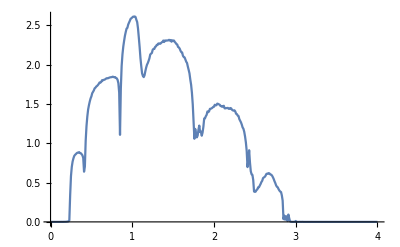

```mathematica
ListPlot[%111,Joined->True]
```

```mathematica
final9=(m+n+o+p+q+r)/6
```

{{0.,0.000208653},{0.01,0.0000631577},{0.02,0.0000725259},{0.03,0.0000242585},{0.04,0.0000345876},{0.05,0.0000399034},{0.06,0.0000547211},{0.07,0.0000743632},{0.08,0.000121946},{0.09,0.000317972},{0.1,0.000185894},{0.11,0.000235673},{0.12,0.000883154},{0.13,0.00035588},{0.14,0.000463674},{0.15,0.000629442},{0.16,0.000761753},{0.17,0.000996507},{0.18,0.00151011},{0.19,0.00192218},{0.2,0.00261956},{0.21,0.00396995},{0.22,0.0069574},{0.23,0.0171571},{0.24,0.348546},{0.25,0.600348},{0.26,0.721255},{0.27,0.788396},{0.28,0.831307},{0.29,0.859857},{0.3,0.878189},{0.31,0.886164},{0.32,0.89834},{0.33,0.904427},{0.34,0.905952},{0.35,0.914445},{0.36,0.903425},{0.37,0.89675},{0.38,0.883114},{0.39,0.875773},{0.4,0.835715},{0.41,0.668036},{0.42,0.720716},{0.43,1.11874},{0.44,1.33074},{0.45,1.43477},{0.46,1.52795},{0.47,1.58767},{0.48,1.62833},{0.49,1.6644},{0.5,1.68233},{0.51,1.7231},{0.52,1.71835},{0.53,1.7252},{0.54,1.74844},{0.55,1.75575},{0.56,1.77207},{0.57,1.7694},{0.58,1.77854},{0.59,1.79209},{0.6,1.79123},{0.61,1.7882},{0.62,1.80052},{0.63,1.78279},{0.64,1.79904},{0.65,1.80841},{0.66,1.80616},{0.67,1.81172},{0.68,1.81034},{0.69,1.80865},{0.7,1.81269},{0.71,1.81588},{0.72,1.82651},{0.73,1.82044},{0.74,1.82284},{0.75,1.8265},{0.76,1.81904},{0.77,1.82977},{0.78,1.82638},{0.79,1.8312},{0.8,1.83612},{0.81,1.82282},{0.82,1.80748},{0.83,1.77298},{0.84,1.64976},{0.85,1.16911},{0.86,1.85167},{0.87,2.13119},{0.88,2.26264},{0.89,2.37778},{0.9,2.45254},{0.91,2.49722},{0.92,2.54609},{0.93,2.56953},{0.94,2.59147},{0.95,2.64692},{0.96,2.63727},{0.97,2.65996},{0.98,2.69419},{0.99,2.69434},{1.,2.68342},{1.01,2.72181},{1.02,2.71396},{1.03,2.70949},{1.04,2.67608},{1.05,2.65292},{1.06,2.57363},{1.07,2.44965},{1.08,2.30705},{1.09,2.12989},{1.1,1.97709},{1.11,1.87148},{1.12,1.84137},{1.13,1.84052},{1.14,1.9008},{1.15,1.95892},{1.16,2.02199},{1.17,2.07708},{1.18,2.13963},{1.19,2.1738},{1.2,2.20339},{1.21,2.24},{1.22,2.26162},{1.23,2.26709},{1.24,2.29388},{1.25,2.31135},{1.26,2.33721},{1.27,2.34115},{1.28,2.34032},{1.29,2.37683},{1.3,2.35027},{1.31,2.36977},{1.32,2.36025},{1.33,2.37798},{1.34,2.36315},{1.35,2.37225},{1.36,2.39157},{1.37,2.38817},{1.38,2.37999},{1.39,2.38204},{1.4,2.39797},{1.41,2.37871},{1.42,2.37832},{1.43,2.38264},{1.44,2.38303},{1.45,2.3734},{1.46,2.38082},{1.47,2.37739},{1.48,2.37387},{1.49,2.38043},{1.5,2.36532},{1.51,2.36818},{1.52,2.37522},{1.53,2.36903},{1.54,2.35907},{1.55,2.3446},{1.56,2.34104},{1.57,2.32412},{1.58,2.32226},{1.59,2.32392},{1.6,2.29567},{1.61,2.26949},{1.62,2.25797},{1.63,2.23989},{1.64,2.19615},{1.65,2.18692},{1.66,2.17105},{1.67,2.13111},{1.68,2.06878},{1.69,2.06146},{1.7,1.96611},{1.71,1.9044},{1.72,1.829},{1.73,1.70493},{1.74,1.54255},{1.75,1.2992},{1.76,1.00275},{1.77,1.43755},{1.78,1.19195},{1.79,1.04742},{1.8,1.19698},{1.81,1.3179},{1.82,1.24717},{1.83,1.14617},{1.84,1.18402},{1.85,1.17782},{1.86,1.29297},{1.87,1.38686},{1.88,1.39202},{1.89,1.44933},{1.9,1.46761},{1.91,1.47446},{1.92,1.4965},{1.93,1.52028},{1.94,1.54504},{1.95,1.54798},{1.96,1.55664},{1.97,1.58322},{1.98,1.5765},{1.99,1.58497},{2.,1.58516},{2.01,1.58121},{2.02,1.59765},{2.03,1.59789},{2.04,1.58167},{2.05,1.59476},{2.06,1.59315},{2.07,1.59243},{2.08,1.57006},{2.09,1.57063},{2.1,1.56782},{2.11,1.56053},{2.12,1.54955},{2.13,1.54446},{2.14,1.55493},{2.15,1.55694},{2.16,1.55429},{2.17,1.53986},{2.18,1.53401},{2.19,1.53821},{2.2,1.54166},{2.21,1.53281},{2.22,1.53068},{2.23,1.50485},{2.24,1.49841},{2.25,1.48846},{2.26,1.47132},{2.27,1.44782},{2.28,1.43921},{2.29,1.42888},{2.3,1.38888},{2.31,1.37989},{2.32,1.34256},{2.33,1.31597},{2.34,1.27622},{2.35,1.23173},{2.36,1.19565},{2.37,1.12878},{2.38,1.08844},{2.39,0.977257},{2.4,0.848047},{2.41,0.674754},{2.42,0.702128},{2.43,0.716657},{2.44,0.707657},{2.45,0.486128},{2.46,0.63698},{2.47,0.601573},{2.48,0.448966},{2.49,0.50238},{2.5,0.481866},{2.51,0.518143},{2.52,0.546692},{2.53,0.593116},{2.54,0.627479},{2.55,0.671811},{2.56,0.683},{2.57,0.701534},{2.58,0.728131},{2.59,0.7463},{2.6,0.750596},{2.61,0.762121},{2.62,0.750077},{2.63,0.755646},{2.64,0.752901},{2.65,0.760128},{2.66,0.762305},{2.67,0.742894},{2.68,0.734075},{2.69,0.721575},{2.7,0.714287},{2.71,0.704299},{2.72,0.685384},{2.73,0.672762},{2.74,0.661574},{2.75,0.643888},{2.76,0.624705},{2.77,0.615418},{2.78,0.586516},{2.79,0.587196},{2.8,0.565268},{2.81,0.555193},{2.82,0.529836},{2.83,0.477566},{2.84,0.382002},{2.85,0.024979},{2.86,0.0154026},{2.87,0.0514415},{2.88,0.0141051},{2.89,0.00566164},{2.9,0.0638648},{2.91,0.00327703},{2.92,0.0013461},{2.93,0.0006665},{2.94,0.000195078},{2.95,0.00219581},{2.96,0.0185829},{2.97,0.0000499379},{2.98,0.00030829},{2.99,0.00763365},{3.,0.000654838},{3.01,0.0242019},{3.02,0.0000478644},{3.03,0.0000732373},{3.04,0.0000239365},{3.05,0.0000138303},{3.06,0.000286921},{3.07,0.0000356815},{3.08,0.0000424408},{3.09,9.79674×10^-6},{3.1,0.000167949},{3.11,7.18289×10^-6},{3.12,0.000113547},{3.13,0.0000187307},{3.14,9.42031×10^-6},{3.15,0.0000114778},{3.16,0.000122211},{3.17,2.28112×10^-6},{3.18,0.0000847806},{3.19,0.0000907172},{3.2,4.21117×10^-6},{3.21,0.0000788408},{3.22,0.0000431308},{3.23,0.0000344445},{3.24,0.0000582193},{3.25,0.0000275377},{3.26,5.89737×10^-6},{3.27,0.0000509871},{3.28,0.0000410405},{3.29,0.0000216861},{3.3,0.0000336981},{3.31,0.0000175837},{3.32,1.21021×10^-6},{3.33,1.20891×10^-6},{3.34,1.36286×10^-6},{3.35,0.0000231421},{3.36,0.0000246691},{3.37,0.000012323},{3.38,0.0000105611},{3.39,0.0000112198},{3.4,1.11381×10^-6},{3.41,1.06768×10^-6},{3.42,1.01102×10^-6},{3.43,8.14145×10^-6},{3.44,9.10011×10^-7},{3.45,6.50891×10^-6},{3.46,7.49214×10^-7},{3.47,6.13037×10^-7},{3.48,6.99037×10^-7},{3.49,5.9926×10^-7},{3.5,5.52133×10^-7},{3.51,7.55763×10^-7},{3.52,4.83997×10^-6},{3.53,6.00748×10^-7},{3.54,4.18305×10^-6},{3.55,3.94669×10^-6},{3.56,5.03279×10^-7},{3.57,5.94×10^-6},{3.58,4.75574×10^-7},{3.59,3.03418×10^-6},{3.6,4.4628×10^-7},{3.61,3.9002×10^-7},{3.62,4.82719×10^-6},{3.63,3.71594×10^-7},{3.64,4.0015×10^-7},{3.65,3.85187×10^-7},{3.66,3.74724×10^-7},{3.67,3.55554×10^-6},{3.68,1.94669×10^-6},{3.69,3.16082×10^-7},{3.7,3.25131×10^-7},{3.71,2.9699×10^-7},{3.72,2.83178×10^-6},{3.73,1.54555×10^-6},{3.74,2.7539×10^-7},{3.75,1.46278×10^-6},{3.76,2.62244×10^-7},{3.77,2.56236×10^-7},{3.78,1.28279×10^-6},{3.79,2.44177×10^-7},{3.8,1.14499×10^-6},{3.81,1.13388×10^-6},{3.82,2.2945×10^-7},{3.83,9.97878×10^-7},{3.84,2.19834×10^-7},{3.85,2.20448×10^-7},{3.86,2.17287×10^-7},{3.87,2.17037×10^-7},{3.88,8.33092×10^-7},{3.89,1.39331×10^-6},{3.9,2.01844×10^-7},{3.91,7.48068×10^-7},{3.92,1.85763×10^-7},{3.93,1.85288×10^-7},{3.94,1.80588×10^-7},{3.95,1.75773×10^-7},{3.96,1.73042×10^-7},{3.97,1.69081×10^-7},{3.98,1.66378×10^-7},{3.99,1.65121×10^-7},{4.,1.61681×10^-7}}

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis29.csv",final9]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis29.csv

```mathematica
final8=(m+n+o+p+q+r)/6
```

{{0.,0.0000382738},{0.01,0.0000277368},{0.02,0.0000254231},{0.03,0.0000338339},{0.04,0.0000341069},{0.05,0.0000360465},{0.06,0.000045662},{0.07,0.000138171},{0.08,0.000119714},{0.09,0.000178589},{0.1,0.000126018},{0.11,0.000176004},{0.12,0.000209025},{0.13,0.00025995},{0.14,0.000526871},{0.15,0.000446098},{0.16,0.000565515},{0.17,0.000811426},{0.18,0.00117361},{0.19,0.00143092},{0.2,0.00211727},{0.21,0.00355666},{0.22,0.00755867},{0.23,0.0175824},{0.24,0.431086},{0.25,0.668202},{0.26,0.765365},{0.27,0.820997},{0.28,0.84832},{0.29,0.873003},{0.3,0.886055},{0.31,0.90441},{0.32,0.91093},{0.33,0.904003},{0.34,0.91054},{0.35,0.910606},{0.36,0.912551},{0.37,0.912878},{0.38,0.911727},{0.39,0.885808},{0.4,0.855653},{0.41,0.710284},{0.42,0.897348},{0.43,1.29499},{0.44,1.47052},{0.45,1.5688},{0.46,1.64129},{0.47,1.67765},{0.48,1.71558},{0.49,1.73858},{0.5,1.75857},{0.51,1.78293},{0.52,1.79065},{0.53,1.8043},{0.54,1.81604},{0.55,1.82817},{0.56,1.83377},{0.57,1.84819},{0.58,1.84287},{0.59,1.8587},{0.6,1.8646},{0.61,1.86233},{0.62,1.86753},{0.63,1.87067},{0.64,1.86689},{0.65,1.87512},{0.66,1.87803},{0.67,1.87186},{0.68,1.88397},{0.69,1.88766},{0.7,1.88759},{0.71,1.8861},{0.72,1.88826},{0.73,1.88628},{0.74,1.89317},{0.75,1.89007},{0.76,1.89299},{0.77,1.87489},{0.78,1.88989},{0.79,1.88677},{0.8,1.88118},{0.81,1.88189},{0.82,1.85701},{0.83,1.83006},{0.84,1.71522},{0.85,1.32968},{0.86,1.91474},{0.87,2.18395},{0.88,2.31325},{0.89,2.42404},{0.9,2.48766},{0.91,2.5506},{0.92,2.592},{0.93,2.62594},{0.94,2.65376},{0.95,2.67742},{0.96,2.70167},{0.97,2.71441},{0.98,2.727},{0.99,2.74314},{1.,2.74974},{1.01,2.75842},{1.02,2.7478},{1.03,2.73757},{1.04,2.70561},{1.05,2.63683},{1.06,2.53007},{1.07,2.36991},{1.08,2.1527},{1.09,1.9459},{1.1,1.86061},{1.11,1.80534},{1.12,1.86007},{1.13,1.94418},{1.14,2.01791},{1.15,2.11264},{1.16,2.18029},{1.17,2.23768},{1.18,2.28304},{1.19,2.3233},{1.2,2.35837},{1.21,2.38915},{1.22,2.40485},{1.23,2.41743},{1.24,2.43481},{1.25,2.45984},{1.26,2.44102},{1.27,2.45785},{1.28,2.48205},{1.29,2.49253},{1.3,2.48594},{1.31,2.47363},{1.32,2.49045},{1.33,2.49846},{1.34,2.50525},{1.35,2.49246},{1.36,2.50069},{1.37,2.50115},{1.38,2.50978},{1.39,2.50144},{1.4,2.52334},{1.41,2.50941},{1.42,2.50861},{1.43,2.52194},{1.44,2.5124},{1.45,2.51715},{1.46,2.53121},{1.47,2.5313},{1.48,2.50869},{1.49,2.51657},{1.5,2.53127},{1.51,2.51564},{1.52,2.50624},{1.53,2.50956},{1.54,2.5051},{1.55,2.5109},{1.56,2.48226},{1.57,2.48692},{1.58,2.46804},{1.59,2.4407},{1.6,2.44311},{1.61,2.43111},{1.62,2.41275},{1.63,2.38599},{1.64,2.37887},{1.65,2.35398},{1.66,2.30776},{1.67,2.28977},{1.68,2.23061},{1.69,2.2032},{1.7,2.15138},{1.71,2.08254},{1.72,2.00388},{1.73,1.87954},{1.74,1.75717},{1.75,1.51726},{1.76,1.12959},{1.77,1.2215},{1.78,1.34245},{1.79,1.14009},{1.8,1.23607},{1.81,1.28321},{1.82,1.21248},{1.83,1.33954},{1.84,1.36905},{1.85,1.43855},{1.86,1.50084},{1.87,1.54194},{1.88,1.5533},{1.89,1.6182},{1.9,1.65168},{1.91,1.62394},{1.92,1.63688},{1.93,1.68194},{1.94,1.68522},{1.95,1.69307},{1.96,1.70635},{1.97,1.71495},{1.98,1.70389},{1.99,1.71736},{2.,1.72794},{2.01,1.72041},{2.02,1.72},{2.03,1.72467},{2.04,1.7324},{2.05,1.7373},{2.06,1.73598},{2.07,1.71236},{2.08,1.73673},{2.09,1.72851},{2.1,1.70696},{2.11,1.71872},{2.12,1.70108},{2.13,1.70024},{2.14,1.70199},{2.15,1.67404},{2.16,1.68096},{2.17,1.67053},{2.18,1.66582},{2.19,1.65269},{2.2,1.64714},{2.21,1.64397},{2.22,1.62814},{2.23,1.62348},{2.24,1.6172},{2.25,1.61402},{2.26,1.58927},{2.27,1.59334},{2.28,1.57733},{2.29,1.55495},{2.3,1.5481},{2.31,1.51583},{2.32,1.50105},{2.33,1.49095},{2.34,1.44328},{2.35,1.41446},{2.36,1.38769},{2.37,1.32571},{2.38,1.26637},{2.39,1.18816},{2.4,1.04166},{2.41,0.788256},{2.42,0.773623},{2.43,0.598322},{2.44,0.603225},{2.45,0.704726},{2.46,0.701323},{2.47,0.610924},{2.48,0.613032},{2.49,0.637287},{2.5,0.69043},{2.51,0.674271},{2.52,0.703787},{2.53,0.72147},{2.54,0.751952},{2.55,0.741643},{2.56,0.757896},{2.57,0.773344},{2.58,0.77171},{2.59,0.77287},{2.6,0.788631},{2.61,0.781273},{2.62,0.800849},{2.63,0.792012},{2.64,0.801727},{2.65,0.791974},{2.66,0.799189},{2.67,0.789197},{2.68,0.783776},{2.69,0.768751},{2.7,0.753402},{2.71,0.731584},{2.72,0.710106},{2.73,0.696297},{2.74,0.680423},{2.75,0.666048},{2.76,0.63389},{2.77,0.632267},{2.78,0.60581},{2.79,0.592196},{2.8,0.58357},{2.81,0.570566},{2.82,0.546004},{2.83,0.510838},{2.84,0.401226},{2.85,0.121873},{2.86,0.0334808},{2.87,0.0202718},{2.88,0.0204801},{2.89,0.063892},{2.9,0.0721453},{2.91,0.0073894},{2.92,0.0633107},{2.93,0.00378366},{2.94,0.000186434},{2.95,0.000364505},{2.96,0.00125151},{2.97,0.000299944},{2.98,0.000659548},{2.99,0.0000354235},{3.,0.00117929},{3.01,0.0000368501},{3.02,0.000796235},{3.03,0.0000136018},{3.04,0.0000482201},{3.05,0.000214708},{3.06,0.0000293024},{3.07,0.0006009},{3.08,6.72622×10^-6},{3.09,0.000201559},{3.1,0.0000199276},{3.11,0.000208888},{3.12,0.0000128634},{3.13,6.9878×10^-6},{3.14,6.49621×10^-6},{3.15,0.0000952403},{3.16,0.0000613703},{3.17,2.62391×10^-6},{3.18,0.0000412475},{3.19,0.0000602399},{3.2,2.51639×10^-6},{3.21,4.05415×10^-6},{3.22,1.82053×10^-6},{3.23,2.67386×10^-6},{3.24,0.0000209096},{3.25,0.0000407009},{3.26,2.43626×10^-6},{3.27,0.0000163723},{3.28,1.77574×10^-6},{3.29,0.0000285059},{3.3,1.73094×10^-6},{3.31,0.0000118233},{3.32,0.0000108429},{3.33,0.0000113872},{3.34,9.99727×10^-6},{3.35,0.0000158301},{3.36,1.11962×10^-6},{3.37,0.0000138465},{3.38,8.79663×10^-7},{3.39,7.00831×10^-6},{3.4,7.64774×10^-7},{3.41,6.2873×10^-6},{3.42,8.24925×10^-7},{3.43,6.99004×10^-7},{3.44,5.43963×10^-6},{3.45,9.04538×10^-6},{3.46,4.54162×10^-6},{3.47,7.40292×10^-6},{3.48,4.38412×10^-6},{3.49,3.94031×10^-6},{3.5,6.92693×10^-7},{3.51,6.29161×10^-6},{3.52,5.51774×10^-7},{3.53,4.97231×10^-7},{3.54,5.01276×10^-6},{3.55,2.88883×10^-6},{3.56,4.98528×10^-7},{3.57,4.3798×10^-7},{3.58,4.27595×10^-6},{3.59,4.47572×10^-7},{3.6,3.91395×10^-7},{3.61,2.11852×10^-6},{3.62,3.3132×10^-6},{3.63,3.1879×10^-6},{3.64,3.81092×10^-7},{3.65,1.71609×10^-6},{3.66,3.38042×10^-7},{3.67,2.71956×10^-6},{3.68,3.1951×10^-7},{3.69,3.29346×10^-7},{3.7,3.3137×10^-7},{3.71,3.07528×10^-7},{3.72,1.23635×10^-6},{3.73,3.03751×10^-7},{3.74,2.74046×10^-7},{3.75,2.68061×10^-7},{3.76,1.79932×10^-6},{3.77,2.55971×10^-7},{3.78,9.69758×10^-7},{3.79,2.5248×10^-7},{3.8,2.43747×10^-7},{3.81,1.45448×10^-6},{3.82,1.37374×10^-6},{3.83,7.94993×10^-7},{3.84,2.19447×10^-7},{3.85,2.14696×10^-7},{3.86,2.11573×10^-7},{3.87,2.06434×10^-7},{3.88,6.52956×10^-7},{3.89,1.99608×10^-7},{3.9,1.01276×10^-6},{3.91,1.90272×10^-7},{3.92,5.75961×10^-7},{3.93,1.82749×10^-7},{3.94,5.30781×10^-7},{3.95,1.75337×10^-7},{3.96,1.72206×10^-7},{3.97,1.67782×10^-7},{3.98,1.64406×10^-7},{3.99,1.62682×10^-7},{4.,4.37628×10^-7}}

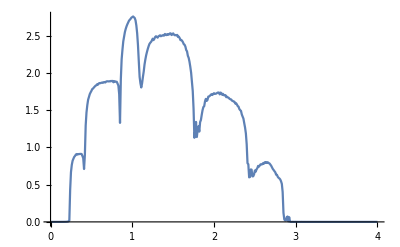

```mathematica
ListPlot[final8,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis28.csv",final8]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis28.csv

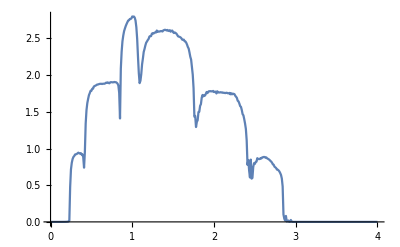

```mathematica
ListPlot[final7,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis24.csv",final4]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/epis24.csv

```mathematica
final6=(m+n+o+p+q+r)/6
```

{{0.,0.000037527},{0.01,0.0000281805},{0.02,0.0000250461},{0.03,0.0000313754},{0.04,0.000031881},{0.05,0.0000364026},{0.06,0.0000427315},{0.07,0.0000504567},{0.08,0.0000644352},{0.09,0.000115155},{0.1,0.000105637},{0.11,0.000131905},{0.12,0.000199393},{0.13,0.000213994},{0.14,0.000271307},{0.15,0.00036131},{0.16,0.000638296},{0.17,0.000627274},{0.18,0.00107799},{0.19,0.00123987},{0.2,0.00187285},{0.21,0.00312604},{0.22,0.00652724},{0.23,0.0163121},{0.24,0.479692},{0.25,0.721867},{0.26,0.809542},{0.27,0.856068},{0.28,0.890288},{0.29,0.904771},{0.3,0.917954},{0.31,0.930497},{0.32,0.934381},{0.33,0.935266},{0.34,0.937972},{0.35,0.946077},{0.36,0.9445},{0.37,0.940153},{0.38,0.93729},{0.39,0.927255},{0.4,0.902958},{0.41,0.799492},{0.42,1.19374},{0.43,1.5279},{0.44,1.65628},{0.45,1.74022},{0.46,1.77418},{0.47,1.80282},{0.48,1.82321},{0.49,1.8341},{0.5,1.84674},{0.51,1.86185},{0.52,1.87519},{0.53,1.878},{0.54,1.8935},{0.55,1.89854},{0.56,1.89412},{0.57,1.90454},{0.58,1.90305},{0.59,1.90424},{0.6,1.90758},{0.61,1.91362},{0.62,1.91039},{0.63,1.91299},{0.64,1.91935},{0.65,1.91165},{0.66,1.91823},{0.67,1.91629},{0.68,1.92401},{0.69,1.9175},{0.7,1.9147},{0.71,1.91901},{0.72,1.92228},{0.73,1.92753},{0.74,1.92526},{0.75,1.92544},{0.76,1.92493},{0.77,1.92639},{0.78,1.92278},{0.79,1.92297},{0.8,1.91935},{0.81,1.9166},{0.82,1.90149},{0.83,1.87431},{0.84,1.79121},{0.85,1.4524},{0.86,2.12637},{0.87,2.35961},{0.88,2.48806},{0.89,2.57286},{0.9,2.6201},{0.91,2.66404},{0.92,2.68831},{0.93,2.72601},{0.94,2.7521},{0.95,2.74543},{0.96,2.77729},{0.97,2.77217},{0.98,2.7879},{0.99,2.82098},{1.,2.81471},{1.01,2.82455},{1.02,2.81381},{1.03,2.77868},{1.04,2.74131},{1.05,2.61427},{1.06,2.37084},{1.07,2.09476},{1.08,1.97662},{1.09,2.1159},{1.1,2.25361},{1.11,2.3465},{1.12,2.42442},{1.13,2.47997},{1.14,2.50135},{1.15,2.53449},{1.16,2.553},{1.17,2.57068},{1.18,2.5966},{1.19,2.60697},{1.2,2.62761},{1.21,2.64314},{1.22,2.64164},{1.23,2.64993},{1.24,2.66194},{1.25,2.67281},{1.26,2.68451},{1.27,2.6679},{1.28,2.67532},{1.29,2.69044},{1.3,2.69239},{1.31,2.68926},{1.32,2.6887},{1.33,2.69363},{1.34,2.68386},{1.35,2.69407},{1.36,2.69136},{1.37,2.68166},{1.38,2.68463},{1.39,2.68731},{1.4,2.69005},{1.41,2.69813},{1.42,2.70238},{1.43,2.69138},{1.44,2.70218},{1.45,2.69267},{1.46,2.69682},{1.47,2.69089},{1.48,2.6898},{1.49,2.68471},{1.5,2.68688},{1.51,2.65884},{1.52,2.66663},{1.53,2.65818},{1.54,2.65101},{1.55,2.64398},{1.56,2.62914},{1.57,2.62482},{1.58,2.61626},{1.59,2.59731},{1.6,2.60081},{1.61,2.59244},{1.62,2.58404},{1.63,2.5526},{1.64,2.54381},{1.65,2.54191},{1.66,2.5078},{1.67,2.49169},{1.68,2.47803},{1.69,2.43204},{1.7,2.39583},{1.71,2.34062},{1.72,2.26713},{1.73,2.18206},{1.74,2.01873},{1.75,1.8097},{1.76,1.28128},{1.77,1.43717},{1.78,1.24183},{1.79,1.19607},{1.8,1.33746},{1.81,1.5287},{1.82,1.64529},{1.83,1.6968},{1.84,1.73241},{1.85,1.75576},{1.86,1.8159},{1.87,1.81376},{1.88,1.81118},{1.89,1.83463},{1.9,1.82956},{1.91,1.81947},{1.92,1.85108},{1.93,1.85227},{1.94,1.85775},{1.95,1.85718},{1.96,1.85814},{1.97,1.85222},{1.98,1.85487},{1.99,1.85132},{2.,1.85717},{2.01,1.85507},{2.02,1.84964},{2.03,1.85003},{2.04,1.84504},{2.05,1.845},{2.06,1.84152},{2.07,1.83805},{2.08,1.83963},{2.09,1.81451},{2.1,1.83087},{2.11,1.82576},{2.12,1.82328},{2.13,1.82285},{2.14,1.82105},{2.15,1.82082},{2.16,1.81791},{2.17,1.81131},{2.18,1.8191},{2.19,1.80884},{2.2,1.81018},{2.21,1.81415},{2.22,1.80804},{2.23,1.81079},{2.24,1.80307},{2.25,1.78895},{2.26,1.78622},{2.27,1.78727},{2.28,1.78126},{2.29,1.74761},{2.3,1.75272},{2.31,1.73041},{2.32,1.70311},{2.33,1.68191},{2.34,1.67028},{2.35,1.62761},{2.36,1.60828},{2.37,1.5746},{2.38,1.52784},{2.39,1.44966},{2.4,1.32891},{2.41,0.978477},{2.42,1.0509},{2.43,0.839125},{2.44,0.882505},{2.45,0.704649},{2.46,0.766642},{2.47,0.880928},{2.48,0.891968},{2.49,0.864816},{2.5,0.880817},{2.51,0.883593},{2.52,0.894742},{2.53,0.897082},{2.54,0.894928},{2.55,0.898227},{2.56,0.899331},{2.57,0.899942},{2.58,0.890069},{2.59,0.892441},{2.6,0.900147},{2.61,0.901022},{2.62,0.89767},{2.63,0.902051},{2.64,0.896379},{2.65,0.897618},{2.66,0.897276},{2.67,0.89366},{2.68,0.887267},{2.69,0.873449},{2.7,0.866807},{2.71,0.859869},{2.72,0.844174},{2.73,0.829085},{2.74,0.814805},{2.75,0.797413},{2.76,0.778895},{2.77,0.767378},{2.78,0.751378},{2.79,0.741987},{2.8,0.723253},{2.81,0.707356},{2.82,0.689907},{2.83,0.635254},{2.84,0.525372},{2.85,0.0699679},{2.86,0.00843535},{2.87,0.0195467},{2.88,0.00632218},{2.89,0.00081731},{2.9,0.00624271},{2.91,0.000312855},{2.92,0.000140873},{2.93,0.0124741},{2.94,0.00184731},{2.95,0.00060738},{2.96,0.0000596318},{2.97,0.000114151},{2.98,0.0000186905},{2.99,0.0000321123},{3.,0.000160491},{3.01,0.0000103784},{3.02,0.0000123641},{3.03,0.000224432},{3.04,6.44059×10^-6},{3.05,0.0000104018},{3.06,6.55782×10^-6},{3.07,0.0000100436},{3.08,0.0000735117},{3.09,4.26017×10^-6},{3.1,5.53142×10^-6},{3.11,0.0000402887},{3.12,0.000048776},{3.13,0.0000316872},{3.14,4.37156×10^-6},{3.15,2.42003×10^-6},{3.16,0.0000185672},{3.17,2.53119×10^-6},{3.18,4.05664×10^-6},{3.19,1.90559×10^-6},{3.2,1.98935×10^-6},{3.21,1.79401×10^-6},{3.22,2.0051×10^-6},{3.23,0.0000110509},{3.24,9.51637×10^-6},{3.25,1.3985×10^-6},{3.26,1.44686×10^-6},{3.27,1.31108×10^-6},{3.28,1.78316×10^-6},{3.29,1.36614×10^-6},{3.3,6.30838×10^-6},{3.31,1.08377×10^-6},{3.32,5.1978×10^-6},{3.33,5.37257×10^-6},{3.34,7.72044×10^-6},{3.35,9.40913×10^-7},{3.36,4.52431×10^-6},{3.37,3.80689×10^-6},{3.38,9.9022×10^-7},{3.39,7.87743×10^-7},{3.4,5.31714×10^-6},{3.41,7.34616×10^-7},{3.42,4.87933×10^-6},{3.43,2.79101×10^-6},{3.44,7.04818×10^-7},{3.45,6.24209×10^-7},{3.46,6.36407×10^-7},{3.47,6.30572×10^-7},{3.48,3.56062×10^-6},{3.49,1.95042×10^-6},{3.5,3.19501×10^-6},{3.51,1.76419×10^-6},{3.52,5.01194×10^-7},{3.53,1.64522×10^-6},{3.54,2.48805×10^-6},{3.55,1.49829×10^-6},{3.56,1.4449×10^-6},{3.57,1.35643×10^-6},{3.58,2.0487×10^-6},{3.59,4.19899×10^-7},{3.6,3.92833×10^-7},{3.61,3.8989×10^-7},{3.62,1.11783×10^-6},{3.63,1.64064×10^-6},{3.64,1.55631×10^-6},{3.65,3.44715×10^-7},{3.66,1.44736×10^-6},{3.67,8.80085×10^-7},{3.68,8.64699×10^-7},{3.69,8.1197×10^-7},{3.7,3.05591×10^-7},{3.71,2.99099×10^-7},{3.72,2.91447×10^-7},{3.73,2.82473×10^-7},{3.74,2.76623×10^-7},{3.75,6.5654×10^-7},{3.76,2.64726×10^-7},{3.77,2.55641×10^-7},{3.78,8.92457×10^-7},{3.79,2.44384×10^-7},{3.8,5.38871×10^-7},{3.81,5.13608×10^-7},{3.82,2.31128×10^-7},{3.83,4.85037×10^-7},{3.84,2.21543×10^-7},{3.85,4.48947×10^-7},{3.86,2.11826×10^-7},{3.87,2.05202×10^-7},{3.88,2.03566×10^-7},{3.89,1.9921×10^-7},{3.9,3.86259×10^-7},{3.91,1.91398×10^-7},{3.92,1.8757×10^-7},{3.93,3.55384×10^-7},{3.94,1.78979×10^-7},{3.95,1.7507×10^-7},{3.96,4.6425×10^-7},{3.97,4.47721×10^-7},{3.98,1.6645×10^-7},{3.99,2.92317×10^-7},{4.,2.86148×10^-7}}

```mathematica
Export["epis6.csv",final6]
```

epis6.csv

```mathematica
Import["epis6.csv"]
```

{{0.,0.000037527},{0.01,0.0000281805},{0.02,0.0000250461},{0.03,0.0000313754},{0.04,0.000031881},{0.05,0.0000364026},{0.06,0.0000427315},{0.07,0.0000504567},{0.08,0.0000644352},{0.09,0.000115155},{0.1,0.000105637},{0.11,0.000131905},{0.12,0.000199393},{0.13,0.000213994},{0.14,0.000271307},{0.15,0.00036131},{0.16,0.000638296},{0.17,0.000627274},{0.18,0.00107799},{0.19,0.00123987},{0.2,0.00187285},{0.21,0.00312604},{0.22,0.00652724},{0.23,0.0163121},{0.24,0.479692},{0.25,0.721867},{0.26,0.809542},{0.27,0.856068},{0.28,0.890288},{0.29,0.904771},{0.3,0.917954},{0.31,0.930497},{0.32,0.934381},{0.33,0.935266},{0.34,0.937972},{0.35,0.946077},{0.36,0.9445},{0.37,0.940153},{0.38,0.93729},{0.39,0.927255},{0.4,0.902958},{0.41,0.799492},{0.42,1.19374},{0.43,1.5279},{0.44,1.65628},{0.45,1.74022},{0.46,1.77418},{0.47,1.80282},{0.48,1.82321},{0.49,1.8341},{0.5,1.84674},{0.51,1.86185},{0.52,1.87519},{0.53,1.878},{0.54,1.8935},{0.55,1.89854},{0.56,1.89412},{0.57,1.90454},{0.58,1.90305},{0.59,1.90424},{0.6,1.90758},{0.61,1.91362},{0.62,1.91039},{0.63,1.91299},{0.64,1.91935},{0.65,1.91165},{0.66,1.91823},{0.67,1.91629},{0.68,1.92401},{0.69,1.9175},{0.7,1.9147},{0.71,1.91901},{0.72,1.92228},{0.73,1.92753},{0.74,1.92526},{0.75,1.92544},{0.76,1.92493},{0.77,1.92639},{0.78,1.92278},{0.79,1.92297},{0.8,1.91935},{0.81,1.9166},{0.82,1.90149},{0.83,1.87431},{0.84,1.79121},{0.85,1.4524},{0.86,2.12637},{0.87,2.35961},{0.88,2.48806},{0.89,2.57286},{0.9,2.6201},{0.91,2.66404},{0.92,2.68831},{0.93,2.72601},{0.94,2.7521},{0.95,2.74543},{0.96,2.77729},{0.97,2.77217},{0.98,2.7879},{0.99,2.82098},{1.,2.81471},{1.01,2.82455},{1.02,2.81381},{1.03,2.77868},{1.04,2.74131},{1.05,2.61427},{1.06,2.37084},{1.07,2.09476},{1.08,1.97662},{1.09,2.1159},{1.1,2.25361},{1.11,2.3465},{1.12,2.42442},{1.13,2.47997},{1.14,2.50135},{1.15,2.53449},{1.16,2.553},{1.17,2.57068},{1.18,2.5966},{1.19,2.60697},{1.2,2.62761},{1.21,2.64314},{1.22,2.64164},{1.23,2.64993},{1.24,2.66194},{1.25,2.67281},{1.26,2.68451},{1.27,2.6679},{1.28,2.67532},{1.29,2.69044},{1.3,2.69239},{1.31,2.68926},{1.32,2.6887},{1.33,2.69363},{1.34,2.68386},{1.35,2.69407},{1.36,2.69136},{1.37,2.68166},{1.38,2.68463},{1.39,2.68731},{1.4,2.69005},{1.41,2.69813},{1.42,2.70238},{1.43,2.69138},{1.44,2.70218},{1.45,2.69267},{1.46,2.69682},{1.47,2.69089},{1.48,2.6898},{1.49,2.68471},{1.5,2.68688},{1.51,2.65884},{1.52,2.66663},{1.53,2.65818},{1.54,2.65101},{1.55,2.64398},{1.56,2.62914},{1.57,2.62482},{1.58,2.61626},{1.59,2.59731},{1.6,2.60081},{1.61,2.59244},{1.62,2.58404},{1.63,2.5526},{1.64,2.54381},{1.65,2.54191},{1.66,2.5078},{1.67,2.49169},{1.68,2.47803},{1.69,2.43204},{1.7,2.39583},{1.71,2.34062},{1.72,2.26713},{1.73,2.18206},{1.74,2.01873},{1.75,1.8097},{1.76,1.28128},{1.77,1.43717},{1.78,1.24183},{1.79,1.19607},{1.8,1.33746},{1.81,1.5287},{1.82,1.64529},{1.83,1.6968},{1.84,1.73241},{1.85,1.75576},{1.86,1.8159},{1.87,1.81376},{1.88,1.81118},{1.89,1.83463},{1.9,1.82956},{1.91,1.81947},{1.92,1.85108},{1.93,1.85227},{1.94,1.85775},{1.95,1.85718},{1.96,1.85814},{1.97,1.85222},{1.98,1.85487},{1.99,1.85132},{2.,1.85717},{2.01,1.85507},{2.02,1.84964},{2.03,1.85003},{2.04,1.84504},{2.05,1.845},{2.06,1.84152},{2.07,1.83805},{2.08,1.83963},{2.09,1.81451},{2.1,1.83087},{2.11,1.82576},{2.12,1.82328},{2.13,1.82285},{2.14,1.82105},{2.15,1.82082},{2.16,1.81791},{2.17,1.81131},{2.18,1.8191},{2.19,1.80884},{2.2,1.81018},{2.21,1.81415},{2.22,1.80804},{2.23,1.81079},{2.24,1.80307},{2.25,1.78895},{2.26,1.78622},{2.27,1.78727},{2.28,1.78126},{2.29,1.74761},{2.3,1.75272},{2.31,1.73041},{2.32,1.70311},{2.33,1.68191},{2.34,1.67028},{2.35,1.62761},{2.36,1.60828},{2.37,1.5746},{2.38,1.52784},{2.39,1.44966},{2.4,1.32891},{2.41,0.978477},{2.42,1.0509},{2.43,0.839125},{2.44,0.882505},{2.45,0.704649},{2.46,0.766642},{2.47,0.880928},{2.48,0.891968},{2.49,0.864816},{2.5,0.880817},{2.51,0.883593},{2.52,0.894742},{2.53,0.897082},{2.54,0.894928},{2.55,0.898227},{2.56,0.899331},{2.57,0.899942},{2.58,0.890069},{2.59,0.892441},{2.6,0.900147},{2.61,0.901022},{2.62,0.89767},{2.63,0.902051},{2.64,0.896379},{2.65,0.897618},{2.66,0.897276},{2.67,0.89366},{2.68,0.887267},{2.69,0.873449},{2.7,0.866807},{2.71,0.859869},{2.72,0.844174},{2.73,0.829085},{2.74,0.814805},{2.75,0.797413},{2.76,0.778895},{2.77,0.767378},{2.78,0.751378},{2.79,0.741987},{2.8,0.723253},{2.81,0.707356},{2.82,0.689907},{2.83,0.635254},{2.84,0.525372},{2.85,0.0699679},{2.86,0.00843535},{2.87,0.0195467},{2.88,0.00632218},{2.89,0.00081731},{2.9,0.00624271},{2.91,0.000312855},{2.92,0.000140873},{2.93,0.0124741},{2.94,0.00184731},{2.95,0.00060738},{2.96,0.0000596318},{2.97,0.000114151},{2.98,0.0000186905},{2.99,0.0000321123},{3.,0.000160491},{3.01,0.0000103784},{3.02,0.0000123641},{3.03,0.000224432},{3.04,6.44059×10^-6},{3.05,0.0000104018},{3.06,6.55782×10^-6},{3.07,0.0000100436},{3.08,0.0000735117},{3.09,4.26017×10^-6},{3.1,5.53142×10^-6},{3.11,0.0000402887},{3.12,0.000048776},{3.13,0.0000316872},{3.14,4.37156×10^-6},{3.15,2.42003×10^-6},{3.16,0.0000185672},{3.17,2.53119×10^-6},{3.18,4.05664×10^-6},{3.19,1.90559×10^-6},{3.2,1.98935×10^-6},{3.21,1.79401×10^-6},{3.22,2.0051×10^-6},{3.23,0.0000110509},{3.24,9.51637×10^-6},{3.25,1.3985×10^-6},{3.26,1.44686×10^-6},{3.27,1.31108×10^-6},{3.28,1.78316×10^-6},{3.29,1.36614×10^-6},{3.3,6.30838×10^-6},{3.31,1.08377×10^-6},{3.32,5.1978×10^-6},{3.33,5.37257×10^-6},{3.34,7.72044×10^-6},{3.35,9.40913×10^-7},{3.36,4.52431×10^-6},{3.37,3.80689×10^-6},{3.38,9.9022×10^-7},{3.39,7.87743×10^-7},{3.4,5.31714×10^-6},{3.41,7.34616×10^-7},{3.42,4.87933×10^-6},{3.43,2.79101×10^-6},{3.44,7.04818×10^-7},{3.45,6.24209×10^-7},{3.46,6.36407×10^-7},{3.47,6.30572×10^-7},{3.48,3.56062×10^-6},{3.49,1.95042×10^-6},{3.5,3.19501×10^-6},{3.51,1.76419×10^-6},{3.52,5.01194×10^-7},{3.53,1.64522×10^-6},{3.54,2.48805×10^-6},{3.55,1.49829×10^-6},{3.56,1.4449×10^-6},{3.57,1.35643×10^-6},{3.58,2.0487×10^-6},{3.59,4.19899×10^-7},{3.6,3.92833×10^-7},{3.61,3.8989×10^-7},{3.62,1.11783×10^-6},{3.63,1.64064×10^-6},{3.64,1.55631×10^-6},{3.65,3.44715×10^-7},{3.66,1.44736×10^-6},{3.67,8.80085×10^-7},{3.68,8.64699×10^-7},{3.69,8.1197×10^-7},{3.7,3.05591×10^-7},{3.71,2.99099×10^-7},{3.72,2.91447×10^-7},{3.73,2.82473×10^-7},{3.74,2.76623×10^-7},{3.75,6.5654×10^-7},{3.76,2.64726×10^-7},{3.77,2.55641×10^-7},{3.78,8.92457×10^-7},{3.79,2.44384×10^-7},{3.8,5.38871×10^-7},{3.81,5.13608×10^-7},{3.82,2.31128×10^-7},{3.83,4.85037×10^-7},{3.84,2.21543×10^-7},{3.85,4.48947×10^-7},{3.86,2.11826×10^-7},{3.87,2.05202×10^-7},{3.88,2.03566×10^-7},{3.89,1.9921×10^-7},{3.9,3.86259×10^-7},{3.91,1.91398×10^-7},{3.92,1.8757×10^-7},{3.93,3.55384×10^-7},{3.94,1.78979×10^-7},{3.95,1.7507×10^-7},{3.96,4.6425×10^-7},{3.97,4.47721×10^-7},{3.98,1.6645×10^-7},{3.99,2.92317×10^-7},{4.,2.86148×10^-7}}

```mathematica
Import["/home/shardulmukim/epis9.csv"]
```

Import::nffil: File /home/shardulmukim/epis9.csv not found during Import.

$Failed

```mathematica
Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis23.csv"]
```

{{0.,0.0000370643},{0.01,0.0000282895},{0.02,0.0000293106},{0.03,0.0000273288},{0.04,0.0000267431},{0.05,0.0000267669},{0.06,0.0000253294},{0.07,0.0000256482},{0.08,0.0000318207},{0.09,0.0000299755},{0.1,0.0000366993},{0.11,0.0000445405},{0.12,0.0000487852},{0.13,0.0000575433},{0.14,0.0000697739},{0.15,0.0000891734},{0.16,0.000133993},{0.17,0.000173101},{0.18,0.000194209},{0.19,0.000300347},{0.2,0.000463439},{0.21,0.000689166},{0.22,0.00148524},{0.23,0.00577196},{0.24,0.746024},{0.25,0.902635},{0.26,0.94371},{0.27,0.959711},{0.28,0.969538},{0.29,0.974494},{0.3,0.97712},{0.31,0.977934},{0.32,0.981632},{0.33,0.982471},{0.34,0.98255},{0.35,0.983312},{0.36,0.981395},{0.37,0.978812},{0.38,0.979118},{0.39,0.972682},{0.4,0.956292},{0.41,0.889503},{0.42,1.54279},{0.43,1.80414},{0.44,1.87337},{0.45,1.90215},{0.46,1.92476},{0.47,1.94022},{0.48,1.9478},{0.49,1.95157},{0.5,1.9552},{0.51,1.95933},{0.52,1.96206},{0.53,1.96237},{0.54,1.96742},{0.55,1.96841},{0.56,1.97151},{0.57,1.97216},{0.58,1.97387},{0.59,1.97317},{0.6,1.97317},{0.61,1.97257},{0.62,1.9752},{0.63,1.97406},{0.64,1.97467},{0.65,1.97577},{0.66,1.97556},{0.67,1.97346},{0.68,1.97544},{0.69,1.97424},{0.7,1.9748},{0.71,1.9758},{0.72,1.97589},{0.73,1.97442},{0.74,1.97569},{0.75,1.97502},{0.76,1.97455},{0.77,1.97379},{0.78,1.97406},{0.79,1.97479},{0.8,1.97434},{0.81,1.97154},{0.82,1.9666},{0.83,1.95575},{0.84,1.91132},{0.85,2.08868},{0.86,2.6878},{0.87,2.80308},{0.88,2.84779},{0.89,2.88004},{0.9,2.8963},{0.91,2.91236},{0.92,2.92389},{0.93,2.92696},{0.94,2.93999},{0.95,2.94321},{0.96,2.95153},{0.97,2.95612},{0.98,2.95737},{0.99,2.96346},{1.,2.96128},{1.01,2.96078},{1.02,2.93856},{1.03,2.74527},{1.04,2.23443},{1.05,2.65113},{1.06,2.77411},{1.07,2.79902},{1.08,2.80363},{1.09,2.85295},{1.1,2.88906},{1.11,2.9033},{1.12,2.91045},{1.13,2.91253},{1.14,2.91259},{1.15,2.91934},{1.16,2.91546},{1.17,2.922},{1.18,2.92074},{1.19,2.92175},{1.2,2.92473},{1.21,2.92582},{1.22,2.92557},{1.23,2.92544},{1.24,2.92738},{1.25,2.92733},{1.26,2.926},{1.27,2.92386},{1.28,2.92314},{1.29,2.92594},{1.3,2.92553},{1.31,2.92603},{1.32,2.9261},{1.33,2.92909},{1.34,2.92565},{1.35,2.92991},{1.36,2.92953},{1.37,2.93111},{1.38,2.92889},{1.39,2.9303},{1.4,2.93226},{1.41,2.92898},{1.42,2.93346},{1.43,2.92822},{1.44,2.92925},{1.45,2.92504},{1.46,2.92557},{1.47,2.92106},{1.48,2.92242},{1.49,2.91634},{1.5,2.91683},{1.51,2.9113},{1.52,2.91391},{1.53,2.9103},{1.54,2.90504},{1.55,2.89946},{1.56,2.89925},{1.57,2.89279},{1.58,2.88395},{1.59,2.88933},{1.6,2.87748},{1.61,2.87905},{1.62,2.87462},{1.63,2.87684},{1.64,2.86075},{1.65,2.85535},{1.66,2.85527},{1.67,2.84013},{1.68,2.81895},{1.69,2.80747},{1.7,2.78061},{1.71,2.75521},{1.72,2.7331},{1.73,2.68459},{1.74,2.63232},{1.75,2.51859},{1.76,2.17287},{1.77,1.24952},{1.78,1.53338},{1.79,1.87979},{1.8,1.93676},{1.81,1.93129},{1.82,1.93011},{1.83,1.96107},{1.84,1.96239},{1.85,1.96592},{1.86,1.96416},{1.87,1.9677},{1.88,1.96691},{1.89,1.96824},{1.9,1.96893},{1.91,1.96887},{1.92,1.97015},{1.93,1.96992},{1.94,1.96976},{1.95,1.96875},{1.96,1.96842},{1.97,1.96879},{1.98,1.9704},{1.99,1.9704},{2.,1.96979},{2.01,1.96589},{2.02,1.96865},{2.03,1.96389},{2.04,1.96882},{2.05,1.96807},{2.06,1.96697},{2.07,1.96718},{2.08,1.96726},{2.09,1.96563},{2.1,1.96397},{2.11,1.9641},{2.12,1.9646},{2.13,1.96284},{2.14,1.96184},{2.15,1.96189},{2.16,1.96181},{2.17,1.96185},{2.18,1.95687},{2.19,1.95885},{2.2,1.95731},{2.21,1.95712},{2.22,1.95682},{2.23,1.95442},{2.24,1.95291},{2.25,1.95091},{2.26,1.95067},{2.27,1.94649},{2.28,1.94272},{2.29,1.94002},{2.3,1.93335},{2.31,1.93035},{2.32,1.92365},{2.33,1.9195},{2.34,1.91238},{2.35,1.90581},{2.36,1.8972},{2.37,1.88615},{2.38,1.87783},{2.39,1.84453},{2.4,1.76861},{2.41,1.47002},{2.42,0.728765},{2.43,0.892759},{2.44,0.95454},{2.45,0.977639},{2.46,1.00115},{2.47,0.983039},{2.48,0.984324},{2.49,0.985053},{2.5,0.985119},{2.51,0.984492},{2.52,0.985117},{2.53,0.984958},{2.54,0.985292},{2.55,0.985547},{2.56,0.985401},{2.57,0.984068},{2.58,0.98461},{2.59,0.984639},{2.6,0.98498},{2.61,0.984318},{2.62,0.982689},{2.63,0.983141},{2.64,0.983269},{2.65,0.980989},{2.66,0.980805},{2.67,0.978415},{2.68,0.979035},{2.69,0.978342},{2.7,0.976644},{2.71,0.975299},{2.72,0.97343},{2.73,0.971523},{2.74,0.969221},{2.75,0.968286},{2.76,0.96582},{2.77,0.964951},{2.78,0.961228},{2.79,0.956533},{2.8,0.950763},{2.81,0.946247},{2.82,0.922962},{2.83,0.88139},{2.84,0.741225},{2.85,0.188886},{2.86,0.0131859},{2.87,0.000836855},{2.88,0.000288006},{2.89,0.000154654},{2.9,0.0000949794},{2.91,0.000219796},{2.92,0.0000539705},{2.93,0.000119717},{2.94,0.0000322178},{2.95,0.0000228097},{2.96,0.000020866},{2.97,0.0000253087},{2.98,0.0000167669},{2.99,0.0000121038},{3.,0.0000363738},{3.01,0.0000281655},{3.02,0.0000192385},{3.03,9.36298×10^-6},{3.04,6.26976×10^-6},{3.05,5.77612×10^-6},{3.06,0.0000131888},{3.07,5.21266×10^-6},{3.08,0.0000146273},{3.09,4.0323×10^-6},{3.1,3.61053×10^-6},{3.11,8.03501×10^-6},{3.12,3.09684×10^-6},{3.13,9.08164×10^-6},{3.14,2.71774×10^-6},{3.15,2.8239×10^-6},{3.16,2.35516×10^-6},{3.17,4.62023×10^-6},{3.18,2.08591×10^-6},{3.19,2.02128×10^-6},{3.2,5.27803×10^-6},{3.21,1.74989×10^-6},{3.22,3.23141×10^-6},{3.23,1.57064×10^-6},{3.24,2.86707×10^-6},{3.25,1.42031×10^-6},{3.26,1.3811×10^-6},{3.27,1.29368×10^-6},{3.28,1.22732×10^-6},{3.29,2.81689×10^-6},{3.3,1.12889×10^-6},{3.31,1.08744×10^-6},{3.32,1.03488×10^-6},{3.33,1.70684×10^-6},{3.34,9.47753×10^-7},{3.35,9.02478×10^-7},{3.36,8.76442×10^-7},{3.37,1.84174×10^-6},{3.38,8.12857×10^-7},{3.39,7.80695×10^-7},{3.4,7.5435×10^-7},{3.41,1.13287×10^-6},{3.42,7.02128×10^-7},{3.43,6.68154×10^-7},{3.44,6.53197×10^-7},{3.45,9.57523×10^-7},{3.46,6.05513×10^-7},{3.47,1.11453×10^-6},{3.48,8.49529×10^-7},{3.49,8.04282×10^-7},{3.5,5.36416×10^-7},{3.51,5.14949×10^-7},{3.52,7.0703×10^-7},{3.53,6.87554×10^-7},{3.54,4.75901×10^-7},{3.55,6.39097×10^-7},{3.56,6.22029×10^-7},{3.57,7.40448×10^-7},{3.58,5.791×10^-7},{3.59,6.89221×10^-7},{3.6,3.98145×10^-7},{3.61,5.13016×10^-7},{3.62,3.76338×10^-7},{3.63,3.68617×10^-7},{3.64,3.58766×10^-7},{3.65,3.48348×10^-7},{3.66,5.35233×10^-7},{3.67,4.2848×10^-7},{3.68,4.14073×10^-7},{3.69,4.86792×10^-7},{3.7,3.07617×10^-7},{3.71,3.00345×10^-7},{3.72,2.92095×10^-7},{3.73,2.85165×10^-7},{3.74,3.45323×10^-7},{3.75,2.72749×10^-7},{3.76,2.66483×10^-7},{3.77,3.19083×10^-7},{3.78,3.08859×10^-7},{3.79,2.48847×10^-7},{3.8,2.42629×10^-7},{3.81,2.37785×10^-7},{3.82,2.32043×10^-7},{3.83,2.71271×10^-7},{3.84,2.63987×10^-7},{3.85,2.17776×10^-7},{3.86,2.1317×10^-7},{3.87,2.08739×10^-7},{3.88,2.38692×10^-7},{3.89,1.99858×10^-7},{3.9,1.96167×10^-7},{3.91,1.92114×10^-7},{3.92,1.87912×10^-7},{3.93,2.12117×10^-7},{3.94,1.80803×10^-7},{3.95,2.01894×10^-7},{3.96,1.73575×10^-7},{3.97,1.70426×10^-7},{3.98,2.15382×10^-7},{3.99,1.84513×10^-7},{4.,1.80801×10^-7}}

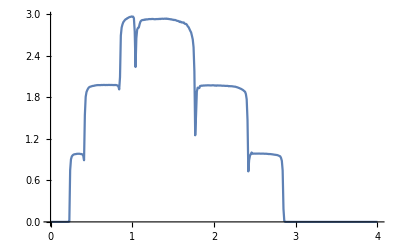

```mathematica
ListPlot[%134,Joined->True]
```

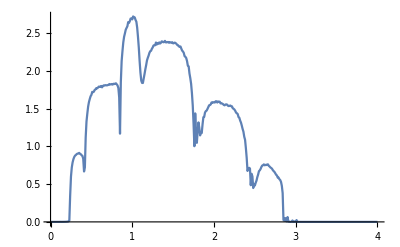

```mathematica
ListPlot[%123,Joined->True]
```

```mathematica
final5=(m+n+o+p+q+r)/6
```

{{0.,0.0000295423},{0.01,0.0000607214},{0.02,0.0000267085},{0.03,0.0000273454},{0.04,0.000024975},{0.05,0.000067175},{0.06,0.0000387352},{0.07,0.0000491155},{0.08,0.0000442581},{0.09,0.0000487102},{0.1,0.0000658},{0.11,0.0000812745},{0.12,0.000103185},{0.13,0.000116913},{0.14,0.000152272},{0.15,0.000204371},{0.16,0.000253783},{0.17,0.000339132},{0.18,0.000442075},{0.19,0.000669051},{0.2,0.000970388},{0.21,0.0019007},{0.22,0.00269397},{0.23,0.0083426},{0.24,0.563348},{0.25,0.790074},{0.26,0.866702},{0.27,0.899541},{0.28,0.921603},{0.29,0.941989},{0.3,0.950968},{0.31,0.957884},{0.32,0.954808},{0.33,0.96064},{0.34,0.960159},{0.35,0.964528},{0.36,0.957746},{0.37,0.959789},{0.38,0.956653},{0.39,0.945826},{0.4,0.923086},{0.41,0.819172},{0.42,1.22797},{0.43,1.56512},{0.44,1.68779},{0.45,1.75731},{0.46,1.79395},{0.47,1.82464},{0.48,1.83789},{0.49,1.85664},{0.5,1.86244},{0.51,1.88043},{0.52,1.88858},{0.53,1.89566},{0.54,1.89717},{0.55,1.91085},{0.56,1.90371},{0.57,1.91816},{0.58,1.91502},{0.59,1.91968},{0.6,1.92364},{0.61,1.92597},{0.62,1.93012},{0.63,1.92912},{0.64,1.92866},{0.65,1.92993},{0.66,1.93556},{0.67,1.93577},{0.68,1.93786},{0.69,1.93138},{0.7,1.93662},{0.71,1.93635},{0.72,1.93602},{0.73,1.9372},{0.74,1.93755},{0.75,1.93991},{0.76,1.93854},{0.77,1.93604},{0.78,1.9352},{0.79,1.93494},{0.8,1.93321},{0.81,1.92415},{0.82,1.9191},{0.83,1.89525},{0.84,1.82347},{0.85,1.60411},{0.86,2.31722},{0.87,2.52115},{0.88,2.62753},{0.89,2.68862},{0.9,2.72818},{0.91,2.75628},{0.92,2.78359},{0.93,2.79598},{0.94,2.80995},{0.95,2.831},{0.96,2.84235},{0.97,2.85042},{0.98,2.85337},{0.99,2.86966},{1.,2.86322},{1.01,2.87842},{1.02,2.86999},{1.03,2.83633},{1.04,2.75774},{1.05,2.51714},{1.06,2.14573},{1.07,2.11088},{1.08,2.32156},{1.09,2.47258},{1.1,2.53753},{1.11,2.58995},{1.12,2.60925},{1.13,2.63216},{1.14,2.65206},{1.15,2.68833},{1.16,2.70291},{1.17,2.72806},{1.18,2.74125},{1.19,2.74651},{1.2,2.75453},{1.21,2.76122},{1.22,2.75586},{1.23,2.76925},{1.24,2.77449},{1.25,2.78065},{1.26,2.77688},{1.27,2.77995},{1.28,2.78756},{1.29,2.78511},{1.3,2.78414},{1.31,2.79125},{1.32,2.78518},{1.33,2.79251},{1.34,2.786},{1.35,2.79184},{1.36,2.78066},{1.37,2.79002},{1.38,2.78994},{1.39,2.78386},{1.4,2.78592},{1.41,2.7934},{1.42,2.79349},{1.43,2.78671},{1.44,2.78516},{1.45,2.79045},{1.46,2.78927},{1.47,2.78497},{1.48,2.78662},{1.49,2.77442},{1.5,2.77205},{1.51,2.76509},{1.52,2.76568},{1.53,2.76545},{1.54,2.76093},{1.55,2.75298},{1.56,2.72893},{1.57,2.74215},{1.58,2.7112},{1.59,2.7185},{1.6,2.71791},{1.61,2.70294},{1.62,2.70303},{1.63,2.68608},{1.64,2.67848},{1.65,2.66611},{1.66,2.65812},{1.67,2.63044},{1.68,2.60362},{1.69,2.56762},{1.7,2.52294},{1.71,2.47374},{1.72,2.41334},{1.73,2.33971},{1.74,2.23196},{1.75,2.04515},{1.76,1.53708},{1.77,1.50186},{1.78,1.24496},{1.79,1.40842},{1.8,1.60675},{1.81,1.73195},{1.82,1.79191},{1.83,1.85046},{1.84,1.86417},{1.85,1.84602},{1.86,1.87077},{1.87,1.87538},{1.88,1.88904},{1.89,1.88841},{1.9,1.89007},{1.91,1.88949},{1.92,1.90483},{1.93,1.90092},{1.94,1.90966},{1.95,1.91139},{1.96,1.91502},{1.97,1.90771},{1.98,1.91376},{1.99,1.91275},{2.,1.91025},{2.01,1.89143},{2.02,1.90026},{2.03,1.89998},{2.04,1.90026},{2.05,1.89389},{2.06,1.89375},{2.07,1.89299},{2.08,1.88944},{2.09,1.88774},{2.1,1.88455},{2.11,1.87479},{2.12,1.88014},{2.13,1.86971},{2.14,1.86595},{2.15,1.8722},{2.16,1.87338},{2.17,1.86714},{2.18,1.86537},{2.19,1.86404},{2.2,1.86269},{2.21,1.86142},{2.22,1.85986},{2.23,1.85142},{2.24,1.84896},{2.25,1.84569},{2.26,1.84534},{2.27,1.83672},{2.28,1.83006},{2.29,1.81734},{2.3,1.80594},{2.31,1.79345},{2.32,1.77537},{2.33,1.75292},{2.34,1.7336},{2.35,1.71295},{2.36,1.68813},{2.37,1.6696},{2.38,1.63006},{2.39,1.56835},{2.4,1.45438},{2.41,1.09717},{2.42,0.84229},{2.43,0.697419},{2.44,0.65272},{2.45,0.7836},{2.46,0.893},{2.47,0.893179},{2.48,0.905269},{2.49,0.908587},{2.5,0.925944},{2.51,0.923523},{2.52,0.932988},{2.53,0.919964},{2.54,0.936939},{2.55,0.938059},{2.56,0.939219},{2.57,0.939978},{2.58,0.937479},{2.59,0.937612},{2.6,0.939697},{2.61,0.939336},{2.62,0.939877},{2.63,0.935152},{2.64,0.933968},{2.65,0.931932},{2.66,0.929526},{2.67,0.926093},{2.68,0.920853},{2.69,0.913857},{2.7,0.90821},{2.71,0.902936},{2.72,0.892004},{2.73,0.88516},{2.74,0.882298},{2.75,0.87512},{2.76,0.867962},{2.77,0.859185},{2.78,0.852852},{2.79,0.849783},{2.8,0.84504},{2.81,0.825989},{2.82,0.798444},{2.83,0.75176},{2.84,0.596724},{2.85,0.0327291},{2.86,0.142336},{2.87,0.00553776},{2.88,0.00340259},{2.89,0.000372416},{2.9,0.000164554},{2.91,0.0000991167},{2.92,0.0000716683},{2.93,0.000160541},{2.94,0.0000593772},{2.95,0.0000276408},{2.96,0.000230437},{2.97,0.0000178061},{2.98,0.0000184284},{2.99,0.0000211163},{3.,0.0000309547},{3.01,0.000111057},{3.02,0.0000124707},{3.03,8.54076×10^-6},{3.04,8.19885×10^-6},{3.05,0.000039372},{3.06,0.0000338481},{3.07,7.46027×10^-6},{3.08,0.0000254235},{3.09,7.97756×10^-6},{3.1,5.2452×10^-6},{3.11,3.7648×10^-6},{3.12,0.0000215379},{3.13,0.0000176766},{3.14,0.0000145699},{3.15,2.55374×10^-6},{3.16,2.85263×10^-6},{3.17,2.35229×10^-6},{3.18,2.66036×10^-6},{3.19,9.30251×10^-6},{3.2,2.14244×10^-6},{3.21,8.64942×10^-6},{3.22,1.74229×10^-6},{3.23,2.09174×10^-6},{3.24,6.82519×10^-6},{3.25,1.42605×10^-6},{3.26,5.51886×10^-6},{3.27,1.47961×10^-6},{3.28,7.6383×10^-6},{3.29,4.74378×10^-6},{3.3,4.04614×10^-6},{3.31,6.37108×10^-6},{3.32,1.02189×10^-6},{3.33,3.58326×10^-6},{3.34,3.4912×10^-6},{3.35,4.83448×10^-6},{3.36,8.74106×10^-7},{3.37,8.74348×10^-7},{3.38,8.01238×10^-7},{3.39,3.75842×10^-6},{3.4,7.49311×10^-7},{3.41,2.26271×10^-6},{3.42,2.074×10^-6},{3.43,1.9556×10^-6},{3.44,1.86769×10^-6},{3.45,1.76659×10^-6},{3.46,6.17636×10^-7},{3.47,5.88222×10^-7},{3.48,5.84056×10^-7},{3.49,5.56602×10^-7},{3.5,5.38311×10^-7},{3.51,5.17998×10^-7},{3.52,5.0243×10^-7},{3.53,4.90859×10^-7},{3.54,4.77573×10^-7},{3.55,1.13094×10^-6},{3.56,1.0778×10^-6},{3.57,4.36007×10^-7},{3.58,4.19704×10^-7},{3.59,9.26091×10^-7},{3.6,3.97075×10^-7},{3.61,8.52619×10^-7},{3.62,3.7613×10^-7},{3.63,3.66204×10^-7},{3.64,3.5551×10^-7},{3.65,1.08837×10^-6},{3.66,1.0195×10^-6},{3.67,3.27522×10^-7},{3.68,6.49178×10^-7},{3.69,3.14855×10^-7},{3.7,8.68798×10^-7},{3.71,2.99704×10^-7},{3.72,5.53744×10^-7},{3.73,2.8552×10^-7},{3.74,2.78237×10^-7},{3.75,5.11614×10^-7},{3.76,4.87803×10^-7},{3.77,2.59506×10^-7},{3.78,6.47033×10^-7},{3.79,2.45192×10^-7},{3.8,2.39991×10^-7},{3.81,2.37099×10^-7},{3.82,2.31904×10^-7},{3.83,2.23946×10^-7},{3.84,5.24357×10^-7},{3.85,2.15716×10^-7},{3.86,3.51308×10^-7},{3.87,2.06735×10^-7},{3.88,2.02636×10^-7},{3.89,4.44454×10^-7},{3.9,1.94333×10^-7},{3.91,1.91642×10^-7},{3.92,4.04143×10^-7},{3.93,3.90304×10^-7},{3.94,2.80901×10^-7},{3.95,3.71174×10^-7},{3.96,1.72606×10^-7},{3.97,2.59524×10^-7},{3.98,2.51907×10^-7},{3.99,2.45427×10^-7},{4.,2.38979×10^-7}}

```mathematica
Export["epis5.csv",final5]
```

epis5.csv

```mathematica
final4=(m+n+o+p+q+r)/6
```

{{0.,0.0000338434},{0.01,0.0000339127},{0.02,0.0000270748},{0.03,0.0000257991},{0.04,0.0000249196},{0.05,0.0000250524},{0.06,0.0000277063},{0.07,0.000031278},{0.08,0.0000389718},{0.09,0.0000417771},{0.1,0.000059259},{0.11,0.0000778042},{0.12,0.0000788297},{0.13,0.00011076},{0.14,0.000155545},{0.15,0.000210677},{0.16,0.000236137},{0.17,0.000326651},{0.18,0.000492877},{0.19,0.000639696},{0.2,0.000835198},{0.21,0.00134212},{0.22,0.00261748},{0.23,0.00971533},{0.24,0.703138},{0.25,0.874204},{0.26,0.920463},{0.27,0.942869},{0.28,0.951556},{0.29,0.964767},{0.3,0.969486},{0.31,0.970402},{0.32,0.972145},{0.33,0.975084},{0.34,0.977795},{0.35,0.977876},{0.36,0.976533},{0.37,0.975818},{0.38,0.971541},{0.39,0.962313},{0.4,0.948525},{0.41,0.869847},{0.42,1.3873},{0.43,1.68839},{0.44,1.78273},{0.45,1.83047},{0.46,1.85952},{0.47,1.88665},{0.48,1.89676},{0.49,1.90793},{0.5,1.91428},{0.51,1.92129},{0.52,1.92681},{0.53,1.92547},{0.54,1.93228},{0.55,1.93658},{0.56,1.93249},{0.57,1.935},{0.58,1.94165},{0.59,1.9439},{0.6,1.94685},{0.61,1.9442},{0.62,1.94866},{0.63,1.94576},{0.64,1.95166},{0.65,1.95209},{0.66,1.95256},{0.67,1.95537},{0.68,1.95386},{0.69,1.95756},{0.7,1.95816},{0.71,1.95946},{0.72,1.95711},{0.73,1.96123},{0.74,1.96191},{0.75,1.96185},{0.76,1.95986},{0.77,1.96174},{0.78,1.96077},{0.79,1.96028},{0.8,1.96054},{0.81,1.95556},{0.82,1.94927},{0.83,1.93182},{0.84,1.88194},{0.85,1.88013},{0.86,2.51741},{0.87,2.69388},{0.88,2.7625},{0.89,2.78996},{0.9,2.83412},{0.91,2.85574},{0.92,2.86316},{0.93,2.88201},{0.94,2.88631},{0.95,2.89919},{0.96,2.90602},{0.97,2.91929},{0.98,2.91897},{0.99,2.92717},{1.,2.93588},{1.01,2.93243},{1.02,2.90616},{1.03,2.85108},{1.04,2.58958},{1.05,2.05552},{1.06,2.26854},{1.07,2.55121},{1.08,2.65276},{1.09,2.73211},{1.1,2.76997},{1.11,2.78791},{1.12,2.81098},{1.13,2.8261},{1.14,2.83275},{1.15,2.83063},{1.16,2.85824},{1.17,2.85418},{1.18,2.86278},{1.19,2.86088},{1.2,2.86822},{1.21,2.87013},{1.22,2.86724},{1.23,2.87451},{1.24,2.87658},{1.25,2.87913},{1.26,2.87374},{1.27,2.88113},{1.28,2.87588},{1.29,2.87541},{1.3,2.88391},{1.31,2.8861},{1.32,2.8751},{1.33,2.88246},{1.34,2.88136},{1.35,2.87523},{1.36,2.8853},{1.37,2.88166},{1.38,2.88124},{1.39,2.88257},{1.4,2.87457},{1.41,2.8808},{1.42,2.87862},{1.43,2.86955},{1.44,2.87324},{1.45,2.87321},{1.46,2.86551},{1.47,2.86189},{1.48,2.85829},{1.49,2.85715},{1.5,2.85459},{1.51,2.85016},{1.52,2.84969},{1.53,2.84449},{1.54,2.84051},{1.55,2.83061},{1.56,2.82438},{1.57,2.8284},{1.58,2.82506},{1.59,2.82759},{1.6,2.81375},{1.61,2.81296},{1.62,2.80912},{1.63,2.80437},{1.64,2.79777},{1.65,2.795},{1.66,2.78226},{1.67,2.75741},{1.68,2.73414},{1.69,2.71362},{1.7,2.67619},{1.71,2.63972},{1.72,2.60763},{1.73,2.53681},{1.74,2.44702},{1.75,2.29316},{1.76,1.78904},{1.77,1.40505},{1.78,1.41682},{1.79,1.6819},{1.8,1.8479},{1.81,1.88797},{1.82,1.91058},{1.83,1.89829},{1.84,1.93169},{1.85,1.93024},{1.86,1.92845},{1.87,1.93993},{1.88,1.94016},{1.89,1.9411},{1.9,1.94279},{1.91,1.93925},{1.92,1.94168},{1.93,1.94058},{1.94,1.94447},{1.95,1.93959},{1.96,1.93854},{1.97,1.93855},{1.98,1.93759},{1.99,1.93858},{2.,1.93778},{2.01,1.93988},{2.02,1.93807},{2.03,1.93309},{2.04,1.93588},{2.05,1.93166},{2.06,1.93191},{2.07,1.93162},{2.08,1.93071},{2.09,1.92965},{2.1,1.92638},{2.11,1.91957},{2.12,1.92311},{2.13,1.92192},{2.14,1.92315},{2.15,1.92081},{2.16,1.91345},{2.17,1.9152},{2.18,1.91108},{2.19,1.91525},{2.2,1.91019},{2.21,1.90899},{2.22,1.90316},{2.23,1.8999},{2.24,1.90107},{2.25,1.88621},{2.26,1.88411},{2.27,1.87089},{2.28,1.87084},{2.29,1.8568},{2.3,1.84916},{2.31,1.83686},{2.32,1.82098},{2.33,1.80754},{2.34,1.78828},{2.35,1.77814},{2.36,1.76056},{2.37,1.74402},{2.38,1.71735},{2.39,1.66704},{2.4,1.55641},{2.41,1.1911},{2.42,0.802443},{2.43,0.91756},{2.44,0.856812},{2.45,0.931614},{2.46,0.952821},{2.47,0.977162},{2.48,0.948389},{2.49,0.965775},{2.5,0.96524},{2.51,0.967635},{2.52,0.96955},{2.53,0.969193},{2.54,0.97153},{2.55,0.971926},{2.56,0.971324},{2.57,0.969636},{2.58,0.970729},{2.59,0.971819},{2.6,0.969656},{2.61,0.971502},{2.62,0.970582},{2.63,0.969683},{2.64,0.966003},{2.65,0.964764},{2.66,0.963101},{2.67,0.959496},{2.68,0.956083},{2.69,0.95258},{2.7,0.947016},{2.71,0.942449},{2.72,0.937143},{2.73,0.932024},{2.74,0.925893},{2.75,0.919342},{2.76,0.910138},{2.77,0.909907},{2.78,0.902373},{2.79,0.898686},{2.8,0.888089},{2.81,0.88638},{2.82,0.858321},{2.83,0.806589},{2.84,0.656348},{2.85,0.0708763},{2.86,0.0373589},{2.87,0.00330336},{2.88,0.000404348},{2.89,0.000214596},{2.9,0.000226926},{2.91,0.000113334},{2.92,0.0000702469},{2.93,0.000499812},{2.94,0.000230834},{2.95,0.000119137},{2.96,0.000021569},{2.97,0.0000186373},{2.98,0.000138783},{2.99,0.0000117605},{3.,0.000082762},{3.01,0.0000593483},{3.02,7.65852×10^-6},{3.03,0.0000337687},{3.04,6.77784×10^-6},{3.05,0.0000257897},{3.06,0.0000206869},{3.07,5.89737×10^-6},{3.08,0.0000266673},{3.09,0.0000165375},{3.1,3.83497×10^-6},{3.11,0.0000183081},{3.12,0.0000112679},{3.13,3.04451×10^-6},{3.14,9.46544×10^-6},{3.15,9.06924×10^-6},{3.16,7.8017×10^-6},{3.17,2.21754×10^-6},{3.18,9.93242×10^-6},{3.19,2.13892×10^-6},{3.2,5.45793×10^-6},{3.21,1.79201×10^-6},{3.22,7.56377×10^-6},{3.23,1.57191×10^-6},{3.24,4.44737×10^-6},{3.25,1.54893×10^-6},{3.26,1.36519×10^-6},{3.27,5.36483×10^-6},{3.28,1.31555×10^-6},{3.29,3.12838×10^-6},{3.3,1.15574×10^-6},{3.31,1.12761×10^-6},{3.32,1.03404×10^-6},{3.33,1.03214×10^-6},{3.34,3.27388×10^-6},{3.35,9.02632×10^-7},{3.36,2.94872×10^-6},{3.37,8.67074×10^-7},{3.38,1.8197×10^-6},{3.39,2.49518×10^-6},{3.4,7.45127×10^-7},{3.41,1.60432×10^-6},{3.42,6.98346×10^-7},{3.43,2.07086×10^-6},{3.44,1.92043×10^-6},{3.45,6.2941×10^-7},{3.46,6.06475×10^-7},{3.47,1.16866×10^-6},{3.48,1.11666×10^-6},{3.49,1.51797×10^-6},{3.5,5.37016×10^-7},{3.51,5.18906×10^-7},{3.52,1.30299×10^-6},{3.53,4.84689×10^-7},{3.54,4.7505×10^-7},{3.55,4.61167×10^-7},{3.56,4.47838×10^-7},{3.57,7.62073×10^-7},{3.58,4.22901×10^-7},{3.59,9.83709×10^-7},{3.6,3.97958×10^-7},{3.61,3.84117×10^-7},{3.62,3.77732×10^-7},{3.63,6.0664×10^-7},{3.64,3.58215×10^-7},{3.65,3.45591×10^-7},{3.66,5.45355×10^-7},{3.67,7.07742×10^-7},{3.68,3.22553×10^-7},{3.69,4.91774×10^-7},{3.7,3.0467×10^-7},{3.71,4.60138×10^-7},{3.72,4.498×10^-7},{3.73,4.30883×10^-7},{3.74,5.55423×10^-7},{3.75,2.70912×10^-7},{3.76,5.13855×10^-7},{3.77,4.9687×10^-7},{3.78,2.51848×10^-7},{3.79,3.57967×10^-7},{3.8,3.47616×10^-7},{3.81,2.37541×10^-7},{3.82,3.28942×10^-7},{3.83,2.2615×10^-7},{3.84,2.22228×10^-7},{3.85,2.16222×10^-7},{3.86,2.13211×10^-7},{3.87,2.08526×10^-7},{3.88,2.79124×10^-7},{3.89,2.00172×10^-7},{3.9,1.95941×10^-7},{3.91,1.91356×10^-7},{3.92,1.87527×10^-7},{3.93,1.83799×10^-7},{3.94,1.80127×10^-7},{3.95,2.86667×10^-7},{3.96,1.73658×10^-7},{3.97,1.69824×10^-7},{3.98,1.6698×10^-7},{3.99,2.57207×10^-7},{4.,2.51034×10^-7}}

```mathematica
Export["epis4.csv",final4]
```

epis4.csv

```mathematica
SystemOpen["epis4.dat"]
```

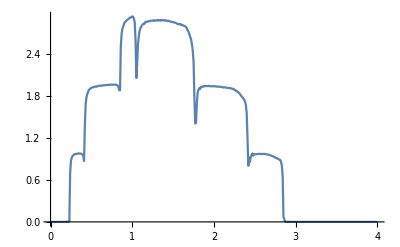

```mathematica
ListPlot[final4,Joined->True]
```

```mathematica
Clear[Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,Il1,Ir1,gdd1,grr1,Gnonlocal1,GNON1,Λ];X[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ2+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ3+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ2+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}];
```

```mathematica
Λ[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-g.T1[t].SL[ω,δ,t,ϵ].T1[t]].g;
Sl12:=Inverse[IdentityMatrix[7]-X[ω,δ,t,ϵ,ϵ2,ϵ3].T2[t].Sl11.T2[t]].X[ω,δ,t,ϵ,ϵ2,ϵ3];
Il1:=Inverse[IdentityMatrix[7]-Sl12.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl12;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl12.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

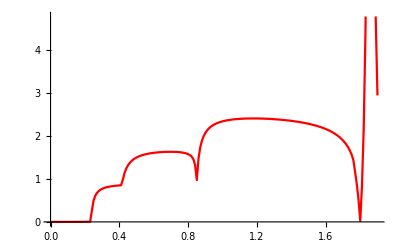

```mathematica
ListLinePlot[Table[{ω,Λ[ω,0.001,1,0,01,0.2]},{ω,Range[0,1.9,0.01]}],PlotStyle->Red]
```

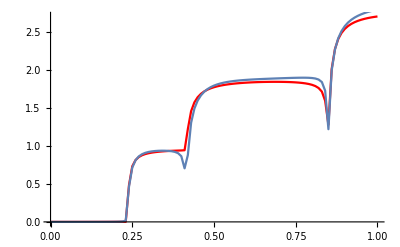

```mathematica
Show[ListLinePlot[Table[{ω,Λ[ω,0.001,1,0,0.6,0.1]},{ω,Range[0,1,0.01]}],PlotStyle->Red],ListLinePlot[final7]]
```

```mathematica
f7[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{final7[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- final7[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ7:=ρ7=Table[{b,a,f7[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
ρ7
```

{{{0.,-1.,2.4793},{0.05,-1.,2.31751},{0.1,-1.,2.05981},{0.15,-1.,1.73309},{0.2,-1.,1.41559},{0.25,-1.,1.17431},{0.3,-1.,1.09829},{0.35,-1.,1.37526},{0.4,-1.,1.62643},{0.45,-1.,1.12452},21,{1.55,-1.,0.795707},{1.6,-1.,0.817957},{1.65,-1.,0.840065},{1.7,-1.,0.861992},{1.75,-1.,0.883703},{1.8,-1.,0.90517},{1.85,-1.,0.92637},{1.9,-1.,0.947241},{1.95,-1.,0.96673},{2.,-1.,0.985934}},39,{1}}
 |  |  |  |

```mathematica
κ1=Transpose[ρ7,{2,1,3}]
```

{{{0.,-1.,2.4793},{0.,-0.95,2.73808},{0.,-0.9,3.19779},{0.,-0.85,3.87121},{0.,-0.8,4.62442},{0.,-0.75,5.03986},{0.,-0.7,4.54671},{0.,-0.65,3.12679},{0.,-0.6,1.61894},{0.,-0.55,0.647626},21,{0.,0.55,0.0268502},{0.,0.6,0.0267542},{0.,0.65,0.0277615},{0.,0.7,0.0297877},{0.,0.75,0.0327449},{0.,0.8,0.0365439},{0.,0.85,0.0410957},{0.,0.9,0.0463134},{0.,0.95,0.0521135},{0.,1.,0.0584168}},39,{1}}
 |  |  |  |

```mathematica
Join[κ1[[1]],κ1[[2]],κ1[[3]],κ1[[4]]]
```

{{0.,-1.,2.4793},{0.,-0.95,2.73808},{0.,-0.9,3.19779},{0.,-0.85,3.87121},{0.,-0.8,4.62442},{0.,-0.75,5.03986},{0.,-0.7,4.54671},{0.,-0.65,3.12679},{0.,-0.6,1.61894},{0.,-0.55,0.647626},{0.,-0.5,0.192429},{0.,-0.45,0.0522747},{0.,-0.4,0.0432845},{0.,-0.35,0.0658064},{0.,-0.3,0.0535717},{0.,-0.25,0.0566962},{0.,-0.2,0.0664866},{0.,-0.15,0.078499},{0.,-0.1,0.0893467},{0.,-0.05,0.0961056},{0.,0.,0.0971007},{0.,0.05,0.0925665},{0.,0.1,0.0842137},{0.,0.15,0.0741236},{0.,0.2,0.0639192},{0.,0.25,0.0545516},{0.,0.3,0.0464567},{0.,0.35,0.0397792},{0.,0.4,0.0345297},{0.,0.45,0.0306667},{0.,0.5,0.0281296},{0.,0.55,0.0268502},{0.,0.6,0.0267542},{0.,0.65,0.0277615},{0.,0.7,0.0297877},{0.,0.75,0.0327449},{0.,0.8,0.0365439},{0.,0.85,0.0410957},{0.,0.9,0.0463134},{0.,0.95,0.0521135},{0.,1.,0.0584168},{0.05,-1.,2.31751},{0.05,-0.95,2.60618},{0.05,-0.9,2.9885},{0.05,-0.85,3.38046},{0.05,-0.8,3.61106},{0.05,-0.75,3.45258},{0.05,-0.7,2.7234},{0.05,-0.65,1.72985},{0.05,-0.6,0.900497},{0.05,-0.55,0.39168},{0.05,-0.5,0.134982},{0.05,-0.45,0.0509352},{0.05,-0.4,0.0470862},{0.05,-0.35,0.0667686},{0.05,-0.3,0.0512409},{0.05,-0.25,0.0504371},{0.05,-0.2,0.0573888},{0.05,-0.15,0.0681273},{0.05,-0.1,0.0792829},{0.05,-0.05,0.0877034},{0.05,0.,0.0912925},{0.05,0.05,0.0896959},{0.05,0.1,0.0840045},{0.05,0.15,0.0758605},{0.05,0.2,0.0667338},{0.05,0.25,0.0576512},{0.05,0.3,0.0492306},{0.05,0.35,0.0418095},{0.05,0.4,0.0355576},{0.05,0.45,0.0305488},{0.05,0.5,0.0268011},{0.05,0.55,0.0242969},{0.05,0.6,0.022995},{0.05,0.65,0.0228365},{0.05,0.7,0.0237502},{0.05,0.75,0.0256564},{0.05,0.8,0.0284707},{0.05,0.85,0.0321064},{0.05,0.9,0.0364772},{0.05,0.95,0.041499},{0.05,1.,0.0470911},{0.1,-1.,2.05981},{0.1,-0.95,2.26907},{0.1,-0.9,2.48398},{0.1,-0.85,2.62352},{0.1,-0.8,2.60929},{0.1,-0.75,2.25819},{0.1,-0.7,1.63464},{0.1,-0.65,1.01583},{0.1,-0.6,0.540858},{0.1,-0.55,0.253453},{0.1,-0.5,0.0994776},{0.1,-0.45,0.0515917},{0.1,-0.4,0.0557397},{0.1,-0.35,0.0716397},{0.1,-0.3,0.0518487},{0.1,-0.25,0.0458905},{0.1,-0.2,0.0484431},{0.1,-0.15,0.0562437},{0.1,-0.1,0.0661901},{0.1,-0.05,0.0750966},{0.1,0.,0.080544},{0.1,0.05,0.0816016},{0.1,0.1,0.0787038},{0.1,0.15,0.0729805},{0.1,0.2,0.0656421},{0.1,0.25,0.0576743},{0.1,0.3,0.0497778},{0.1,0.35,0.0424161},{0.1,0.4,0.0358823},{0.1,0.45,0.0303535},{0.1,0.5,0.0259273},{0.1,0.55,0.0226459},{0.1,0.6,0.0205112},{0.1,0.65,0.0194965},{0.1,0.7,0.0195542},{0.1,0.75,0.0206214},{0.1,0.8,0.0226259},{0.1,0.85,0.0254897},{0.1,0.9,0.0291322},{0.1,0.95,0.0334728},{0.1,1.,0.0384329},{0.15,-1.,1.73309},{0.15,-0.95,1.85035},{0.15,-0.9,1.95104},{0.15,-0.85,2.01493},{0.15,-0.8,1.87518},{0.15,-0.75,1.45331},{0.15,-0.7,1.02943},{0.15,-0.65,0.641882},{0.15,-0.6,0.353827},{0.15,-0.55,0.178734},{0.15,-0.5,0.0751861},{0.15,-0.45,0.04125},{0.15,-0.4,0.046967},{0.15,-0.35,0.072645},{0.15,-0.3,0.0570742},{0.15,-0.25,0.0450155},{0.15,-0.2,0.0419751},{0.15,-0.15,0.0455006},{0.15,-0.1,0.0528906},{0.15,-0.05,0.0610482},{0.15,0.,0.0673315},{0.15,0.05,0.0703134},{0.15,0.1,0.0698224},{0.15,0.15,0.0664746},{0.15,0.2,0.061163},{0.15,0.25,0.0547435},{0.15,0.3,0.0479113},{0.15,0.35,0.0411868},{0.15,0.4,0.0349402},{0.15,0.45,0.0294251},{0.15,0.5,0.0248064},{0.15,0.55,0.0211816},{0.15,0.6,0.0185976},{0.15,0.65,0.0170627},{0.15,0.7,0.0165571},{0.15,0.75,0.0170399},{0.15,0.8,0.0184554},{0.15,0.85,0.0207384},{0.15,0.9,0.0238178},{0.15,0.95,0.02762},{0.15,1.,0.0320712}}

```mathematica
Table[{i,{Min/@Transpose[ρ7[[i]]]}[[1,3]]},{i,41}]
```

{{1,0.471891},{2,0.442281},{3,0.419074},{4,0.39067},{5,0.359997},{6,0.32603},{7,0.281999},{8,0.227422},{9,0.17294},{10,0.124675},{11,0.0657095},{12,0.0387511},{13,0.0413774},{14,0.0537564},{15,0.0404503},{16,0.0291873},{17,0.0242946},{18,0.0250795},{19,0.0179964},{20,0.0106347},{21,0.00654988},{22,0.00425813},{23,0.00399752},{24,0.00427785},{25,0.00529713},{26,0.00660588},{27,0.00796638},{28,0.0092889},{29,0.0103055},{30,0.0109875},{31,0.0114662},{32,0.0116746},{33,0.0115358},{34,0.0113608},{35,0.0113804},{36,0.0118583},{37,0.0129925},{38,0.0147455},{39,0.0172321},{40,0.0204077},{41,0.0242215}}

0.00399752

```mathematica
Position[%226,Min[%226]]
```

{{23,2}}

```mathematica
{Min/@Transpose[ρ3[[i]]]}[[1,3]]
```

0.572872

```mathematica
Extract[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}],{{23,1}}]
```

{23}

```mathematica
Position[ρ7[[Extract[Table[{i,{Min/@Transpose[ρ7[[i]]]}[[1,3]]},{i,41}],{{23,1}}]]],Min[Table[{i,{Min/@Transpose[ρ7[[i]]]}[[1,3]]},{i,41}]]]
```

{{1,13,3}}

```mathematica
{Extract[ρ7⟦Extract[Table[{i,{Min/@Transpose[ρ7⟦i⟧]}⟦1,3⟧},{i,41}],{{23,1}}]⟧,{{1,13,1}}],Extract[ρ7⟦Extract[Table[{i,{Min/@Transpose[ρ7⟦i⟧]}⟦1,3⟧},{i,41}],{{23,1}}]⟧,{{1,13,2}}],Extract[ρ7⟦Extract[Table[{i,{Min/@Transpose[ρ7⟦i⟧]}⟦1,3⟧},{i,41}],{{23,1}}]⟧,{{1,13,3}}]}
```

{{0.6},{0.1},{0.00399752}}

```mathematica
ρ7[[Extract[%226,{{23,1}}]]]
```

{{{0.,0.1,0.0842137},{0.05,0.1,0.0840045},{0.1,0.1,0.0787038},{0.15,0.1,0.0698224},{0.2,0.1,0.0589754},{0.25,0.1,0.0475032},{0.3,0.1,0.0363923},{0.35,0.1,0.0263321},{0.4,0.1,0.0177973},{0.45,0.1,0.0111137},{0.5,0.1,0.00650178},{0.55,0.1,0.00410304},{0.6,0.1,0.00399752},{0.65,0.1,0.00621607},{0.7,0.1,0.0107484},{0.75,0.1,0.0175509},{0.8,0.1,0.026553},{0.85,0.1,0.0376628},{0.9,0.1,0.050772},{0.95,0.1,0.0657603},{1.,0.1,0.0824995},{1.05,0.1,0.100856},{1.1,0.1,0.120695},{1.15,0.1,0.141879},{1.2,0.1,0.164277},{1.25,0.1,0.187758},{1.3,0.1,0.212195},{1.35,0.1,0.23747},{1.4,0.1,0.263467},{1.45,0.1,0.290079},{1.5,0.1,0.317205},{1.55,0.1,0.344751},{1.6,0.1,0.372629},{1.65,0.1,0.400759},{1.7,0.1,0.429065},{1.75,0.1,0.456418},{1.8,0.1,0.483414},{1.85,0.1,0.510458},{1.9,0.1,0.537496},{1.95,0.1,0.564479},{2.,0.1,0.591364}}}

```mathematica
Dimensions[%187]
```

{41,41,3}

```mathematica
Flatten[ρ7]
```

```mathematica
f3[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis23.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis23.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ3:=ρ3=Table[{b,a,f3[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
ρ3
```

{{{0.,-1.,2.50601},{0.05,-1.,2.3463},{0.1,-1.,2.09382},{0.15,-1.,1.77468},{0.2,-1.,1.46613},{0.25,-1.,1.23451},{0.3,-1.,1.1686},{0.35,-1.,1.4561},{0.4,-1.,1.7176},{0.45,-1.,1.22521},21,{1.55,-1.,1.05174},{1.6,-1.,1.07866},{1.65,-1.,1.10527},{1.7,-1.,1.13156},{1.75,-1.,1.15748},{1.8,-1.,1.18301},{1.85,-1.,1.20814},{1.9,-1.,1.23281},{1.95,-1.,1.25592},{2.,-1.,1.27863}},39,{1}}
 |  |  |  |

```mathematica
Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]
```

0.000390668

```mathematica
ρ3[[Position[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]]
```

{{0.,0.05,0.0118692},{0.05,0.05,0.0107651},{0.1,0.05,0.0079},{0.15,0.05,0.00451984},{0.2,0.05,0.001758},{0.25,0.05,0.000390668},{0.3,0.05,0.000867791},{0.35,0.05,0.00342649},{0.4,0.05,0.00818587},{0.45,0.05,0.0152019},{0.5,0.05,0.0244929},{0.55,0.05,0.0360496},{0.6,0.05,0.0498391},{0.65,0.05,0.0658062},{0.7,0.05,0.0838763},{0.75,0.05,0.103957},{0.8,0.05,0.125941},{0.85,0.05,0.149711},{0.9,0.05,0.17514},{0.95,0.05,0.202094},{1.,0.05,0.23044},{1.05,0.05,0.26004},{1.1,0.05,0.290758},{1.15,0.05,0.322463},{1.2,0.05,0.355025},{1.25,0.05,0.388322},{1.3,0.05,0.422234},{1.35,0.05,0.456651},{1.4,0.05,0.491467},{1.45,0.05,0.526585},{1.5,0.05,0.559518},{1.55,0.05,0.592178},{1.6,0.05,0.625006},{1.65,0.05,0.657925},{1.7,0.05,0.690864},{1.75,0.05,0.723759},{1.8,0.05,0.756553},{1.85,0.05,0.789194},{1.9,0.05,0.821636},{1.95,0.05,0.853838},{2.,0.05,0.885764}}

```mathematica
Position[ρ3[[Position[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]]
```

```mathematica
{{6,3}}s
```

```mathematica
{Extract[ρ3⟦Position[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ3[[Position[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ3⟦Position[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ3[[Position[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ3⟦Position[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ3[[Position[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ3[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.25},{0.05},{0.000390668}}

```mathematica
{Extract[ρ3⟦Extract[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}],{{23,1}}]⟧,{{1,13,1}}],Extract[ρ3⟦Extract[Table[{i,{Min/@Transpose[ρ7⟦i⟧]}⟦1,3⟧},{i,41}],{{23,1}}]⟧,{{1,13,2}}],Extract[ρ3⟦Extract[Table[{i,{Min/@Transpose[ρ3⟦i⟧]}⟦1,3⟧},{i,41}],{{23,1}}]⟧,{{1,13,3}}]}
```

```mathematica
f4[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis24.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis24.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ4:=ρ4=Table[{b,a,f4[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
{Extract[ρ4⟦Position[Table[{i,{Min/@Transpose[ρ4⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ4⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ4[[Position[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ4⟦Position[Table[{i,{Min/@Transpose[ρ4⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ4⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ4[[Position[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ4⟦Position[Table[{i,{Min/@Transpose[ρ4⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ4⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ4[[Position[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ4[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.35},{0.1},{0.000521434}}

```mathematica
ρ4
```

{{{0.,-1.,2.49036},{0.05,-1.,2.33018},{0.1,-1.,2.07673},{0.15,-1.,1.75621},{0.2,-1.,1.44602},{0.25,-1.,1.21257},{0.3,-1.,1.14467},{0.35,-1.,1.43},{0.4,-1.,1.68935},{0.45,-1.,1.19512},21,{1.55,-1.,0.988079},{1.6,-1.,1.01396},{1.65,-1.,1.03957},{1.7,-1.,1.06488},{1.75,-1.,1.08987},{1.8,-1.,1.1145},{1.85,-1.,1.13876},{1.9,-1.,1.16258},{1.95,-1.,1.18489},{2.,-1.,1.20682}},39,{1}}
 |  |  |  |

```mathematica
f5[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ5:=ρ5=Table[{b,a,f5[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
ρ5
```

{{{0.,-1.,2.47793},{0.05,-1.,2.31717},{0.1,-1.,2.06219},{0.15,-1.,1.73944},{0.2,-1.,1.42664},{0.25,-1.,1.19043},{0.3,-1.,1.11973},{0.35,-1.,1.40225},{0.4,-1.,1.65874},{0.45,-1.,1.16147},21,{1.55,-1.,0.906768},{1.6,-1.,0.931204},{1.65,-1.,0.955425},{1.7,-1.,0.979392},{1.75,-1.,1.00307},{1.8,-1.,1.02645},{1.85,-1.,1.04949},{1.9,-1.,1.07214},{1.95,-1.,1.09333},{2.,-1.,1.11418}},39,{1}}
 |  |  |  |

```mathematica
{Extract[ρ5⟦Position[Table[{i,{Min/@Transpose[ρ5⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ5⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ5[[Position[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ5⟦Position[Table[{i,{Min/@Transpose[ρ5⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ5⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ5[[Position[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ5⟦Position[Table[{i,{Min/@Transpose[ρ5⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ5⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ5[[Position[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ5[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.45},{0.1},{0.00099097}}

```mathematica
f6[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis26.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis26.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ6:=ρ6=Table[{b,a,f6[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
{Extract[ρ6⟦Position[Table[{i,{Min/@Transpose[ρ6⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ6⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ6[[Position[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ6⟦Position[Table[{i,{Min/@Transpose[ρ6⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ6⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ6[[Position[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ6⟦Position[Table[{i,{Min/@Transpose[ρ6⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ6⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ6[[Position[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ6[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.5},{0.1},{0.00159822}}

```mathematica
f8[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis28.csv"][[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis28.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/1]
```

```mathematica
ρ8:=ρ8=Table[{b,a,f6[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

```mathematica
{Extract[ρ8⟦Position[Table[{i,{Min/@Transpose[ρ8⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ8⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ8[[Position[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ8⟦Position[Table[{i,{Min/@Transpose[ρ8⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ8⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ8[[Position[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ8⟦Position[Table[{i,{Min/@Transpose[ρ8⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ8⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ8[[Position[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ8[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

```mathematica
rr3=Join[ρ3[-1],ρ3[-9/10],ρ3[-4/5],ρ3[-7/10],ρ3[-3/5],ρ3[-1/2],ρ3[-2/5],ρ3[-3/10],ρ3[-1/5],ρ3[-1/10],ρ3[0],ρ3[1/10],ρ3[1/5],ρ3[3/10],ρ3[2/5],ρ3[1/2],ρ3[3/5],ρ3[7/10],ρ3[4/5],ρ3[9/10],ρ3[1]]
```

{{-1,-1.,0.00520468},{-1,-0.95,0.0141548},{-1,-0.9,0.0935865},{-1,-0.85,0.416149},{-1,-0.8,1.30833},{-1,-0.75,3.28967},{-1,-0.7,7.11731},{-1,-0.65,13.8427},{-1,-0.6,24.8819},{-1,-0.55,42.1025},{-1,-0.5,67.9318},{-1,-0.45,105.491},{-1,-0.4,158.765},{-1,-0.35,232.813},{-1,-0.3,334.034},{-1,-0.25,470.511},{-1,-0.2,652.443},{-1,-0.15,892.699},{-1,-0.1,1207.54},{-1,-0.05,1617.55},{-1,0.,2148.85},{-1,0.05,2834.69},{-1,0.1,3717.57},{-1,0.15,4851.96},{-1,0.2,6308.01},{-1,0.25,8176.42},{-1,0.3,10575.},{-1,0.35,13657.2},{-1,0.4,17624.4},{-1,0.45,22741.9},{-1,0.5,29363.1},{-1,0.55,37964.4},{-1,0.6,49202.7},{-1,0.65,64010.9},{-1,0.7,83771.2},{-1,0.75,110635.},{-1,0.8,148135.},{-1,0.85,202391.},{-1,0.9,284560.},{-1,0.95,416098.},{-1,1.,640805.},{-9/10,-1.,0.0934501},{-9/10,-0.95,0.0135301},{-9/10,-0.9,0.00395066},{-9/10,-0.85,0.0131731},{-9/10,-0.8,0.10448},{-9/10,-0.75,0.491229},{-9/10,-0.7,1.57961},{-9/10,-0.65,4.02187},{-9/10,-0.6,8.77777},{-9/10,-0.55,17.1941},{-9/10,-0.5,31.1049},{-9/10,-0.45,52.9577},{-9/10,-0.4,85.9741},{-9/10,-0.35,134.353},{-9/10,-0.3,203.529},{-9/10,-0.25,300.509},{-9/10,-0.2,434.301},{-9/10,-0.15,616.475},{-9/10,-0.1,861.89},{-9/10,-0.05,1189.65},{-9/10,0.,1624.39},{-9/10,0.05,2197.87},{-9/10,0.1,2951.3},{-9/10,0.15,3938.18},{-9/10,0.2,5228.3},{-9/10,0.25,6913.01},{-9/10,0.3,9112.37},{-9/10,0.35,11984.9},{-9/10,0.4,15741.6},{-9/10,0.45,20665.6},{-9/10,0.5,27143.1},{-9/10,0.55,35713.6},{-9/10,0.6,47155.3},{-9/10,0.65,62640.8},{-9/10,0.7,84027.2},{-9/10,0.75,114415.},{-9/10,0.8,159254.},{-9/10,0.85,228637.},{-9/10,0.9,342292.},{-9/10,0.95,541285.},{-9/10,1.,917851.},{-4/5,-1.,1.30798},{-4/5,-0.95,0.450659},{-4/5,-0.9,0.104374},{-4/5,-0.85,0.0129117},{-4/5,-0.8,0.00310593},{-4/5,-0.75,0.0128731},{-4/5,-0.7,0.120611},{-4/5,-0.65,0.594622},{-4/5,-0.6,1.95005},{-4/5,-0.55,5.0231},{-4/5,-0.5,11.0588},{-4/5,-0.45,21.8268},{-4/5,-0.4,39.7701},{-4/5,-0.35,68.1971},{-4/5,-0.3,111.53},{-4/5,-0.25,175.628},{-4/5,-0.2,268.21},{-4/5,-0.15,399.41},{-4/5,-0.1,582.509},{-4/5,-0.05,834.909},{-4/5,0.,1179.43},{-4/5,0.05,1646.03},{-4/5,0.1,2274.14},{-4/5,0.15,3115.76},{-4/5,0.2,4239.7},{-4/5,0.25,5737.32},{-4/5,0.3,7730.54},{-4/5,0.35,10383.2},{-4/5,0.4,13918.},{-4/5,0.45,18642.6},{-4/5,0.5,24993.7},{-4/5,0.55,33612.7},{-4/5,0.6,45485.1},{-4/5,0.65,62201.9},{-4/5,0.7,86468.6},{-4/5,0.75,123128.},{-4/5,0.8,181311.},{-4/5,0.85,279243.},{-4/5,0.9,455785.},{-4/5,0.95,800793.},{-4/5,1.,1.54405×10^6},{-7/10,-1.,7.11517},{-7/10,-0.95,3.62744},{-7/10,-0.9,1.57928},{-7/10,-0.85,0.538616},{-7/10,-0.8,0.120553},{-7/10,-0.75,0.0129968},{-7/10,-0.7,0.00263452},{-7/10,-0.65,0.0133151},{-7/10,-0.6,0.144345},{-7/10,-0.55,0.74028},{-7/10,-0.5,2.47014},{-7/10,-0.45,6.43431},{-7/10,-0.4,14.2955},{-7/10,-0.35,28.4548},{-7/10,-0.3,52.2838},{-7/10,-0.25,90.4313},{-7/10,-0.2,149.23},{-7/10,-0.15,237.24},{-7/10,-0.1,365.971},{-7/10,-0.05,550.862},{-7/10,0.,812.59},{-7/10,0.05,1178.85},{-7/10,0.1,1686.76},{-7/10,0.15,2386.15},{-7/10,0.2,3344.13},{-7/10,0.25,4651.45},{-7/10,0.3,6431.76},{-7/10,0.35,8855.64},{-7/10,0.4,12162.9},{-7/10,0.45,16700.},{-7/10,0.5,22987.2},{-7/10,0.55,31840.8},{-7/10,0.6,44608.3},{-7/10,0.65,63629.9},{-7/10,0.7,93183.8},{-7/10,0.75,141521.},{-7/10,0.8,225534.},{-7/10,0.85,382340.},{-7/10,0.9,700880.},{-7/10,0.95,1.41863×10^6},{-7/10,1.,3.26329×10^6},{-3/5,-1.,24.8751},{-3/5,-0.95,15.3852},{-3/5,-0.9,8.77539},{-3/5,-0.85,4.48068},{-3/5,-0.8,1.94974},{-3/5,-0.75,0.660987},{-3/5,-0.7,0.144312},{-3/5,-0.65,0.0138761},{-3/5,-0.6,0.00253055},{-3/5,-0.55,0.0146425},{-3/5,-0.5,0.179647},{-3/5,-0.45,0.951827},{-3/5,-0.4,3.22623},{-3/5,-0.35,8.49951},{-3/5,-0.3,19.0751},{-3/5,-0.25,38.3457},{-3/5,-0.2,71.1748},{-3/5,-0.15,124.414},{-3/5,-0.1,207.609},{-3/5,-0.05,333.953},{-3/5,0.,521.607},{-3/5,0.05,795.495},{-3/5,0.1,1189.8},{-3/5,0.15,1751.45},{-3/5,0.2,2545.09},{-3/5,0.25,3660.48},{-3/5,0.3,5223.8},{-3/5,0.35,7416.15},{-3/5,0.4,10505.3},{-3/5,0.45,14903.1},{-3/5,0.5,21272.2},{-3/5,0.55,30734.},{-3/5,0.6,45284.8},{-3/5,0.65,68668.4},{-3/5,0.7,108308.},{-3/5,0.75,179888.},{-3/5,0.8,319174.},{-3/5,0.85,615709.},{-3/5,0.9,1.32164×10^6},{-3/5,0.95,3.26204×10^6},{-3/5,1.,9.71423×10^6},{-1/2,-1.,67.9162},{-1/2,-0.95,47.0833},{-1/2,-0.9,31.0972},{-1/2,-0.85,19.3099},{-1/2,-0.8,11.0561},{-1/2,-0.75,5.66423},{-1/2,-0.7,2.46981},{-1/2,-0.65,0.835796},{-1/2,-0.6,0.179634},{-1/2,-0.55,0.015757},{-1/2,-0.5,0.00275006},{-1/2,-0.45,0.0171459},{-1/2,-0.4,0.233551},{-1/2,-0.35,1.27126},{-1/2,-0.3,4.37358},{-1/2,-0.25,11.6625},{-1/2,-0.2,26.4785},{-1/2,-0.15,53.8582},{-1/2,-0.1,101.198},{-1/2,-0.05,179.175},{-1/2,0.,303.037},{-1/2,0.05,494.405},{-1/2,0.1,783.852},{-1/2,0.15,1214.64},{-1/2,0.2,1848.39},{-1/2,0.25,2773.94},{-1/2,0.3,4122.24},{-1/2,0.35,6092.32},{-1/2,0.4,8999.09},{-1/2,0.45,13364.5},{-1/2,0.5,20097.7},{-1/2,0.55,30866.2},{-1/2,0.6,48896.},{-1/2,0.65,80807.8},{-1/2,0.7,141152.},{-1/2,0.75,264656.},{-1/2,0.8,543117.},{-1/2,0.85,1.25261×10^6},{-1/2,0.9,3.37299×10^6},{-1/2,0.95,1.11979×10^7},{-1/2,1.,4.82671×10^7},{-2/5,-1.,158.735},{-2/5,-0.95,118.682},{-2/5,-0.9,85.9568},{-2/5,-0.85,59.8883},{-2/5,-0.8,39.7617},{-2/5,-0.75,24.8242},{-2/5,-0.7,14.2925},{-2/5,-0.65,7.36241},{-2/5,-0.6,3.22585},{-2/5,-0.55,1.09435},{-2/5,-0.5,0.233562},{-2/5,-0.45,0.0190511},{-2/5,-0.4,0.00319127},{-2/5,-0.35,0.0214159},{-2/5,-0.3,0.319121},{-2/5,-0.25,1.77685},{-2/5,-0.2,6.20402},{-2/5,-0.15,16.7656},{-2/5,-0.1,38.5763},{-2/5,-0.05,79.5584},{-2/5,0.,151.674},{-2/5,0.05,272.714},{-2/5,0.1,468.967},{-2/5,0.15,779.321},{-2/5,0.2,1261.9},{-2/5,0.25,2005.4},{-2/5,0.3,3149.4},{-2/5,0.35,4922.65},{-2/5,0.4,7717.88},{-2/5,0.45,12244.},{-2/5,0.5,19849.6},{-2/5,0.55,33248.},{-2/5,0.6,58253.8},{-2/5,0.65,108288.},{-2/5,0.7,217260.},{-2/5,0.75,481072.},{-2/5,0.8,1.2128×10^6},{-2/5,0.85,3.64114×10^6},{-2/5,0.9,1.37935×10^7},{-2/5,0.95,6.57601×10^7},{-2/5,1.,2.21224×10^8},{-3/10,-1.,333.983},{-3/10,-0.95,263.605},{-3/10,-0.9,203.496},{-3/10,-0.85,153.027},{-3/10,-0.8,111.511},{-3/10,-0.75,78.1972},{-3/10,-0.7,52.2747},{-3/10,-0.65,32.8739},{-3/10,-0.6,19.0719},{-3/10,-0.55,9.9024},{-3/10,-0.5,4.37315},{-3/10,-0.45,1.4937},{-3/10,-0.4,0.319147},{-3/10,-0.35,0.0246065},{-3/10,-0.3,0.00375166},{-3/10,-0.25,0.0286736},{-3/10,-0.2,0.461529},{-3/10,-0.15,2.62033},{-3/10,-0.1,9.2894},{-3/10,-0.05,25.4845},{-3/10,0.,59.5832},{-3/10,0.05,125.062},{-3/10,0.1,243.245},{-3/10,0.15,447.869},{-3/10,0.2,793.083},{-3/10,0.25,1368.26},{-3/10,0.3,2326.7},{-3/10,0.35,3943.84},{-3/10,0.4,6739.98},{-3/10,0.45,11752.6},{-3/10,0.5,21177.},{-3/10,0.55,39984.1},{-3/10,0.6,80384.4},{-3/10,0.65,175526.},{-3/10,0.7,427496.},{-3/10,0.75,1.20579×10^6},{-3/10,0.8,4.14945×10^6},{-3/10,0.85,1.82171×10^7},{-3/10,0.9,8.41357×10^7},{-3/10,0.95,1.29426×10^8},{-3/10,1.,4.54542×10^7},{-1/5,-1.,652.363},{-1/5,-0.95,536.535},{-1/5,-0.9,434.246},{-1/5,-0.85,344.986},{-1/5,-0.8,268.175},{-1/5,-0.75,203.16},{-1/5,-0.7,149.211},{-1/5,-0.65,105.512},{-1/5,-0.6,71.1653},{-1/5,-0.55,45.179},{-1/5,-0.5,26.4751},{-1/5,-0.45,13.8927},{-1/5,-0.4,6.20354},{-1/5,-0.35,2.14224},{-1/5,-0.3,0.46155},{-1/5,-0.25,0.0341784},{-1/5,-0.2,0.00430077},{-1/5,-0.15,0.0414955},{-1/5,-0.1,0.712292},{-1/5,-0.05,4.12075},{-1/5,0.,14.889},{-1/5,0.05,41.7661},{-1/5,0.1,100.369},{-1/5,0.15,218.172},{-1/5,0.2,444.114},{-1/5,0.25,868.059},{-1/5,0.3,1662.11},{-1/5,0.35,3172.5},{-1/5,0.4,6135.2},{-1/5,0.45,12215.3},{-1/5,0.5,25467.3},{-1/5,0.55,56686.8},{-1/5,0.6,138024.},{-1/5,0.65,379921.},{-1/5,0.7,1.23765×10^6},{-1/5,0.75,5.03355×10^6},{-1/5,0.8,2.46303×10^7},{-1/5,0.85,7.33761×10^7},{-1/5,0.9,4.30121×10^7},{-1/5,0.95,1.3033×10^7},{-1/5,1.,4.87538×10^6},{-1/10,-1.,1207.42},{-1/10,-0.95,1026.16},{-1/10,-0.9,861.807},{-1/10,-0.85,714.035},{-1/10,-0.8,582.452},{-1/10,-0.75,466.599},{-1/10,-0.7,365.936},{-1/10,-0.65,279.84},{-1/10,-0.6,207.589},{-1/10,-0.55,148.355},{-1/10,-0.5,101.189},{-1/10,-0.45,65.0046},{-1/10,-0.4,38.5731},{-1/10,-0.35,20.5114},{-1/10,-0.3,9.28892},{-1/10,-0.25,3.25601},{-1/10,-0.2,0.712312},{-1/10,-0.15,0.0516841},{-1/10,-0.1,0.00470975},{-1/10,-0.05,0.0662324},{-1/10,0.,1.20378},{-1/10,0.05,7.19007},{-1/10,0.1,27.0945},{-1/10,0.15,80.3603},{-1/10,0.2,207.78},{-1/10,0.25,496.545},{-1/10,0.3,1140.36},{-1/10,0.35,2592.11},{-1/10,0.4,5979.42},{-1/10,0.45,14337.4},{-1/10,0.5,36678.4},{-1/10,0.55,103357.},{-1/10,0.6,334661.},{-1/10,0.65,1.31299×10^6},{-1/10,0.7,6.36585×10^6},{-1/10,0.75,2.69786×10^7},{-1/10,0.8,2.97902×10^7},{-1/10,0.85,1.03304×10^7},{-1/10,0.9,3.60861×10^6},{-1/10,0.95,1.77661×10^6},{-1/10,1.,1.44514×10^6},{0,-1.,2148.69},{0,-0.95,1876.49},{0,-0.9,1624.27},{0,-0.85,1391.94},{0,-0.8,1179.35},{0,-0.75,986.297},{0,-0.7,812.537},{0,-0.65,657.757},{0,-0.6,521.575},{0,-0.55,403.521},{0,-0.5,303.02},{0,-0.45,219.36},{0,-0.4,151.666},{0,-0.35,98.8512},{0,-0.3,59.5808},{0,-0.25,32.2341},{0,-0.2,14.8887},{0,-0.15,5.343},{0,-0.1,1.20379},{0,-0.05,0.0885788},{0,0.,0.00486878},{0,0.05,0.126411},{0,0.1,2.4975},{0,0.15,16.2718},{0,0.2,68.6734},{0,0.25,234.957},{0,0.3,724.859},{0,0.35,2150.03},{0,0.4,6429.74},{0,0.45,20241.7},{0,0.5,70307.1},{0,0.55,284713.},{0,0.6,1.40245×10^6},{0,0.65,7.10487×10^6},{0,0.7,1.37532×10^7},{0,0.75,6.26148×10^6},{0,0.8,2.19728×10^6},{0,0.85,1.00556×10^6},{0,0.9,704589.},{0,0.95,861637.},{0,1.,1.73853×10^6},{1/10,-1.,3717.38},{1/10,-0.95,3323.17},{1/10,-0.9,2951.15},{1/10,-0.85,2601.41},{1/10,-0.8,2274.03},{1/10,-0.75,1969.1},{1/10,-0.7,1686.69},{1/10,-0.65,1426.88},{1/10,-0.6,1189.75},{1/10,-0.55,975.388},{1/10,-0.5,783.826},{1/10,-0.45,615.057},{1/10,-0.4,468.955},{1/10,-0.35,345.211},{1/10,-0.3,243.241},{1/10,-0.25,162.093},{1/10,-0.2,100.368},{1/10,-0.15,56.1676},{1/10,-0.1,27.0945},{1/10,-0.05,10.2889},{1/10,0.,2.49751},{1/10,0.05,0.199749},{1/10,0.1,0.00470947},{1/10,0.15,0.367828},{1/10,0.2,8.64097},{1/10,0.25,69.0462},{1/10,0.3,374.744},{1/10,0.35,1747.9},{1/10,0.4,7943.15},{1/10,0.45,38578.5},{1/10,0.5,214908.},{1/10,0.55,1.2796×10^6},{1/10,0.6,3.85724×10^6},{1/10,0.65,2.52761×10^6},{1/10,0.7,970653.},{1/10,0.75,445242.},{1/10,0.8,292729.},{1/10,0.85,318606.},{1/10,0.9,581900.},{1/10,0.95,1.54936×10^6},{1/10,1.,5.62145×10^6},{1/5,-1.,6307.78},{1/5,-0.95,5756.66},{1/5,-0.9,5228.13},{1/5,-0.85,4722.37},{1/5,-0.8,4239.57},{1/5,-0.75,3780.01},{1/5,-0.7,3344.05},{1/5,-0.65,2932.18},{1/5,-0.6,2545.04},{1/5,-0.55,2183.45},{1/5,-0.5,1848.36},{1/5,-0.45,1540.82},{1/5,-0.4,1261.89},{1/5,-0.35,1012.45},{1/5,-0.3,793.079},{1/5,-0.25,603.826},{1/5,-0.2,444.114},{1/5,-0.15,312.702},{1/5,-0.1,207.781},{1/5,-0.05,127.192},{1/5,0.,68.674},{1/5,0.05,29.9877},{1/5,0.1,8.64098},{1/5,0.15,0.844922},{1/5,0.2,0.00428689},{1/5,0.25,2.68444},{1/5,0.3,91.6942},{1/5,0.35,1173.97},{1/5,0.4,11568.1},{1/5,0.45,102911.},{1/5,0.5,497621.},{1/5,0.55,515310.},{1/5,0.6,246198.},{1/5,0.65,126205.},{1/5,0.7,86635.1},{1/5,0.75,92179.5},{1/5,0.8,162054.},{1/5,0.85,420278.},{1/5,0.9,1.46086×10^6},{1/5,0.95,7.07422×10^6},{1/5,1.,5.58508×10^7},{3/10,-1.,10574.7},{3/10,-0.95,9833.36},{3/10,-0.9,9112.18},{3/10,-0.85,8411.16},{3/10,-0.8,7730.41},{3/10,-0.75,7070.35},{3/10,-0.7,6431.68},{3/10,-0.65,5815.58},{3/10,-0.6,5223.74},{3/10,-0.55,4658.39},{3/10,-0.5,4122.22},{3/10,-0.45,3618.22},{3/10,-0.4,3149.39},{3/10,-0.35,2718.32},{3/10,-0.3,2326.71},{3/10,-0.25,1975.01},{3/10,-0.2,1662.12},{3/10,-0.15,1385.3},{3/10,-0.1,1140.37},{3/10,-0.05,922.107},{3/10,0.,724.864},{3/10,0.05,543.468},{3/10,0.1,374.745},{3/10,0.15,220.334},{3/10,0.2,91.6943},{3/10,0.25,14.201},{3/10,0.3,0.00374598},{3/10,0.35,152.721},{3/10,0.4,6028.97},{3/10,0.45,19464.9},{3/10,0.5,17946.5},{3/10,0.55,13861.3},{3/10,0.6,12415.2},{3/10,0.65,15433.5},{3/10,0.7,29744.7},{3/10,0.75,82714.3},{3/10,0.8,300049.},{3/10,0.85,1.44036×10^6},{3/10,0.9,1.04689×10^7},{3/10,0.95,1.15639×10^8},{3/10,1.,1.72807×10^8},{2/5,-1.,17624.1},{2/5,-0.95,16675.5},{2/5,-0.9,15741.4},{2/5,-0.85,14822.},{2/5,-0.8,13917.8},{2/5,-0.75,13030.5},{2/5,-0.7,12162.8},{2/5,-0.65,11319.1},{2/5,-0.6,10505.3},{2/5,-0.55,9729.},{2/5,-0.5,8999.09},{2/5,-0.45,8325.36},{2/5,-0.4,7717.89},{2/5,-0.35,7186.44},{2/5,-0.3,6740.},{2/5,-0.25,6386.86},{2/5,-0.2,6135.23},{2/5,-0.15,5994.8},{2/5,-0.1,5979.44},{2/5,-0.05,6111.6},{2/5,0.,6429.76},{2/5,0.05,7001.26},{2/5,0.1,7943.16},{2/5,0.15,9437.66},{2/5,0.2,11568.1},{2/5,0.25,12689.1},{2/5,0.3,6028.97},{2/5,0.35,245.524},{2/5,0.4,0.0034987},{2/5,0.45,23.6367},{2/5,0.5,161.928},{2/5,0.55,530.724},{2/5,0.6,1792.99},{2/5,0.65,7191.73},{2/5,0.7,33505.8},{2/5,0.75,188174.},{2/5,0.8,1.45793×10^6},{2/5,0.85,1.75232×10^7},{2/5,0.9,6.29997×10^7},{2/5,0.95,1.36317×10^7},{2/5,1.,3.38252×10^6},{1/2,-1.,29362.9},{1/2,-0.95,28246.4},{1/2,-0.9,27143.},{1/2,-0.85,26056.4},{1/2,-0.8,24993.6},{1/2,-0.75,23965.3},{1/2,-0.7,22987.1},{1/2,-0.65,22080.3},{1/2,-0.6,21272.2},{1/2,-0.55,20597.2},{1/2,-0.5,20097.8},{1/2,-0.45,19826.3},{1/2,-0.4,19849.6},{1/2,-0.35,20257.2},{1/2,-0.3,21177.1},{1/2,-0.25,22805.9},{1/2,-0.2,25467.4},{1/2,-0.15,29731.7},{1/2,-0.1,36678.4},{1/2,-0.05,48527.2},{1/2,0.,70307.1},{1/2,0.05,114654.},{1/2,0.1,214908.},{1/2,0.15,425541.},{1/2,0.2,497621.},{1/2,0.25,143671.},{1/2,0.3,17946.5},{1/2,0.35,1873.25},{1/2,0.4,161.929},{1/2,0.45,6.60473},{1/2,0.5,0.00297119},{1/2,0.55,11.1214},{1/2,0.6,385.403},{1/2,0.65,5626.98},{1/2,0.7,74623.3},{1/2,0.75,1.25814×10^6},{1/2,0.8,9.22367×10^6},{1/2,0.85,3.21055×10^6},{1/2,0.9,889758.},{1/2,0.95,432490.},{1/2,1.,449179.},{3/5,-1.,49202.6},{3/5,-0.95,48148.3},{3/5,-0.9,47155.3},{3/5,-0.85,46253.3},{3/5,-0.8,45485.2},{3/5,-0.75,44910.2},{3/5,-0.7,44608.4},{3/5,-0.65,44686.},{3/5,-0.6,45285.},{3/5,-0.55,46598.2},{3/5,-0.5,48896.1},{3/5,-0.45,52576.3},{3/5,-0.4,58254.},{3/5,-0.35,66937.4},{3/5,-0.3,80384.5},{3/5,-0.25,101874.},{3/5,-0.2,138024.},{3/5,-0.15,203502.},{3/5,-0.1,334661.},{3/5,-0.05,633202.},{3/5,0.,1.40245×10^6},{3/5,0.05,3.20256×10^6},{3/5,0.1,3.85724×10^6},{3/5,0.15,1.28074×10^6},{3/5,0.2,246198.},{3/5,0.25,50058.5},{3/5,0.3,12415.2},{3/5,0.35,4060.87},{3/5,0.4,1793.},{3/5,0.45,909.18},{3/5,0.5,385.405},{3/5,0.55,67.9984},{3/5,0.6,0.0029381},{3/5,0.65,1781.34},{3/5,0.7,116493.},{3/5,0.75,133055.},{3/5,0.8,66807.8},{3/5,0.85,46646.3},{3/5,0.9,58293.6},{3/5,0.95,159301.},{3/5,1.,777383.},{7/10,-1.,83771.3},{7/10,-0.95,83711.2},{7/10,-0.9,84027.3},{7/10,-0.85,84875.2},{7/10,-0.8,86468.8},{7/10,-0.75,89102.},{7/10,-0.7,93184.1},{7/10,-0.65,99298.6},{7/10,-0.6,108308.},{7/10,-0.55,121541.},{7/10,-0.5,141152.},{7/10,-0.45,170825.},{7/10,-0.4,217261.},{7/10,-0.35,293549.},{7/10,-0.3,427497.},{7/10,-0.25,684482.},{7/10,-0.2,1.23765×10^6},{7/10,-0.15,2.60486×10^6},{7/10,-0.1,6.36585×10^6},{7/10,-0.05,1.44021×10^7},{7/10,0.,1.37532×10^7},{7/10,0.05,4.2352×10^6},{7/10,0.1,970653.},{7/10,0.15,255434.},{7/10,0.2,86635.3},{7/10,0.25,41699.},{7/10,0.3,29744.8},{7/10,0.35,28710.},{7/10,0.4,33505.8},{7/10,0.45,45535.6},{7/10,0.5,74623.4},{7/10,0.55,150271.},{7/10,0.6,116493.},{7/10,0.65,1712.6},{7/10,0.7,0.0351845},{7/10,0.75,79.7094},{7/10,0.8,726.913},{7/10,0.85,5025.48},{7/10,0.9,42131.9},{7/10,0.95,463450.},{7/10,1.,8.42328×10^6},{4/5,-1.,148136.},{4/5,-0.95,152745.},{4/5,-0.9,159255.},{4/5,-0.85,168417.},{4/5,-0.8,181312.},{4/5,-0.75,199536.},{4/5,-0.7,225534.},{4/5,-0.65,263221.},{4/5,-0.6,319174.},{4/5,-0.55,405087.},{4/5,-0.5,543118.},{4/5,-0.45,778564.},{4/5,-0.4,1.2128×10^6},{4/5,-0.35,2.0987×10^6},{4/5,-0.3,4.14945×10^6},{4/5,-0.25,9.59678×10^6},{4/5,-0.2,2.46303×10^7},{4/5,-0.15,4.66051×10^7},{4/5,-0.1,2.97902×10^7},{4/5,-0.05,8.37677×10^6},{4/5,0.,2.19729×10^6},{4/5,0.05,696626.},{4/5,0.1,292729.},{4/5,0.15,179021.},{4/5,0.2,162054.},{4/5,0.25,197695.},{4/5,0.3,300050.},{4/5,0.35,568014.},{4/5,0.4,1.45793×10^6},{4/5,0.45,5.46034×10^6},{4/5,0.5,9.22367×10^6},{4/5,0.55,945279.},{4/5,0.6,66807.9},{4/5,0.65,6286.74},{4/5,0.7,726.916},{4/5,0.75,61.4426},{4/5,0.8,0.006071},{4/5,0.85,671.091},{4/5,0.9,86504.3},{4/5,0.95,2.18923×10^6},{4/5,1.,976463.},{9/10,-1.,284561.},{9/10,-0.95,308843.},{9/10,-0.9,342293.},{9/10,-0.85,389075.},{9/10,-0.8,455786.},{9/10,-0.75,553362.},{9/10,-0.7,700881.},{9/10,-0.65,933643.},{9/10,-0.6,1.32164×10^6},{9/10,-0.55,2.01551×10^6},{9/10,-0.5,3.37299×10^6},{9/10,-0.45,6.34695×10^6},{9/10,-0.4,1.37935×10^7},{9/10,-0.35,3.46068×10^7},{9/10,-0.3,8.41357×10^7},{9/10,-0.25,1.03588×10^8},{9/10,-0.2,4.30121×10^7},{9/10,-0.15,1.19195×10^7},{9/10,-0.1,3.60861×10^6},{9/10,-0.05,1.36641×10^6},{9/10,0.,704590.},{9/10,0.05,534351.},{9/10,0.1,581900.},{9/10,0.15,827557.},{9/10,0.2,1.46086×10^6},{9/10,0.25,3.29253×10^6},{9/10,0.3,1.04689×10^7},{9/10,0.35,4.75411×10^7},{9/10,0.4,6.29997×10^7},{9/10,0.45,7.4575×10^6},{9/10,0.5,889759.},{9/10,0.55,169571.},{9/10,0.6,58293.7},{9/10,0.65,39798.7},{9/10,0.7,42131.9},{9/10,0.75,56139.},{9/10,0.8,86504.4},{9/10,0.85,27247.4},{9/10,0.9,0.00780322},{9/10,0.95,588.405},{9/10,1.,2796.26},{1,-1.,640807.},{1,-0.95,754036.},{1,-0.9,917853.},{1,-0.85,1.16272×10^6},{1,-0.8,1.54405×10^6},{1,-0.75,2.1693×10^6},{1,-0.7,3.26329×10^6},{1,-0.65,5.34095×10^6},{1,-0.6,9.71423×10^6},{1,-0.55,2.01373×10^7},{1,-0.5,4.82671×10^7},{1,-0.45,1.23764×10^8},{1,-0.4,2.21224×10^8},{1,-0.35,1.42835×10^8},{1,-0.3,4.54542×10^7},{1,-0.25,1.36583×10^7},{1,-0.2,4.87539×10^6},{1,-0.15,2.2421×10^6},{1,-0.1,1.44515×10^6},{1,-0.05,1.35624×10^6},{1,0.,1.73853×10^6},{1,0.05,2.8094×10^6},{1,0.1,5.62146×10^6},{1,0.15,1.46924×10^7},{1,0.2,5.58508×10^7},{1,0.25,2.57207×10^8},{1,0.3,1.72807×10^8},{1,0.35,2.10631×10^7},{1,0.4,3.38252×10^6},{1,0.45,891529.},{1,0.5,449179.},{1,0.55,461314.},{1,0.6,777384.},{1,0.65,1.97423×10^6},{1,0.7,8.42328×10^6},{1,0.75,1.65233×10^7},{1,0.8,976463.},{1,0.85,46128.6},{1,0.9,2796.27},{1,0.95,132.387},{1,1.,0.0286832}}

```mathematica
Extract[Transpose[rr3],{{1,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]},{2,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]}}]
```

{-3/5,-0.6}

```mathematica
{Min/@Transpose[rr3]}[[1,3]]
```

0.00253055

0.0000279995

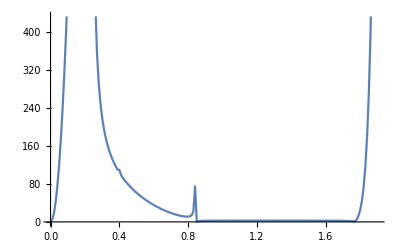

```mathematica
Λ[0,0.001,1,0,-0,0]
```

```mathematica
VLD[a_,b_]:= ({{0, 0, 0, 0, 0, 0, 0}, {a, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {b, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {a, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})
```

```mathematica
VDL[a_,b_]:= ConjugateTranspose[VLD[a,b]]
```

```mathematica
J1[ω_,δ_,t_,ϵ_,ϵ2_]:=Inverse[(ω+ⅈ*δ-ϵ2)IdentityMatrix[7]]
```

```mathematica
GS[ω_,δ_,t_,ϵ_,ϵ2_,a_,b_]:= Inverse[IdentityMatrix[7]-J1[ω,δ,t,ϵ,ϵ2].VDL[a,b].SR[ω,δ,1,0].VLD[a,b]].J1[ω,δ,t,ϵ,ϵ2]
```

```mathematica
I2l[ω_,δ_,t_,ϵ_,ϵ2_,a_,b_]:= Inverse[IdentityMatrix[7]-GS[ω,δ,t,ϵ,ϵ2,a,b].VDL[a,b].SR[ω,δ,1,0].VLD[a,b]].GS[ω,δ,t,ϵ,ϵ2,a,b]
```

```mathematica
SELFENERGY[ω_,δ_,a_,b_]:= VDL[a,b].SR[ω,δ,1,0].VLD[a,b]
```

```mathematica
ΓL[ω_,δ_,a_,b_]:= ⅈ*(SELFENERGY[ω,δ,a,b]-ConjugateTranspose[SELFENERGY[ω,δ,a,b]])
```

```mathematica
Transmission[ω_,δ_,t_,ϵ_,ϵ2_,a_,b_]:= Abs[Tr[ΓL[ω,δ,a,b]*Conjugate[I2l[ω,δ,t,ϵ,ϵ2,a,b]]*ΓL[ω,δ,a,b]*I2l[ω,δ,t,ϵ,ϵ2,a,b]]]
```

```mathematica
Trans[a_,b_]:=Join[Table[{ω,Transmission[ω,0.001,1,0,0,a,b]},{ω,Range[0,0.41,0.01]}],Table[{ω,2Transmission[ω,0.001,1,0,0,a,b]},{ω,Range[0.42,0.84,0.01]}],Table[{ω,3Transmission[ω,0.001,1,0,0,a,b]},{ω,Range[.85,1.76,0.01]}]]
```

```mathematica
f2[a_,b_]:=Module[{B1=Transpose[{final[[1;;150]][[;;,1]],(Trans[a,b][[1;;150,2]]- final[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.49}]/150]
```

```mathematica
σ3[b_]:=Table[{b,a,f2[b,a]},{a,Range[-1,1,0.05]}]
```

```mathematica
σσ=Join[σ3[-1],σ3[-9/10],σ3[-4/5],σ3[-7/10],σ3[-3/5],σ3[-1/2],σ3[-2/5],σ3[-3/10],σ3[-1/5],σ3[-1/10],σ3[0],σ3[1/10],σ3[1/5],σ3[3/10],σ3[2/5],σ3[1/2],σ3[3/5],σ3[7/10],σ3[4/5],σ3[9/10],σ3[1]]
```

{{-1,-1.,0.0127416},{-1,-0.95,0.01264},{-1,-0.9,0.0125041},{-1,-0.85,0.0123058},{-1,-0.8,0.0120345},{-1,-0.75,0.0116527},{-1,-0.7,0.0111371},{-1,-0.65,0.0104848},{-1,-0.6,0.00975195},{-1,-0.55,0.00889502},{-1,-0.5,0.00798348},{-1,-0.45,0.0070697},{-1,-0.4,0.00621143},{-1,-0.35,0.00545799},{-1,-0.3,0.00483944},{-1,-0.25,0.00436896},{-1,-0.2,0.00404851},{-1,-0.15,0.00387167},{-1,-0.1,0.00382487},{-1,-0.05,0.00388758},{-1,0.,0.0040305},{-1,0.05,0.00421212},{-1,0.1,0.00437813},{-1,0.15,0.00446867},{-1,0.2,0.00443355},{-1,0.25,0.00424847},{-1,0.3,0.00392309},{-1,0.35,0.00349657},{-1,0.4,0.00302396},{-1,0.45,0.00256069},{-1,0.5,0.00215119},{-1,0.55,0.00182374},{-1,0.6,0.00159053},{-1,0.65,0.00145087},{-1,0.7,0.00139547},{-1,0.75,0.0014104},{-1,0.8,0.0014802},{-1,0.85,0.00158988},{-1,0.9,0.00172614},{-1,0.95,0.0018778},{-1,1.,0.00203594},{-9/10,-1.,0.0128824},{-9/10,-0.95,0.0128353},{-9/10,-0.9,0.0127644},{-9/10,-0.85,0.0126612},{-9/10,-0.8,0.0125448},{-9/10,-0.75,0.0122943},{-9/10,-0.7,0.011985},{-9/10,-0.65,0.0115456},{-9/10,-0.6,0.0109425},{-9/10,-0.55,0.0101872},{-9/10,-0.5,0.00932701},{-9/10,-0.45,0.00833714},{-9/10,-0.4,0.0073076},{-9/10,-0.35,0.00630584},{-9/10,-0.3,0.00540256},{-9/10,-0.25,0.00464886},{-9/10,-0.2,0.00407284},{-9/10,-0.15,0.0036868},{-9/10,-0.1,0.00349188},{-9/10,-0.05,0.00347833},{-9/10,0.,0.00362303},{-9/10,0.05,0.00388376},{-9/10,0.1,0.00419355},{-9/10,0.15,0.00446428},{-9/10,0.2,0.00460596},{-9/10,0.25,0.0045557},{-9/10,0.3,0.00429993},{-9/10,0.35,0.00387613},{-9/10,0.4,0.00335504},{-9/10,0.45,0.00281541},{-9/10,0.5,0.00232332},{-9/10,0.55,0.00192189},{-9/10,0.6,0.00163042},{-9/10,0.65,0.00144924},{-9/10,0.7,0.00136647},{-9/10,0.75,0.00136413},{-9/10,0.8,0.00142268},{-9/10,0.85,0.00152381},{-9/10,0.9,0.0016518},{-9/10,0.95,0.00179399},{-9/10,1.,0.00194069},{-4/5,-1.,0.0130197},{-4/5,-0.95,0.0130004},{-4/5,-0.9,0.0129716},{-4/5,-0.85,0.0129354},{-4/5,-0.8,0.0128766},{-4/5,-0.75,0.0127732},{-4/5,-0.7,0.0126157},{-4/5,-0.65,0.0123818},{-4/5,-0.6,0.0120357},{-4/5,-0.55,0.0115309},{-4/5,-0.5,0.0108286},{-4/5,-0.45,0.00994771},{-4/5,-0.4,0.00892215},{-4/5,-0.35,0.00777084},{-4/5,-0.3,0.0065929},{-4/5,-0.25,0.00547888},{-4/5,-0.2,0.00451072},{-4/5,-0.15,0.0037432},{-4/5,-0.1,0.00320974},{-4/5,-0.05,0.00293044},{-4/5,0.,0.00291132},{-4/5,0.05,0.00313545},{-4/5,0.1,0.00354809},{-4/5,0.15,0.00404574},{-4/5,0.2,0.00448727},{-4/5,0.25,0.00473497},{-4/5,0.3,0.00470578},{-4/5,0.35,0.00439976},{-4/5,0.4,0.00388962},{-4/5,0.45,0.00328357},{-4/5,0.5,0.00268569},{-4/5,0.55,0.00217089},{-4/5,0.6,0.00177787},{-4/5,0.65,0.00151478},{-4/5,0.7,0.00136974},{-4/5,0.75,0.001321},{-4/5,0.8,0.00134426},{-4/5,0.85,0.00141698},{-4/5,0.9,0.00152026},{-4/5,0.95,0.00163941},{-4/5,1.,0.00176356},{-7/10,-1.,0.0130986},{-7/10,-0.95,0.0131373},{-7/10,-0.9,0.0131705},{-7/10,-0.85,0.0131977},{-7/10,-0.8,0.0132159},{-7/10,-0.75,0.013212},{-7/10,-0.7,0.0131818},{-7/10,-0.65,0.0131102},{-7/10,-0.6,0.0129761},{-7/10,-0.55,0.0127485},{-7/10,-0.5,0.0123838},{-7/10,-0.45,0.0118231},{-7/10,-0.4,0.011038},{-7/10,-0.35,0.00999478},{-7/10,-0.3,0.00877341},{-7/10,-0.25,0.00741808},{-7/10,-0.2,0.00604097},{-7/10,-0.15,0.00475567},{-7/10,-0.1,0.00365616},{-7/10,-0.05,0.00281072},{-7/10,0.,0.00227536},{-7/10,0.05,0.00209598},{-7/10,0.1,0.00229053},{-7/10,0.15,0.00281552},{-7/10,0.2,0.0035378},{-7/10,0.25,0.00424829},{-7/10,0.3,0.00473078},{-7/10,0.35,0.00484826},{-7/10,0.4,0.0045898},{-7/10,0.45,0.00405397},{-7/10,0.5,0.00338983},{-7/10,0.55,0.0027354},{-7/10,0.6,0.00218217},{-7/10,0.65,0.0017699},{-7/10,0.7,0.00149957},{-7/10,0.75,0.00135065},{-7/10,0.8,0.00129489},{-7/10,0.85,0.00130454},{-7/10,0.9,0.00135616},{-7/10,0.95,0.00143166},{-7/10,1.,0.0015179},{-3/5,-1.,0.0131786},{-3/5,-0.95,0.0132789},{-3/5,-0.9,0.0133851},{-3/5,-0.85,0.0134768},{-3/5,-0.8,0.0136105},{-3/5,-0.75,0.0137213},{-3/5,-0.7,0.0138292},{-3/5,-0.65,0.0139287},{-3/5,-0.6,0.0139912},{-3/5,-0.55,0.0140167},{-3/5,-0.5,0.0139905},{-3/5,-0.45,0.0138199},{-3/5,-0.4,0.0135041},{-3/5,-0.35,0.0129378},{-3/5,-0.3,0.0121028},{-3/5,-0.25,0.0109255},{-3/5,-0.2,0.00950987},{-3/5,-0.15,0.007919},{-3/5,-0.1,0.00628003},{-3/5,-0.05,0.00472285},{-3/5,0.,0.00335473},{-3/5,0.05,0.00227165},{-3/5,0.1,0.00157629},{-3/5,0.15,0.00136368},{-3/5,0.2,0.0016692},{-3/5,0.25,0.00240655},{-3/5,0.3,0.00335282},{-3/5,0.35,0.00421315},{-3/5,0.4,0.0047318},{-3/5,0.45,0.00478768},{-3/5,0.5,0.00442552},{-3/5,0.55,0.00380733},{-3/5,0.6,0.00311966},{-3/5,0.65,0.00249996},{-3/5,0.7,0.0020146},{-3/5,0.75,0.00167438},{-3/5,0.8,0.00146013},{-3/5,0.85,0.00134251},{-3/5,0.9,0.00129289},{-3/5,0.95,0.00128774},{-3/5,1.,0.00130939},{-1/2,-1.,0.0131477},{-1/2,-0.95,0.013351},{-1/2,-0.9,0.0135699},{-1/2,-0.85,0.0138071},{-1/2,-0.8,0.0140634},{-1/2,-0.75,0.0143547},{-1/2,-0.7,0.0146288},{-1/2,-0.65,0.0149399},{-1/2,-0.6,0.0152533},{-1/2,-0.55,0.0155603},{-1/2,-0.5,0.015847},{-1/2,-0.45,0.0160918},{-1/2,-0.4,0.0162566},{-1/2,-0.35,0.0162968},{-1/2,-0.3,0.0161436},{-1/2,-0.25,0.0157013},{-1/2,-0.2,0.0148941},{-1/2,-0.15,0.0136925},{-1/2,-0.1,0.0121477},{-1/2,-0.05,0.010346},{-1/2,0.,0.00842248},{-1/2,0.05,0.00650992},{-1/2,0.1,0.00472114},{-1/2,0.15,0.00317788},{-1/2,0.2,0.00203013},{-1/2,0.25,0.00142214},{-1/2,0.3,0.00141913},{-1/2,0.35,0.00195242},{-1/2,0.4,0.00282348},{-1/2,0.45,0.00374929},{-1/2,0.5,0.00443377},{-1/2,0.55,0.0046756},{-1/2,0.6,0.00446145},{-1/2,0.65,0.00394543},{-1/2,0.7,0.0033281},{-1/2,0.75,0.00275478},{-1/2,0.8,0.00229165},{-1/2,0.85,0.00194915},{-1/2,0.9,0.00171118},{-1/2,0.95,0.00155409},{-1/2,1.,0.0014556},{-2/5,-1.,0.0127582},{-2/5,-0.95,0.0131488},{-2/5,-0.9,0.0135665},{-2/5,-0.85,0.014015},{-2/5,-0.8,0.0144829},{-2/5,-0.75,0.0149921},{-2/5,-0.7,0.0155472},{-2/5,-0.65,0.0161398},{-2/5,-0.6,0.0167617},{-2/5,-0.55,0.0174022},{-2/5,-0.5,0.0180475},{-2/5,-0.45,0.0186784},{-2/5,-0.4,0.0192698},{-2/5,-0.35,0.0197959},{-2/5,-0.3,0.0202179},{-2/5,-0.25,0.0204855},{-2/5,-0.2,0.0205236},{-2/5,-0.15,0.0202333},{-2/5,-0.1,0.0194983},{-2/5,-0.05,0.018314},{-2/5,0.,0.0167029},{-2/5,0.05,0.014744},{-2/5,0.1,0.0125776},{-2/5,0.15,0.0103283},{-2/5,0.2,0.00809765},{-2/5,0.25,0.00600172},{-2/5,0.3,0.00419488},{-2/5,0.35,0.00284006},{-2/5,0.4,0.00205557},{-2/5,0.45,0.00188301},{-2/5,0.5,0.00227029},{-2/5,0.55,0.00304135},{-2/5,0.6,0.00389069},{-2/5,0.65,0.00448878},{-2/5,0.7,0.0046619},{-2/5,0.75,0.00445884},{-2/5,0.8,0.00404603},{-2/5,0.85,0.00357763},{-2/5,0.9,0.00314442},{-2/5,0.95,0.00278242},{-2/5,1.,0.00249641},{-3/10,-1.,0.0112828},{-3/10,-0.95,0.0120558},{-3/10,-0.9,0.0128427},{-3/10,-0.85,0.0136537},{-3/10,-0.8,0.0144989},{-3/10,-0.75,0.0153894},{-3/10,-0.7,0.0163246},{-3/10,-0.65,0.0172981},{-3/10,-0.6,0.0182971},{-3/10,-0.55,0.0193042},{-3/10,-0.5,0.0202936},{-3/10,-0.45,0.0212409},{-3/10,-0.4,0.0221257},{-3/10,-0.35,0.0229262},{-3/10,-0.3,0.0236234},{-3/10,-0.25,0.0241954},{-3/10,-0.2,0.0246315},{-3/10,-0.15,0.0248763},{-3/10,-0.1,0.0248945},{-3/10,-0.05,0.0245973},{-3/10,0.,0.023873},{-3/10,0.05,0.0226572},{-3/10,0.1,0.0210254},{-3/10,0.15,0.0189867},{-3/10,0.2,0.0166822},{-3/10,0.25,0.0142167},{-3/10,0.3,0.0116682},{-3/10,0.35,0.00911874},{-3/10,0.4,0.00669768},{-3/10,0.45,0.00458388},{-3/10,0.5,0.00297404},{-3/10,0.55,0.00203602},{-3/10,0.6,0.00184571},{-3/10,0.65,0.00231296},{-3/10,0.7,0.00315643},{-3/10,0.75,0.00400553},{-3/10,0.8,0.00458586},{-3/10,0.85,0.00482004},{-3/10,0.9,0.00477766},{-3/10,0.95,0.00457236},{-3/10,1.,0.00429828},{-1/5,-1.,0.00812466},{-1/5,-0.95,0.00915168},{-1/5,-0.9,0.0103391},{-1/5,-0.85,0.0116548},{-1/5,-0.8,0.0131285},{-1/5,-0.75,0.01468},{-1/5,-0.7,0.0162534},{-1/5,-0.65,0.0178143},{-1/5,-0.6,0.0193318},{-1/5,-0.55,0.0207708},{-1/5,-0.5,0.0220994},{-1/5,-0.45,0.0232842},{-1/5,-0.4,0.0243142},{-1/5,-0.35,0.025184},{-1/5,-0.3,0.0258849},{-1/5,-0.25,0.026431},{-1/5,-0.2,0.0268395},{-1/5,-0.15,0.0271211},{-1/5,-0.1,0.0272876},{-1/5,-0.05,0.0273308},{-1/5,0.,0.0272098},{-1/5,0.05,0.0268709},{-1/5,0.1,0.0262103},{-1/5,0.15,0.0251143},{-1/5,0.2,0.0235879},{-1/5,0.25,0.0216375},{-1/5,0.3,0.0193255},{-1/5,0.35,0.016738},{-1/5,0.4,0.0139498},{-1/5,0.45,0.0110442},{-1/5,0.5,0.00815965},{-1/5,0.55,0.00551188},{-1/5,0.6,0.00336355},{-1/5,0.65,0.00194724},{-1/5,0.7,0.00136971},{-1/5,0.75,0.00154487},{-1/5,0.8,0.00221178},{-1/5,0.85,0.00304689},{-1/5,0.9,0.00379572},{-1/5,0.95,0.00433438},{-1/5,1.,0.00464868},{-1/10,-1.,0.00443073},{-1/10,-0.95,0.00514759},{-1/10,-0.9,0.00618716},{-1/10,-0.85,0.00759048},{-1/10,-0.8,0.00936248},{-1/10,-0.75,0.0114616},{-1/10,-0.7,0.0137933},{-1/10,-0.65,0.016204},{-1/10,-0.6,0.0186045},{-1/10,-0.55,0.0208087},{-1/10,-0.5,0.0226871},{-1/10,-0.45,0.0242339},{-1/10,-0.4,0.0254531},{-1/10,-0.35,0.0263489},{-1/10,-0.3,0.0269897},{-1/10,-0.25,0.0274204},{-1/10,-0.2,0.0276912},{-1/10,-0.15,0.0278474},{-1/10,-0.1,0.0279352},{-1/10,-0.05,0.027973},{-1/10,0.,0.0279721},{-1/10,0.05,0.0279319},{-1/10,0.1,0.027805},{-1/10,0.15,0.0275408},{-1/10,0.2,0.0270395},{-1/10,0.25,0.0261694},{-1/10,0.3,0.0248376},{-1/10,0.35,0.0229778},{-1/10,0.4,0.0206459},{-1/10,0.45,0.0179001},{-1/10,0.5,0.0148634},{-1/10,0.55,0.0117013},{-1/10,0.6,0.00862273},{-1/10,0.65,0.00586922},{-1/10,0.7,0.00367482},{-1/10,0.75,0.00219845},{-1/10,0.8,0.00146696},{-1/10,0.85,0.00136736},{-1/10,0.9,0.00169666},{-1/10,0.95,0.00223815},{-1/10,1.,0.00282111},{0,-1.,0.00229245},{0,-0.95,0.00229683},{0,-0.9,0.00259929},{0,-0.85,0.00332574},{0,-0.8,0.00458076},{0,-0.75,0.00641316},{0,-0.7,0.00878975},{0,-0.65,0.0115883},{0,-0.6,0.0146139},{0,-0.55,0.017638},{0,-0.5,0.0204231},{0,-0.45,0.0228226},{0,-0.4,0.0247305},{0,-0.35,0.0260949},{0,-0.3,0.0269899},{0,-0.25,0.0275308},{0,-0.2,0.027823},{0,-0.15,0.0279596},{0,-0.1,0.0280102},{0,-0.05,0.0280218},{0,0.,0.0280002},{0,0.05,0.0280218},{0,0.1,0.0280102},{0,0.15,0.0279596},{0,0.2,0.027823},{0,0.25,0.0275308},{0,0.3,0.0269899},{0,0.35,0.0260949},{0,0.4,0.0247305},{0,0.45,0.0228226},{0,0.5,0.0204231},{0,0.55,0.017638},{0,0.6,0.0146139},{0,0.65,0.0115883},{0,0.7,0.00878975},{0,0.75,0.00641316},{0,0.8,0.00458076},{0,0.85,0.00332574},{0,0.9,0.00259929},{0,0.95,0.00229683},{0,1.,0.00229245},{1/10,-1.,0.00282111},{1/10,-0.95,0.00223815},{1/10,-0.9,0.00169666},{1/10,-0.85,0.00136736},{1/10,-0.8,0.00146696},{1/10,-0.75,0.00219845},{1/10,-0.7,0.00367482},{1/10,-0.65,0.00586922},{1/10,-0.6,0.00862273},{1/10,-0.55,0.0117013},{1/10,-0.5,0.0148634},{1/10,-0.45,0.0179001},{1/10,-0.4,0.0206459},{1/10,-0.35,0.0229778},{1/10,-0.3,0.0248376},{1/10,-0.25,0.0261694},{1/10,-0.2,0.0270395},{1/10,-0.15,0.0275408},{1/10,-0.1,0.027805},{1/10,-0.05,0.0279319},{1/10,0.,0.0279721},{1/10,0.05,0.027973},{1/10,0.1,0.0279352},{1/10,0.15,0.0278474},{1/10,0.2,0.0276912},{1/10,0.25,0.0274204},{1/10,0.3,0.0269897},{1/10,0.35,0.0263489},{1/10,0.4,0.0254531},{1/10,0.45,0.0242339},{1/10,0.5,0.0226871},{1/10,0.55,0.0208087},{1/10,0.6,0.0186045},{1/10,0.65,0.016204},{1/10,0.7,0.0137933},{1/10,0.75,0.0114616},{1/10,0.8,0.00936248},{1/10,0.85,0.00759048},{1/10,0.9,0.00618716},{1/10,0.95,0.00514759},{1/10,1.,0.00443073},{1/5,-1.,0.00464868},{1/5,-0.95,0.00433438},{1/5,-0.9,0.00379572},{1/5,-0.85,0.00304689},{1/5,-0.8,0.00221178},{1/5,-0.75,0.00154487},{1/5,-0.7,0.00136971},{1/5,-0.65,0.00194724},{1/5,-0.6,0.00336355},{1/5,-0.55,0.00551188},{1/5,-0.5,0.00815965},{1/5,-0.45,0.0110442},{1/5,-0.4,0.0139498},{1/5,-0.35,0.016738},{1/5,-0.3,0.0193255},{1/5,-0.25,0.0216375},{1/5,-0.2,0.0235879},{1/5,-0.15,0.0251143},{1/5,-0.1,0.0262103},{1/5,-0.05,0.0268709},{1/5,0.,0.0272098},{1/5,0.05,0.0273308},{1/5,0.1,0.0272876},{1/5,0.15,0.0271211},{1/5,0.2,0.0268395},{1/5,0.25,0.026431},{1/5,0.3,0.0258849},{1/5,0.35,0.025184},{1/5,0.4,0.0243142},{1/5,0.45,0.0232842},{1/5,0.5,0.0220994},{1/5,0.55,0.0207708},{1/5,0.6,0.0193318},{1/5,0.65,0.0178143},{1/5,0.7,0.0162534},{1/5,0.75,0.01468},{1/5,0.8,0.0131285},{1/5,0.85,0.0116548},{1/5,0.9,0.0103391},{1/5,0.95,0.00915168},{1/5,1.,0.00812466},{3/10,-1.,0.00429828},{3/10,-0.95,0.00457236},{3/10,-0.9,0.00477766},{3/10,-0.85,0.00482004},{3/10,-0.8,0.00458586},{3/10,-0.75,0.00400553},{3/10,-0.7,0.00315643},{3/10,-0.65,0.00231296},{3/10,-0.6,0.00184571},{3/10,-0.55,0.00203602},{3/10,-0.5,0.00297404},{3/10,-0.45,0.00458388},{3/10,-0.4,0.00669768},{3/10,-0.35,0.00911874},{3/10,-0.3,0.0116682},{3/10,-0.25,0.0142167},{3/10,-0.2,0.0166822},{3/10,-0.15,0.0189867},{3/10,-0.1,0.0210254},{3/10,-0.05,0.0226572},{3/10,0.,0.023873},{3/10,0.05,0.0245973},{3/10,0.1,0.0248945},{3/10,0.15,0.0248763},{3/10,0.2,0.0246315},{3/10,0.25,0.0241954},{3/10,0.3,0.0236234},{3/10,0.35,0.0229262},{3/10,0.4,0.0221257},{3/10,0.45,0.0212409},{3/10,0.5,0.0202936},{3/10,0.55,0.0193042},{3/10,0.6,0.0182971},{3/10,0.65,0.0172981},{3/10,0.7,0.0163246},{3/10,0.75,0.0153894},{3/10,0.8,0.0144989},{3/10,0.85,0.0136537},{3/10,0.9,0.0128427},{3/10,0.95,0.0120558},{3/10,1.,0.0112828},{2/5,-1.,0.00249641},{2/5,-0.95,0.00278242},{2/5,-0.9,0.00314442},{2/5,-0.85,0.00357763},{2/5,-0.8,0.00404603},{2/5,-0.75,0.00445884},{2/5,-0.7,0.0046619},{2/5,-0.65,0.00448878},{2/5,-0.6,0.00389069},{2/5,-0.55,0.00304135},{2/5,-0.5,0.00227029},{2/5,-0.45,0.00188301},{2/5,-0.4,0.00205557},{2/5,-0.35,0.00284006},{2/5,-0.3,0.00419488},{2/5,-0.25,0.00600172},{2/5,-0.2,0.00809765},{2/5,-0.15,0.0103283},{2/5,-0.1,0.0125776},{2/5,-0.05,0.014744},{2/5,0.,0.0167029},{2/5,0.05,0.018314},{2/5,0.1,0.0194983},{2/5,0.15,0.0202333},{2/5,0.2,0.0205236},{2/5,0.25,0.0204855},{2/5,0.3,0.0202179},{2/5,0.35,0.0197959},{2/5,0.4,0.0192698},{2/5,0.45,0.0186784},{2/5,0.5,0.0180475},{2/5,0.55,0.0174022},{2/5,0.6,0.0167617},{2/5,0.65,0.0161398},{2/5,0.7,0.0155472},{2/5,0.75,0.0149921},{2/5,0.8,0.0144829},{2/5,0.85,0.014015},{2/5,0.9,0.0135665},{2/5,0.95,0.0131488},{2/5,1.,0.0127582},{1/2,-1.,0.0014556},{1/2,-0.95,0.00155409},{1/2,-0.9,0.00171118},{1/2,-0.85,0.00194915},{1/2,-0.8,0.00229165},{1/2,-0.75,0.00275478},{1/2,-0.7,0.0033281},{1/2,-0.65,0.00394543},{1/2,-0.6,0.00446145},{1/2,-0.55,0.0046756},{1/2,-0.5,0.00443377},{1/2,-0.45,0.00374929},{1/2,-0.4,0.00282348},{1/2,-0.35,0.00195242},{1/2,-0.3,0.00141913},{1/2,-0.25,0.00142214},{1/2,-0.2,0.00203013},{1/2,-0.15,0.00317788},{1/2,-0.1,0.00472114},{1/2,-0.05,0.00650992},{1/2,0.,0.00842248},{1/2,0.05,0.010346},{1/2,0.1,0.0121477},{1/2,0.15,0.0136925},{1/2,0.2,0.0148941},{1/2,0.25,0.0157013},{1/2,0.3,0.0161436},{1/2,0.35,0.0162968},{1/2,0.4,0.0162566},{1/2,0.45,0.0160918},{1/2,0.5,0.015847},{1/2,0.55,0.0155603},{1/2,0.6,0.0152533},{1/2,0.65,0.0149399},{1/2,0.7,0.0146288},{1/2,0.75,0.0143547},{1/2,0.8,0.0140634},{1/2,0.85,0.0138071},{1/2,0.9,0.0135699},{1/2,0.95,0.013351},{1/2,1.,0.0131477},{3/5,-1.,0.00130939},{3/5,-0.95,0.00128774},{3/5,-0.9,0.00129289},{3/5,-0.85,0.00134251},{3/5,-0.8,0.00146013},{3/5,-0.75,0.00167438},{3/5,-0.7,0.0020146},{3/5,-0.65,0.00249996},{3/5,-0.6,0.00311966},{3/5,-0.55,0.00380733},{3/5,-0.5,0.00442552},{3/5,-0.45,0.00478768},{3/5,-0.4,0.0047318},{3/5,-0.35,0.00421315},{3/5,-0.3,0.00335282},{3/5,-0.25,0.00240655},{3/5,-0.2,0.0016692},{3/5,-0.15,0.00136368},{3/5,-0.1,0.00157629},{3/5,-0.05,0.00227165},{3/5,0.,0.00335473},{3/5,0.05,0.00472285},{3/5,0.1,0.00628003},{3/5,0.15,0.007919},{3/5,0.2,0.00950987},{3/5,0.25,0.0109255},{3/5,0.3,0.0121028},{3/5,0.35,0.0129378},{3/5,0.4,0.0135041},{3/5,0.45,0.0138199},{3/5,0.5,0.0139905},{3/5,0.55,0.0140167},{3/5,0.6,0.0139912},{3/5,0.65,0.0139287},{3/5,0.7,0.0138292},{3/5,0.75,0.0137213},{3/5,0.8,0.0136105},{3/5,0.85,0.0134768},{3/5,0.9,0.0133851},{3/5,0.95,0.0132789},{3/5,1.,0.0131786},{7/10,-1.,0.0015179},{7/10,-0.95,0.00143166},{7/10,-0.9,0.00135616},{7/10,-0.85,0.00130454},{7/10,-0.8,0.00129489},{7/10,-0.75,0.00135065},{7/10,-0.7,0.00149957},{7/10,-0.65,0.0017699},{7/10,-0.6,0.00218217},{7/10,-0.55,0.0027354},{7/10,-0.5,0.00338983},{7/10,-0.45,0.00405397},{7/10,-0.4,0.0045898},{7/10,-0.35,0.00484826},{7/10,-0.3,0.00473078},{7/10,-0.25,0.00424829},{7/10,-0.2,0.0035378},{7/10,-0.15,0.00281552},{7/10,-0.1,0.00229053},{7/10,-0.05,0.00209598},{7/10,0.,0.00227536},{7/10,0.05,0.00281072},{7/10,0.1,0.00365616},{7/10,0.15,0.00475567},{7/10,0.2,0.00604097},{7/10,0.25,0.00741808},{7/10,0.3,0.00877341},{7/10,0.35,0.00999478},{7/10,0.4,0.011038},{7/10,0.45,0.0118231},{7/10,0.5,0.0123838},{7/10,0.55,0.0127485},{7/10,0.6,0.0129761},{7/10,0.65,0.0131102},{7/10,0.7,0.0131818},{7/10,0.75,0.013212},{7/10,0.8,0.0132159},{7/10,0.85,0.0131977},{7/10,0.9,0.0131705},{7/10,0.95,0.0131373},{7/10,1.,0.0130986},{4/5,-1.,0.00176356},{4/5,-0.95,0.00163941},{4/5,-0.9,0.00152026},{4/5,-0.85,0.00141698},{4/5,-0.8,0.00134426},{4/5,-0.75,0.001321},{4/5,-0.7,0.00136974},{4/5,-0.65,0.00151478},{4/5,-0.6,0.00177787},{4/5,-0.55,0.00217089},{4/5,-0.5,0.00268569},{4/5,-0.45,0.00328357},{4/5,-0.4,0.00388962},{4/5,-0.35,0.00439976},{4/5,-0.3,0.00470578},{4/5,-0.25,0.00473497},{4/5,-0.2,0.00448727},{4/5,-0.15,0.00404574},{4/5,-0.1,0.00354809},{4/5,-0.05,0.00313545},{4/5,0.,0.00291132},{4/5,0.05,0.00293044},{4/5,0.1,0.00320974},{4/5,0.15,0.0037432},{4/5,0.2,0.00451072},{4/5,0.25,0.00547888},{4/5,0.3,0.0065929},{4/5,0.35,0.00777084},{4/5,0.4,0.00892215},{4/5,0.45,0.00994771},{4/5,0.5,0.0108286},{4/5,0.55,0.0115309},{4/5,0.6,0.0120357},{4/5,0.65,0.0123818},{4/5,0.7,0.0126157},{4/5,0.75,0.0127732},{4/5,0.8,0.0128766},{4/5,0.85,0.0129354},{4/5,0.9,0.0129716},{4/5,0.95,0.0130004},{4/5,1.,0.0130197},{9/10,-1.,0.00194069},{9/10,-0.95,0.00179399},{9/10,-0.9,0.0016518},{9/10,-0.85,0.00152381},{9/10,-0.8,0.00142268},{9/10,-0.75,0.00136413},{9/10,-0.7,0.00136647},{9/10,-0.65,0.00144924},{9/10,-0.6,0.00163042},{9/10,-0.55,0.00192189},{9/10,-0.5,0.00232332},{9/10,-0.45,0.00281541},{9/10,-0.4,0.00335504},{9/10,-0.35,0.00387613},{9/10,-0.3,0.00429993},{9/10,-0.25,0.0045557},{9/10,-0.2,0.00460596},{9/10,-0.15,0.00446428},{9/10,-0.1,0.00419355},{9/10,-0.05,0.00388376},{9/10,0.,0.00362303},{9/10,0.05,0.00347833},{9/10,0.1,0.00349188},{9/10,0.15,0.0036868},{9/10,0.2,0.00407284},{9/10,0.25,0.00464886},{9/10,0.3,0.00540256},{9/10,0.35,0.00630584},{9/10,0.4,0.0073076},{9/10,0.45,0.00833714},{9/10,0.5,0.00932701},{9/10,0.55,0.0101872},{9/10,0.6,0.0109425},{9/10,0.65,0.0115456},{9/10,0.7,0.011985},{9/10,0.75,0.0122943},{9/10,0.8,0.0125448},{9/10,0.85,0.0126612},{9/10,0.9,0.0127644},{9/10,0.95,0.0128353},{9/10,1.,0.0128824},{1,-1.,0.00203594},{1,-0.95,0.0018778},{1,-0.9,0.00172614},{1,-0.85,0.00158988},{1,-0.8,0.0014802},{1,-0.75,0.0014104},{1,-0.7,0.00139547},{1,-0.65,0.00145087},{1,-0.6,0.00159053},{1,-0.55,0.00182374},{1,-0.5,0.00215119},{1,-0.45,0.00256069},{1,-0.4,0.00302396},{1,-0.35,0.00349657},{1,-0.3,0.00392309},{1,-0.25,0.00424847},{1,-0.2,0.00443355},{1,-0.15,0.00446867},{1,-0.1,0.00437813},{1,-0.05,0.00421212},{1,0.,0.0040305},{1,0.05,0.00388758},{1,0.1,0.00382487},{1,0.15,0.00387167},{1,0.2,0.00404851},{1,0.25,0.00436896},{1,0.3,0.00483944},{1,0.35,0.00545799},{1,0.4,0.00621143},{1,0.45,0.0070697},{1,0.5,0.00798348},{1,0.55,0.00889502},{1,0.6,0.00975195},{1,0.65,0.0104848},{1,0.7,0.0111371},{1,0.75,0.0116527},{1,0.8,0.0120345},{1,0.85,0.0123058},{1,0.9,0.0125041},{1,0.95,0.01264},{1,1.,0.0127416}}

```mathematica
{Min/@Transpose[σσ]}[[1,3]]
```

0.00128774

```mathematica
Extract[Transpose[σσ],{{1,Position[Transpose[σσ],{Min/@Transpose[σσ]}[[1,3]]][[1,2]]},{2,Position[Transpose[σσ],{Min/@Transpose[σσ]}[[1,3]]][[1,2]]}}]
```

{3/5,-0.95}

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,1.59702},{3,1.79361},{4,1.59702},{5,1.85339},{6,1.71077},{7,1.57321},{8,1.83479},{9,1.65967},{10,1.88238},{11,1.92727},{12,1.85788},{13,1.74761},{14,1.82715},{15,1.86977},{16,1.60084},{17,1.97107},{18,1.74314},{19,1.67856},{20,1.52644},{21,1.88744},{22,1.88171},{23,1.80086},{24,1.74314},{25,1.55546},{26,1.83683},{27,1.93287},{28,1.81079},{29,1.83683},{30,1.83711},{31,1.78058},{32,1.52826},{33,1.89475},{34,1.88383},{35,1.62093},{36,1.89475},{37,1.62093},{38,1.92917},{39,1.90434},{40,1.95073},{41,1.83093},{42,1.82974},{43,1.83627},{44,1.63229},{45,1.83093},{46,1.76194},{47,1.57669},{48,1.84207}}

```mathematica
{Max[{Min/@%519}],Min[{Min/@%519}],final7[[51,2]]}
```

{1.97107,1.52644,1.77335}

```mathematica
list={{1,2},{3,4},{5,6}};
```

```mathematica
Manipulate[ρ7[[i]],{i,1,Length@ρ7,1}]
```

Part::partd: Part specification ρ7⟦1⟧ is longer than depth of object.

```mathematica
ρ7[[2]]
```

{{0.,-0.95,2.73808},{0.05,-0.95,2.60618},{0.1,-0.95,2.26907},{0.15,-0.95,1.85035},{0.2,-0.95,1.48685},{0.25,-0.95,1.30542},{0.3,-0.95,1.43276},{0.35,-0.95,1.33969},{0.4,-0.95,0.897705},{0.45,-0.95,0.650923},{0.5,-0.95,0.543022},{0.55,-0.95,0.488877},{0.6,-0.95,0.459426},{0.65,-0.95,0.445782},{0.7,-0.95,0.442281},{0.75,-0.95,0.445828},{0.8,-0.95,0.454524},{0.85,-0.95,0.467105},{0.9,-0.95,0.482676},{0.95,-0.95,0.500572},{1.,-0.95,0.520283},{1.05,-0.95,0.541408},{1.1,-0.95,0.563623},{1.15,-0.95,0.58667},{1.2,-0.95,0.610336},{1.25,-0.95,0.634448},{1.3,-0.95,0.658862},{1.35,-0.95,0.683461},{1.4,-0.95,0.707527},{1.45,-0.95,0.729693},{1.5,-0.95,0.75153},{1.55,-0.95,0.773377},{1.6,-0.95,0.795175},{1.65,-0.95,0.816875},{1.7,-0.95,0.838433},{1.75,-0.95,0.859813},{1.8,-0.95,0.880985},{1.85,-0.95,0.901922},{1.9,-0.95,0.922604},{1.95,-0.95,0.943012},{2.,-0.95,0.963133}}

```mathematica
κ=Do[Join[ρ7[[i]]],{i,41}]
```

```mathematica
Table[Join[ρ7[[i]]],{i,41}]
```

{{{0.,-1.,2.4793},{0.05,-1.,2.31751},{0.1,-1.,2.05981},{0.15,-1.,1.73309},{0.2,-1.,1.41559},{0.25,-1.,1.17431},{0.3,-1.,1.09829},{0.35,-1.,1.37526},{0.4,-1.,1.62643},{0.45,-1.,1.12452},21,{1.55,-1.,0.795707},{1.6,-1.,0.817957},{1.65,-1.,0.840065},{1.7,-1.,0.861992},{1.75,-1.,0.883703},{1.8,-1.,0.90517},{1.85,-1.,0.92637},{1.9,-1.,0.947241},{1.95,-1.,0.96673},{2.,-1.,0.985934}},39,{1}}
 |  |  |  |

```mathematica
Dimensions[%208]
```

{41,41,3}

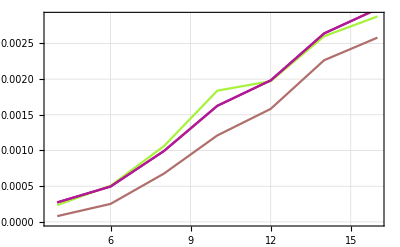

```mathematica
Show[ListLinePlot[{{4,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]]
```